# Notebook gg ⟶ J/ψ + J/ψ

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

### Set up of the parallel kernels:

```mathematica
<<"~/Bureau/notebooks/packages/tracer11.m"
ParallelEvaluate[<<"~/Bureau/notebooks/packages/tracer11.m"]
```

Remove::rmnsm: There are no symbols matching "Tracer`Private`*".

T R A C E R

=============

A MATHEMATICA PACKAGE FOR GAMMA-ALGEBRA IN ARBITRARY DIMENSIONS

by M. Jamin and M.E. Lautenbacher

Physics Dept. T31, Technical University Munich

Version 1.1.1 from Mon Dec 30 15:36:00 MET 1991

(based on MATHEMATICA Version 1.2)

The package defines the following commands:

"AntiCommute", "ContractEpsGamma", "Eps", "G",
"GammaTrace", "G5", "H",
"ListCommands", "NoSpur",
"OnShell", "OutputFormat", "RemoveHatMomenta",

"RemoveNCM", "S", "Sigma", "SortLine", "Spur", "T",
"ToDiracBasis",
"ToHatTilde", "ToOtimes", "ToUG5", "U",
"VectorDimension", "Version".

                                    Help on usage as usual per ?Name.

DEFAULT SETTINGS ON STARTUP:

----------------------------

NonCommutativeMultiply will be removed.

Current OutputFormat is set to "texlike".

Package uses a non anticommuting G5 in "d" dimensions.

Remove::rmnsm: There are no symbols matching "Tracer`Private`*".

T R A C E R

T R A C E R

=============

=============

A MATHEMATICA PACKAGE FOR GAMMA-ALGEBRA IN ARBITRARY DIMENSIONS

A MATHEMATICA PACKAGE FOR GAMMA-ALGEBRA IN ARBITRARY DIMENSIONS

by M. Jamin and M.E. Lautenbacher

by M. Jamin and M.E. Lautenbacher

Physics Dept. T31, Technical University Munich

Physics Dept. T31, Technical University Munich

Version 1.1.1 from Mon Dec 30 15:36:00 MET 1991

Version 1.1.1 from Mon Dec 30 15:36:00 MET 1991

(based on MATHEMATICA Version 1.2)

(based on MATHEMATICA Version 1.2)

The package defines the following commands:

"AntiCommute", "ContractEpsGamma", "Eps", "G",
"GammaTrace", "G5", "H",
"ListCommands", "NoSpur",
"OnShell", "OutputFormat", "RemoveHatMomenta",

"RemoveNCM", "S", "Sigma", "SortLine", "Spur", "T",
"ToDiracBasis",
"ToHatTilde", "ToOtimes", "ToUG5", "U",
"VectorDimension", "Version".

                                    Help on usage as usual per ?Name.

The package defines the following commands:

"AntiCommute", "ContractEpsGamma", "Eps", "G",
"GammaTrace", "G5", "H",
"ListCommands", "NoSpur",
"OnShell", "OutputFormat", "RemoveHatMomenta",

"RemoveNCM", "S", "Sigma", "SortLine", "Spur", "T",
"ToDiracBasis",
"ToHatTilde", "ToOtimes", "ToUG5", "U",
"VectorDimension", "Version".

                                    Help on usage as usual per ?Name.

DEFAULT SETTINGS ON STARTUP:

----------------------------

DEFAULT SETTINGS ON STARTUP:

----------------------------

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null.  (line 638 of "~/Bureau/notebooks/packages/tracer11.m").

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null.  (line 1098 of "~/Bureau/notebooks/packages/tracer11.m").

NonCommutativeMultiply will be removed.

NonCommutativeMultiply will be removed.

Current OutputFormat is set to "texlike".

Current OutputFormat is set to "texlike".

Package uses a non anticommuting G5 in "d" dimensions.

Package uses a non anticommuting G5 in "d" dimensions.

{Null,Null}

```mathematica
<<"/projet/pth/scarpa/notebooks/packages/tracer11.m"
ParallelEvaluate[<<"/projet/pth/scarpa/notebooks/packages/tracer11.m"]
```

Get::noopen: Cannot open /projet/pth/scarpa/notebooks/packages/tracer11.m.

$Failed

Get::noopen: Cannot open /projet/pth/scarpa/notebooks/packages/tracer11.m.

{$Failed,$Failed}

```mathematica
VectorDimension[4]
Spur[tr]
ParallelEvaluate[VectorDimension[4]]
ParallelEvaluate[Spur[tr]]
```

Dimension set to "4". NOTE: For this setting of the dimension the

Package uses the usual anticommuting G5 in "4" dimensions.

The gamma matrix line(s) "tr" will be traced.

Dimension set to "4". NOTE: For this setting of the dimension the

Dimension set to "4". NOTE: For this setting of the dimension the

Package uses the usual anticommuting G5 in "4" dimensions.

Package uses the usual anticommuting G5 in "4" dimensions.

{Null,Null}

The gamma matrix line(s) "tr" will be traced.

The gamma matrix line(s) "tr" will be traced.

{Null,Null}

{Null,Null}

{Null,Null}

{Null,Null,Null,Null}

The gamma matrix line(s) "tr" will be traced.

The gamma matrix line(s) "tr" will be traced.

The gamma matrix line(s) "tr" will be traced.

«1 more identical outputs»

{Null,Null,Null,Null}

## Tests on polarization vectors

```mathematica
Lψ//MatrixForm
```

((-MB^2+Mψ^2+s)/(2 Mψ √s) | (λ Cos[ϕ] Sin[θ])/(2 Mψ √s) | (λ Sin[θ] Sin[ϕ])/(2 Mψ √s) | (λ Cos[θ])/(2 Mψ √s)
(λ Cos[ϕ] Sin[θ])/(2 Mψ √s) | 1+(-1+(-MB^2+Mψ^2+s)/(2 Mψ √s)) Cos[ϕ]^2 Sin[θ]^2 | (-1+(-MB^2+Mψ^2+s)/(2 Mψ √s)) Cos[ϕ] Sin[θ]^2 Sin[ϕ] | (-1+(-MB^2+Mψ^2+s)/(2 Mψ √s)) Cos[θ] Cos[ϕ] Sin[θ]
(λ Sin[θ] Sin[ϕ])/(2 Mψ √s) | (-1+(-MB^2+Mψ^2+s)/(2 Mψ √s)) Cos[ϕ] Sin[θ]^2 Sin[ϕ] | 1+(-1+(-MB^2+Mψ^2+s)/(2 Mψ √s)) Sin[θ]^2 Sin[ϕ]^2 | (-1+(-MB^2+Mψ^2+s)/(2 Mψ √s)) Cos[θ] Sin[θ] Sin[ϕ]
(λ Cos[θ])/(2 Mψ √s) | (-1+(-MB^2+Mψ^2+s)/(2 Mψ √s)) Cos[θ] Cos[ϕ] Sin[θ] | (-1+(-MB^2+Mψ^2+s)/(2 Mψ √s)) Cos[θ] Sin[θ] Sin[ϕ] | 1+(-1+(-MB^2+Mψ^2+s)/(2 Mψ √s)) Cos[θ]^2)

```mathematica
Lψ-Transpose[Lψ]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Lψinv=Inverse[Lψ]//FullSimplify
```

{{(2 Mψ √s (-MB^2+Mψ^2+s))/((-MB^2+Mψ^2+s)^2-λ^2),-(2 Mψ √s λ Cos[ϕ] Sin[θ])/((-MB^2+Mψ^2+s)^2-λ^2),-(2 Mψ √s λ Sin[θ] Sin[ϕ])/((-MB^2+Mψ^2+s)^2-λ^2),-(2 Mψ √s λ Cos[θ])/((-MB^2+Mψ^2+s)^2-λ^2)},{-(2 Mψ √s λ Cos[ϕ] Sin[θ])/((-MB^2+Mψ^2+s)^2-λ^2),(2 ((3 MB^2-3 Mψ^2-2 Mψ √s-3 s) (MB^2-Mψ^2-s)-3 λ^2+((MB+Mψ-√s) (MB-Mψ+√s) (MB^2-Mψ^2-s)-λ^2) (Cos[2 θ]-2 Cos[2 ϕ] Sin[θ]^2)))/(8 (-MB^2+Mψ^2+s)^2-8 λ^2),-(((MB+Mψ-√s) (MB-Mψ+√s) (MB^2-Mψ^2-s)-λ^2) Sin[θ]^2 Sin[2 ϕ])/(2 (-MB^2+Mψ^2+s)^2-2 λ^2),-(((MB+Mψ-√s) (MB-Mψ+√s) (MB^2-Mψ^2-s)-λ^2) Cos[ϕ] Sin[2 θ])/(2 (-MB^2+Mψ^2+s)^2-2 λ^2)},{-(2 Mψ √s λ Sin[θ] Sin[ϕ])/((-MB^2+Mψ^2+s)^2-λ^2),-(((MB+Mψ-√s) (MB-Mψ+√s) (MB^2-Mψ^2-s)-λ^2) Sin[θ]^2 Sin[2 ϕ])/(2 (-MB^2+Mψ^2+s)^2-2 λ^2),(2 ((3 MB^2-3 Mψ^2-2 Mψ √s-3 s) (MB^2-Mψ^2-s)-3 λ^2+((MB+Mψ-√s) (MB-Mψ+√s) (MB^2-Mψ^2-s)-λ^2) (Cos[2 θ]+2 Cos[2 ϕ] Sin[θ]^2)))/(8 (-MB^2+Mψ^2+s)^2-8 λ^2),-(((MB+Mψ-√s) (MB-Mψ+√s) (MB^2-Mψ^2-s)-λ^2) Sin[2 θ] Sin[ϕ])/(2 (-MB^2+Mψ^2+s)^2-2 λ^2)},{-(2 Mψ √s λ Cos[θ])/((-MB^2+Mψ^2+s)^2-λ^2),-(((MB+Mψ-√s) (MB-Mψ+√s) (MB^2-Mψ^2-s)-λ^2) Cos[ϕ] Sin[2 θ])/(2 (-MB^2+Mψ^2+s)^2-2 λ^2),-(((MB+Mψ-√s) (MB-Mψ+√s) (MB^2-Mψ^2-s)-λ^2) Sin[2 θ] Sin[ϕ])/(2 (-MB^2+Mψ^2+s)^2-2 λ^2),(MB^4+(Mψ+√s)^2 (Mψ^2+s)-2 MB^2 (Mψ^2+Mψ √s+s)-λ^2-((MB+Mψ-√s) (MB-Mψ+√s) (MB^2-Mψ^2-s)-λ^2) Cos[2 θ])/(2 (-MB^2+Mψ^2+s)^2-2 λ^2)}}

```mathematica
qψv
```

{(-MB^2+Mψ^2+s)/(2 √s),(λ Cos[ϕ] Sin[θ])/(2 √s),(λ Sin[θ] Sin[ϕ])/(2 √s),(λ Cos[θ])/(2 √s)}

```mathematica
qψv.GT.qψv/.Replλ//FullSimplify
```

Mψ^2

```mathematica
ezψv=qψv/Mψ;
ezψv.GT.ezψv/.Replλ//FullSimplify
ezψv.GT.qψv/.Replλ//FullSimplify
Lψ.ezψv//FullSimplify
```

1

Mψ

{((-MB^2+Mψ^2+s)^2+λ^2)/(4 Mψ^2 s),((-MB^2+Mψ^2+s) λ Cos[ϕ] Sin[θ])/(2 Mψ^2 s),((-MB^2+Mψ^2+s) λ Sin[θ] Sin[ϕ])/(2 Mψ^2 s),((-MB^2+Mψ^2+s) λ Cos[θ])/(2 Mψ^2 s)}

```mathematica
qψown={Mψ,0,0,0};
qψown.Lψ//FullSimplify
%-qψv //FullSimplify
```

{(-MB^2+Mψ^2+s)/(2 √s),(λ Cos[ϕ] Sin[θ])/(2 √s),(λ Sin[θ] Sin[ϕ])/(2 √s),(λ Cos[θ])/(2 √s)}

{0,0,0,0}

```mathematica
qψown={Mψ,0,0,0};
Lψ.qψown//FullSimplify
%-qψv //FullSimplify
```

{(-MB^2+Mψ^2+s)/(2 √s),(λ Cos[ϕ] Sin[θ])/(2 √s),(λ Sin[θ] Sin[ϕ])/(2 √s),(λ Cos[θ])/(2 √s)}

{0,0,0,0}

```mathematica
ezv={0,0,0,1};
ezcsqtotv=FullSimplify[Lψ.ezv/.Replλ]
```

{(√(MB^4+(Mψ^2-s)^2-2 MB^2 (Mψ^2+s)) Cos[θ])/(2 Mψ √s),(-1+(-MB^2+Mψ^2+s)/(2 Mψ √s)) Cos[θ] Cos[ϕ] Sin[θ],(-1+(-MB^2+Mψ^2+s)/(2 Mψ √s)) Cos[θ] Sin[θ] Sin[ϕ],1+(-1+(-MB^2+Mψ^2+s)/(2 Mψ √s)) Cos[θ]^2}

```mathematica
ezcsqtotv.GT.ezcsqtotv//FullSimplify
```

-1

```mathematica
ezcsqtotv.GT.qψv/.Replλ//FullSimplify
```

0

```mathematica
Refine[(ezcsqtotv[[2;;3]].qψv[[2;;3]])/(√(ezcsqtotv[[2;;3]].ezcsqtotv[[2;;3]]*qψv[[2;;3]].qψv[[2;;3]])) //FullSimplify,{MB>0,Mψ>0,s>0,λ>0,0≤θ≤π,MB^2-(Mψ-√s)^2<0}]
```

Cos[θ]/Abs[Cos[θ]]

```mathematica
Xcsqtotv=kav/(kav.GT.(qψv+qBv))-kbv/(kbv.GT.(qψv+qBv))//FullSimplify
```

{0,0,0,2/(√s)}

```mathematica
Projv=-Xcsqtotv+(qψv.GT.Xcsqtotv)/(qψv.GT.qψv)qψv/.Replλ//FullSimplify
```

{-((-MB^2+Mψ^2+s) √(MB^4+(Mψ^2-s)^2-2 MB^2 (Mψ^2+s)) Cos[θ])/(2 Mψ^2 s^(3/2)),-(((MB-Mψ)^2-s) ((MB+Mψ)^2-s) Cos[ϕ] Sin[2 θ])/(4 Mψ^2 s^(3/2)),-(((MB-Mψ)^2-s) ((MB+Mψ)^2-s) Sin[2 θ] Sin[ϕ])/(4 Mψ^2 s^(3/2)),(-(MB^2-Mψ^2)^2+2 (MB^2-3 Mψ^2) s-s^2-((MB-Mψ)^2-s) ((MB+Mψ)^2-s) Cos[2 θ])/(4 Mψ^2 s^(3/2))}

```mathematica
Projv.GT.Projv//FullSimplify
```

-(MB^4+Mψ^4+6 Mψ^2 s+s^2-2 MB^2 (Mψ^2+s)+((MB-Mψ)^2-s) ((MB+Mψ)^2-s) Cos[2 θ])/(2 Mψ^2 s^2)

```mathematica
ϵLv=Projv/(√(-Projv.GT.Projv))//FullSimplify
```

{-((-MB^2+Mψ^2+s) √(MB^4+(Mψ^2-s)^2-2 MB^2 (Mψ^2+s)) Cos[θ])/(√2 Mψ^2 s^(3/2) √((MB^4+Mψ^4+6 Mψ^2 s+s^2-2 MB^2 (Mψ^2+s)+((MB-Mψ)^2-s) ((MB+Mψ)^2-s) Cos[2 θ])/(Mψ^2 s^2))),-(((MB-Mψ)^2-s) ((MB+Mψ)^2-s) Cos[ϕ] Sin[2 θ])/(2 √2 Mψ^2 s^(3/2) √((MB^4+Mψ^4+6 Mψ^2 s+s^2-2 MB^2 (Mψ^2+s)+((MB-Mψ)^2-s) ((MB+Mψ)^2-s) Cos[2 θ])/(Mψ^2 s^2))),-(((MB-Mψ)^2-s) ((MB+Mψ)^2-s) Sin[2 θ] Sin[ϕ])/(2 √2 Mψ^2 s^(3/2) √((MB^4+Mψ^4+6 Mψ^2 s+s^2-2 MB^2 (Mψ^2+s)+((MB-Mψ)^2-s) ((MB+Mψ)^2-s) Cos[2 θ])/(Mψ^2 s^2))),-(√s √((MB^4+Mψ^4+6 Mψ^2 s+s^2-2 MB^2 (Mψ^2+s)+((MB-Mψ)^2-s) ((MB+Mψ)^2-s) Cos[2 θ])/(Mψ^2 s^2)))/(2 √2)}

```mathematica
ϵLv.GT.ϵLv//FullSimplify
```

-1

```mathematica
ϵLv.GT.qψv/.Replλ//FullSimplify
```

0

```mathematica
ϵLvown=Lψinv.ϵLv/.Replλ//FullSimplify
```

{0,((MB^2-(Mψ-√s)^2) Cos[ϕ] Sin[2 θ])/(√2 Mψ s √((MB^4+Mψ^4+6 Mψ^2 s+s^2-2 MB^2 (Mψ^2+s)+((MB-Mψ)^2-s) ((MB+Mψ)^2-s) Cos[2 θ])/(Mψ^2 s^2))),((MB^2-(Mψ-√s)^2) Sin[2 θ] Sin[ϕ])/(√2 Mψ s √((MB^4+Mψ^4+6 Mψ^2 s+s^2-2 MB^2 (Mψ^2+s)+((MB-Mψ)^2-s) ((MB+Mψ)^2-s) Cos[2 θ])/(Mψ^2 s^2))),(MB^2-(Mψ+√s)^2+(MB^2-(Mψ-√s)^2) Cos[2 θ])/(√2 Mψ s √((MB^4+Mψ^4+6 Mψ^2 s+s^2-2 MB^2 (Mψ^2+s)+((MB-Mψ)^2-s) ((MB+Mψ)^2-s) Cos[2 θ])/(Mψ^2 s^2)))}

```mathematica
ϵLvown.GT.ϵLvown//FullSimplify
```

-1

```mathematica
ϵT1v={ϵT10,ϵT1x,ϵT1y,ϵT1z};
ϵT2v={ϵT20,ϵT2x,ϵT2y,ϵT2z};
ϵLvs={ϵL0,ϵLx,ϵLy,ϵLz};
qψvs={qψ0,qψx,qψy,qψz};
kavs={ka0,kax,kay,kaz};
```

```mathematica
Solve[ϵT1v.GT.ϵT1v==-1 && ϵT1v.GT.ϵLvs==0 && ϵT1v.GT.qψvs==0 && ϵT1v.GT.kavs==0,{ϵT10,ϵT1x,ϵT1y,ϵT1z}]//Simplify//FullSimplify
```

{{ϵT10→(ⅈ (-kaz qψy ϵLx+kay qψz ϵLx+kaz qψx ϵLy-kax qψz ϵLy-kay qψx ϵLz+kax qψy ϵLz))/(√(-kax^2 qψy^2 ϵL0^2-kax^2 qψz^2 ϵL0^2+2 ka0 kax qψy^2 ϵL0 ϵLx+2 ka0 kax qψz^2 ϵL0 ϵLx-ka0^2 qψy^2 ϵLx^2-ka0^2 qψz^2 ϵLx^2+2 kax^2 qψ0 qψy ϵL0 ϵLy-2 ka0 kax qψx qψy ϵL0 ϵLy-2 ka0 kax qψ0 qψy ϵLx ϵLy+2 ka0^2 qψx qψy ϵLx ϵLy-kax^2 qψ0^2 ϵLy^2+2 ka0 kax qψ0 qψx ϵLy^2-ka0^2 qψx^2 ϵLy^2-ka0^2 qψz^2 ϵLy^2+kax^2 qψz^2 ϵLy^2-kaz^2 (qψy^2 (ϵL0-ϵLx) (ϵL0+ϵLx)-2 qψ0 qψy ϵL0 ϵLy+qψx^2 (ϵL0-ϵLy) (ϵL0+ϵLy)+2 qψx ϵLx (-qψ0 ϵL0+qψy ϵLy)+qψ0^2 (ϵLx^2+ϵLy^2))+2 qψz ((kax qψ0-ka0 qψx) (kax ϵL0-ka0 ϵLx)+(ka0-kax) (ka0+kax) qψy ϵLy) ϵLz-((kax qψ0-ka0 qψx)^2+(ka0-kax) (ka0+kax) qψy^2) ϵLz^2+2 kaz (qψz ((kax ϵL0-ka0 ϵLx) (qψx ϵL0-qψ0 ϵLx)+qψy (-ka0 ϵL0+kax ϵLx) ϵLy+(ka0 qψ0-kax qψx) ϵLy^2)+(ka0 (qψx^2 ϵL0-qψ0 qψx ϵLx+qψy (qψy ϵL0-qψ0 ϵLy))+kax (-qψ0 qψx ϵL0+qψ0^2 ϵLx+qψy (-qψy ϵLx+qψx ϵLy))) ϵLz)-kay^2 (qψz^2 (ϵL0-ϵLx) (ϵL0+ϵLx)-2 qψ0 qψz ϵL0 ϵLz+qψx^2 (ϵL0-ϵLz) (ϵL0+ϵLz)+2 qψx ϵLx (-qψ0 ϵL0+qψz ϵLz)+qψ0^2 (ϵLx^2+ϵLz^2))+2 kay (ka0 (qψ0 qψy ϵLx^2+qψx^2 ϵL0 ϵLy+qψz^2 ϵL0 ϵLy-qψx ϵLx (qψy ϵL0+qψ0 ϵLy)-qψz (qψy ϵL0+qψ0 ϵLy) ϵLz+qψ0 qψy ϵLz^2)+kaz (qψy (qψz (ϵL0-ϵLx) (ϵL0+ϵLx)-qψ0 ϵL0 ϵLz+qψx ϵLx ϵLz)+ϵLy (-qψ0 qψz ϵL0+qψ0^2 ϵLz+qψx (qψz ϵLx-qψx ϵLz)))+kax (qψx (-qψ0 ϵL0 ϵLy+qψz ϵLy ϵLz+qψy (ϵL0-ϵLz) (ϵL0+ϵLz))+ϵLx (-qψ0 qψy ϵL0+qψ0^2 ϵLy+qψz (-qψz ϵLy+qψy ϵLz)))))),ϵT1x→(ⅈ (-kaz qψy ϵL0+kay qψz ϵL0+kaz qψ0 ϵLy-ka0 qψz ϵLy-kay qψ0 ϵLz+ka0 qψy ϵLz))/(√(-kax^2 qψy^2 ϵL0^2-kax^2 qψz^2 ϵL0^2+2 ka0 kax qψy^2 ϵL0 ϵLx+2 ka0 kax qψz^2 ϵL0 ϵLx-ka0^2 qψy^2 ϵLx^2-ka0^2 qψz^2 ϵLx^2+2 kax^2 qψ0 qψy ϵL0 ϵLy-2 ka0 kax qψx qψy ϵL0 ϵLy-2 ka0 kax qψ0 qψy ϵLx ϵLy+2 ka0^2 qψx qψy ϵLx ϵLy-kax^2 qψ0^2 ϵLy^2+2 ka0 kax qψ0 qψx ϵLy^2-ka0^2 qψx^2 ϵLy^2-ka0^2 qψz^2 ϵLy^2+kax^2 qψz^2 ϵLy^2-kaz^2 (qψy^2 (ϵL0-ϵLx) (ϵL0+ϵLx)-2 qψ0 qψy ϵL0 ϵLy+qψx^2 (ϵL0-ϵLy) (ϵL0+ϵLy)+2 qψx ϵLx (-qψ0 ϵL0+qψy ϵLy)+qψ0^2 (ϵLx^2+ϵLy^2))+2 qψz ((kax qψ0-ka0 qψx) (kax ϵL0-ka0 ϵLx)+(ka0-kax) (ka0+kax) qψy ϵLy) ϵLz-((kax qψ0-ka0 qψx)^2+(ka0-kax) (ka0+kax) qψy^2) ϵLz^2+2 kaz (qψz ((kax ϵL0-ka0 ϵLx) (qψx ϵL0-qψ0 ϵLx)+qψy (-ka0 ϵL0+kax ϵLx) ϵLy+(ka0 qψ0-kax qψx) ϵLy^2)+(ka0 (qψx^2 ϵL0-qψ0 qψx ϵLx+qψy (qψy ϵL0-qψ0 ϵLy))+kax (-qψ0 qψx ϵL0+qψ0^2 ϵLx+qψy (-qψy ϵLx+qψx ϵLy))) ϵLz)-kay^2 (qψz^2 (ϵL0-ϵLx) (ϵL0+ϵLx)-2 qψ0 qψz ϵL0 ϵLz+qψx^2 (ϵL0-ϵLz) (ϵL0+ϵLz)+2 qψx ϵLx (-qψ0 ϵL0+qψz ϵLz)+qψ0^2 (ϵLx^2+ϵLz^2))+2 kay (ka0 (qψ0 qψy ϵLx^2+qψx^2 ϵL0 ϵLy+qψz^2 ϵL0 ϵLy-qψx ϵLx (qψy ϵL0+qψ0 ϵLy)-qψz (qψy ϵL0+qψ0 ϵLy) ϵLz+qψ0 qψy ϵLz^2)+kaz (qψy (qψz (ϵL0-ϵLx) (ϵL0+ϵLx)-qψ0 ϵL0 ϵLz+qψx ϵLx ϵLz)+ϵLy (-qψ0 qψz ϵL0+qψ0^2 ϵLz+qψx (qψz ϵLx-qψx ϵLz)))+kax (qψx (-qψ0 ϵL0 ϵLy+qψz ϵLy ϵLz+qψy (ϵL0-ϵLz) (ϵL0+ϵLz))+ϵLx (-qψ0 qψy ϵL0+qψ0^2 ϵLy+qψz (-qψz ϵLy+qψy ϵLz)))))),ϵT1y→(ⅈ (kaz qψx ϵL0-kax qψz ϵL0-kaz qψ0 ϵLx+ka0 qψz ϵLx+kax qψ0 ϵLz-ka0 qψx ϵLz))/(√(-kax^2 qψy^2 ϵL0^2-kax^2 qψz^2 ϵL0^2+2 ka0 kax qψy^2 ϵL0 ϵLx+2 ka0 kax qψz^2 ϵL0 ϵLx-ka0^2 qψy^2 ϵLx^2-ka0^2 qψz^2 ϵLx^2+2 kax^2 qψ0 qψy ϵL0 ϵLy-2 ka0 kax qψx qψy ϵL0 ϵLy-2 ka0 kax qψ0 qψy ϵLx ϵLy+2 ka0^2 qψx qψy ϵLx ϵLy-kax^2 qψ0^2 ϵLy^2+2 ka0 kax qψ0 qψx ϵLy^2-ka0^2 qψx^2 ϵLy^2-ka0^2 qψz^2 ϵLy^2+kax^2 qψz^2 ϵLy^2-kaz^2 (qψy^2 (ϵL0-ϵLx) (ϵL0+ϵLx)-2 qψ0 qψy ϵL0 ϵLy+qψx^2 (ϵL0-ϵLy) (ϵL0+ϵLy)+2 qψx ϵLx (-qψ0 ϵL0+qψy ϵLy)+qψ0^2 (ϵLx^2+ϵLy^2))+2 qψz ((kax qψ0-ka0 qψx) (kax ϵL0-ka0 ϵLx)+(ka0-kax) (ka0+kax) qψy ϵLy) ϵLz-((kax qψ0-ka0 qψx)^2+(ka0-kax) (ka0+kax) qψy^2) ϵLz^2+2 kaz (qψz ((kax ϵL0-ka0 ϵLx) (qψx ϵL0-qψ0 ϵLx)+qψy (-ka0 ϵL0+kax ϵLx) ϵLy+(ka0 qψ0-kax qψx) ϵLy^2)+(ka0 (qψx^2 ϵL0-qψ0 qψx ϵLx+qψy (qψy ϵL0-qψ0 ϵLy))+kax (-qψ0 qψx ϵL0+qψ0^2 ϵLx+qψy (-qψy ϵLx+qψx ϵLy))) ϵLz)-kay^2 (qψz^2 (ϵL0-ϵLx) (ϵL0+ϵLx)-2 qψ0 qψz ϵL0 ϵLz+qψx^2 (ϵL0-ϵLz) (ϵL0+ϵLz)+2 qψx ϵLx (-qψ0 ϵL0+qψz ϵLz)+qψ0^2 (ϵLx^2+ϵLz^2))+2 kay (ka0 (qψ0 qψy ϵLx^2+qψx^2 ϵL0 ϵLy+qψz^2 ϵL0 ϵLy-qψx ϵLx (qψy ϵL0+qψ0 ϵLy)-qψz (qψy ϵL0+qψ0 ϵLy) ϵLz+qψ0 qψy ϵLz^2)+kaz (qψy (qψz (ϵL0-ϵLx) (ϵL0+ϵLx)-qψ0 ϵL0 ϵLz+qψx ϵLx ϵLz)+ϵLy (-qψ0 qψz ϵL0+qψ0^2 ϵLz+qψx (qψz ϵLx-qψx ϵLz)))+kax (qψx (-qψ0 ϵL0 ϵLy+qψz ϵLy ϵLz+qψy (ϵL0-ϵLz) (ϵL0+ϵLz))+ϵLx (-qψ0 qψy ϵL0+qψ0^2 ϵLy+qψz (-qψz ϵLy+qψy ϵLz)))))),ϵT1z→(ⅈ (-kay qψx ϵL0+kax qψy ϵL0+kay qψ0 ϵLx-ka0 qψy ϵLx-kax qψ0 ϵLy+ka0 qψx ϵLy))/(√(-kax^2 qψy^2 ϵL0^2-kax^2 qψz^2 ϵL0^2+2 ka0 kax qψy^2 ϵL0 ϵLx+2 ka0 kax qψz^2 ϵL0 ϵLx-ka0^2 qψy^2 ϵLx^2-ka0^2 qψz^2 ϵLx^2+2 kax^2 qψ0 qψy ϵL0 ϵLy-2 ka0 kax qψx qψy ϵL0 ϵLy-2 ka0 kax qψ0 qψy ϵLx ϵLy+2 ka0^2 qψx qψy ϵLx ϵLy-kax^2 qψ0^2 ϵLy^2+2 ka0 kax qψ0 qψx ϵLy^2-ka0^2 qψx^2 ϵLy^2-ka0^2 qψz^2 ϵLy^2+kax^2 qψz^2 ϵLy^2-kaz^2 (qψy^2 (ϵL0-ϵLx) (ϵL0+ϵLx)-2 qψ0 qψy ϵL0 ϵLy+qψx^2 (ϵL0-ϵLy) (ϵL0+ϵLy)+2 qψx ϵLx (-qψ0 ϵL0+qψy ϵLy)+qψ0^2 (ϵLx^2+ϵLy^2))+2 qψz ((kax qψ0-ka0 qψx) (kax ϵL0-ka0 ϵLx)+(ka0-kax) (ka0+kax) qψy ϵLy) ϵLz-((kax qψ0-ka0 qψx)^2+(ka0-kax) (ka0+kax) qψy^2) ϵLz^2+2 kaz (qψz ((kax ϵL0-ka0 ϵLx) (qψx ϵL0-qψ0 ϵLx)+qψy (-ka0 ϵL0+kax ϵLx) ϵLy+(ka0 qψ0-kax qψx) ϵLy^2)+(ka0 (qψx^2 ϵL0-qψ0 qψx ϵLx+qψy (qψy ϵL0-qψ0 ϵLy))+kax (-qψ0 qψx ϵL0+qψ0^2 ϵLx+qψy (-qψy ϵLx+qψx ϵLy))) ϵLz)-kay^2 (qψz^2 (ϵL0-ϵLx) (ϵL0+ϵLx)-2 qψ0 qψz ϵL0 ϵLz+qψx^2 (ϵL0-ϵLz) (ϵL0+ϵLz)+2 qψx ϵLx (-qψ0 ϵL0+qψz ϵLz)+qψ0^2 (ϵLx^2+ϵLz^2))+2 kay (ka0 (qψ0 qψy ϵLx^2+qψx^2 ϵL0 ϵLy+qψz^2 ϵL0 ϵLy-qψx ϵLx (qψy ϵL0+qψ0 ϵLy)-qψz (qψy ϵL0+qψ0 ϵLy) ϵLz+qψ0 qψy ϵLz^2)+kaz (qψy (qψz (ϵL0-ϵLx) (ϵL0+ϵLx)-qψ0 ϵL0 ϵLz+qψx ϵLx ϵLz)+ϵLy (-qψ0 qψz ϵL0+qψ0^2 ϵLz+qψx (qψz ϵLx-qψx ϵLz)))+kax (qψx (-qψ0 ϵL0 ϵLy+qψz ϵLy ϵLz+qψy (ϵL0-ϵLz) (ϵL0+ϵLz))+ϵLx (-qψ0 qψy ϵL0+qψ0^2 ϵLy+qψz (-qψz ϵLy+qψy ϵLz))))))},{ϵT10→(ⅈ (kaz qψy ϵLx-kay qψz ϵLx-kaz qψx ϵLy+kax qψz ϵLy+kay qψx ϵLz-kax qψy ϵLz))/(√(-kax^2 qψy^2 ϵL0^2-kax^2 qψz^2 ϵL0^2+2 ka0 kax qψy^2 ϵL0 ϵLx+2 ka0 kax qψz^2 ϵL0 ϵLx-ka0^2 qψy^2 ϵLx^2-ka0^2 qψz^2 ϵLx^2+2 kax^2 qψ0 qψy ϵL0 ϵLy-2 ka0 kax qψx qψy ϵL0 ϵLy-2 ka0 kax qψ0 qψy ϵLx ϵLy+2 ka0^2 qψx qψy ϵLx ϵLy-kax^2 qψ0^2 ϵLy^2+2 ka0 kax qψ0 qψx ϵLy^2-ka0^2 qψx^2 ϵLy^2-ka0^2 qψz^2 ϵLy^2+kax^2 qψz^2 ϵLy^2-kaz^2 (qψy^2 (ϵL0-ϵLx) (ϵL0+ϵLx)-2 qψ0 qψy ϵL0 ϵLy+qψx^2 (ϵL0-ϵLy) (ϵL0+ϵLy)+2 qψx ϵLx (-qψ0 ϵL0+qψy ϵLy)+qψ0^2 (ϵLx^2+ϵLy^2))+2 qψz ((kax qψ0-ka0 qψx) (kax ϵL0-ka0 ϵLx)+(ka0-kax) (ka0+kax) qψy ϵLy) ϵLz-((kax qψ0-ka0 qψx)^2+(ka0-kax) (ka0+kax) qψy^2) ϵLz^2+2 kaz (qψz ((kax ϵL0-ka0 ϵLx) (qψx ϵL0-qψ0 ϵLx)+qψy (-ka0 ϵL0+kax ϵLx) ϵLy+(ka0 qψ0-kax qψx) ϵLy^2)+(ka0 (qψx^2 ϵL0-qψ0 qψx ϵLx+qψy (qψy ϵL0-qψ0 ϵLy))+kax (-qψ0 qψx ϵL0+qψ0^2 ϵLx+qψy (-qψy ϵLx+qψx ϵLy))) ϵLz)-kay^2 (qψz^2 (ϵL0-ϵLx) (ϵL0+ϵLx)-2 qψ0 qψz ϵL0 ϵLz+qψx^2 (ϵL0-ϵLz) (ϵL0+ϵLz)+2 qψx ϵLx (-qψ0 ϵL0+qψz ϵLz)+qψ0^2 (ϵLx^2+ϵLz^2))+2 kay (ka0 (qψ0 qψy ϵLx^2+qψx^2 ϵL0 ϵLy+qψz^2 ϵL0 ϵLy-qψx ϵLx (qψy ϵL0+qψ0 ϵLy)-qψz (qψy ϵL0+qψ0 ϵLy) ϵLz+qψ0 qψy ϵLz^2)+kaz (qψy (qψz (ϵL0-ϵLx) (ϵL0+ϵLx)-qψ0 ϵL0 ϵLz+qψx ϵLx ϵLz)+ϵLy (-qψ0 qψz ϵL0+qψ0^2 ϵLz+qψx (qψz ϵLx-qψx ϵLz)))+kax (qψx (-qψ0 ϵL0 ϵLy+qψz ϵLy ϵLz+qψy (ϵL0-ϵLz) (ϵL0+ϵLz))+ϵLx (-qψ0 qψy ϵL0+qψ0^2 ϵLy+qψz (-qψz ϵLy+qψy ϵLz)))))),ϵT1x→(ⅈ (kaz qψy ϵL0-kay qψz ϵL0-kaz qψ0 ϵLy+ka0 qψz ϵLy+kay qψ0 ϵLz-ka0 qψy ϵLz))/(√(-kax^2 qψy^2 ϵL0^2-kax^2 qψz^2 ϵL0^2+2 ka0 kax qψy^2 ϵL0 ϵLx+2 ka0 kax qψz^2 ϵL0 ϵLx-ka0^2 qψy^2 ϵLx^2-ka0^2 qψz^2 ϵLx^2+2 kax^2 qψ0 qψy ϵL0 ϵLy-2 ka0 kax qψx qψy ϵL0 ϵLy-2 ka0 kax qψ0 qψy ϵLx ϵLy+2 ka0^2 qψx qψy ϵLx ϵLy-kax^2 qψ0^2 ϵLy^2+2 ka0 kax qψ0 qψx ϵLy^2-ka0^2 qψx^2 ϵLy^2-ka0^2 qψz^2 ϵLy^2+kax^2 qψz^2 ϵLy^2-kaz^2 (qψy^2 (ϵL0-ϵLx) (ϵL0+ϵLx)-2 qψ0 qψy ϵL0 ϵLy+qψx^2 (ϵL0-ϵLy) (ϵL0+ϵLy)+2 qψx ϵLx (-qψ0 ϵL0+qψy ϵLy)+qψ0^2 (ϵLx^2+ϵLy^2))+2 qψz ((kax qψ0-ka0 qψx) (kax ϵL0-ka0 ϵLx)+(ka0-kax) (ka0+kax) qψy ϵLy) ϵLz-((kax qψ0-ka0 qψx)^2+(ka0-kax) (ka0+kax) qψy^2) ϵLz^2+2 kaz (qψz ((kax ϵL0-ka0 ϵLx) (qψx ϵL0-qψ0 ϵLx)+qψy (-ka0 ϵL0+kax ϵLx) ϵLy+(ka0 qψ0-kax qψx) ϵLy^2)+(ka0 (qψx^2 ϵL0-qψ0 qψx ϵLx+qψy (qψy ϵL0-qψ0 ϵLy))+kax (-qψ0 qψx ϵL0+qψ0^2 ϵLx+qψy (-qψy ϵLx+qψx ϵLy))) ϵLz)-kay^2 (qψz^2 (ϵL0-ϵLx) (ϵL0+ϵLx)-2 qψ0 qψz ϵL0 ϵLz+qψx^2 (ϵL0-ϵLz) (ϵL0+ϵLz)+2 qψx ϵLx (-qψ0 ϵL0+qψz ϵLz)+qψ0^2 (ϵLx^2+ϵLz^2))+2 kay (ka0 (qψ0 qψy ϵLx^2+qψx^2 ϵL0 ϵLy+qψz^2 ϵL0 ϵLy-qψx ϵLx (qψy ϵL0+qψ0 ϵLy)-qψz (qψy ϵL0+qψ0 ϵLy) ϵLz+qψ0 qψy ϵLz^2)+kaz (qψy (qψz (ϵL0-ϵLx) (ϵL0+ϵLx)-qψ0 ϵL0 ϵLz+qψx ϵLx ϵLz)+ϵLy (-qψ0 qψz ϵL0+qψ0^2 ϵLz+qψx (qψz ϵLx-qψx ϵLz)))+kax (qψx (-qψ0 ϵL0 ϵLy+qψz ϵLy ϵLz+qψy (ϵL0-ϵLz) (ϵL0+ϵLz))+ϵLx (-qψ0 qψy ϵL0+qψ0^2 ϵLy+qψz (-qψz ϵLy+qψy ϵLz)))))),ϵT1y→(ⅈ (-kaz qψx ϵL0+kax qψz ϵL0+kaz qψ0 ϵLx-ka0 qψz ϵLx-kax qψ0 ϵLz+ka0 qψx ϵLz))/(√(-kax^2 qψy^2 ϵL0^2-kax^2 qψz^2 ϵL0^2+2 ka0 kax qψy^2 ϵL0 ϵLx+2 ka0 kax qψz^2 ϵL0 ϵLx-ka0^2 qψy^2 ϵLx^2-ka0^2 qψz^2 ϵLx^2+2 kax^2 qψ0 qψy ϵL0 ϵLy-2 ka0 kax qψx qψy ϵL0 ϵLy-2 ka0 kax qψ0 qψy ϵLx ϵLy+2 ka0^2 qψx qψy ϵLx ϵLy-kax^2 qψ0^2 ϵLy^2+2 ka0 kax qψ0 qψx ϵLy^2-ka0^2 qψx^2 ϵLy^2-ka0^2 qψz^2 ϵLy^2+kax^2 qψz^2 ϵLy^2-kaz^2 (qψy^2 (ϵL0-ϵLx) (ϵL0+ϵLx)-2 qψ0 qψy ϵL0 ϵLy+qψx^2 (ϵL0-ϵLy) (ϵL0+ϵLy)+2 qψx ϵLx (-qψ0 ϵL0+qψy ϵLy)+qψ0^2 (ϵLx^2+ϵLy^2))+2 qψz ((kax qψ0-ka0 qψx) (kax ϵL0-ka0 ϵLx)+(ka0-kax) (ka0+kax) qψy ϵLy) ϵLz-((kax qψ0-ka0 qψx)^2+(ka0-kax) (ka0+kax) qψy^2) ϵLz^2+2 kaz (qψz ((kax ϵL0-ka0 ϵLx) (qψx ϵL0-qψ0 ϵLx)+qψy (-ka0 ϵL0+kax ϵLx) ϵLy+(ka0 qψ0-kax qψx) ϵLy^2)+(ka0 (qψx^2 ϵL0-qψ0 qψx ϵLx+qψy (qψy ϵL0-qψ0 ϵLy))+kax (-qψ0 qψx ϵL0+qψ0^2 ϵLx+qψy (-qψy ϵLx+qψx ϵLy))) ϵLz)-kay^2 (qψz^2 (ϵL0-ϵLx) (ϵL0+ϵLx)-2 qψ0 qψz ϵL0 ϵLz+qψx^2 (ϵL0-ϵLz) (ϵL0+ϵLz)+2 qψx ϵLx (-qψ0 ϵL0+qψz ϵLz)+qψ0^2 (ϵLx^2+ϵLz^2))+2 kay (ka0 (qψ0 qψy ϵLx^2+qψx^2 ϵL0 ϵLy+qψz^2 ϵL0 ϵLy-qψx ϵLx (qψy ϵL0+qψ0 ϵLy)-qψz (qψy ϵL0+qψ0 ϵLy) ϵLz+qψ0 qψy ϵLz^2)+kaz (qψy (qψz (ϵL0-ϵLx) (ϵL0+ϵLx)-qψ0 ϵL0 ϵLz+qψx ϵLx ϵLz)+ϵLy (-qψ0 qψz ϵL0+qψ0^2 ϵLz+qψx (qψz ϵLx-qψx ϵLz)))+kax (qψx (-qψ0 ϵL0 ϵLy+qψz ϵLy ϵLz+qψy (ϵL0-ϵLz) (ϵL0+ϵLz))+ϵLx (-qψ0 qψy ϵL0+qψ0^2 ϵLy+qψz (-qψz ϵLy+qψy ϵLz)))))),ϵT1z→(ⅈ (kay qψx ϵL0-kax qψy ϵL0-kay qψ0 ϵLx+ka0 qψy ϵLx+kax qψ0 ϵLy-ka0 qψx ϵLy))/(√(-kax^2 qψy^2 ϵL0^2-kax^2 qψz^2 ϵL0^2+2 ka0 kax qψy^2 ϵL0 ϵLx+2 ka0 kax qψz^2 ϵL0 ϵLx-ka0^2 qψy^2 ϵLx^2-ka0^2 qψz^2 ϵLx^2+2 kax^2 qψ0 qψy ϵL0 ϵLy-2 ka0 kax qψx qψy ϵL0 ϵLy-2 ka0 kax qψ0 qψy ϵLx ϵLy+2 ka0^2 qψx qψy ϵLx ϵLy-kax^2 qψ0^2 ϵLy^2+2 ka0 kax qψ0 qψx ϵLy^2-ka0^2 qψx^2 ϵLy^2-ka0^2 qψz^2 ϵLy^2+kax^2 qψz^2 ϵLy^2-kaz^2 (qψy^2 (ϵL0-ϵLx) (ϵL0+ϵLx)-2 qψ0 qψy ϵL0 ϵLy+qψx^2 (ϵL0-ϵLy) (ϵL0+ϵLy)+2 qψx ϵLx (-qψ0 ϵL0+qψy ϵLy)+qψ0^2 (ϵLx^2+ϵLy^2))+2 qψz ((kax qψ0-ka0 qψx) (kax ϵL0-ka0 ϵLx)+(ka0-kax) (ka0+kax) qψy ϵLy) ϵLz-((kax qψ0-ka0 qψx)^2+(ka0-kax) (ka0+kax) qψy^2) ϵLz^2+2 kaz (qψz ((kax ϵL0-ka0 ϵLx) (qψx ϵL0-qψ0 ϵLx)+qψy (-ka0 ϵL0+kax ϵLx) ϵLy+(ka0 qψ0-kax qψx) ϵLy^2)+(ka0 (qψx^2 ϵL0-qψ0 qψx ϵLx+qψy (qψy ϵL0-qψ0 ϵLy))+kax (-qψ0 qψx ϵL0+qψ0^2 ϵLx+qψy (-qψy ϵLx+qψx ϵLy))) ϵLz)-kay^2 (qψz^2 (ϵL0-ϵLx) (ϵL0+ϵLx)-2 qψ0 qψz ϵL0 ϵLz+qψx^2 (ϵL0-ϵLz) (ϵL0+ϵLz)+2 qψx ϵLx (-qψ0 ϵL0+qψz ϵLz)+qψ0^2 (ϵLx^2+ϵLz^2))+2 kay (ka0 (qψ0 qψy ϵLx^2+qψx^2 ϵL0 ϵLy+qψz^2 ϵL0 ϵLy-qψx ϵLx (qψy ϵL0+qψ0 ϵLy)-qψz (qψy ϵL0+qψ0 ϵLy) ϵLz+qψ0 qψy ϵLz^2)+kaz (qψy (qψz (ϵL0-ϵLx) (ϵL0+ϵLx)-qψ0 ϵL0 ϵLz+qψx ϵLx ϵLz)+ϵLy (-qψ0 qψz ϵL0+qψ0^2 ϵLz+qψx (qψz ϵLx-qψx ϵLz)))+kax (qψx (-qψ0 ϵL0 ϵLy+qψz ϵLy ϵLz+qψy (ϵL0-ϵLz) (ϵL0+ϵLz))+ϵLx (-qψ0 qψy ϵL0+qψ0^2 ϵLy+qψz (-qψz ϵLy+qψy ϵLz))))))}}

```mathematica
&& ϵT2v.GT.ϵT2v==-1
&&  ϵT2v.GT.ϵLv==0
&& ϵT1v.GT.ϵT2v==0
&& ϵT2v.GT.qψv==0
```

## Computation and cross-check of the helicity amplitudes

### Computation and cross-check of the helicity amplitudes

```mathematica
ExpRepl[expr_]:=ExpandAll[expr/.ReplMand]
SimRepl[expr_]:=Simplify[expr/.ReplMand]
SimExpRepl[expr_]:=Simplify[ExpandAll[expr/.ReplMand]/.ReplMand]
SimMand[expr_]:=Simplify[expr,{s+t+u==Mψ^2+MB^2}]
SimExpReplMand[expr_]:=Simplify[(ExpandAll[expr/.ReplMand]/.ReplMand),{s+t+u==Mψ^2+MB^2}]
```

Decleration of variables and momenta: ka: momentum of gluon a, kb: momentum of gluon b, qB: momentum of Vector Boson, qψ: momentum of the J/ψ, Mψ.b2=qψ.b2, MB.b2=qB.b2

Polarization vectors for the gluons: Common choice: ϵ(k_a,λ_a)=(0,-λ_a/(√2),-i/(√2),0), ϵ(k_b,λ_b)=(0,+λ_b/(√2),-i/(√2),0)

Polarization vectors for the J/ψ and the gauge boson B:
Check first:

```mathematica
Replλ={λ->Sqrt[s^2+MB^4+Mψ^4-2 s Mψ^2-2 s MB^2-2 Mψ^2 MB^2]};
Repltu={Cos[θ]->(t-u)/λ,Sin[θ]->Sqrt[λ^2-(t-u)^2]/λ};
```

```mathematica
assump={s>MB^2+Mψ^2,u<0,t<0,s>0,MB>0,Mψ>0};

texpl=-(s-Mψ^2-MB^2-λ Cos[θ])/2;
uexpl=-(s-Mψ^2-MB^2+λ Cos[θ])/2;
```

Explicite representation of the particle momenta in the Collins-Soper frame:

```mathematica
kav=Sqrt[s]/2 {1,0,0,1};
kbv=Sqrt[s]/2 {1,0,0,-1};
qψv={(s+Mψ^2-MB^2)/2/Sqrt[s],λ/2/Sqrt[s] Sin[θ] Cos[ϕ],λ/2/Sqrt[s] Sin[θ] Sin[ϕ],λ/2/Sqrt[s] Cos[θ]};
qBv={(s+MB^2-Mψ^2)/2/Sqrt[s],-λ/2/Sqrt[s] Sin[θ] Cos[ϕ],-λ/2/Sqrt[s] Sin[θ] Sin[ϕ],-λ/2/Sqrt[s] Cos[θ]};
```

```mathematica
GT={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
```

```mathematica
GTT=ConstantArray[0,{4,4}];
LCT=ConstantArray[0,{4,4,4,4}];
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
GTT[[i,j]]=GT[[i,j]]-2/s (kav[[i]] kbv[[j]]+kav[[j]] kbv[[i]]);
For[k=1,k≤4,k++,
For[l=1,l≤4,l++,
LCT[[i,j,k,l]]=(LeviCivitaTensor[4]//Normal)[[i,j,k,l]];]]]]
```

```mathematica
Simplify[{qBv.GT.qBv,qψv.GT.qψv,qBv.GT.qψv,qψv.GT.qBv}/.Replλ]
```

{MB^2,Mψ^2,1/2 (-MB^2-Mψ^2+s),1/2 (-MB^2-Mψ^2+s)}

Lorentz boosts from the rest frame of the J/ψ and vector boson, respectively, to the Collins-Soper frame:

```mathematica
Lψ={{(s+Mψ^2-MB^2)/2/Sqrt[s]/Mψ,λ/2/Mψ/Sqrt[s] Sin[θ] Cos[ϕ],λ/2/Mψ/Sqrt[s] Sin[θ] Sin[ϕ],λ/2/Mψ/Sqrt[s] Cos[θ]},{λ/2/Mψ/Sqrt[s] Sin[θ] Cos[ϕ],1+((s+Mψ^2-MB^2)/2/Sqrt[s]/Mψ-1) (Sin[θ] Cos[ϕ])^2,((s+Mψ^2-MB^2)/2/Sqrt[s]/Mψ-1) (Sin[θ]^2 Sin[ϕ] Cos[ϕ]),((s+Mψ^2-MB^2)/2/Sqrt[s]/Mψ-1) (Sin[θ] Cos[θ] Cos[ϕ])},{λ/2/Mψ/Sqrt[s] Sin[θ] Sin[ϕ],((s+Mψ^2-MB^2)/2/Sqrt[s]/Mψ-1) (Sin[θ]^2 Sin[ϕ] Cos[ϕ]),1+((s+Mψ^2-MB^2)/2/Sqrt[s]/Mψ-1) (Sin[θ] Sin[ϕ])^2,((s+Mψ^2-MB^2)/2/Sqrt[s]/Mψ-1) (Sin[θ] Cos[θ] Sin[ϕ])},{λ/2/Mψ/Sqrt[s] Cos[θ],((s+Mψ^2-MB^2)/2/Sqrt[s]/Mψ-1) (Sin[θ] Cos[θ] Cos[ϕ]),((s+Mψ^2-MB^2)/2/Sqrt[s]/Mψ-1) (Sin[θ] Cos[θ] Sin[ϕ]),1+((s+Mψ^2-MB^2)/2/Sqrt[s]/Mψ-1) (Cos[θ])^2}};

LB={{(s+MB^2-Mψ^2)/2/Sqrt[s]/MB,-λ/2/MB/Sqrt[s] Sin[θ] Cos[ϕ],-λ/2/MB/Sqrt[s] Sin[θ] Sin[ϕ],-λ/2/MB/Sqrt[s] Cos[θ]},{-λ/2/MB/Sqrt[s] Sin[θ] Cos[ϕ],1+((s+MB^2-Mψ^2)/2/Sqrt[s]/MB-1) (Sin[θ] Cos[ϕ])^2,((s+MB^2-Mψ^2)/2/Sqrt[s]/MB-1) (Sin[θ]^2 Sin[ϕ] Cos[ϕ]),((s+MB^2-Mψ^2)/2/Sqrt[s]/MB-1) (Sin[θ] Cos[θ] Cos[ϕ])},{-λ/2/MB/Sqrt[s] Sin[θ] Sin[ϕ],((s+MB^2-Mψ^2)/2/Sqrt[s]/MB-1) (Sin[θ]^2 Sin[ϕ] Cos[ϕ]),1+((s+MB^2-Mψ^2)/2/Sqrt[s]/MB-1) (Sin[θ] Sin[ϕ])^2,((s+MB^2-Mψ^2)/2/Sqrt[s]/MB-1) (Sin[θ] Cos[θ] Sin[ϕ])},{-λ/2/MB/Sqrt[s] Cos[θ],((s+MB^2-Mψ^2)/2/Sqrt[s]/MB-1) (Sin[θ] Cos[θ] Cos[ϕ]),((s+MB^2-Mψ^2)/2/Sqrt[s]/MB-1) (Sin[θ] Cos[θ] Sin[ϕ]),1+((s+MB^2-Mψ^2)/2/Sqrt[s]/MB-1) (Cos[θ])^2}};
```

Polarization vectors of a massive particle in the rest frame:

```mathematica
epv={0,-1,-ⅈ,0}/Sqrt[2];
emv={0,1,-ⅈ,0}/Sqrt[2];
e0v={0,0,0,1};

epvcc={0,-1,ⅈ,0}/Sqrt[2];
emvcc={0,1,ⅈ,0}/Sqrt[2];
e0vcc={0,0,0,1};
```

Polarization vectors of the J/ψ and vector boson in the Collins-Soper frame:

```mathematica
epsψp=FullSimplify[Lψ.epv];
epsψm=FullSimplify[Lψ.emv];
epsψ0=FullSimplify[Lψ.e0v];
epsBp=FullSimplify[LB.epv];
epsBm=FullSimplify[LB.emv];
epsB0=FullSimplify[LB.e0v];

epsψpcc=FullSimplify[Lψ.epvcc];
epsψmcc=FullSimplify[Lψ.emvcc];
epsψ0cc=FullSimplify[Lψ.e0vcc];
epsBpcc=FullSimplify[LB.epvcc];
epsBmcc=FullSimplify[LB.emvcc];
epsB0cc=FullSimplify[LB.e0vcc];
```

Check of the polarization sums:

```mathematica
PolSumψ=ConstantArray[0,{4,4}];
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
PolSumψ[[i,j]]=FullSimplify[epsψpcc[[i]] epsψp[[j]]+epsψmcc[[i]] epsψm[[j]]+epsψ0cc[[i]] epsψ0[[j]]];]]

PolSumB=ConstantArray[0,{4,4}];
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
PolSumB[[i,j]]=FullSimplify[epsBpcc[[i]] epsBp[[j]]+epsBmcc[[i]] epsBm[[j]]+epsB0cc[[i]] epsB0[[j]]];]]
```

```mathematica
PolSumψ1=ConstantArray[0,{4,4}];
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
PolSumψ1[[i,j]]=FullSimplify[GT[[i,j]]-qψv[[i]] qψv[[j]]/Mψ^2];]]
PolSumB1=ConstantArray[0,{4,4}];
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
PolSumB1[[i,j]]=FullSimplify[GT[[i,j]]-qBv[[i]] qBv[[j]]/MB^2];]]
```

```mathematica
FullSimplify[ParallelMap[Simplify,(PolSumψ1+PolSumψ)]/.Replλ]
FullSimplify[(PolSumB1+PolSumB)/.Replλ]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

Final definition of the polarization vectors:

```mathematica
ϵav[λa_]:={0,-λa/Sqrt[2],-ⅈ/Sqrt[2],0}
ϵbv[λb_]:={0,λb/Sqrt[2],-ⅈ/Sqrt[2],0}
ϵψv[λψ_]:=If[λψ==1,epsψp,If[λψ==0,epsψ0,If[λψ==-1,epsψm]]]
ϵBv[λB_]:=If[λB==1,epsBp,If[λB==0,epsB0,If[λB==-1,epsBm]]]

ϵavcc[λacc_]:={0,-λacc/Sqrt[2],ⅈ/Sqrt[2],0}
ϵbvcc[λbcc_]:={0,λbcc/Sqrt[2],ⅈ/Sqrt[2],0}
ϵψvcc[λψcc_]:=If[λψcc==1,epsψpcc,If[λψcc==0,epsψ0cc,If[λψcc==-1,epsψmcc]]]
ϵBvcc[λBcc_]:=If[λBcc==1,epsBpcc,If[λBcc==0,epsB0cc,If[λBcc==-1,epsBmcc]]]
```

Scalar products and contractions calculated directly in the Collins-Soper frame:

```mathematica
ReplMand={S[ka,ka]->FullSimplify[kav.GT.kav],
S[kb,kb]->FullSimplify[kbv.GT.kbv],
S[qB,qB]->FullSimplify[(qBv.GT.qBv)/.Replλ],
S[qψ,qψ]->FullSimplify[(qψv.GT.qψv)/.Replλ],
S[ka,kb]->FullSimplify[kav.GT.kbv],
S[ka,qB]->FullSimplify[kav.GT.qBv],
S[ka,qψ]->FullSimplify[kav.GT.qψv],
S[kb,qB]->FullSimplify[kbv.GT.qBv],
S[kb,qψ]->FullSimplify[kbv.GT.qψv],
S[qB,qψ]->FullSimplify[(qBv.GT.qψv)/.Replλ],
Tracer`Private`eps[{ka, kb,qB,qψ}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.kbv)[[j]] (GT.qBv)[[k]] (GT.qψv)[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]]};
```

```mathematica
ReplSPAmp[λa_,λb_,λψcc_,λBcc_]:=
{S[ka, ϵaA]->FullSimplify[kav.GT.ϵav[λa]],
S[ka, ϵbA]->FullSimplify[kav.GT.ϵbv[λb]],
S[ka, ϵBAcc]->FullSimplify[kav.GT.ϵBvcc[λBcc]],
S[ka, ϵψAcc]-> FullSimplify[kav.GT.ϵψvcc[λψcc]],
S[kb, ϵaA]->FullSimplify[kbv.GT.ϵav[λa]],
S[kb, ϵbA]->FullSimplify[kbv.GT.ϵbv[λb]],
S[kb, ϵBAcc]->FullSimplify[kbv.GT.ϵBvcc[λBcc]],
S[kb, ϵψAcc]->FullSimplify[kbv.GT.ϵψvcc[λψcc]],
S[qψ, ϵaA]->FullSimplify[qψv.GT.ϵav[λa]],
S[qψ, ϵbA]->FullSimplify[qψv.GT.ϵbv[λb]],
S[qψ, ϵψAcc]->FullSimplify[qψv.GT.ϵψvcc[λψcc]],
S[qψ, ϵBAcc]->FullSimplify[qψv.GT.ϵBvcc[λBcc]],
S[qB, ϵaA]->FullSimplify[qBv.GT.ϵav[λa]],
S[qB, ϵbA]->FullSimplify[qBv.GT.ϵbv[λb]],
S[qB, ϵψAcc]->FullSimplify[qBv.GT.ϵψvcc[λψcc]],
S[qB, ϵBAcc]->FullSimplify[qBv.GT.ϵBvcc[λBcc]],
S[ϵaA, ϵbA]->FullSimplify[ϵav[λa].GT.ϵbv[λb]],
S[ϵaA, ϵBAcc]->FullSimplify[ϵav[λa].GT.ϵBvcc[λBcc]],
S[ϵaA, ϵψAcc]->FullSimplify[ϵav[λa].GT.ϵψvcc[λψcc]],
S[ϵbA, ϵBAcc]->FullSimplify[ϵbv[λb].GT.ϵBvcc[λBcc]],
S[ϵbA, ϵψAcc]->FullSimplify[ϵbv[λb].GT.ϵψvcc[λψcc]],
S[ϵBAcc, ϵψAcc]->FullSimplify[ϵBvcc[λBcc].GT.ϵψvcc[λψcc]], 
 Tracer`Private`eps[{ϵaA, ϵbA, ϵBAcc, ϵψAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.ϵav[λa])[[i]] (GT.ϵbv[λb])[[j]] (GT.ϵBvcc[λBcc])[[k]] (GT.ϵψvcc[λψcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]], 
 Tracer`Private`eps[{ka, ϵaA, ϵBAcc, ϵψAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.ϵav[λa])[[j]] (GT.ϵBvcc[λBcc])[[k]] (GT.ϵψvcc[λψcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]], 
 Tracer`Private`eps[{kb, ϵaA, ϵBAcc, ϵψAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kbv)[[i]] (GT.ϵav[λa])[[j]] (GT.ϵBvcc[λBcc])[[k]] (GT.ϵψvcc[λψcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]], 
 Tracer`Private`eps[{kb, ϵaA, ϵbA, ϵψAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kbv)[[i]] (GT.ϵav[λa])[[j]] (GT.ϵbv[λb])[[k]] (GT.ϵψvcc[λψcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]], 
 Tracer`Private`eps[{kb, ϵaA, ϵbA, ϵBAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kbv)[[i]] (GT.ϵav[λa])[[j]] (GT.ϵbv[λb])[[k]] (GT.ϵBvcc[λBcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]], 
 Tracer`Private`eps[{ka, ϵbA, ϵBAcc, ϵψAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.ϵbv[λb])[[j]] (GT.ϵBvcc[λBcc])[[k]] (GT.ϵψvcc[λψcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]], 
 Tracer`Private`eps[{ka, ϵaA, ϵbA, ϵψAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.ϵav[λa])[[j]] (GT.ϵbv[λb])[[k]] (GT.ϵψvcc[λψcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]], 
 Tracer`Private`eps[{ka, ϵaA, ϵbA, ϵBAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.ϵav[λa])[[j]] (GT.ϵbv[λb])[[k]] (GT.ϵBvcc[λBcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]], 
 Tracer`Private`eps[{kb, ϵbA, ϵBAcc, ϵψAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kbv)[[i]] (GT.ϵbv[λb])[[j]] (GT.ϵBvcc[λBcc])[[k]] (GT.ϵψvcc[λψcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]], 
 Tracer`Private`eps[{ka, kb, ϵBAcc, ϵψAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.kbv)[[j]] (GT.ϵBvcc[λBcc])[[k]] (GT.ϵψvcc[λψcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]], 
 Tracer`Private`eps[{ka, kb, ϵbA, ϵψAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.kbv)[[j]] (GT.ϵbv[λb])[[k]] (GT.ϵψvcc[λψcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]], 
 Tracer`Private`eps[{ka, kb, ϵbA, ϵBAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.kbv)[[j]] (GT.ϵbv[λb])[[k]] (GT.ϵBvcc[λBcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]], 
 Tracer`Private`eps[{ka, kb, ϵaA, ϵψAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.kbv)[[j]] (GT.ϵav[λa])[[k]] (GT.ϵψvcc[λψcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]], 
 Tracer`Private`eps[{ka, kb, ϵaA, ϵBAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.kbv)[[j]] (GT.ϵav[λa])[[k]] (GT.ϵBvcc[λBcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]], 
 Tracer`Private`eps[{ka, kb, ϵaA, ϵbA}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.kbv)[[j]] (GT.ϵav[λa])[[k]] (GT.ϵbv[λb])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]]}
```

```mathematica
ReplSPAmpcc[λacc_,λbcc_,λψ_,λB_]:={
S[ka, ϵaAcc]->FullSimplify[kav.GT.ϵavcc[λacc]],
S[ka, ϵBA]->FullSimplify[kav.GT.ϵBv[λB]],
S[ka, ϵbAcc]->FullSimplify[kav.GT.ϵbvcc[λbcc]],
S[ka, ϵψA]->FullSimplify[kav.GT.ϵψv[λψ]],
S[kb, ϵaAcc]->FullSimplify[kbv.GT.ϵavcc[λacc]],
S[kb, ϵBA]->FullSimplify[kbv.GT.ϵBv[λB]],
S[kb, ϵbAcc]->FullSimplify[kbv.GT.ϵbvcc[λbcc]],
S[kb, ϵψA]->FullSimplify[kbv.GT.ϵψv[λψ]],
S[qψ, ϵaAcc]->FullSimplify[qψv.GT.ϵavcc[λacc]],
S[qψ, ϵbAcc]->FullSimplify[qψv.GT.ϵbvcc[λbcc]],
S[qψ, ϵψA]->FullSimplify[qψv.GT.ϵψv[λψ]],
S[qψ, ϵBA]->FullSimplify[qψv.GT.ϵBv[λB]],
S[qB, ϵaAcc]->FullSimplify[qBv.GT.ϵavcc[λacc]],
S[qB, ϵbAcc]->FullSimplify[qBv.GT.ϵbvcc[λbcc]],
S[qB, ϵψA]->FullSimplify[qBv.GT.ϵψv[λψ]],
S[qB, ϵBA]->FullSimplify[qBv.GT.ϵBv[λB]],
S[ϵaAcc, ϵBA]->FullSimplify[ϵavcc[λacc].GT.ϵBv[λB]],
S[ϵaAcc, ϵbAcc]->FullSimplify[ϵavcc[λacc].GT.ϵbvcc[λbcc]],
S[ϵaAcc, ϵψA]->FullSimplify[ϵavcc[λacc].GT.ϵψv[λψ]],
S[ϵBA, ϵbAcc]->FullSimplify[ϵBv[λB].GT.ϵbvcc[λbcc]],
S[ϵBA, ϵψA]->FullSimplify[ϵBv[λB].GT.ϵψv[λψ]],
S[ϵbAcc, ϵψA]->FullSimplify[ϵbvcc[λbcc].GT.ϵψv[λψ]],
Tracer`Private`eps[{ϵaAcc, ϵBA, ϵbAcc, ϵψA}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.ϵavcc[λacc])[[i]] (GT.ϵBv[λB])[[j]] (GT.ϵbvcc[λbcc])[[k]] (GT.ϵψv[λψ])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]],
Tracer`Private`eps[{kb, ϵaAcc, ϵbAcc, ϵψA}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kbv)[[i]] (GT.ϵavcc[λacc])[[j]] (GT.ϵbvcc[λbcc])[[k]] (GT.ϵψv[λψ])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]],
Tracer`Private`eps[{ka, ϵaAcc, ϵBA, ϵψA}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.ϵavcc[λacc])[[j]] (GT.ϵBv[λB])[[k]] (GT.ϵψv[λψ])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]],
Tracer`Private`eps[{kb, ϵaAcc, ϵBA, ϵψA}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kbv)[[i]] (GT.ϵavcc[λacc])[[j]] (GT.ϵBv[λB])[[k]] (GT.ϵψv[λψ])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]],
Tracer`Private`eps[{kb, ϵaAcc, ϵBA, ϵbAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kbv)[[i]] (GT.ϵavcc[λacc])[[j]] (GT.ϵBv[λB])[[k]] (GT.ϵbvcc[λbcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]],
Tracer`Private`eps[{ka, ϵBA, ϵbAcc, ϵψA}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.ϵBv[λB])[[j]] (GT.ϵbvcc[λbcc])[[k]] (GT.ϵψv[λψ])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]],
Tracer`Private`eps[{ka, ϵaAcc, ϵbAcc, ϵψA}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.ϵavcc[λacc])[[j]] (GT.ϵbvcc[λbcc])[[k]] (GT.ϵψv[λψ])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]],
Tracer`Private`eps[{ka, ϵaAcc, ϵBA, ϵbAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.ϵavcc[λacc])[[j]] (GT.ϵBv[λB])[[k]] (GT.ϵbvcc[λbcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]],
Tracer`Private`eps[{kb, ϵBA, ϵbAcc, ϵψA}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kbv)[[i]] (GT.ϵBv[λB])[[j]] (GT.ϵbvcc[λbcc])[[k]] (GT.ϵψv[λψ])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]],
Tracer`Private`eps[{ka, kb, ϵbAcc, ϵψA}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.kbv)[[j]] (GT.ϵbvcc[λbcc])[[k]] (GT.ϵψv[λψ])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]],
Tracer`Private`eps[{ka, kb, ϵBA, ϵψA}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.kbv)[[j]] (GT.ϵBv[λB])[[k]] (GT.ϵψv[λψ])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]],
Tracer`Private`eps[{ka, kb, ϵBA, ϵbAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.kbv)[[j]] (GT.ϵBv[λB])[[k]] (GT.ϵbvcc[λbcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]],
Tracer`Private`eps[{ka, kb, ϵaAcc, ϵψA}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.kbv)[[j]] (GT.ϵavcc[λacc])[[k]] (GT.ϵψv[λψ])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]],
Tracer`Private`eps[{ka, kb, ϵaAcc, ϵbAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.kbv)[[j]] (GT.ϵavcc[λacc])[[k]] (GT.ϵbvcc[λbcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]],
Tracer`Private`eps[{ka, kb, ϵaAcc, ϵBA}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.kbv)[[j]] (GT.ϵavcc[λacc])[[k]] (GT.ϵBv[λB])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]]}
```

Amplitude for gg ⟶ J/ψ + J/ψ, according to Florent Scarpa, without polarization vectors:

```mathematica
(* k1,k2 are gluons ; q1,q2 are J/ψ mesons (q2=k1+k2-q1 so it doesn't appear) ; μ[q1=qψ],⋁[q2=qB] are indices of J/ψ mesons ; ρ[k1=ka],σ[k2=kb] are indices of gluons s=(k1+k2)^2, t=(k1-q1)^2, u=(k2-q1)^2 , M: mass of JPsi *) 

Amplitude[μ_,ν_,ρ_,σ_]:=1/(9 M (M^2-u)^2 (-2 M^2+t+u)^3)64 π R0^2 αs^2 (-36 (M^2-u) ((k1.{μ}+k2.{μ}-q1.{μ}) ((k1.{ρ}+k2.{ρ}) q1.{ν} ((M^2-u) k1.{σ}+(M^2-u) k2.{σ}+2 (-M^2+t) q1.{σ})+k2.{ν} ((M^2-u) (k1.{ρ}+k2.{ρ}-q1.{ρ}) q1.{σ}+q1.{ρ} ((-M^2+u) (k1.{σ}+k2.{σ}-q1.{σ})+2 (M^2-t) q1.{σ})))+k2.{μ} (2 (M^2-t) k2.{ν} (k1.{σ} q1.{ρ}+k2.{σ} q1.{ρ}-(k1.{ρ}+k2.{ρ}) q1.{σ})+q1.{ν} (-(M^2-2 t+u) q1.{ρ} (k1.{σ}+k2.{σ}-q1.{σ})+(k1.{ρ}+k2.{ρ}-q1.{ρ}) (2 (-M^2+t) (k1.{σ}+k2.{σ}-q1.{σ})+(M^2-2 t+u) q1.{σ}))))+((M^2-u) q1.{ρ} ((-7 M^4-36 t u+M^2 (4 t+39 u)) (k1.{σ}+k2.{σ}-q1.{σ})+2 M^2 (16 M^2-17 t+u) q1.{σ})+(k1.{ρ}+k2.{ρ}-q1.{ρ}) (2 M^2 (M^2-u) (16 M^2-17 t+u) (k1.{σ}+k2.{σ}-q1.{σ})+(63 M^6+36 t (t-2 u) u-2 M^4 (14 t+67 u)+M^2 (-38 t^2+104 t u+69 u^2)) q1.{σ})) {μ}.{ν}-(q1.{ν} (-(M^2-u) (39 M^4+36 t u-M^2 (38 t+37 u)) (k1.{σ}+k2.{σ}-q1.{σ})+(5 M^6+36 t u (-t+u)+M^4 (-42 t+32 u)+M^2 (38 t^2+2 t u-35 u^2)) q1.{σ})+2 k2.{ν} (M^2 (25 M^2-17 t-8 u) (M^2-u) (k1.{σ}+k2.{σ}-q1.{σ})+(3 M^6+M^4 (23 t-11 u)+18 t^2 u+M^2 (-19 t^2-21 t u+7 u^2)) q1.{σ})) {μ}.{ρ}+(-(45 M^6-36 t u^2-14 M^4 (2 t+7 u)+M^2 (-2 t^2+68 t u+51 u^2)) (k1.{ρ}+k2.{ρ}) q1.{ν}+2 k2.{ν} (M^2 (7 M^2+t-8 u) (M^2-u) (k1.{ρ}+k2.{ρ}-q1.{ρ})+(21 M^6-18 t u^2-M^4 (13 t+47 u)+M^2 (-t^2+33 t u+25 u^2)) q1.{ρ})) {μ}.{σ}-(2 k2.{μ} ((21 M^6-18 t u^2-M^4 (13 t+47 u)+M^2 (-t^2+33 t u+25 u^2)) (k1.{σ}+k2.{σ}-q1.{σ})+M^2 (7 M^2+t-8 u) (M^2-u) q1.{σ})+(k1.{μ}+k2.{μ}-q1.{μ}) (M^2 (M^2-u) (3 M^2-2 t-u) (k1.{σ}+k2.{σ}-q1.{σ})+(31 M^6-36 t u^2-2 M^4 (15 t+34 u)+M^2 (-2 t^2+70 t u+35 u^2)) q1.{σ})) {ν}.{ρ}+(M^2-t) (27 M^6-18 t u^2-M^4 (13 t+59 u)+M^2 (-t^2+33 t u+31 u^2)) {μ}.{σ} {ν}.{ρ}+(-(M^2-u) (11 M^4-36 t u+M^2 (4 t+21 u)) (k1.{ρ}+k2.{ρ}) (k1.{μ}+k2.{μ}-q1.{μ})+2 k2.{μ} ((3 M^6+M^4 (23 t-11 u)+18 t^2 u+M^2 (-19 t^2-21 t u+7 u^2)) (k1.{ρ}+k2.{ρ}-q1.{ρ})+M^2 (25 M^2-17 t-8 u) (M^2-u) q1.{ρ})) {ν}.{σ}+(M^2-t) (M^2-u) (29 M^4+M^2 (2 t-13 u)-18 t u) {μ}.{ρ} {ν}.{σ}-(-(M^2-u) (11 M^4-36 t u+M^2 (4 t+21 u)) k2.{ν} (k1.{μ}+k2.{μ}-q1.{μ})+k2.{μ} (2 (28 M^6+M^4 (6 t-62 u)+18 t (t-u) u+M^2 (-19 t^2+14 t u+33 u^2)) k2.{ν}-(45 M^6+2 M^4 (4 t-67 u)+36 t (t-2 u) u+M^2 (-38 t^2+68 t u+87 u^2)) q1.{ν})) {ρ}.{σ}-2 (M^2-t) (M^2-u) (15 M^4+M^2 (t-16 u)+9 u (-t+u)) {μ}.{ν} {ρ}.{σ});

Amplitot[μ_,ν_,ρ_,σ_]:=Amplitude[μ,ν,ρ,σ]+(Amplitude[μ,ν,ρ,σ]/.{μ->ν,ν->μ,t->u,u->t,q1->q2,q2->q1});
```

Rewrite in terms of Marc’s notations:

```mathematica
AmpliMarc[μ_,ν_,ρ_,σ_]:=Amplitot[μ,ν,ρ,σ]/.{q1->qψ,q2->qB,k1->ka,k2->kb}/.{t->texpl,u->uexpl}
```

Test of gauge invariance of the gg ⟶ J/ψ + J/ψ:

```mathematica
Ampgg22JψTest1=(ExpandAll[S[ϵaA,{ρ}] S[kb,{σ}] S[ϵψAcc,{μ}] S[ϵBAcc,{ν}]AmpliMarc[μ,ν,ρ,σ]]);
```

```mathematica
Amp2JψTest1={{{{Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,-1,-1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,-1,-1,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,-1,-1,1]/.{MB->M,Mψ->M}},{Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,-1,0,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,-1,0,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,-1,0,1]/.{MB->M,Mψ->M}},{Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,-1,1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,-1,1,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,-1,1,1]/.{MB->M,Mψ->M}}},

{{Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,1,-1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,1,-1,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,1,-1,1]/.{MB->M,Mψ->M}},{Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,1,0,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,1,0,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,1,0,1]/.{MB->M,Mψ->M}},{Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,1,1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,1,1,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,1,1,1]/.{MB->M,Mψ->M}}}},

{{{Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,-1,-1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,-1,-1,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,-1,-1,1]/.{MB->M,Mψ->M}},{Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,-1,0,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,-1,0,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,-1,0,1]/.{MB->M,Mψ->M}},{Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,-1,1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,-1,1,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,-1,1,1]/.{MB->M,Mψ->M}}},

{{Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,1,-1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,1,-1,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,1,-1,1]/.{MB->M,Mψ->M}},{Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,1,0,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,1,0,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,1,0,1]/.{MB->M,Mψ->M}},{Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,1,1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,1,1,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,1,1,1]/.{MB->M,Mψ->M}}}}};
```

```mathematica
Amp2JψfTest1=ParallelMap[Simplify,Amp2JψTest1]
```

{{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}}

```mathematica
Amp2JψTest1p={Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,-1,-1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,-1,-1,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,-1,-1,1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,-1,0,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,-1,0,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,-1,0,1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,-1,1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,-1,1,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,-1,1,1]/.{MB->M,Mψ->M},

Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,1,-1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,1,-1,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,1,-1,1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,1,0,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,1,0,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,1,0,1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,1,1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,1,1,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[-1,1,1,1]/.{MB->M,Mψ->M},

Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,-1,-1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,-1,-1,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,-1,-1,1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,-1,0,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,-1,0,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,-1,0,1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,-1,1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,-1,1,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,-1,1,1]/.{MB->M,Mψ->M},

Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,1,-1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,1,-1,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,1,-1,1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,1,0,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,1,0,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,1,0,1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,1,1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,1,1,0]/.{MB->M,Mψ->M},Ampgg22JψTest1/.ReplMand/.ReplSPAmp[1,1,1,1]/.{MB->M,Mψ->M}};
```

```mathematica
Amp2JψfTest1p=ParallelMap[Simplify,Amp2JψTest1p]
```

```mathematica
Amp2JψTest1p={{{{Amp2JψTest1p[[1]],Amp2JψTest1p[[2]],Amp2JψTest1p[[3]]},{Amp2JψTest1p[[4]],Amp2JψTest1p[[5]],Amp2JψTest1p[[6]]},{Amp2JψTest1p[[7]],Amp2JψTest1p[[8]],Amp2JψTest1p[[9]]}},{{Amp2JψTest1p[[10]],Amp2JψTest1p[[11]],Amp2JψTest1p[[12]]},{Amp2JψTest1p[[13]],Amp2JψTest1p[[14]],Amp2JψTest1p[[15]]},{Amp2JψTest1p[[16]],Amp2JψTest1p[[17]],Amp2JψTest1p[[18]]}}},{{{Amp2JψTest1p[[19]],Amp2JψTest1p[[20]],Amp2JψTest1p[[21]]},{Amp2JψTest1p[[22]],Amp2JψTest1p[[23]],Amp2JψTest1p[[24]]},{Amp2JψTest1p[[25]],Amp2JψTest1p[[26]],Amp2JψTest1p[[27]]}},{{Amp2JψTest1p[[28]],Amp2JψTest1p[[29]],Amp2JψTest1p[[30]]},{Amp2JψTest1p[[31]],Amp2JψTest1p[[32]],Amp2JψTest1p[[33]]},{Amp2JψTest1p[[34]],Amp2JψTest1p[[35]],Amp2JψTest1p[[36]]}}}}
```

```mathematica
Ampgg22JψTest2=(ExpandAll[S[ka,{ρ}] S[ϵbA,{σ}] S[ϵψAcc,{μ}] S[ϵBAcc,{ν}]AmpliMarc[μ,ν,ρ,σ]]);
```

```mathematica
Amp2JψTest2={{{{Ampgg22JψTest2/.ReplMand/.ReplSPAmp[-1,-1,-1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[-1,-1,-1,0]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[-1,-1,-1,1]/.{MB->M,Mψ->M}},{Ampgg22JψTest2/.ReplMand/.ReplSPAmp[-1,-1,0,-1]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[-1,-1,0,0]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[-1,-1,0,1]/.{MB->M,Mψ->M}},{Ampgg22JψTest2/.ReplMand/.ReplSPAmp[-1,-1,1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[-1,-1,1,0]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[-1,-1,1,1]/.{MB->M,Mψ->M}}},

{{Ampgg22JψTest2/.ReplMand/.ReplSPAmp[-1,1,-1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[-1,1,-1,0]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[-1,1,-1,1]/.{MB->M,Mψ->M}},{Ampgg22JψTest2/.ReplMand/.ReplSPAmp[-1,1,0,-1]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[-1,1,0,0]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[-1,1,0,1]/.{MB->M,Mψ->M}},{Ampgg22JψTest2/.ReplMand/.ReplSPAmp[-1,1,1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[-1,1,1,0]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[-1,1,1,1]/.{MB->M,Mψ->M}}}},

{{{Ampgg22JψTest2/.ReplMand/.ReplSPAmp[1,-1,-1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[1,-1,-1,0]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[1,-1,-1,1]/.{MB->M,Mψ->M}},{Ampgg22JψTest2/.ReplMand/.ReplSPAmp[1,-1,0,-1]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[1,-1,0,0]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[1,-1,0,1]/.{MB->M,Mψ->M}},{Ampgg22JψTest2/.ReplMand/.ReplSPAmp[1,-1,1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[1,-1,1,0]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[1,-1,1,1]/.{MB->M,Mψ->M}}},

{{Ampgg22JψTest2/.ReplMand/.ReplSPAmp[1,1,-1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[1,1,-1,0]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[1,1,-1,1]/.{MB->M,Mψ->M}},{Ampgg22JψTest2/.ReplMand/.ReplSPAmp[1,1,0,-1]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[1,1,0,0]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[1,1,0,1]/.{MB->M,Mψ->M}},{Ampgg22JψTest2/.ReplMand/.ReplSPAmp[1,1,1,-1]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[1,1,1,0]/.{MB->M,Mψ->M},Ampgg22JψTest2/.ReplMand/.ReplSPAmp[1,1,1,1]/.{MB->M,Mψ->M}}}}};
```

```mathematica
Amp2JψfTest2=ParallelMap[Simplify,Amp2JψTest2]
```

{{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}}

Actual Amplitudes for gg ⟶ J/ψ + J/ψ production with polarization vectors:

```mathematica
Ampgg22Jψ=(ExpandAll[S[ϵaA,{ρ}] S[ϵbA,{σ}] S[ϵψAcc,{μ}] S[ϵBAcc,{ν}]AmpliMarc[μ,ν,ρ,σ]]);
```

```mathematica
Amp2Jψ={{{{Ampgg22Jψ/.ReplMand/.ReplSPAmp[-1,-1,-1,-1]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[-1,-1,-1,0]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[-1,-1,-1,1]/.{MB->M,Mψ->M}},{Ampgg22Jψ/.ReplMand/.ReplSPAmp[-1,-1,0,-1]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[-1,-1,0,0]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[-1,-1,0,1]/.{MB->M,Mψ->M}},{Ampgg22Jψ/.ReplMand/.ReplSPAmp[-1,-1,1,-1]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[-1,-1,1,0]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[-1,-1,1,1]/.{MB->M,Mψ->M}}},

{{Ampgg22Jψ/.ReplMand/.ReplSPAmp[-1,1,-1,-1]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[-1,1,-1,0]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[-1,1,-1,1]/.{MB->M,Mψ->M}},{Ampgg22Jψ/.ReplMand/.ReplSPAmp[-1,1,0,-1]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[-1,1,0,0]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[-1,1,0,1]/.{MB->M,Mψ->M}},{Ampgg22Jψ/.ReplMand/.ReplSPAmp[-1,1,1,-1]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[-1,1,1,0]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[-1,1,1,1]/.{MB->M,Mψ->M}}}},

{{{Ampgg22Jψ/.ReplMand/.ReplSPAmp[1,-1,-1,-1]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[1,-1,-1,0]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[1,-1,-1,1]/.{MB->M,Mψ->M}},{Ampgg22Jψ/.ReplMand/.ReplSPAmp[1,-1,0,-1]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[1,-1,0,0]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[1,-1,0,1]/.{MB->M,Mψ->M}},{Ampgg22Jψ/.ReplMand/.ReplSPAmp[1,-1,1,-1]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[1,-1,1,0]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[1,-1,1,1]/.{MB->M,Mψ->M}}},

{{Ampgg22Jψ/.ReplMand/.ReplSPAmp[1,1,-1,-1]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[1,1,-1,0]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[1,1,-1,1]/.{MB->M,Mψ->M}},{Ampgg22Jψ/.ReplMand/.ReplSPAmp[1,1,0,-1]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[1,1,0,0]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[1,1,0,1]/.{MB->M,Mψ->M}},{Ampgg22Jψ/.ReplMand/.ReplSPAmp[1,1,1,-1]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[1,1,1,0]/.{MB->M,Mψ->M},Ampgg22Jψ/.ReplMand/.ReplSPAmp[1,1,1,1]/.{MB->M,Mψ->M}}}}};
```

Conjugated Amplitude:

```mathematica
Ampgg22Jψcc=(ExpandAll[S[ϵaAcc,{ρ}] S[ϵbAcc,{σ}] S[ϵψA,{μ}] S[ϵBA,{ν}]AmpliMarc[μ,ν,ρ,σ]]);
```

```mathematica
Amp2Jψcc={{{{Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[-1,-1,-1,-1]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[-1,-1,-1,0]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[-1,-1,-1,1]/.{MB->M,Mψ->M}},{Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[-1,-1,0,-1]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[-1,-1,0,0]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[-1,-1,0,1]/.{MB->M,Mψ->M}},{Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[-1,-1,1,-1]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[-1,-1,1,0]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[-1,-1,1,1]/.{MB->M,Mψ->M}}},

{{Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[-1,1,-1,-1]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[-1,1,-1,0]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[-1,1,-1,1]/.{MB->M,Mψ->M}},{Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[-1,1,0,-1]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[-1,1,0,0]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[-1,1,0,1]/.{MB->M,Mψ->M}},{Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[-1,1,1,-1]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[-1,1,1,0]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[-1,1,1,1]/.{MB->M,Mψ->M}}}},

{{{Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[1,-1,-1,-1]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[1,-1,-1,0]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[1,-1,-1,1]/.{MB->M,Mψ->M}},{Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[1,-1,0,-1]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[1,-1,0,0]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[1,-1,0,1]/.{MB->M,Mψ->M}},{Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[1,-1,1,-1]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[1,-1,1,0]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[1,-1,1,1]/.{MB->M,Mψ->M}}},

{{Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[1,1,-1,-1]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[1,1,-1,0]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[1,1,-1,1]/.{MB->M,Mψ->M}},{Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[1,1,0,-1]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[1,1,0,0]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[1,1,0,1]/.{MB->M,Mψ->M}},{Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[1,1,1,-1]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[1,1,1,0]/.{MB->M,Mψ->M},Ampgg22Jψcc/.ReplMand/.ReplSPAmpcc[1,1,1,1]/.{MB->M,Mψ->M}}}}};
```

```mathematica
DumpSave["~/Bureau/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_rawamps",{Amp2Jψ,Amp2Jψcc}];
```

```mathematica
<<"~/Bureau/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_rawamps"
```

```mathematica
Arr={{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}};
Flatten[Arr]
ArrayReshape[Flatten[Arr],{2,2,3,3}]
Arr
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}}

{{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}}

```mathematica
Amp2Jψf=ParallelMap[Simplify,Flatten[Amp2Jψ]];
```

$Aborted

```mathematica
Amp2Jψfcc=ParallelMap[Simplify,Flatten[Amp2Jψcc]];
```

```mathematica
Amp2Jψf=Flatten[Amp2Jψ];
```

```mathematica
Amp2Jψfcc=Flatten[Amp2Jψcc];
```

```mathematica
Amp2Jψcc//Dimensions
```

{2,2,3,3}

```mathematica
Amp2Jψf//Dimensions
```

{36}

```mathematica
Amp2Jψfcc//Dimensions
```

{36}

```mathematica
l1=Parallelize[MapThread[#1#2&,{Amp2Jψf,Amp2Jψfcc}]];
```

```mathematica
l1//Dimensions
```

{36}

```mathematica
Toα[x_]:=(
y=ExpToTrig[x]/.M->α √s/2;
For[i=1,i<17,i++,y=y/.Sin[i θ]->√(1-(Cos[i θ])^2)/.Cos[i θ]->ChebyshevT[i,cθ]];
y=FullSimplify[y,{s>0,α<1,0<θ<π,0<ϕ<2 π}];
Return[y];
)
```

```mathematica
l1f=ParallelMap[FullSimplify[Simplify[Toα[#/.Replλ/.{Mψ->M,MB->M}]],assump] &,l1];
```

$Aborted

```mathematica
l1f=ArrayReshape[l1f,{2,2,3,3}];
```

```mathematica
DumpSave["~/Bureau/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_l1f",l1f];
```

```mathematica
<<"~/Bureau/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_l1f";
```

```mathematica
f1[m_]:=Cases[Last@Reap@MapIndexed[Sow[#2,#]&,m,{4}],{_,__}];
```

```mathematica
MatrixForm[testarr={{(s+2)^2,0},{1,s^2+4s+4}}]
```

((2+s)^2 | 0
1 | 4+4 s+s^2)

```mathematica
MatrixForm[testarr2={1,1,0,5,1}]
```

(1
1
0
5
1)

```mathematica
f1[l1f]//MatrixForm
```

({{1,1,1,1},{1,1,3,3},{2,2,1,1},{2,2,3,3}}
{{1,1,1,2},{1,1,2,3},{2,2,2,1},{2,2,3,2}}
{{1,1,1,3},{2,2,3,1}}
{{1,1,2,1},{1,1,3,2},{2,2,1,2},{2,2,2,3}}
{{1,1,2,2},{2,2,2,2}}
{{1,1,3,1},{2,2,1,3}}
{{1,2,1,1},{2,1,3,3}}
{{1,2,1,2},{1,2,2,1},{2,1,2,3},{2,1,3,2}}
{{1,2,1,3},{1,2,3,1},{2,1,1,3},{2,1,3,1}}
{{1,2,2,2},{2,1,2,2}}
{{1,2,2,3},{1,2,3,2},{2,1,1,2},{2,1,2,1}}
{{1,2,3,3},{2,1,1,1}})

```mathematica
l1f[[1,2,1,1]]
```

(4096 π^2 R0^4 (36 cθ^8 (-1+α)^4 (1+α)^2-(1+α)^2 (-8+α^2)-cθ^6 (-1+α)^3 (1+α) (-44+α (72+71 α))+cθ^2 (-1+α) (1+α) (-12+α (16+α (47+α (2+α))))+cθ^4 (-1+α)^2 (-12+α (-112+α (-59+34 α (2+α)))))^2 αs^4)/(81 s^3 α^2 (1+cθ^2 (-1+α^2))^4)

```mathematica
Inv[i_]:=If[i==1,2,If[i==2,1]]
```

```mathematica
F1002Jψ=FullSimplify[Simplify[Sum[(Amp2Jψ[[i,j,k,l]] Amp2Jψcc[[i,j,k,l]]),{i,1,2},{j,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
```

```mathematica
F202Jψ=FullSimplify[Simplify[Sum[(Amp2Jψ[[i,i,k,l]] Amp2Jψcc[[Inv[i],Inv[i],k,l]]),{i,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
```

```mathematica
F3002Jψa=FullSimplify[Simplify[Sum[(Amp2Jψ[[i,j,k,l]] Amp2Jψcc[[Inv[i],j,k,l]]),{i,1,2},{j,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
```

```mathematica
F3002Jψb=FullSimplify[Simplify[Sum[(Amp2Jψ[[i,j,k,l]] Amp2Jψcc[[i,Inv[j],k,l]]),{i,1,2},{j,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
```

```mathematica
F402Jψ=FullSimplify[Simplify[Sum[(Amp2Jψ[[i,Inv[i],k,l]] Amp2Jψcc[[Inv[i],i,k,l]]),{i,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
```

```mathematica
DumpSave["~/Bureau/Taff/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070715_Ffactors_UU",{F1002Jψα,F202Jψα,F3002Jψaα,F3002Jψbα,F402Jψα}];
```

```mathematica
<<"~/Bureau/Taff/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070715_Ffactors_UU"
```

```mathematica
F1002Jψ
```

1/(81 M^2 s^4 (4 M^2+s+(4 M^2-s) Cos[2 θ])^4)256 π^2 R0^4 αs^4 (2 (86464512 M^12-44681216 M^10 s+13231616 M^8 s^2-449152 M^6 s^3+55736 M^4 s^4+64160 M^2 s^5+8701 s^6)+8 (4 M^2-s) (8083968 M^10-3073536 M^8 s+633536 M^6 s^2+76720 M^4 s^3+28610 M^2 s^4+2665 s^5) Cos[2 θ]+(-4 M^2+s)^2 (6471936 M^8-3606272 M^6 s-171488 M^4 s^2-1296 M^2 s^3+157 s^4) Cos[4 θ]+4 (4 M^2-s)^3 (82080 M^6-110944 M^4 s-19790 M^2 s^2-1387 s^3) Cos[6 θ]+2 (-4 M^2+s)^4 (12552 M^4-9872 M^2 s-709 s^2) Cos[8 θ]+36 (4 M^2-s)^5 (114 M^2+17 s) Cos[10 θ]+243 (-4 M^2+s)^6 Cos[12 θ])

```mathematica
F202Jψ
```

1/(27 s^4 (4 M^2+s+(4 M^2-s) Cos[2 θ])^4)16384 M^2 π^2 R0^4 αs^4 (820992 M^8-245504 M^6 s+11872 M^4 s^2+432 M^2 s^3-189 s^4+8 (162944 M^8-54944 M^6 s+3048 M^4 s^2+18 M^2 s^3+27 s^4) Cos[2 θ]+4 (-4 M^2+s)^2 (9952 M^4+432 M^2 s+27 s^2) Cos[4 θ]+72 (4 M^2-s)^3 (38 M^2+3 s) Cos[6 θ]+81 (-4 M^2+s)^4 Cos[8 θ])

```mathematica
F3002Jψa
```

-1/(81 s^4 (4 M^2+s+(4 M^2-s) Cos[2 θ])^4)8192 ⅇ^(-2 ⅈ ϕ) (1+ⅇ^(4 ⅈ ϕ)) π^2 R0^4 (4 M^2-s) αs^4 (2389248 M^8-580992 M^6 s+10848 M^4 s^2-1144 M^2 s^3-855 s^4+4 (4 M^2-s) (237552 M^6-8632 M^4 s-569 M^2 s^2-198 s^3) Cos[2 θ]+4 (-4 M^2+s)^2 (29184 M^4+2354 M^2 s+153 s^2) Cos[4 θ]+36 (4 M^2-s)^3 (225 M^2+22 s) Cos[6 θ]+243 (-4 M^2+s)^4 Cos[8 θ]) Sin[θ]^2

```mathematica
F402Jψ
```

1/(81 M^2 s^4 (4 M^2+s+(4 M^2-s) Cos[2 θ])^4)2048 ⅇ^(-4 ⅈ ϕ) (1+ⅇ^(8 ⅈ ϕ)) π^2 R0^4 (-4 M^2+s)^2 αs^4 (2317824 M^8-434304 M^6 s+2352 M^4 s^2-896 M^2 s^3-375 s^4+8 (4 M^2-s) (115440 M^6+1696 M^4 s+385 M^2 s^2+11 s^3) Cos[2 θ]+4 (-4 M^2+s)^2 (28524 M^4+3380 M^2 s+289 s^2) Cos[4 θ]+72 (4 M^2-s)^3 (111 M^2+13 s) Cos[6 θ]+243 (-4 M^2+s)^4 Cos[8 θ]) Sin[θ]^4

```mathematica
F1002Jψα=FullSimplify[F1002Jψ/.{M->α Sqrt[s]/2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π}];
```

```mathematica
F202Jψα=FullSimplify[F202Jψ/.{M->α Sqrt[s]/2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π}];
```

```mathematica
F3002Jψaα=FullSimplify[ExpToTrig[F3002Jψa]/.{M->α Sqrt[s]/2,Sin[θ]^2->1-cθ^2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π,0<ϕ<2 π}];
```

```mathematica
F3002Jψbα=FullSimplify[ExpToTrig[F3002Jψb]/.{M->α Sqrt[s]/2,Sin[θ]^2->1-cθ^2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π,0<ϕ<2 π}];
```

```mathematica
F402Jψα=FullSimplify[ExpToTrig[F402Jψ]/.{M->α Sqrt[s]/2,Sin[θ]^2->1-cθ^2,Sin[θ]^4->(1-cθ^2)^2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π,0<ϕ<2 π}];
```

```mathematica
DumpSave["~/Bureau/Taff/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070715_Ffactors_alpha_UU",{F1002Jψα,F202Jψα,F3002Jψaα,F3002Jψbα,F402Jψα}];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/flo/ownCloud/Dropbox/Taff/notebooks/doubleJpsi/TMD/Schlegel

```mathematica
<<"gg2DoubleJpsi_Schlegel_v070715_Ffactors_alpha_UU"
```

```mathematica
F3002Jψaα
```

1/(81 s^3 (1+cθ^2 (-1+α^2))^4)16384 (-1+cθ^2) π^2 R0^4 (-1+α^2) (-16 α^2+3 α^4+1944 cθ^8 (-1+α^2)^4+18 cθ^6 (-1+α^2)^3 (304+9 α^2)+cθ^4 (-1+α^2)^2 (5112+16 α^2+3 α^4)-6 cθ^2 (264-291 α^2+26 α^4+α^6)) αs^4 Cos[2 ϕ]

```mathematica
F3002Jψbα
```

1/(81 s^3 (1+cθ^2 (-1+α^2))^4)16384 (-1+cθ^2) π^2 R0^4 (-1+α^2) (-16 α^2+3 α^4+1944 cθ^8 (-1+α^2)^4+18 cθ^6 (-1+α^2)^3 (304+9 α^2)+cθ^4 (-1+α^2)^2 (5112+16 α^2+3 α^4)-6 cθ^2 (264-291 α^2+26 α^4+α^6)) αs^4 Cos[2 ϕ]

```mathematica
F3002Jψbα/.s->Q^2/.α->2M/Q/.αs->(4π)/(b0*Log[Q^2/0.192^2])/.b0->11-2/3*nf/.nf->4
```

(4194304 (-1+cθ^2) π^6 (-6 cθ^2 (264+(64 M^6)/Q^6+(416 M^4)/Q^4-(1164 M^2)/Q^2)+1944 cθ^8 (-1+(4 M^2)/Q^2)^4+18 cθ^6 (-1+(4 M^2)/Q^2)^3 (304+(36 M^2)/Q^2)+cθ^4 (-1+(4 M^2)/Q^2)^2 (5112+(48 M^4)/Q^4+(64 M^2)/Q^2)+(48 M^4)/Q^4-(64 M^2)/Q^2) (-1+(4 M^2)/Q^2) R0^4 Cos[2 ϕ])/(390625 (1+cθ^2 (-1+(4 M^2)/Q^2))^4 Q^6 Log[27.1267 Q^2]^4)

```mathematica
F402Jψα
```

1/(81 s^3 α^2 (1+cθ^2 (-1+α^2))^4)8192 (-1+cθ^2)^2 π^2 R0^4 (-1+α^2)^2 (256-32 α^2+3 α^4+3888 cθ^8 (-1+α^2)^4+72 cθ^6 (-1+α^2)^3 (160+3 α^2)+cθ^4 (-1+α^2)^2 (11632+32 α^2+3 α^4)-2 cθ^2 (-1+α) (1+α) (-2128+3 α^2 (36+α^2))) αs^4 Cos[4 ϕ]

CHECK FOR FACTORS IN OUR PLB EXPRESSIONS 06/08/2018 : we get that it is correct : F1002Jψα = Nplb/(Dplb M^2)*F1002Jψαcore

```mathematica
<<"~/Bureau/Taff/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070715_Ffactors_alpha_UU"
```

```mathematica
F1002Jψα
```

1/(81 s^3 α^2 (1+cθ^2 (-1+α^2))^4)8192 π^2 R0^4 (256+480 α^2+83 α^4-38 α^6+6 α^8+3888 cθ^12 (-1+α^2)^6-504 cθ^10 (-1+α^2)^5 (-28+15 α^2)+cθ^8 (-1+α^2)^4 (17824-27040 α^2+4431 α^4)+2 cθ^6 (-1+α^2)^3 (3968-17064 α^2+6944 α^4+159 α^6)+2 cθ^4 (-1+α^2)^2 (-168-8448 α^2+7283 α^4+19 α^6+3 α^8)-2 cθ^2 (-1+α) (1+α) (208+884 α^2-2532 α^4+159 α^6+6 α^8)) αs^4

```mathematica
Nplb=2^11 3^-4 π^2 αs^2 R0^4;
Dplb=(√s)^4(1-(1-α^2)cθ^2)^4;
```

```mathematica
F1002Jψαcore=F1002Jψα/(Nplb/(Dplb M^2))/.M->α(√s)/2//FullSimplify
```

(256+480 α^2+83 α^4-38 α^6+6 α^8+3888 cθ^12 (-1+α^2)^6-504 cθ^10 (-1+α^2)^5 (-28+15 α^2)+cθ^8 (-1+α^2)^4 (17824-27040 α^2+4431 α^4)+2 cθ^6 (-1+α^2)^3 (3968-17064 α^2+6944 α^4+159 α^6)+2 cθ^4 (-1+α^2)^2 (-168-8448 α^2+7283 α^4+19 α^6+3 α^8)-2 cθ^2 (-1+α) (1+α) (208+884 α^2-2532 α^4+159 α^6+6 α^8)) αs^2

Calculate the Factors F with the optimised array :

```mathematica
Inv[i_]:=If[i==1,2,If[i==2,1]]
```

```mathematica
F1002Jψ=FullSimplify[Simplify[Sum[(Amp2Jψf[[i,j,k,l]] Amp2Jψfcc[[i,j,k,l]]),{i,1,2},{j,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
F1102Jψ=FullSimplify[Simplify[Sum[(-1)^i(Amp2Jψf[[i,j,k,l]] Amp2Jψfcc[[i,j,k,l]]),{i,1,2},{j,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
F1012Jψ=FullSimplify[Simplify[Sum[(-1)^j(Amp2Jψf[[i,j,k,l]] Amp2Jψfcc[[i,j,k,l]]),{i,1,2},{j,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
F1112Jψ=FullSimplify[Simplify[Sum[(-1)^i (-1)^j(Amp2Jψf[[i,j,k,l]] Amp2Jψfcc[[i,j,k,l]]),{i,1,2},{j,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
```

```mathematica
F202Jψ=FullSimplify[Simplify[Sum[(Amp2Jψf[[i,i,k,l]] Amp2Jψfcc[[Inv[i],Inv[i],k,l]]),{i,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
F212Jψ=FullSimplify[Simplify[Sum[(-1)^i(Amp2Jψf[[i,i,k,l]] Amp2Jψfcc[[Inv[i],Inv[i],k,l]]),{i,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
```

```mathematica
F3002Jψa=FullSimplify[Simplify[Sum[(Amp2Jψf[[i,j,k,l]] Amp2Jψfcc[[Inv[i],j,k,l]]),{i,1,2},{j,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
F3102Jψa=FullSimplify[Simplify[Sum[(-1)^i(Amp2Jψf[[i,j,k,l]] Amp2Jψfcc[[Inv[i],j,k,l]]),{i,1,2},{j,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
F3012Jψa=FullSimplify[Simplify[Sum[(-1)^j(Amp2Jψf[[i,j,k,l]] Amp2Jψfcc[[Inv[i],j,k,l]]),{i,1,2},{j,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
F3112Jψa=FullSimplify[Simplify[Sum[(-1)^i (-1)^j(Amp2Jψf[[i,j,k,l]] Amp2Jψfcc[[Inv[i],j,k,l]]),{i,1,2},{j,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
```

```mathematica
F3002Jψb=FullSimplify[Simplify[Sum[(Amp2Jψf[[i,j,k,l]] Amp2Jψfcc[[i,Inv[j],k,l]]),{i,1,2},{j,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
F3102Jψb=FullSimplify[Simplify[Sum[(-1)^i(Amp2Jψf[[i,j,k,l]] Amp2Jψfcc[[i,Inv[j],k,l]]),{i,1,2},{j,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
F3012Jψb=FullSimplify[Simplify[Sum[(-1)^j(Amp2Jψf[[i,j,k,l]] Amp2Jψfcc[[i,Inv[j],k,l]]),{i,1,2},{j,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
F3112Jψb=FullSimplify[Simplify[Sum[(-1)^i (-1)^j(Amp2Jψf[[i,j,k,l]] Amp2Jψfcc[[i,Inv[j],k,l]]),{i,1,2},{j,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
```

```mathematica
F402Jψ=FullSimplify[Simplify[Sum[(Amp2Jψf[[i,Inv[i],k,l]] Amp2Jψfcc[[Inv[i],i,k,l]]),{i,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
F412Jψ=FullSimplify[Simplify[Sum[(-1)^i(Amp2Jψf[[i,Inv[i],k,l]] Amp2Jψfcc[[Inv[i],i,k,l]]),{i,1,2},{k,1,3},{l,1,3}]/.Replλ/.{Mψ->M,MB->M}],assump];
```

Check: Compare with Florent Scarpa’s result for F_1^00:

```mathematica
dσdtdoubleJpsiunpol=1/(81 M^2 (M^2-t)^4 (M^2-u)^4 (-2 M^2+t+u)^8)16 π R0^4 (2680 M^24-14984 M^22 (t+u)+M^20 (31406 t^2+89948 t u+31406 u^2)-16 M^18 (1989 t^3+12661 t^2 u+12661 t u^2+1989 u^3)+2 t^4 u^4 (349 t^4-908 t^3 u+1374 t^2 u^2-908 t u^3+349 u^4)+4 M^16 (4417 t^4+57140 t^3 u+117714 t^2 u^2+57140 t u^3+4417 u^4)-4 M^14 (1793 t^5+38340 t^4 u+134119 t^3 u^2+134119 t^2 u^3+38340 t u^4+1793 u^5)+M^12 (2956 t^6+76406 t^5 u+361624 t^4 u^2+571900 t^3 u^3+361624 t^2 u^4+76406 t u^5+2956 u^6)+4 M^2 t^2 u^2 (9 t^7-586 t^6 u-37 t^5 u^2-394 t^4 u^3-394 t^3 u^4-37 t^2 u^5-586 t u^6+9 u^7)-2 M^10 (397 t^7+15391 t^6 u+91227 t^5 u^2+167593 t^4 u^3+167593 t^3 u^4+91227 t^2 u^5+15391 t u^6+397 u^7)+M^8 (47 t^8+7642 t^7 u+73146 t^6 u^2+150334 t^5 u^3+132502 t^4 u^4+150334 t^3 u^5+73146 t^2 u^6+7642 t u^7+47 u^8)+2 M^6 (10 t^9-411 t^8 u-8951 t^7 u^2-29063 t^6 u^3-17653 t^5 u^4-17653 t^4 u^5-29063 t^3 u^6-8951 t^2 u^7-411 t u^8+10 u^9)+M^4 (t^10-66 t^9 u+2469 t^8 u^2+12874 t^7 u^3+11928 t^6 u^4+1164 t^5 u^5+11928 t^4 u^6+12874 t^3 u^7+2469 t^2 u^8-66 t u^9+u^10)) αs^4;
```

```mathematica
F100Florent=Simplify[ExpandAll[dσdtdoubleJpsiunpol]/.{t->texpl,u->uexpl}/.Replλ/.{Mψ->M,MB->M}];
```

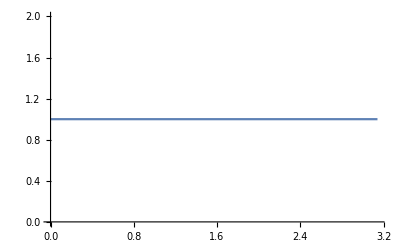

```mathematica
Plot[((F100Florent/(F1002Jψ/16/64/π/s^2))/.{M->3.1, s->1000}),{θ,0,π},PlotRange->{0,2}]
```

Check ok!

Introduce α = 2M/s^(1/2) < 1,  rewrite Cos[n α] in powers of Cos^n[α]:

```mathematica
F1002Jψα=FullSimplify[F1002Jψ/.{M->α Sqrt[s]/2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π}];
F1102Jψα=FullSimplify[F1102Jψ/.{M->α Sqrt[s]/2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π}];
F1012Jψα=FullSimplify[F1012Jψ/.{M->α Sqrt[s]/2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π}];
F1112Jψα=FullSimplify[F1112Jψ/.{M->α Sqrt[s]/2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π}];
```

```mathematica
F202Jψα=FullSimplify[F202Jψ/.{M->α Sqrt[s]/2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π}];
F212Jψα=FullSimplify[F212Jψ/.{M->α Sqrt[s]/2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π}];
```

```mathematica
F3002Jψaα=FullSimplify[ExpToTrig[F3002Jψa]/.{M->α Sqrt[s]/2,Sin[θ]^2->1-cθ^2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π,0<ϕ<2 π}];
F3102Jψaα=FullSimplify[ExpToTrig[F3102Jψa]/.{M->α Sqrt[s]/2,Sin[θ]^2->1-cθ^2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π,0<ϕ<2 π}];
F3012Jψaα=FullSimplify[ExpToTrig[F3012Jψa]/.{M->α Sqrt[s]/2,Sin[θ]^2->1-cθ^2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π,0<ϕ<2 π}];
F3112Jψaα=FullSimplify[ExpToTrig[F3112Jψa]/.{M->α Sqrt[s]/2,Sin[θ]^2->1-cθ^2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π,0<ϕ<2 π}];
```

```mathematica
F3002Jψbα=FullSimplify[ExpToTrig[F3002Jψb]/.{M->α Sqrt[s]/2,Sin[θ]^2->1-cθ^2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π,0<ϕ<2 π}];
F3102Jψbα=FullSimplify[ExpToTrig[F3102Jψb]/.{M->α Sqrt[s]/2,Sin[θ]^2->1-cθ^2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π,0<ϕ<2 π}];
F3012Jψbα=FullSimplify[ExpToTrig[F3012Jψb]/.{M->α Sqrt[s]/2,Sin[θ]^2->1-cθ^2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π,0<ϕ<2 π}];
F3112Jψbα=FullSimplify[ExpToTrig[F3112Jψb]/.{M->α Sqrt[s]/2,Sin[θ]^2->1-cθ^2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π,0<ϕ<2 π}];
```

```mathematica
F402Jψα=FullSimplify[ExpToTrig[F402Jψ]/.{M->α Sqrt[s]/2,Sin[θ]^2->1-cθ^2,Sin[θ]^4->(1-cθ^2)^2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π,0<ϕ<2 π}];
F412Jψα=FullSimplify[ExpToTrig[F412Jψ]/.{M->α Sqrt[s]/2,Sin[θ]^2->1-cθ^2,Sin[θ]^4->(1-cθ^2)^2,Cos[θ]->cθ,Cos[2 θ]->2 cθ^2-1,Cos[4 θ]->8 cθ^4-8 cθ^2+1,Cos[6 θ]->2 (4 cθ^3-3 cθ)^2-1,Cos[8 θ]->2 (8 cθ^4-8 cθ^2+1)^2-1,Cos[10 θ]->(2 (2 cθ (2 cθ^2-1)^2-cθ-4 cθ (1-cθ^2) (2 cθ^2-1))^2-1),Cos[12 θ]->2 (2 (4 cθ^3-3 cθ)^2-1)^2-1},{s>0,α<1,0<θ<π,0<ϕ<2 π}];
```

```mathematica
DumpSave["~/Bureau/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070715_helicity_amplitudes",{F1002Jψα,F1102Jψα,F1012Jψα,F1112Jψα,F202Jψα,F212Jψα,F3002Jψaα,F3102Jψaα,F3012Jψaα,F3112Jψaα,F3002Jψbα,F3102Jψbα,F3012Jψbα,F3112Jψbα,F402Jψα,F412Jψα}];
```

Polarized J/ψ’s F factors : helicity polarizations in Collins-Soper frame (of the pair ?) ONLY THE NECESSARY ONES FOR UNPOLARISED HADRONS CROSS-SECTION

```mathematica
Simp[x_]:=FullSimplify[Simplify[x/.Replλ/.{Mψ->M,MB->M}],assump];
```

```mathematica
F1002Jψpol={{Sum[Amp2Jψf[[i,j,1,1]] Amp2Jψfcc[[i,j,1,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,1,2]] Amp2Jψfcc[[i,j,1,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,1,3]] Amp2Jψfcc[[i,j,1,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,j,2,1]] Amp2Jψfcc[[i,j,2,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,2,2]] Amp2Jψfcc[[i,j,2,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,2,3]] Amp2Jψfcc[[i,j,2,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,j,3,1]] Amp2Jψfcc[[i,j,3,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,3,2]] Amp2Jψfcc[[i,j,3,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,3,3]] Amp2Jψfcc[[i,j,3,3]],{i,1,2},{j,1,2}]}};
```

```mathematica
F202Jψpol={{Sum[Amp2Jψf[[i,i,1,1]] Amp2Jψfcc[[Inv[i],Inv[i],1,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,i,1,2]] Amp2Jψfcc[[Inv[i],Inv[i],1,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,i,1,3]] Amp2Jψfcc[[Inv[i],Inv[i],1,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,i,2,1]] Amp2Jψfcc[[Inv[i],Inv[i],2,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,i,2,2]] Amp2Jψfcc[[Inv[i],Inv[i],2,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,i,2,3]] Amp2Jψfcc[[Inv[i],Inv[i],2,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,i,3,1]] Amp2Jψfcc[[Inv[i],Inv[i],3,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,i,3,2]] Amp2Jψfcc[[Inv[i],Inv[i],3,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,i,3,3]] Amp2Jψfcc[[Inv[i],Inv[i],3,3]],{i,1,2},{j,1,2}]}};
```

```mathematica
F3002Jψapol={{Sum[Amp2Jψf[[i,j,1,1]] Amp2Jψfcc[[Inv[i],j,1,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,1,2]] Amp2Jψfcc[[Inv[i],j,1,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,1,3]] Amp2Jψfcc[[Inv[i],j,1,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,j,2,1]] Amp2Jψfcc[[Inv[i],j,2,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,2,2]] Amp2Jψfcc[[Inv[i],j,2,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,2,3]] Amp2Jψfcc[[Inv[i],j,2,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,j,3,1]] Amp2Jψfcc[[Inv[i],j,3,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,3,2]] Amp2Jψfcc[[Inv[i],j,3,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,3,3]] Amp2Jψfcc[[Inv[i],j,3,3]],{i,1,2},{j,1,2}]}};
```

```mathematica
F3002Jψbpol={{Sum[Amp2Jψf[[i,j,1,1]] Amp2Jψfcc[[i,Inv[j],1,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,1,2]] Amp2Jψfcc[[i,Inv[j],1,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,1,3]] Amp2Jψfcc[[i,Inv[j],1,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,j,2,1]] Amp2Jψfcc[[i,Inv[j],2,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,2,2]] Amp2Jψfcc[[i,Inv[j],2,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,2,3]] Amp2Jψfcc[[i,Inv[j],2,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,j,3,1]] Amp2Jψfcc[[i,Inv[j],3,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,3,2]] Amp2Jψfcc[[i,Inv[j],3,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,3,3]] Amp2Jψfcc[[i,Inv[j],3,3]],{i,1,2},{j,1,2}]}};
```

```mathematica
F402Jψpol={{Sum[Amp2Jψf[[i,Inv[i],1,1]] Amp2Jψfcc[[Inv[i],i,1,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,Inv[i],1,2]] Amp2Jψfcc[[Inv[i],i,1,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,Inv[i],1,3]] Amp2Jψfcc[[Inv[i],i,1,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,Inv[i],2,1]] Amp2Jψfcc[[Inv[i],i,2,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,Inv[i],2,2]] Amp2Jψfcc[[Inv[i],i,2,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,Inv[i],2,3]] Amp2Jψfcc[[Inv[i],i,2,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,Inv[i],3,1]] Amp2Jψfcc[[Inv[i],i,3,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,Inv[i],3,2]] Amp2Jψfcc[[Inv[i],i,3,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,Inv[i],3,3]] Amp2Jψfcc[[Inv[i],i,3,3]],{i,1,2},{j,1,2}]}};
```

```mathematica
F1002Jψpolf=ParallelMap[Simp,F1002Jψpol];
```

```mathematica
F202Jψpolf=ParallelMap[Simp,F202Jψpol];
```

```mathematica
F3002Jψapolf=ParallelMap[Simp,F3002Jψapol];
```

```mathematica
F3002Jψbpolf=ParallelMap[Simp,F3002Jψbpol];
```

```mathematica
F402Jψpolf=ParallelMap[Simp,F402Jψpol];
```

```mathematica
DumpSave["/projet/pth/scarpa/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_helicity_amplitudes_psipol_par",{F1002Jψpolf,F202Jψpolf,F3002Jψapolf,F3002Jψbpolf,F402Jψpolf}];
```

```mathematica
<<"/projet/pth/scarpa/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_helicity_amplitudes_psipol_par"
```

```mathematica
Toα[x_]:=(
y=ExpToTrig[x]/.M->α √s/2;
For[i=1,i<17,i++,y=y/.Sin[i θ]->√(1-(Cos[i θ])^2)/.Cos[i θ]->ChebyshevT[i,cθ]];
y=FullSimplify[y,{s>0,α<1,0<θ<π,0<ϕ<2 π}];
Return[y];
)
```

```mathematica
F1002Jψpolfα=ParallelMap[Toα,F1002Jψpolf];
```

```mathematica
F202Jψpolfα=ParallelMap[Toα,F202Jψpolf];
```

```mathematica
F3002Jψapolfα=ParallelMap[Toα,F3002Jψapolf];
```

```mathematica
F3002Jψbpolfα=ParallelMap[Toα,F3002Jψbpolf];
```

```mathematica
F402Jψpolfα=ParallelMap[Toα,F402Jψpolf];
```

```mathematica
DumpSave["/projet/pth/scarpa/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_helicity_amplitudes_psipol_par_alpha",{F1002Jψpolfα,F202Jψpolfα,F3002Jψapolfα,F3002Jψbpolfα,F402Jψpolfα}];
```

### Using polarisation vectors à la Braaten

```mathematica
ExpRepl[expr_]:=ExpandAll[expr/.ReplMand]
SimRepl[expr_]:=Simplify[expr/.ReplMand]
SimExpRepl[expr_]:=Simplify[ExpandAll[expr/.ReplMand]/.ReplMand]
SimMand[expr_]:=Simplify[expr,{s+t+u==Mψ^2+MB^2}]
SimExpReplMand[expr_]:=Simplify[(ExpandAll[expr/.ReplMand]/.ReplMand),{s+t+u==Mψ^2+MB^2}]
```

Decleration of variables and momenta: ka: momentum of gluon a, kb: momentum of gluon b, qB: momentum of Vector Boson, qψ: momentum of the J/ψ, Mψ.b2=qψ.b2, MB.b2=qB.b2

Polarization vectors for the gluons: Common choice: ϵ(k_a,λ_a)=(0,-λ_a/(√2),-i/(√2),0), ϵ(k_b,λ_b)=(0,+λ_b/(√2),-i/(√2),0)

Polarization vectors for the J/ψ and the gauge boson B:
Check first:

```mathematica
(* Replλ={λ->Sqrt[s^2+MB^4+Mψ^4-2 s Mψ^2-2 s MB^2-2 Mψ^2 MB^2]}; *)
Replλ={λ->√(s (-4 M^2+s))};
Repltu={Cos[θ]->(t-u)/λ,Sin[θ]->Sqrt[λ^2-(t-u)^2]/λ};
```

```mathematica
(* assump={s>MB^2+Mψ^2,u<0,t<0,s>0,MB>0,Mψ>0}; *)
assump={s>2M^2,u<0,t<0,s>0,M>0};

(* texpl=-(s-Mψ^2-MB^2-λ Cos[θ])/2;
uexpl=-(s-Mψ^2-MB^2+λ Cos[θ])/2; *)
texpl=-(s-2M^2-λ Cos[θ])/2;
uexpl=-(s-2M^2+λ Cos[θ])/2;
```

Explicite representation of the particle momenta in the Collins-Soper frame:

```mathematica
kav=Sqrt[s]/2 {1,0,0,1};
kbv=Sqrt[s]/2 {1,0,0,-1};
(* qψv={(s+Mψ^2-MB^2)/2/Sqrt[s],λ/2/Sqrt[s] Sin[θ] Cos[ϕ],λ/2/Sqrt[s] Sin[θ] Sin[ϕ],λ/2/Sqrt[s] Cos[θ]};
qBv={(s+MB^2-Mψ^2)/2/Sqrt[s],-λ/2/Sqrt[s] Sin[θ] Cos[ϕ],-λ/2/Sqrt[s] Sin[θ] Sin[ϕ],-λ/2/Sqrt[s] Cos[θ]}; *)
qψv={Sqrt[s]/2,λ/2/Sqrt[s] Sin[θ] Cos[ϕ],λ/2/Sqrt[s] Sin[θ] Sin[ϕ],λ/2/Sqrt[s] Cos[θ]};
qBv={Sqrt[s]/2,-λ/2/Sqrt[s] Sin[θ] Cos[ϕ],-λ/2/Sqrt[s] Sin[θ] Sin[ϕ],-λ/2/Sqrt[s] Cos[θ]};
```

```mathematica
GT={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
```

```mathematica
GTT=ConstantArray[0,{4,4}];
LCT=ConstantArray[0,{4,4,4,4}];
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
GTT[[i,j]]=GT[[i,j]]-2/s (kav[[i]] kbv[[j]]+kav[[j]] kbv[[i]]);
For[k=1,k≤4,k++,
For[l=1,l≤4,l++,
LCT[[i,j,k,l]]=(LeviCivitaTensor[4]//Normal)[[i,j,k,l]];]]]]
```

```mathematica
Simplify[{qBv.GT.qBv,qψv.GT.qψv,qBv.GT.qψv,qψv.GT.qBv}/.Replλ]
```

{M^2,M^2,1/2 (-2 M^2+s),1/2 (-2 M^2+s)}

Polarization vectors of the J/ψ and vector boson in the Collins-Soper frame:

```mathematica
XCStv=kav/(kav.GT.(qψv+qBv))-kbv/(kbv.GT.(qψv+qBv))//FullSimplify
```

{0,0,0,2/(√s)}

```mathematica
ProjψCStv=-XCStv+(qψv.GT.XCStv)/(qψv.GT.qψv)qψv/.Replλ//FullSimplify
```

{-(√(s (-4 M^2+s)) Cos[θ])/(2 M^2 √s),-((-4 M^2+s) Cos[θ] Cos[ϕ] Sin[θ])/(2 M^2 √s),-((-4 M^2+s) Sin[2 θ] Sin[ϕ])/(4 M^2 √s),-(4 M^2+s+(-4 M^2+s) Cos[2 θ])/(4 M^2 √s)}

```mathematica
ϵLψCStv=ProjψCStv/(√(-ProjψCStv.GT.ProjψCStv))//FullSimplify
```

{-(√(s (-4 M^2+s)) Cos[θ])/(√2 M^2 √s √((4 M^2+s+(-4 M^2+s) Cos[2 θ])/(M^2 s))),((4 M^2-s) Cos[ϕ] Sin[2 θ])/(2 √2 M^2 √s √((4 M^2+s+(-4 M^2+s) Cos[2 θ])/(M^2 s))),((4 M^2-s) Sin[2 θ] Sin[ϕ])/(2 √2 M^2 √s √((4 M^2+s+(-4 M^2+s) Cos[2 θ])/(M^2 s))),-(√s √((4 M^2+s+(-4 M^2+s) Cos[2 θ])/(M^2 s)))/(2 √2)}

```mathematica
ProjBCStv=-XCStv+(qBv.GT.XCStv)/(qBv.GT.qBv)qBv/.Replλ//FullSimplify
```

{(√(s (-4 M^2+s)) Cos[θ])/(2 M^2 √s),-((-4 M^2+s) Cos[θ] Cos[ϕ] Sin[θ])/(2 M^2 √s),-((-4 M^2+s) Sin[2 θ] Sin[ϕ])/(4 M^2 √s),-(4 M^2+s+(-4 M^2+s) Cos[2 θ])/(4 M^2 √s)}

```mathematica
ϵLBCStv=ProjBCStv/(√(-ProjBCStv.GT.ProjBCStv))//FullSimplify
```

{(√(s (-4 M^2+s)) Cos[θ])/(√2 M^2 √s √((4 M^2+s+(-4 M^2+s) Cos[2 θ])/(M^2 s))),((4 M^2-s) Cos[ϕ] Sin[2 θ])/(2 √2 M^2 √s √((4 M^2+s+(-4 M^2+s) Cos[2 θ])/(M^2 s))),((4 M^2-s) Sin[2 θ] Sin[ϕ])/(2 √2 M^2 √s √((4 M^2+s+(-4 M^2+s) Cos[2 θ])/(M^2 s))),-(√s √((4 M^2+s+(-4 M^2+s) Cos[2 θ])/(M^2 s)))/(2 √2)}

Sum over a massive particle polarizations : (Σ(ϵ^*))^μ ϵ^ν= -g^μν+(q^μ q^ν)/M^2

```mathematica
SumPolJpsi[μ_,ν_,q_]:=-{μ}.{ν}+(q.{μ}q.{ν})/M^2;
```

```mathematica
PolSumψ1=ConstantArray[0,{4,4}];
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
PolSumψ1[[i,j]]=FullSimplify[GT[[i,j]]-qψv[[i]] qψv[[j]]/M^2];]]
```

```mathematica
PolSumψ1
```

{{1-s/(4 M^2),-(λ Cos[ϕ] Sin[θ])/(4 M^2),-(λ Sin[θ] Sin[ϕ])/(4 M^2),-(λ Cos[θ])/(4 M^2)},{-(λ Cos[ϕ] Sin[θ])/(4 M^2),-1-(λ^2 Cos[ϕ]^2 Sin[θ]^2)/(4 M^2 s),-(λ^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(4 M^2 s),-(λ^2 Cos[θ] Cos[ϕ] Sin[θ])/(4 M^2 s)},{-(λ Sin[θ] Sin[ϕ])/(4 M^2),-(λ^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(4 M^2 s),-1-(λ^2 Sin[θ]^2 Sin[ϕ]^2)/(4 M^2 s),-(λ^2 Cos[θ] Sin[θ] Sin[ϕ])/(4 M^2 s)},{-(λ Cos[θ])/(4 M^2),-(λ^2 Cos[θ] Cos[ϕ] Sin[θ])/(4 M^2 s),-(λ^2 Cos[θ] Sin[θ] Sin[ϕ])/(4 M^2 s),-1-(λ^2 Cos[θ]^2)/(4 M^2 s)}}

```mathematica
PolSumB1=ConstantArray[0,{4,4}];
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
PolSumB1[[i,j]]=FullSimplify[GT[[i,j]]-qBv[[i]] qBv[[j]]/M^2];]]
```

```mathematica
PolSumB1
```

{{1-s/(4 M^2),(λ Cos[ϕ] Sin[θ])/(4 M^2),(λ Sin[θ] Sin[ϕ])/(4 M^2),(λ Cos[θ])/(4 M^2)},{(λ Cos[ϕ] Sin[θ])/(4 M^2),-1-(λ^2 Cos[ϕ]^2 Sin[θ]^2)/(4 M^2 s),-(λ^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(4 M^2 s),-(λ^2 Cos[θ] Cos[ϕ] Sin[θ])/(4 M^2 s)},{(λ Sin[θ] Sin[ϕ])/(4 M^2),-(λ^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(4 M^2 s),-1-(λ^2 Sin[θ]^2 Sin[ϕ]^2)/(4 M^2 s),-(λ^2 Cos[θ] Sin[θ] Sin[ϕ])/(4 M^2 s)},{(λ Cos[θ])/(4 M^2),-(λ^2 Cos[θ] Cos[ϕ] Sin[θ])/(4 M^2 s),-(λ^2 Cos[θ] Sin[θ] Sin[ϕ])/(4 M^2 s),-1-(λ^2 Cos[θ]^2)/(4 M^2 s)}}

```mathematica
testReplace=_
```

```mathematica
S[kav,{μ}]S[kbv,{ν}] test[μ,ν]
```

g_{μ Sqrt[s]
-------
   2} g_{ν Sqrt[s]
-------
   2} test[μ,ν]

```mathematica
kav.PolSumB1.kbv
```

1/2 √s (1/2 √s (1-s/(4 M^2))+(√s λ Cos[θ])/(8 M^2))-1/2 √s ((√s λ Cos[θ])/(8 M^2)+1/2 √s (-1-(λ^2 Cos[θ]^2)/(4 M^2 s)))

Definition of the polarization vectors of the gluons :

```mathematica
ϵav[λa_]:={0,-λa/Sqrt[2],-ⅈ/Sqrt[2],0}
ϵbv[λb_]:={0,λb/Sqrt[2],-ⅈ/Sqrt[2],0}

ϵavcc[λacc_]:={0,-λacc/Sqrt[2],ⅈ/Sqrt[2],0}
ϵbvcc[λbcc_]:={0,λbcc/Sqrt[2],ⅈ/Sqrt[2],0}
```

Scalar products and contractions :

```mathematica
ReplMand={S[ka,ka]->FullSimplify[kav.GT.kav],
S[kb,kb]->FullSimplify[kbv.GT.kbv],
S[qB,qB]->FullSimplify[(qBv.GT.qBv)/.Replλ],
S[qψ,qψ]->FullSimplify[(qψv.GT.qψv)/.Replλ],
S[ka,kb]->FullSimplify[kav.GT.kbv],
S[ka,qB]->FullSimplify[kav.GT.qBv],
S[ka,qψ]->FullSimplify[kav.GT.qψv],
S[kb,qB]->FullSimplify[kbv.GT.qBv],
S[kb,qψ]->FullSimplify[kbv.GT.qψv],
S[qB,qψ]->FullSimplify[(qBv.GT.qψv)/.Replλ],
Tracer`Private`eps[{ka, kb,qB,qψ}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.kbv)[[j]] (GT.qBv)[[k]] (GT.qψv)[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]]};
```

```mathematica
ReplSPAmp2[λa_,λb_]:=
{S[ka, ϵaA]->FullSimplify[kav.GT.ϵav[λa]],
S[ka, ϵbA]->FullSimplify[kav.GT.ϵbv[λb]],
S[kb, ϵaA]->FullSimplify[kbv.GT.ϵav[λa]],
S[kb, ϵbA]->FullSimplify[kbv.GT.ϵbv[λb]],
S[qψ, ϵaA]->FullSimplify[qψv.GT.ϵav[λa]],
S[qψ, ϵbA]->FullSimplify[qψv.GT.ϵbv[λb]],
S[qB, ϵaA]->FullSimplify[qBv.GT.ϵav[λa]],
S[qB, ϵbA]->FullSimplify[qBv.GT.ϵbv[λb]],
S[ϵaA, ϵbA]->FullSimplify[ϵav[λa].GT.ϵbv[λb]], 
 Tracer`Private`eps[{ka, kb, ϵaA, ϵbA}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.kbv)[[j]] (GT.ϵav[λa])[[k]] (GT.ϵbv[λb])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]]}
```

```mathematica
ReplSPAmpcc2[λacc_,λbcc_]:={
S[ka, ϵaAcc]->FullSimplify[kav.GT.ϵavcc[λacc]],
S[ka, ϵbAcc]->FullSimplify[kav.GT.ϵbvcc[λbcc]],
S[kb, ϵaAcc]->FullSimplify[kbv.GT.ϵavcc[λacc]],
S[kb, ϵbAcc]->FullSimplify[kbv.GT.ϵbvcc[λbcc]],
S[qψ, ϵaAcc]->FullSimplify[qψv.GT.ϵavcc[λacc]],
S[qψ, ϵbAcc]->FullSimplify[qψv.GT.ϵbvcc[λbcc]],
S[qB, ϵaAcc]->FullSimplify[qBv.GT.ϵavcc[λacc]],
S[qB, ϵbAcc]->FullSimplify[qBv.GT.ϵbvcc[λbcc]],
S[ϵaAcc, ϵbAcc]->FullSimplify[ϵavcc[λacc].GT.ϵbvcc[λbcc]],
Tracer`Private`eps[{ka, kb, ϵaAcc, ϵbAcc}]->FullSimplify[Sum[LCT[[i,j,k,l]] (GT.kav)[[i]] (GT.kbv)[[j]] (GT.ϵavcc[λacc])[[k]] (GT.ϵbvcc[λbcc])[[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]]}
```

```mathematica
ReplSPAmpMix[λa_,λb_,λacc_,λbcc_]:=
{S[ϵaA, ϵaAcc]->FullSimplify[ϵav[λa].GT.ϵavcc[λacc]],
S[ϵaA, ϵbAcc]->FullSimplify[ϵav[λa].GT.ϵbvcc[λbcc]],
S[ϵbA, ϵaAcc]->FullSimplify[ϵbv[λb].GT.ϵavcc[λacc]],
S[ϵbA, ϵbAcc]->FullSimplify[ϵbv[λb].GT.ϵbvcc[λbcc]]}
```

```mathematica
RepPOLCSt[λa_,λb_]:={
S[ϵLψCSt, ϵLψCSt]->FullSimplify[ϵLψCStv.GT.ϵLψCStv],
S[ϵLψCSt, ka]->FullSimplify[ϵLψCStv.GT.kav],
S[ϵLψCSt, kb]->FullSimplify[ϵLψCStv.GT.kbv],
S[ϵLψCSt, qψ]->FullSimplify[ϵLψCStv.GT.qψv],
S[ϵLψCSt, qB]-> FullSimplify[ϵLψCStv.GT.qBv],
S[ϵLψCSt, ϵaA]->FullSimplify[ϵLψCStv.GT.ϵav[λa]],
S[ϵLψCSt, ϵbA]->FullSimplify[ϵLψCStv.GT.ϵbv[λb]],

S[ϵLBCSt, ϵLBCSt]->FullSimplify[ϵLBCStv.GT.ϵLBCStv],
S[ϵLBCSt, ka]->FullSimplify[ϵLBCStv.GT.kav],
S[ϵLBCSt, kb]->FullSimplify[ϵLBCStv.GT.kbv],
S[ϵLBCSt, qψ]->FullSimplify[ϵLBCStv.GT.qψv],
S[ϵLBCSt, qB]-> FullSimplify[ϵLBCStv.GT.qBv],
S[ϵLBCSt, ϵaA]->FullSimplify[ϵLBCStv.GT.ϵav[λa]],
S[ϵLBCSt, ϵbA]->FullSimplify[ϵLBCStv.GT.ϵbv[λb]],

S[ϵLψCSt, ϵLBCSt]->FullSimplify[ϵLψCStv.GT.ϵLBCStv]
}

RepPOLCStcc[λacc_,λbcc_]:={
S[ϵLψCSt, ϵLψCSt]->FullSimplify[ϵLψCStv.GT.ϵLψCStv],
S[ϵLψCSt, ka]->FullSimplify[ϵLψCStv.GT.kav],
S[ϵLψCSt, kb]->FullSimplify[ϵLψCStv.GT.kbv],
S[ϵLψCSt, qψ]->FullSimplify[ϵLψCStv.GT.qψv],
S[ϵLψCSt, qB]-> FullSimplify[ϵLψCStv.GT.qBv],
S[ϵLψCSt, ϵaAcc]->FullSimplify[ϵLψCStv.GT.ϵavcc[λacc]],
S[ϵLψCSt, ϵbAcc]->FullSimplify[ϵLψCStv.GT.ϵbvcc[λbcc]],

S[ϵLBCSt, ϵLBCSt]->FullSimplify[ϵLBCStv.GT.ϵLBCStv],
S[ϵLBCSt, ka]->FullSimplify[ϵLBCStv.GT.kav],
S[ϵLBCSt, kb]->FullSimplify[ϵLBCStv.GT.kbv],
S[ϵLBCSt, qψ]->FullSimplify[ϵLBCStv.GT.qψv],
S[ϵLBCSt, qB]-> FullSimplify[ϵLBCStv.GT.qBv],
S[ϵLBCSt, ϵaAcc]->FullSimplify[ϵLBCStv.GT.ϵavcc[λacc]],
S[ϵLBCSt, ϵbAcc]->FullSimplify[ϵLBCStv.GT.ϵbvcc[λbcc]],

S[ϵLψCSt, ϵLBCSt]->FullSimplify[ϵLψCStv.GT.ϵLBCStv]
}
```

```mathematica
ScalarProductsList[λa_,λb_,λacc_,λbcc_]:=MatrixForm[Simplify[{
{"ka.ka",S[ka,ka]},
{"kb.kb",S[kb,kb]},
{"qB.qB",S[qB,qB]},
{"qψ.qψ",S[qψ,qψ]},
{"ka.kb",S[ka,kb]},
{"ka.qB",S[ka,qB]},
{"ka.qψ",S[ka,qψ]},
{"kb.qB",S[kb,qB]},
{"kb.qψ",S[kb,qψ]},
{"qB.qψ",S[qB,qψ]},
{"ka.ϵaA",S[ka, ϵaA]},
{"ka.ϵbA",S[ka, ϵbA]},
{"kb.ϵaA",S[kb, ϵaA]},
{"kb.ϵbA",S[kb, ϵbA]},
{"qψ.ϵaA",S[qψ, ϵaA]},
{"qψ.ϵbA",S[qψ, ϵbA]},
{"qB.ϵaA",S[qB, ϵaA]},
{"qB.ϵbA",S[qB, ϵbA]},
{"ka.ϵaAcc",S[ka, ϵaAcc]},
{"ka.ϵbAcc",S[ka, ϵbAcc]},
{"kb.ϵaAcc",S[kb, ϵaAcc]},
{"kb.ϵbAcc",S[kb, ϵbAcc]},
{"qψ.ϵaAcc",S[qψ, ϵaAcc]},
{"qψ.ϵbAcc",S[qψ, ϵbAcc]},
{"qB.ϵaAcc",S[qB, ϵaAcc]},
{"qB.ϵbAcc",S[qB, ϵbAcc]},
{"ϵaAcc.ϵbAcc",S[ϵaAcc, ϵbAcc]},
{"ϵaA.ϵbA",S[ϵaA, ϵbA]},
{"ϵaA.ϵaAcc",S[ϵaA, ϵaAcc]},
{"ϵaA.ϵbAcc",S[ϵaA, ϵbAcc]},
{"ϵbA.ϵaAcc",S[ϵbA, ϵaAcc]},
{"ϵbA.ϵbAcc",S[ϵbA, ϵbAcc]}
}/.ReplMand/.ReplSPAmp2[λa,λb]/.ReplSPAmpcc2[λacc,λbcc]/.ReplSPAmpMix[λa,λb,λacc,λbcc]/.Replλ,assump]]
```

```mathematica
ScalarProductsList[-1,-1,-1,-1]
```

(ka.ka | 0
kb.kb | 0
qB.qB | M^2
qψ.qψ | M^2
ka.kb | s/2
ka.qB | 1/4 (s+√(s (-4 M^2+s)) Cos[θ])
ka.qψ | 1/4 (s-√(s (-4 M^2+s)) Cos[θ])
kb.qB | 1/4 (s-√(s (-4 M^2+s)) Cos[θ])
kb.qψ | 1/4 (s+√(s (-4 M^2+s)) Cos[θ])
qB.qψ | 1/2 (-2 M^2+s)
ka.ϵaA | 0
ka.ϵbA | 0
kb.ϵaA | 0
kb.ϵbA | 0
qψ.ϵaA | -(ⅇ^(-ⅈ ϕ) √(-4 M^2+s) Sin[θ])/(2 √2)
qψ.ϵbA | (ⅇ^(ⅈ ϕ) √(-4 M^2+s) Sin[θ])/(2 √2)
qB.ϵaA | (ⅇ^(-ⅈ ϕ) √(-4 M^2+s) Sin[θ])/(2 √2)
qB.ϵbA | -(ⅇ^(ⅈ ϕ) √(-4 M^2+s) Sin[θ])/(2 √2)
ka.ϵaAcc | 0
ka.ϵbAcc | 0
kb.ϵaAcc | 0
kb.ϵbAcc | 0
qψ.ϵaAcc | -(ⅇ^(ⅈ ϕ) √(-4 M^2+s) Sin[θ])/(2 √2)
qψ.ϵbAcc | (ⅇ^(-ⅈ ϕ) √(-4 M^2+s) Sin[θ])/(2 √2)
qB.ϵaAcc | (ⅇ^(ⅈ ϕ) √(-4 M^2+s) Sin[θ])/(2 √2)
qB.ϵbAcc | -(ⅇ^(-ⅈ ϕ) √(-4 M^2+s) Sin[θ])/(2 √2)
ϵaAcc.ϵbAcc | 1
ϵaA.ϵbA | 1
ϵaA.ϵaAcc | -1
ϵaA.ϵbAcc | 0
ϵbA.ϵaAcc | -1
ϵbA.ϵbAcc | -1)

```mathematica
ScalarProductsList[1,1,1,1][[1,All,2]]-ScalarProductsList[-1,-1,-1,-1][[1,All,2]]//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(-4 M^2+s) Sin[θ])/(2 √2),-(ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(-4 M^2+s) Sin[θ])/(2 √2),-(ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(-4 M^2+s) Sin[θ])/(2 √2),(ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(-4 M^2+s) Sin[θ])/(2 √2),0,0,0,0,(ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(-4 M^2+s) Sin[θ])/(2 √2),-(ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(-4 M^2+s) Sin[θ])/(2 √2),-(ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(-4 M^2+s) Sin[θ])/(2 √2),(ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(-4 M^2+s) Sin[θ])/(2 √2),0,0,0,0,0,0}

Amplitude for gg ⟶ J/ψ + J/ψ without polarization vectors : (NO IMAGINARY PART => M*=M)

```mathematica
(* k1,k2 are gluons ; q1,q2 are J/ψ mesons (q2=k1+k2-q1 so it doesn't appear) ; μ[q1=qψ],⋁[q2=qB] are indices of J/ψ mesons ; ρ[k1=ka],σ[k2=kb] are indices of gluons s=(k1+k2)^2, t=(k1-q1)^2, u=(k2-q1)^2 , M: mass of JPsi *) 

Amplitude[μ_,ν_,ρ_,σ_]:=1/(9 M (M^2-u)^2 (-2 M^2+t+u)^3)64 π R0^2 αs^2 (-36 (M^2-u) ((k1.{μ}+k2.{μ}-q1.{μ}) ((k1.{ρ}+k2.{ρ}) q1.{ν} ((M^2-u) k1.{σ}+(M^2-u) k2.{σ}+2 (-M^2+t) q1.{σ})+k2.{ν} ((M^2-u) (k1.{ρ}+k2.{ρ}-q1.{ρ}) q1.{σ}+q1.{ρ} ((-M^2+u) (k1.{σ}+k2.{σ}-q1.{σ})+2 (M^2-t) q1.{σ})))+k2.{μ} (2 (M^2-t) k2.{ν} (k1.{σ} q1.{ρ}+k2.{σ} q1.{ρ}-(k1.{ρ}+k2.{ρ}) q1.{σ})+q1.{ν} (-(M^2-2 t+u) q1.{ρ} (k1.{σ}+k2.{σ}-q1.{σ})+(k1.{ρ}+k2.{ρ}-q1.{ρ}) (2 (-M^2+t) (k1.{σ}+k2.{σ}-q1.{σ})+(M^2-2 t+u) q1.{σ}))))+((M^2-u) q1.{ρ} ((-7 M^4-36 t u+M^2 (4 t+39 u)) (k1.{σ}+k2.{σ}-q1.{σ})+2 M^2 (16 M^2-17 t+u) q1.{σ})+(k1.{ρ}+k2.{ρ}-q1.{ρ}) (2 M^2 (M^2-u) (16 M^2-17 t+u) (k1.{σ}+k2.{σ}-q1.{σ})+(63 M^6+36 t (t-2 u) u-2 M^4 (14 t+67 u)+M^2 (-38 t^2+104 t u+69 u^2)) q1.{σ})) {μ}.{ν}-(q1.{ν} (-(M^2-u) (39 M^4+36 t u-M^2 (38 t+37 u)) (k1.{σ}+k2.{σ}-q1.{σ})+(5 M^6+36 t u (-t+u)+M^4 (-42 t+32 u)+M^2 (38 t^2+2 t u-35 u^2)) q1.{σ})+2 k2.{ν} (M^2 (25 M^2-17 t-8 u) (M^2-u) (k1.{σ}+k2.{σ}-q1.{σ})+(3 M^6+M^4 (23 t-11 u)+18 t^2 u+M^2 (-19 t^2-21 t u+7 u^2)) q1.{σ})) {μ}.{ρ}+(-(45 M^6-36 t u^2-14 M^4 (2 t+7 u)+M^2 (-2 t^2+68 t u+51 u^2)) (k1.{ρ}+k2.{ρ}) q1.{ν}+2 k2.{ν} (M^2 (7 M^2+t-8 u) (M^2-u) (k1.{ρ}+k2.{ρ}-q1.{ρ})+(21 M^6-18 t u^2-M^4 (13 t+47 u)+M^2 (-t^2+33 t u+25 u^2)) q1.{ρ})) {μ}.{σ}-(2 k2.{μ} ((21 M^6-18 t u^2-M^4 (13 t+47 u)+M^2 (-t^2+33 t u+25 u^2)) (k1.{σ}+k2.{σ}-q1.{σ})+M^2 (7 M^2+t-8 u) (M^2-u) q1.{σ})+(k1.{μ}+k2.{μ}-q1.{μ}) (M^2 (M^2-u) (3 M^2-2 t-u) (k1.{σ}+k2.{σ}-q1.{σ})+(31 M^6-36 t u^2-2 M^4 (15 t+34 u)+M^2 (-2 t^2+70 t u+35 u^2)) q1.{σ})) {ν}.{ρ}+(M^2-t) (27 M^6-18 t u^2-M^4 (13 t+59 u)+M^2 (-t^2+33 t u+31 u^2)) {μ}.{σ} {ν}.{ρ}+(-(M^2-u) (11 M^4-36 t u+M^2 (4 t+21 u)) (k1.{ρ}+k2.{ρ}) (k1.{μ}+k2.{μ}-q1.{μ})+2 k2.{μ} ((3 M^6+M^4 (23 t-11 u)+18 t^2 u+M^2 (-19 t^2-21 t u+7 u^2)) (k1.{ρ}+k2.{ρ}-q1.{ρ})+M^2 (25 M^2-17 t-8 u) (M^2-u) q1.{ρ})) {ν}.{σ}+(M^2-t) (M^2-u) (29 M^4+M^2 (2 t-13 u)-18 t u) {μ}.{ρ} {ν}.{σ}-(-(M^2-u) (11 M^4-36 t u+M^2 (4 t+21 u)) k2.{ν} (k1.{μ}+k2.{μ}-q1.{μ})+k2.{μ} (2 (28 M^6+M^4 (6 t-62 u)+18 t (t-u) u+M^2 (-19 t^2+14 t u+33 u^2)) k2.{ν}-(45 M^6+2 M^4 (4 t-67 u)+36 t (t-2 u) u+M^2 (-38 t^2+68 t u+87 u^2)) q1.{ν})) {ρ}.{σ}-2 (M^2-t) (M^2-u) (15 M^4+M^2 (t-16 u)+9 u (-t+u)) {μ}.{ν} {ρ}.{σ});

Amplitot[μ_,ν_,ρ_,σ_]:=Amplitude[μ,ν,ρ,σ]+(Amplitude[μ,ν,ρ,σ]/.{μ->ν,ν->μ,t->u,u->t,q1->q2,q2->q1});
```

Rewrite in terms of Marc’s notations:

```mathematica
AmpliMarc[μ_,ν_,ρ_,σ_]:=Amplitot[μ,ν,ρ,σ]/.{q1->qψ,q2->qB,k1->ka,k2->kb}/.{t->texpl,u->uexpl}
```

Amplitudes contracted with different final-state polarizations :

```mathematica
AmpliSqUU=(ExpandAll[AmpliMarc[μ,ν,ρ,σ]AmpliMarc[α,β,γ,δ]S[ϵaA,{ρ}] S[ϵbA,{σ}]S[ϵaAcc,{γ}] S[ϵbAcc,{δ}]SumPolJpsi[μ,α,qψ]SumPolJpsi[ν,β,qB]]);
```

```mathematica
AmpliLLCSt[ρ_,σ_]:=AmpliMarc[μ,ν,ρ,σ]S[ϵLψCSt,{μ}] S[ϵLBCSt,{ν}];
```

UU amplitude : we compute the whole squared amplitude at once in order to use the relation for sum over J/ψ’s polarizations, optimized via parallelization

```mathematica
heli={{-1,-1,-1,-1},{-1,-1,-1,1},{-1,-1,1,-1},{-1,-1,1,1},
{-1,1,-1,-1},{-1,1,-1,1},{-1,1,1,-1},{-1,1,1,1},
{1,-1,-1,-1},{1,-1,-1,1},{1,-1,1,-1},{1,-1,1,1},
{1,1,-1,-1},{1,1,-1,1},{1,1,1,-1},{1,1,1,1}};
```

```mathematica
AmpSq2JψUUfopt=ParallelMap[Simplify[AmpliSqUU/.ReplSPAmp2[#[[1]],#[[2]]]/.ReplSPAmpcc2[#[[3]],#[[4]]]/.ReplSPAmpMix[#[[1]],#[[2]],#[[3]],#[[4]]]/.ReplMand/.Replλ,assump] &,heli];
```

```mathematica
AmpSq2JψUUfopt=ArrayReshape[AmpSq2JψUUfopt,{2,2,2,2}];
```

```mathematica
DumpSave["~/Bureau/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_rawamps_UUnew",AmpSq2JψUUfopt];
```

```mathematica
<<"~/Bureau/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_rawamps_UUnew"
```

```mathematica
DumpSave["/projet/pth/scarpa/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_rawamps_UUnew",AmpSq2JψUUfopt];
```

```mathematica
<<"/projet/pth/scarpa/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_rawamps_UUnew"
```

LL amplitude : ϵLψCSt, ϵLBCSt have no imaginary part, therefore no need to define their complex conjugates

```mathematica
Ampgg22JψLLCSt=(ExpandAll[S[ϵaA,{ρ}] S[ϵbA,{σ}] AmpliLLCSt[ρ,σ]]);
```

```mathematica
Amp2JψLLCSt={{Ampgg22JψLLCSt/.ReplMand/.ReplSPAmp2[-1,-1]/.RepPOLCSt[-1,-1]/.Replλ//Simplify,Ampgg22JψLLCSt/.ReplMand/.ReplSPAmp2[-1,1]/.RepPOLCSt[-1,1]/.Replλ//Simplify},{Ampgg22JψLLCSt/.ReplMand/.ReplSPAmp2[1,-1]/.RepPOLCSt[1,-1]/.Replλ//Simplify,Ampgg22JψLLCSt/.ReplMand/.ReplSPAmp2[1,1]/.RepPOLCSt[1,1]/.Replλ//Simplify}};
```

```mathematica
Ampgg22JψccLLCSt=(ExpandAll[S[ϵaAcc,{ρ}] S[ϵbAcc,{σ}] AmpliLLCSt[ρ,σ]]);
```

```mathematica
Amp2JψccLLCSt={{Ampgg22JψccLLCSt/.ReplMand/.ReplSPAmpcc2[-1,-1]/.RepPOLCStcc[-1,-1]/.Replλ//Simplify,Ampgg22JψccLLCSt/.ReplMand/.ReplSPAmpcc2[-1,1]/.RepPOLCStcc[-1,1]/.Replλ//Simplify},{Ampgg22JψccLLCSt/.ReplMand/.ReplSPAmpcc2[1,-1]/.RepPOLCStcc[1,-1]/.Replλ//Simplify,Ampgg22JψccLLCSt/.ReplMand/.ReplSPAmpcc2[1,1]/.RepPOLCStcc[1,1]/.Replλ//Simplify}};
```

```mathematica
DumpSave["~/Bureau/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_rawamps_LLCSt",{Amp2JψLLCSt,Amp2JψccLLCSt}];
```

```mathematica
<<"~/Bureau/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_rawamps_LLCSt"
```

Symmetries in terms of gluon helicities :
-- = ++
-+ = +- ⅇ^(4ⅈϕ)
(--)* = --
(+-)* = -+
(-+)* = +-
(++)* = ++

```mathematica
Amp2JψLLCSt[[-1,-1]]/Amp2JψLLCSt[[1,1]]
```

1

```mathematica
Amp2JψLLCSt[[-1,1]]/Amp2JψLLCSt[[1,-1]]
```

ⅇ^(4 ⅈ ϕ)

```mathematica
Amp2JψLLCSt[[-1,-1]]/Amp2JψccLLCSt[[-1,-1]]
```

1

```mathematica
Amp2JψLLCSt[[-1,1]]/Amp2JψccLLCSt[[1,-1]]
```

1

```mathematica
Amp2JψLLCSt[[1,-1]]/Amp2JψccLLCSt[[-1,1]]
```

1

```mathematica
Amp2JψLLCSt[[1,1]]/Amp2JψccLLCSt[[1,1]]
```

1

Calculate the F factors for an unpolarized J/ψ pair :

```mathematica
Inv[i_]:=If[i==1,2,If[i==2,1]]
```

```mathematica
F1002JψUUopt=Simplify[Sum[(AmpSq2JψUUfopt[[i,j,i,j]] ),{i,1,2},{j,1,2}],assump];
```

```mathematica
F202JψUUopt=Simplify[Sum[( AmpSq2JψUUfopt[[i,i,Inv[i],Inv[i]]]),{i,1,2}],assump];
```

```mathematica
F3002JψaUUopt=Simplify[Sum[(AmpSq2JψUUfopt[[i,j,Inv[i],j]]),{i,1,2},{j,1,2}],assump];
```

```mathematica
F3002JψbUUopt=Simplify[Sum[( AmpSq2JψUUfopt[[i,j,i,Inv[j]]]),{i,1,2},{j,1,2}],assump];
```

```mathematica
F402JψUUopt=Simplify[Sum[(AmpSq2JψUUfopt[[i,Inv[i],Inv[i],i]]),{i,1,2}],assump];
```

```mathematica
DumpSave["~/Bureau/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_Ffactors_UUnew",{F1002JψUUopt,F202JψUUopt,F3002JψaUUopt,F3002JψbUUopt,F402JψUUopt}];
```

```mathematica
<<"~/Bureau/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_Ffactors_UUnew"
```

Introduce α = 2M/s^(1/2) < 1,  rewrite Cos[n α] in powers of Cos^n[α]:

```mathematica
Toα[x_]:=(
y=ExpToTrig[x]/.M->α √s/2;
For[i=1,i<17,i++,y=y/.Sin[i θ]->√(1-(Cos[i θ])^2)/.Cos[i θ]->ChebyshevT[i,cθ]];
y=FullSimplify[y,{s>0,α<1,0<θ<π,0<ϕ<2 π}];
Return[y];
)
```

```mathematica
F1002JψUUoptα=Toα[F1002JψUUopt];
```

```mathematica
F202JψUUoptα=Toα[F202JψUUopt];
```

```mathematica
F3002JψaUUoptα=Toα[F3002JψaUUopt];
```

```mathematica
F3002JψbUUoptα=Toα[F3002JψbUUopt];
```

```mathematica
F402JψUUoptα=Toα[F402JψUUopt];
```

```mathematica
DumpSave["~/Bureau/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070715_Ffactors_alpha_UUnew",{F1002JψUUoptα,F202JψUUoptα,F3002JψaUUoptα,F3002JψbUUoptα,F402JψUUoptα}];
```

```mathematica
<<"~/Bureau/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070715_Ffactors_alpha_UUnew"
```

Calculate the F factors for a longitudinal-longitudinal polarized J/ψ pair in CSt frame :

```mathematica
Inv[i_]:=If[i==1,2,If[i==2,1]]
```

```mathematica
F1002JψLLCSt=Simplify[Sum[(Amp2JψLLCSt[[i,j]] Amp2JψccLLCSt[[i,j]]),{i,1,2},{j,1,2}],assump];
```

```mathematica
F202JψLLCSt=Simplify[Sum[(Amp2JψLLCSt[[i,i]] Amp2JψccLLCSt[[Inv[i],Inv[i]]]),{i,1,2}],assump];
```

```mathematica
F3002JψaLLCSt=Simplify[Sum[(Amp2JψLLCSt[[i,j]] Amp2JψccLLCSt[[Inv[i],j]]),{i,1,2},{j,1,2}],assump];
```

```mathematica
F3002JψbLLCSt=Simplify[Sum[(Amp2JψLLCSt[[i,j]] Amp2JψccLLCSt[[i,Inv[j]]]),{i,1,2},{j,1,2}],assump];
```

```mathematica
F402JψLLCSt=Simplify[Sum[(Amp2JψLLCSt[[i,Inv[i]]] Amp2JψccLLCSt[[Inv[i],i]]),{i,1,2}],assump];
```

Introduce α = 2M/s^(1/2) < 1,  rewrite Cos[n α] in powers of Cos^n[α]:

```mathematica
Toα[x_]:=(
y=ExpToTrig[x]/.M->α √s/2;
For[i=1,i<17,i++,y=y/.Sin[i θ]->√(1-(Cos[i θ])^2)/.Cos[i θ]->ChebyshevT[i,cθ]];
y=FullSimplify[y,{s>0,α<1,0<θ<π,0<ϕ<2 π}];
Return[y];
)
```

```mathematica
F1002JψLLCStα=Toα[F1002JψLLCSt];
```

```mathematica
F202JψLLCStα=Toα[F202JψLLCSt];
```

```mathematica
F3002JψaLLCStα=Toα[F3002JψaLLCSt];
```

```mathematica
F3002JψbLLCStα=Toα[F3002JψbLLCSt];
```

```mathematica
F402JψLLCStα=Toα[F402JψLLCSt];
```

```mathematica
DumpSave["~/Bureau/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070715_helicity_amplitudes_LLCSt",{F1002JψLLCStα,F202JψLLCStα,F3002JψaLLCStα,F3002JψbLLCStα,F402JψLLCStα}];
```

```mathematica
<<"~/Bureau/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070715_helicity_amplitudes_LLCSt"
```

```mathematica
F1002JψLLCSt
```

(2048 π^2 R0^4 αs^4 (4 M^4 (1280 M^6-2336 M^4 s+352 M^2 s^2+54 s^3+9 (64 M^6-304 M^4 s+76 M^2 s^2-s^3) Cos[2 θ]-2 (-4 M^2+s)^2 (40 M^2+27 s) Cos[4 θ]-576 M^6 Cos[6 θ]+432 M^4 s Cos[6 θ]-108 M^2 s^2 Cos[6 θ]+9 s^3 Cos[6 θ])^2+(-4 M^2+s)^2 (-1216 M^6-640 M^4 s+260 M^2 s^2+2 s^3+(-576 M^6-976 M^4 s+244 M^2 s^2+9 s^3) Cos[2 θ]+2 (38 M^2-s) (-4 M^2+s)^2 Cos[4 θ]+576 M^6 Cos[6 θ]-432 M^4 s Cos[6 θ]+108 M^2 s^2 Cos[6 θ]-9 s^3 Cos[6 θ])^2 Sin[θ]^4))/(81 M^2 s^4 (4 M^2+s+(4 M^2-s) Cos[2 θ])^4 (4 M^2+s+(-4 M^2+s) Cos[2 θ])^2)

```mathematica
F1002JψLLCStα
```

(8192 π^2 R0^4 (1296 cθ^16 (-1+α^2)^8-72 cθ^14 (-1+α^2)^7 (-88+71 α^2)+α^8 (5-6 α^2+2 α^4)+cθ^12 (-1+α^2)^6 (12640-21424 α^2+7813 α^4)-8 cθ^10 (-1+α^2)^5 (-1640+4412 α^2-3525 α^4+671 α^6)-2 cθ^2 (-1+α) α^4 (1+α) (-16+141 α^2-160 α^4+51 α^6+2 α^8)+cθ^8 (-1+α^2)^4 (7440-28464 α^2+38322 α^4-16030 α^6+1267 α^8)+2 cθ^6 (-1+α^2)^3 (1088-5588 α^2+11664 α^4-8047 α^6+1458 α^8+51 α^10)+cθ^4 (-1+α^2)^2 (256+α^2 (-1696+α^2 (5425+2 α^2 (-2857+986 α^2+3 α^4+α^6))))) αs^4)/(81 s^3 (1+cθ^2 (-1+α^2))^4 (α^3+cθ^2 (α-α^3))^2)

```mathematica
F1002Jψpolfα[[1]]
```

1/(81 s^3 α^2 (1+cθ^2 (-1+α^2))^4)8192 π^2 R0^4 (64+1296 cθ^16 (-1+α)^8 (1+α)^4+2 α^2 (184-15 α^2-6 α^4+α^6)-72 cθ^14 (-1+α)^7 (1+α)^3 (-80+α (36+71 α))+cθ^12 (-1+α)^6 (1+α)^2 (12016+α (-7200+α (-16292+α (8208+7813 α))))-2 cθ^10 (-1+α)^5 (1+α) (-8256+α (2176+α (10784+α (-10926+α (-10117+4 α (1040+671 α))))))+cθ^8 (-1+α)^4 (15792+α (3008+α (-23048+α (11432+α (13520+α (-23224+α (-13874+α (2392+1267 α))))))))-2 cθ^2 (-1+α) (-192+α (800+α (-752+α (-1098+α (-15+α (-325+α (5+α (61+2 α (1+α)))))))))+2 cθ^6 (-1+α)^3 (4672+α (-3536+α (-8788+α (3276+α (-1814+α (-5418+α (2265+α (1965+α (101+51 α)))))))))+cθ^4 (-1+α)^2 (2832+α (-6848+α (-4020+α (6640+α (-115+α (1638+α (3345+2 α (28+α (17+α (2+α))))))))))) αs^4

```mathematica
F1002Jψα/.α->1
```

(6447104 π^2 R0^4 αs^4)/(81 s^3)

```mathematica
fact=4*2^11*3^-4 π^2 R0^4 αs^4
```

8192/81 π^2 R0^4 αs^4

```mathematica
F1002JψUUoptα/fact/.α->1
```

787/s^3

```mathematica
F1002Jψα/fact/.α->1
```

787/s^3

```mathematica
F1002JψUUoptα/F1002Jψα
```

1

```mathematica
F202JψUUoptα/F202Jψα
```

2

```mathematica
F3002JψaUUoptα/F3002Jψaα
```

1

```mathematica
F3002JψbUUoptα/F3002Jψbα
```

1

```mathematica
F402JψUUoptα/F402Jψα
```

2

```mathematica
F1002JψUUopt/F1002Jψ
```

1

```mathematica
F202JψUUopt/F202Jψ
```

2

```mathematica
F3002JψaUUopt/F3002Jψa
```

1

```mathematica
F3002JψbUUopt/F3002Jψb
```

1

```mathematica
F402JψUUopt/F402Jψ
```

2

```mathematica
AmpSq2JψUUfopt[[1,1,2,2]]
```

1/(27 s^4 (4 M^2+s+(4 M^2-s) Cos[2 θ])^4)8192 M^2 π^2 R0^4 αs^4 (820992 M^8-245504 M^6 s+11872 M^4 s^2+432 M^2 s^3-189 s^4+8 (162944 M^8-54944 M^6 s+3048 M^4 s^2+18 M^2 s^3+27 s^4) Cos[2 θ]+4 (-4 M^2+s)^2 (9952 M^4+432 M^2 s+27 s^2) Cos[4 θ]+175104 M^8 Cos[6 θ]-117504 M^6 s Cos[6 θ]+22464 M^4 s^2 Cos[6 θ]-144 M^2 s^3 Cos[6 θ]-216 s^4 Cos[6 θ]+20736 M^8 Cos[8 θ]-20736 M^6 s Cos[8 θ]+7776 M^4 s^2 Cos[8 θ]-1296 M^2 s^3 Cos[8 θ]+81 s^4 Cos[8 θ])

```mathematica
Simplify[Sum[(Amp2Jψ[[1,2,k,l]]Amp2Jψcc[[1,2,k,l]]/.Replλ),{k,1,3},{l,1,3}],assump]
```

```mathematica
%//FullSimplify
```

Polarized J/ψ’s F factors : helicity polarizations in Collins-Soper frame (of the pair ?) ONLY THE NECESSARY ONES FOR UNPOLARISED HADRONS CROSS-SECTION

```mathematica
Simp[x_]:=FullSimplify[Simplify[x/.Replλ/.{Mψ->M,MB->M}],assump];
```

```mathematica
F1002Jψpol={{Sum[Amp2Jψf[[i,j,1,1]] Amp2Jψfcc[[i,j,1,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,1,2]] Amp2Jψfcc[[i,j,1,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,1,3]] Amp2Jψfcc[[i,j,1,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,j,2,1]] Amp2Jψfcc[[i,j,2,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,2,2]] Amp2Jψfcc[[i,j,2,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,2,3]] Amp2Jψfcc[[i,j,2,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,j,3,1]] Amp2Jψfcc[[i,j,3,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,3,2]] Amp2Jψfcc[[i,j,3,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,3,3]] Amp2Jψfcc[[i,j,3,3]],{i,1,2},{j,1,2}]}};
```

```mathematica
F202Jψpol={{Sum[Amp2Jψf[[i,i,1,1]] Amp2Jψfcc[[Inv[i],Inv[i],1,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,i,1,2]] Amp2Jψfcc[[Inv[i],Inv[i],1,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,i,1,3]] Amp2Jψfcc[[Inv[i],Inv[i],1,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,i,2,1]] Amp2Jψfcc[[Inv[i],Inv[i],2,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,i,2,2]] Amp2Jψfcc[[Inv[i],Inv[i],2,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,i,2,3]] Amp2Jψfcc[[Inv[i],Inv[i],2,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,i,3,1]] Amp2Jψfcc[[Inv[i],Inv[i],3,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,i,3,2]] Amp2Jψfcc[[Inv[i],Inv[i],3,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,i,3,3]] Amp2Jψfcc[[Inv[i],Inv[i],3,3]],{i,1,2},{j,1,2}]}};
```

```mathematica
F3002Jψapol={{Sum[Amp2Jψf[[i,j,1,1]] Amp2Jψfcc[[Inv[i],j,1,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,1,2]] Amp2Jψfcc[[Inv[i],j,1,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,1,3]] Amp2Jψfcc[[Inv[i],j,1,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,j,2,1]] Amp2Jψfcc[[Inv[i],j,2,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,2,2]] Amp2Jψfcc[[Inv[i],j,2,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,2,3]] Amp2Jψfcc[[Inv[i],j,2,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,j,3,1]] Amp2Jψfcc[[Inv[i],j,3,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,3,2]] Amp2Jψfcc[[Inv[i],j,3,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,3,3]] Amp2Jψfcc[[Inv[i],j,3,3]],{i,1,2},{j,1,2}]}};
```

```mathematica
F3002Jψbpol={{Sum[Amp2Jψf[[i,j,1,1]] Amp2Jψfcc[[i,Inv[j],1,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,1,2]] Amp2Jψfcc[[i,Inv[j],1,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,1,3]] Amp2Jψfcc[[i,Inv[j],1,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,j,2,1]] Amp2Jψfcc[[i,Inv[j],2,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,2,2]] Amp2Jψfcc[[i,Inv[j],2,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,2,3]] Amp2Jψfcc[[i,Inv[j],2,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,j,3,1]] Amp2Jψfcc[[i,Inv[j],3,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,3,2]] Amp2Jψfcc[[i,Inv[j],3,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,j,3,3]] Amp2Jψfcc[[i,Inv[j],3,3]],{i,1,2},{j,1,2}]}};
```

```mathematica
F402Jψpol={{Sum[Amp2Jψf[[i,Inv[i],1,1]] Amp2Jψfcc[[Inv[i],i,1,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,Inv[i],1,2]] Amp2Jψfcc[[Inv[i],i,1,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,Inv[i],1,3]] Amp2Jψfcc[[Inv[i],i,1,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,Inv[i],2,1]] Amp2Jψfcc[[Inv[i],i,2,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,Inv[i],2,2]] Amp2Jψfcc[[Inv[i],i,2,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,Inv[i],2,3]] Amp2Jψfcc[[Inv[i],i,2,3]],{i,1,2},{j,1,2}]},
{Sum[Amp2Jψf[[i,Inv[i],3,1]] Amp2Jψfcc[[Inv[i],i,3,1]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,Inv[i],3,2]] Amp2Jψfcc[[Inv[i],i,3,2]],{i,1,2},{j,1,2}],
Sum[Amp2Jψf[[i,Inv[i],3,3]] Amp2Jψfcc[[Inv[i],i,3,3]],{i,1,2},{j,1,2}]}};
```

```mathematica
F1002Jψpolf=ParallelMap[Simp,F1002Jψpol];
```

```mathematica
F202Jψpolf=ParallelMap[Simp,F202Jψpol];
```

```mathematica
F3002Jψapolf=ParallelMap[Simp,F3002Jψapol];
```

```mathematica
F3002Jψbpolf=ParallelMap[Simp,F3002Jψbpol];
```

```mathematica
F402Jψpolf=ParallelMap[Simp,F402Jψpol];
```

```mathematica
DumpSave["/projet/pth/scarpa/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_helicity_amplitudes_psipol_par",{F1002Jψpolf,F202Jψpolf,F3002Jψapolf,F3002Jψbpolf,F402Jψpolf}];
```

```mathematica
<<"/projet/pth/scarpa/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_helicity_amplitudes_psipol_par"
```

```mathematica
Toα[x_]:=(
y=ExpToTrig[x]/.M->α √s/2;
For[i=1,i<17,i++,y=y/.Sin[i θ]->√(1-(Cos[i θ])^2)/.Cos[i θ]->ChebyshevT[i,cθ]];
y=FullSimplify[y,{s>0,α<1,0<θ<π,0<ϕ<2 π}];
Return[y];
)
```

```mathematica
F1002Jψpolfα=ParallelMap[Toα,F1002Jψpolf];
```

```mathematica
F202Jψpolfα=ParallelMap[Toα,F202Jψpolf];
```

```mathematica
F3002Jψapolfα=ParallelMap[Toα,F3002Jψapolf];
```

```mathematica
F3002Jψbpolfα=ParallelMap[Toα,F3002Jψbpolf];
```

```mathematica
F402Jψpolfα=ParallelMap[Toα,F402Jψpolf];
```

```mathematica
DumpSave["/projet/pth/scarpa/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_helicity_amplitudes_psipol_par_alpha",{F1002Jψpolfα,F202Jψpolfα,F3002Jψapolfα,F3002Jψbpolfα,F402Jψpolfα}];
```

```mathematica
A1=ContractEpsGamma[Amplitot[mu,nu,rho,sigma]*Amplitot[mup,nup,rhop,sigmap]*ϵL[mu,q1v,Xcmg]*ϵL[mup,q1v,Xcmg]];
```

```mathematica
A2=ContractEpsGamma[Amplitot[mu,nu,rho,sigma]*Amplitot[mup,nup,rhop,sigmap]*ϵL[nu,q2v,Xcmg]*ϵL[nup,q2v,Xcmg]];
```

```mathematica
AmpliSqPolcmg
```

```mathematica
F1002Jψpolfα[[5]]
```

1/(81 s^3 α^2 (1+cθ^2 (-1+α^2))^4)8192 π^2 R0^4 (5184 cθ^16 (-1+α)^8 (1+α)^4-288 cθ^14 (-1+α)^7 (1+α)^3 (-98+53 α^2)+α^4 (5-6 α^2+2 α^4)+4 cθ^12 (-1+α)^6 (1+α)^2 (15940+α^2 (-17156+α (576+4321 α)))-2 cθ^2 (-1+α) α^2 (1+α) (-52+α (176+α (-50+α (-112+53 α+2 α^3))))-4 cθ^10 (-1+α)^5 (1+α) (-19120+α^2 (30578+α (-2756+α (-16807+α (38+2001 α)))))+cθ^8 (-1+α)^4 (51360+α^2 (-107728+α (19312+α (97721+α (-1652+α (-25458+α (-900+1061 α)))))))+2 cθ^6 (-1+α)^3 (9152+α (-9152+α (-14144+α (21560+α (9540+α (-11520+α (-1873+α (1389+α (43+49 α)))))))))+2 cθ^4 (-1+α)^2 (1352+α (-2704+α (200+α (4456+α (-2245+α (-1742+α (1094+α (6+α (8+α (2+α))))))))))) αs^4

## Numerical Estimates

```mathematica
<<"~/Bureau/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070715_helicity_amplitudes"
```

```mathematica
ReplNumψ={αem->1/137,GF->1.166 10^(-5),MZ->91.188,MW->80.389,ΓZ->2.497,eψ->2/3,eΥ->-1/3,aZ->-1+4 (1-(80.389^2)/(91.188^2)),aq->1-8/3 (1-(80.389^2)/(91.188^2)),aψ->-5/3+8/3 (80.389^2)/(91.188^2),aΥ->7/3-4/3 (80.389^2)/(91.188^2),Mψ->9.46,Nc->3,αs->0.118,R0->Sqrt[0.81]};
Conv=0.389379 10^9;
```

### F_1 term

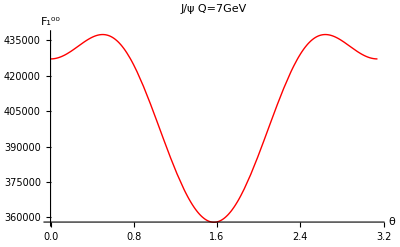

```mathematica
QNum=7;
MJψNum=3.096;
Plot[((Conv F1002Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ]}),{θ,0,π},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_1^00",FontSize->14]]},PlotLabel->"J/ψ Q="<>ToString[QNum]<>"GeV"]
```

```mathematica
MJψNum=3.096;
Plot3D[((Conv F1002Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum}),{cθ,0,0.99},{QNum,7,20},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_1^00",FontSize->14]]},PlotLabel->"J/ψ Q="<>ToString[QNum]<>"GeV"]
```

-Graphics3D-

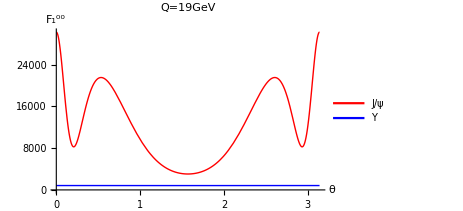
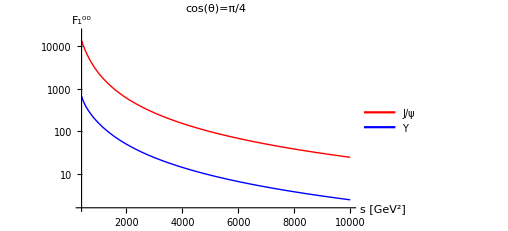

```mathematica
QNum=19;
MΥNum=9.46;
MJψNum=3.096;
{Plot[{((Conv F1002Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ]}),((Conv F1002Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MΥNum/QNum,cθ->Cos[θ]})},{θ,0,π},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_1^00",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotLabel->"Q="<>ToString[QNum]<>"GeV"],LogPlot[{((Conv F1002Jψα)/.ReplNumψ/.{α->2 MJψNum/s^(1/2),cθ->Cos[π/4]}),((Conv F1002Jψα)/.ReplNumψ/.{α->2 MΥNum/s^(1/2),cθ->Cos[π/4]})},{s,4(10)^2,(100)^2},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["s [GeV^2]",FontSize->14]],Text[Style["F_1^00",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotRange->All,PlotLabel->"cos(θ)=π/4"]}
```

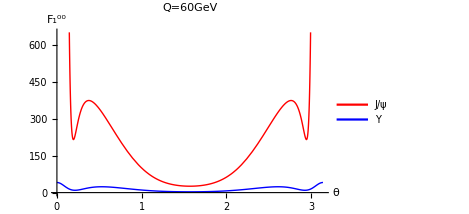
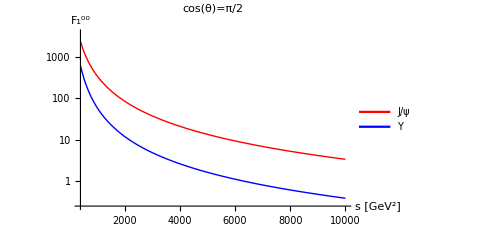

```mathematica
QNum=60;
MΥNum=9.46;
MJψNum=3.096;
{Plot[{((Conv F1002Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ]}),((Conv F1002Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MΥNum/QNum,cθ->Cos[θ]})},{θ,0,π},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_1^00",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotLabel->"Q="<>ToString[QNum]<>"GeV"],LogPlot[{((Conv F1002Jψα)/.ReplNumψ/.{α->2 MJψNum/s^(1/2),cθ->Cos[π/2]}),((Conv F1002Jψα)/.ReplNumψ/.{α->2 MΥNum/s^(1/2),cθ->Cos[π/2]})},{s,4(10)^2,(100)^2},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["s [GeV^2]",FontSize->14]],Text[Style["F_1^00",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotRange->All,PlotLabel->"cos(θ)=π/2"]}
```

IMPORTANT : F_1^01=F_1^10=0

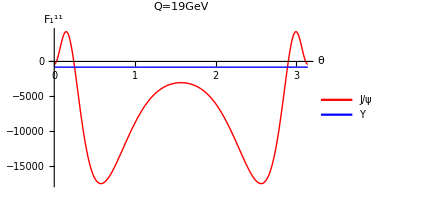
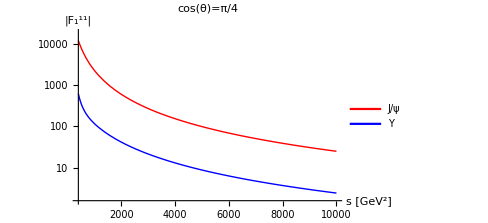

```mathematica
QNum=19;
MΥNum=9.46;
MJψNum=3.096;
{Plot[{((Conv F1112Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ]}),((Conv F1112Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MΥNum/QNum,cθ->Cos[θ]})},{θ,0,π},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_1^11",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotLabel->"Q="<>ToString[QNum]<>"GeV"],LogPlot[{Abs[((Conv F1112Jψα)/.ReplNumψ/.{α->2 MJψNum/s^(1/2),cθ->Cos[π/4]})],Abs[((Conv F1112Jψα)/.ReplNumψ/.{α->2 MΥNum/s^(1/2),cθ->Cos[π/4]})]},{s,4(10)^2,(100)^2},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["s [GeV^2]",FontSize->14]],Text[Style["|F_1^11|",FontSize->14]]},PlotRange->All,PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotLabel->"cos(θ)=π/4"]}
```

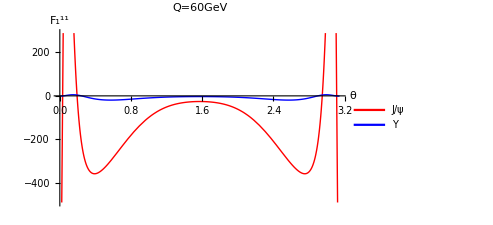
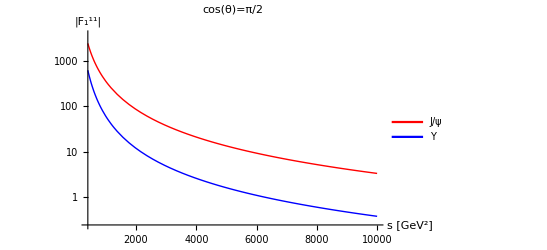

```mathematica
QNum=60;
MΥNum=9.46;
MJψNum=3.096;
{Plot[{((Conv F1112Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ]}),((Conv F1112Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MΥNum/QNum,cθ->Cos[θ]})},{θ,0,π},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_1^11",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotLabel->"Q="<>ToString[QNum]<>"GeV"],LogPlot[{Abs[((Conv F1112Jψα)/.ReplNumψ/.{α->2 MJψNum/s^(1/2),cθ->Cos[π/2]})],Abs[((Conv F1112Jψα)/.ReplNumψ/.{α->2 MΥNum/s^(1/2),cθ->Cos[π/2]})]},{s,4(10)^2,(100)^2},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["s [GeV^2]",FontSize->14]],Text[Style["|F_1^11|",FontSize->14]]},PlotRange->All,PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotLabel->"cos(θ)=π/2"]}
```

### F_2 term

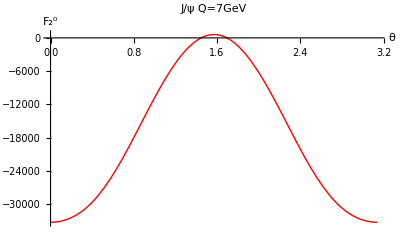

```mathematica
QNum=7;
MJψNum=3.096;
Plot[((Conv F202Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ]}),{θ,0,π},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_2^0",FontSize->14]]},PlotLabel->"J/ψ Q="<>ToString[QNum]<>"GeV"]
```

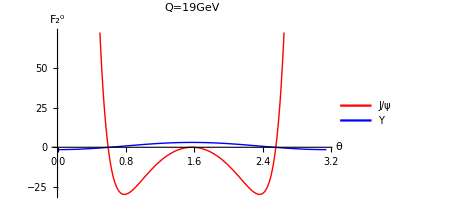
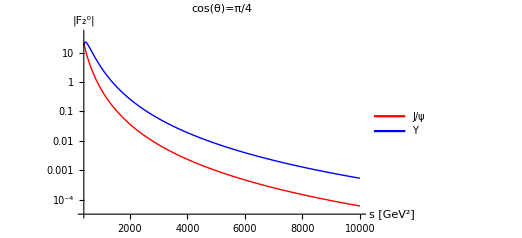

```mathematica
QNum=19;
MΥNum=9.46;
MJψNum=3.096;
{Plot[{((Conv F202Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ]}),((Conv F202Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MΥNum/QNum,cθ->Cos[θ]})},{θ,0,π},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_2^0",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotLabel->"Q="<>ToString[QNum]<>"GeV"],LogPlot[{Abs[((Conv F202Jψα)/.ReplNumψ/.{α->2 MJψNum/s^(1/2),cθ->Cos[π/4]})],Abs[((Conv F202Jψα)/.ReplNumψ/.{α->2 MΥNum/s^(1/2),cθ->Cos[π/4]})]},{s,4(10)^2,(100)^2},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["s [GeV^2]",FontSize->14]],Text[Style["|F_2^0|",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotRange->All,PlotLabel->"cos(θ)=π/4"]}
```

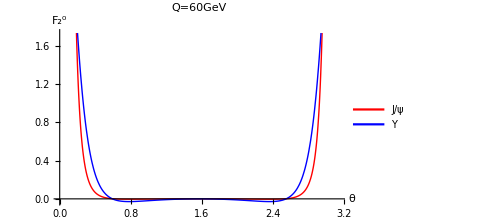
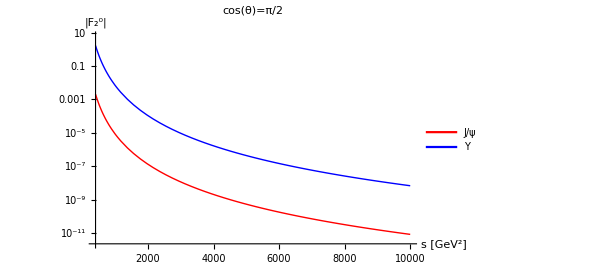

```mathematica
QNum=60;
MΥNum=9.46;
MJψNum=3.096;
{Plot[{((Conv F202Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ]}),((Conv F202Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MΥNum/QNum,cθ->Cos[θ]})},{θ,0,π},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_2^0",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotLabel->"Q="<>ToString[QNum]<>"GeV"],LogPlot[{Abs[((Conv F202Jψα)/.ReplNumψ/.{α->2 MJψNum/s^(1/2),cθ->Cos[π/2]})],Abs[((Conv F202Jψα)/.ReplNumψ/.{α->2 MΥNum/s^(1/2),cθ->Cos[π/2]})]},{s,4(10)^2,(100)^2},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["s [GeV^2]",FontSize->14]],Text[Style["|F_2^0|",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotRange->All,PlotLabel->"cos(θ)=π/2"]}
```

IMPORTANT : F_2^1=0

### F_3 term

IMPORTANT : (F_(3a))^00=(F_(3b))^00
(F_(3a))^00=A cos(2ϕ)  ; (F_(3a))^10=A  ⅈ sin(2ϕ)  
(F_(3a))^10=-(F_(3b))^01
(F_(3a))^01=(F_(3b))^10=0
(F_(3a))^11=(F_(3b))^11=0

→   ∑_(λ_1,λ_2) ((F_(3a))^(λ_1 λ_2)+(F_(3b))^(λ_1 λ_2))=2(F_(3a))^00  ~  cos(2ϕ)

```mathematica
F3002Jψaα
```

(16384 (-1+cθ^2) π^2 R0^4 (-1+α^2) (-16 α^2+3 α^4+1944 cθ^8 (-1+α^2)^4+18 cθ^6 (-1+α^2)^3 (304+9 α^2)+cθ^4 (-1+α^2)^2 (5112+16 α^2+3 α^4)-6 cθ^2 (264-291 α^2+26 α^4+α^6)) αs^4 Cos[2 ϕ])/(81 s^3 (1+cθ^2 (-1+α^2))^4)

```mathematica
F3102Jψaα
```

(16384 ⅈ (-1+cθ^2) π^2 R0^4 (-1+α^2) (-16 α^2+3 α^4+1944 cθ^8 (-1+α^2)^4+18 cθ^6 (-1+α^2)^3 (304+9 α^2)+cθ^4 (-1+α^2)^2 (5112+16 α^2+3 α^4)-6 cθ^2 (264-291 α^2+26 α^4+α^6)) αs^4 Sin[2 ϕ])/(81 s^3 (1+cθ^2 (-1+α^2))^4)

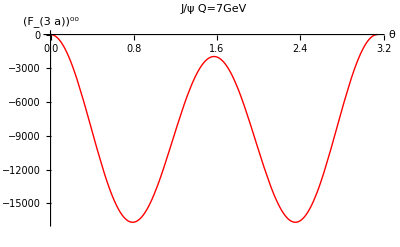

```mathematica
QNum=7;
MJψNum=3.096;
Plot[((Conv F3002Jψaα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}),{θ,0,π},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["(F_(3  a))^00",FontSize->14]]},PlotLabel->"J/ψ Q="<>ToString[QNum]<>"GeV"]
```

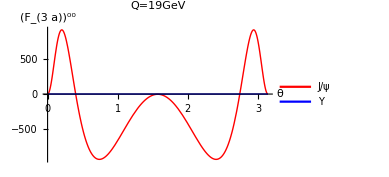
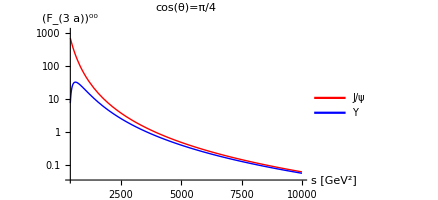

```mathematica
QNum=19;
MΥNum=9.46;
MJψNum=3.096;
{Plot[{((Conv F3002Jψaα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}),((Conv F3002Jψaα)/.ReplNumψ/.{s->QNum^2,α->2 MΥNum/QNum,cθ->Cos[θ],ϕ->0})},{θ,0,π},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["(F_(3  a))^00",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotLabel->"Q="<>ToString[QNum]<>"GeV"],LogPlot[{Abs[((Conv F3002Jψaα)/.ReplNumψ/.{α->2 MJψNum/s^(1/2),cθ->Cos[π/4],ϕ->0})],Abs[((Conv F3002Jψaα)/.ReplNumψ/.{α->2 MΥNum/s^(1/2),cθ->Cos[π/4],ϕ->0})]},{s,4(10)^2,(100)^2},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["s [GeV^2]",FontSize->14]],Text[Style["(F_(3  a))^00",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotRange->All,PlotLabel->"cos(θ)=π/4"]}
```

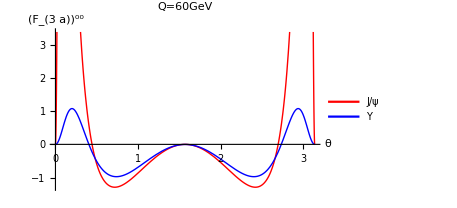
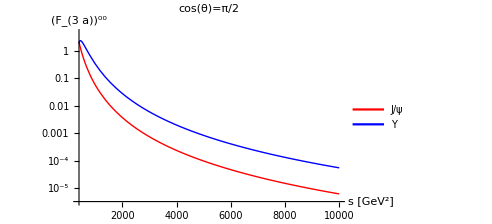

```mathematica
QNum=60;
MΥNum=9.46;
MJψNum=3.096;
{Plot[{((Conv F3002Jψaα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}),((Conv F3002Jψaα)/.ReplNumψ/.{s->QNum^2,α->2 MΥNum/QNum,cθ->Cos[θ],ϕ->0})},{θ,0,π},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["(F_(3  a))^00",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotLabel->"Q="<>ToString[QNum]<>"GeV"],LogPlot[{Abs[((Conv F3002Jψaα)/.ReplNumψ/.{α->2 MJψNum/s^(1/2),cθ->Cos[π/2],ϕ->0})],Abs[((Conv F3002Jψaα)/.ReplNumψ/.{α->2 MΥNum/s^(1/2),cθ->Cos[π/2],ϕ->0})]},{s,4(10)^2,(100)^2},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["s [GeV^2]",FontSize->14]],Text[Style["(F_(3  a))^00",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotRange->All,PlotLabel->"cos(θ)=π/2"]}
```

### F_4 term

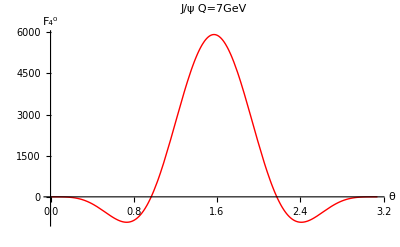

```mathematica
QNum=7;
MJψNum=3.096;
Plot[((Conv F402Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}),{θ,0,π},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_4^0",FontSize->14]]},PlotLabel->"J/ψ Q="<>ToString[QNum]<>"GeV"]
```

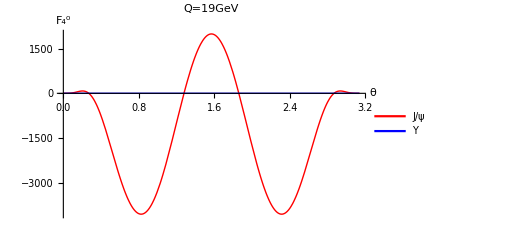
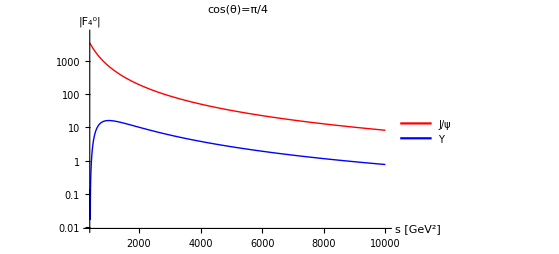

```mathematica
QNum=19;
MΥNum=9.46;
MJψNum=3.096;
{Plot[{((Conv F402Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}),((Conv F402Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MΥNum/QNum,cθ->Cos[θ],ϕ->0})},{θ,0,π},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_4^0",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotLabel->"Q="<>ToString[QNum]<>"GeV"],LogPlot[{Abs[((Conv F402Jψα)/.ReplNumψ/.{α->2 MJψNum/s^(1/2),cθ->Cos[π/4],ϕ->0})],Abs[((Conv F402Jψα)/.ReplNumψ/.{α->2 MΥNum/s^(1/2),cθ->Cos[π/4],ϕ->0})]},{s,4(10)^2,(100)^2},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["s [GeV^2]",FontSize->14]],Text[Style["|F_4^0|",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotRange->All,PlotLabel->"cos(θ)=π/4"]}
```

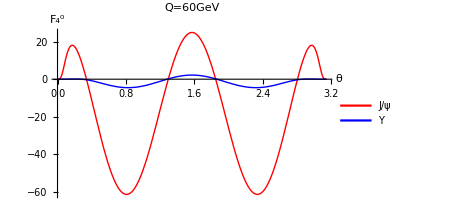
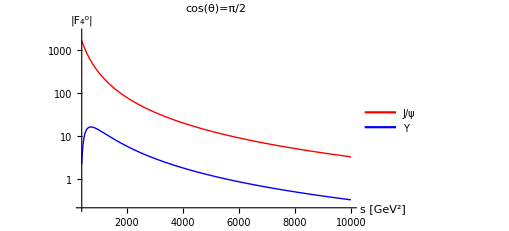

```mathematica
QNum=60;
MΥNum=9.46;
MJψNum=3.096;
{Plot[{((Conv F402Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}),((Conv F402Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MΥNum/QNum,cθ->Cos[θ],ϕ->0})},{θ,0,π},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_4^0",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotLabel->"Q="<>ToString[QNum]<>"GeV"],LogPlot[{Abs[((Conv F402Jψα)/.ReplNumψ/.{α->2 MJψNum/s^(1/2),cθ->Cos[π/2],ϕ->0})],Abs[((Conv F402Jψα)/.ReplNumψ/.{α->2 MΥNum/s^(1/2),cθ->Cos[π/2],ϕ->0})]},{s,4(10)^2,(100)^2},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["s [GeV^2]",FontSize->14]],Text[Style["|F_4^0|",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotRange->All,PlotLabel->"cos(θ)=π/2"]}
```

IMPORTANT : F_4^0=B cos(4ϕ)  ;  F_4^1=B  ⅈ sin(4ϕ)

### RATIOS

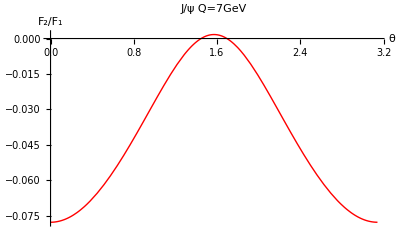

```mathematica
QNum=7;
MJψNum=3.096;
Plot[((F202Jψα/F1002Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ]}),{θ,0,π},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_2/F_1",FontSize->14]]},PlotLabel->"J/ψ Q="<>ToString[QNum]<>"GeV"]
```

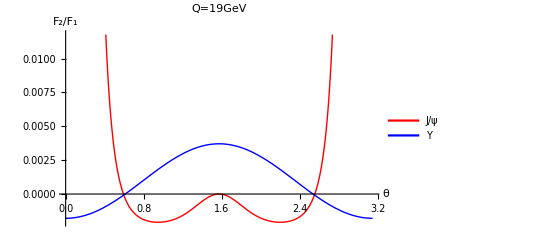
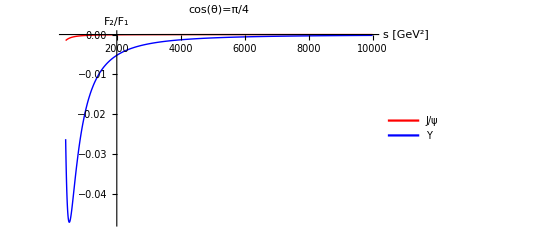

```mathematica
QNum=19;
MΥNum=9.46;
MJψNum=3.096;
{Plot[{((F202Jψα/F1002Jψα)/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ]}),((F202Jψα/F1002Jψα)/.{s->QNum^2,α->2 MΥNum/QNum,cθ->Cos[θ]})},{θ,0,π},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_2/F_1",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotLabel->"Q="<>ToString[QNum]<>"GeV"],Plot[{((F202Jψα/F1002Jψα)/.{α->2 MJψNum/s^(1/2),cθ->Cos[π/4]}),((F202Jψα/F1002Jψα)/.{α->2 MΥNum/s^(1/2),cθ->Cos[π/4]})},{s,4(10)^2,(100)^2},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["s [GeV^2]",FontSize->14]],Text[Style["F_2/F_1",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotRange->All,PlotLabel->"cos(θ)=π/4"]}
```

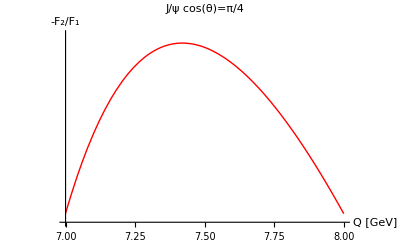

```mathematica
MJψNum=3.096;
LogPlot[((-F202Jψα/F1002Jψα)/.{α->2 MJψNum/Q,cθ->Cos[π/4]}),{Q,7,8},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["Q [GeV]",FontSize->14]],Text[Style["-F_2/F_1",FontSize->14]]},PlotLabel->"J/ψ cos(θ)=π/4",PlotRange->All]
```

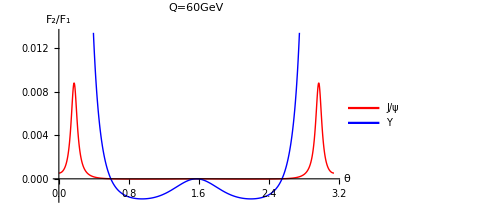
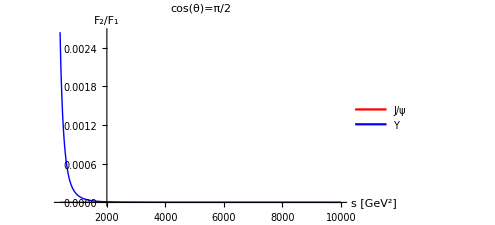

```mathematica
QNum=60;
MΥNum=9.46;
MJψNum=3.096;
{Plot[{((F202Jψα/F1002Jψα)/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ]}),((F202Jψα/F1002Jψα)/.{s->QNum^2,α->2 MΥNum/QNum,cθ->Cos[θ]})},{θ,0,π},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_2/F_1",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotLabel->"Q="<>ToString[QNum]<>"GeV"],Plot[{((F202Jψα/F1002Jψα)/.{α->2 MJψNum/s^(1/2),cθ->Cos[π/2]}),((F202Jψα/F1002Jψα)/.{α->2 MΥNum/s^(1/2),cθ->Cos[π/2]})},{s,4(10)^2,(100)^2},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["s [GeV^2]",FontSize->14]],Text[Style["F_2/F_1",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotRange->All,PlotLabel->"cos(θ)=π/2"]}
```

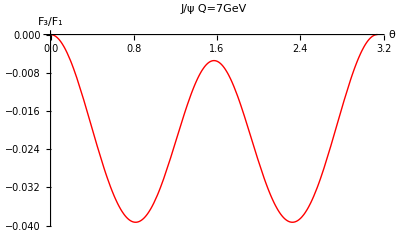

```mathematica
QNum=7;
MJψNum=3.096;
Plot[((F3002Jψaα/F1002Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}),{θ,0,π},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_3/F_1",FontSize->14]]},PlotLabel->"J/ψ Q="<>ToString[QNum]<>"GeV"]
```

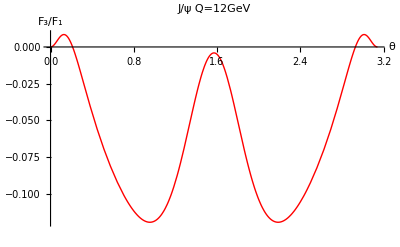

```mathematica
QNum=12;
MJψNum=3.096;
Plot[((F3002Jψaα/F1002Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}),{θ,0,π},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_3/F_1",FontSize->14]]},PlotLabel->"J/ψ Q="<>ToString[QNum]<>"GeV"]
```

```mathematica
MatrixForm[TabF3F1the=Table[{θ,(F3002Jψaα/F1002Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}/.QNum->12},{θ,0,π,0.01}]];
Export["TabF3F1the.dat",TabF3F1the];
```

```mathematica
MatrixForm[TabF3F1Q=Table[{QNum,(F3002Jψaα/F1002Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}/.θ->π/3},{QNum,6.2,20,0.01}]];
Export["TabF3F1Q.dat",TabF3F1Q];
```

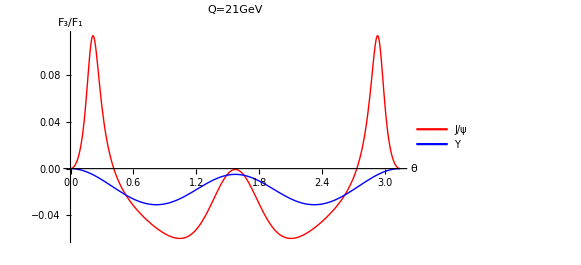
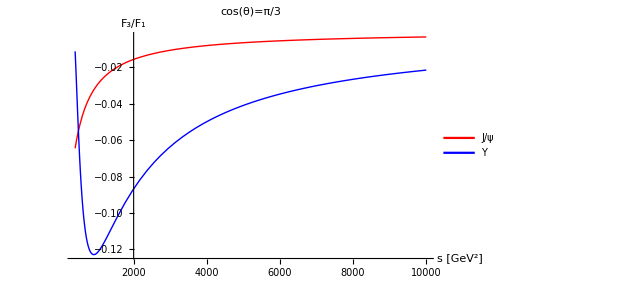

```mathematica
QNum=21;
MΥNum=9.46;
MJψNum=3.096;
{Plot[{((F3002Jψaα/F1002Jψα)/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}),((F3002Jψaα/F1002Jψα)/.{s->QNum^2,α->2 MΥNum/QNum,cθ->Cos[θ],ϕ->0})},{θ,0,π},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_3/F_1",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotLabel->"Q="<>ToString[QNum]<>"GeV",PlotRange->All],Plot[{((F3002Jψaα/F1002Jψα)/.{α->2 MJψNum/s^(1/2),cθ->Cos[π/3],ϕ->0}),((F3002Jψaα/F1002Jψα)/.{α->2 MΥNum/s^(1/2),cθ->Cos[π/4],ϕ->0})},{s,4(10)^2,(100)^2},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["s [GeV^2]",FontSize->14]],Text[Style["F_3/F_1",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotRange->All,PlotLabel->"cos(θ)=π/3"]}
```

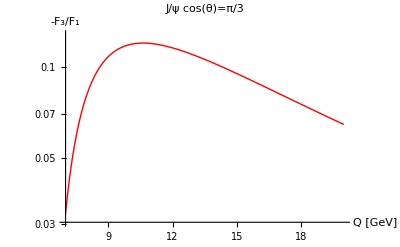

```mathematica
MJψNum=3.096;
LogPlot[((-F3002Jψaα/F1002Jψα)/.{α->2 MJψNum/Q,cθ->Cos[π/3],ϕ->0}),{Q,7,20},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["Q [GeV]",FontSize->14]],Text[Style["-F_3/F_1",FontSize->14]]},PlotLabel->"J/ψ cos(θ)=π/3",PlotRange->All]
```

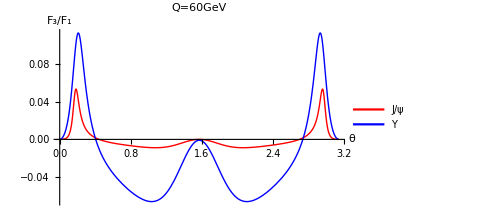
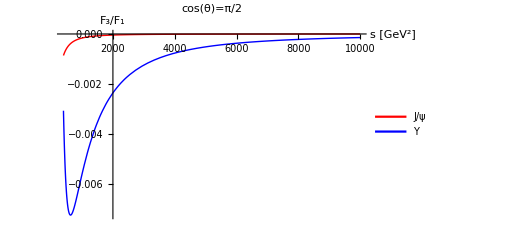

```mathematica
QNum=60;
MΥNum=9.46;
MJψNum=3.096;
{Plot[{((F3002Jψaα/F1002Jψα)/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}),((F3002Jψaα/F1002Jψα)/.{s->QNum^2,α->2 MΥNum/QNum,cθ->Cos[θ],ϕ->0})},{θ,0,π},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_3/F_1",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotLabel->"Q="<>ToString[QNum]<>"GeV"],Plot[{((F3002Jψaα/F1002Jψα)/.{α->2 MJψNum/s^(1/2),cθ->Cos[π/2],ϕ->0}),((F3002Jψaα/F1002Jψα)/.{α->2 MΥNum/s^(1/2),cθ->Cos[π/2],ϕ->0})},{s,4(10)^2,(100)^2},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["s [GeV^2]",FontSize->14]],Text[Style["F_3/F_1",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotRange->All,PlotLabel->"cos(θ)=π/2"]}
```

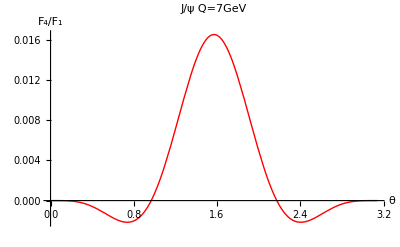

```mathematica
QNum=7;
MJψNum=3.096;
Plot[((F402Jψα/F1002Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}),{θ,0,π},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_4/F_1",FontSize->14]]},PlotLabel->"J/ψ Q="<>ToString[QNum]<>"GeV"]
```

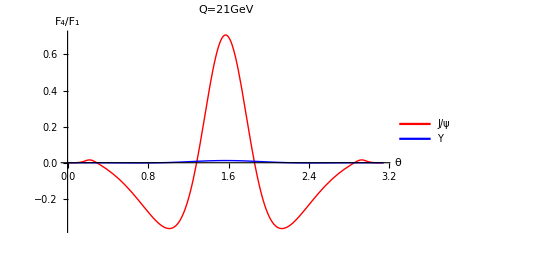
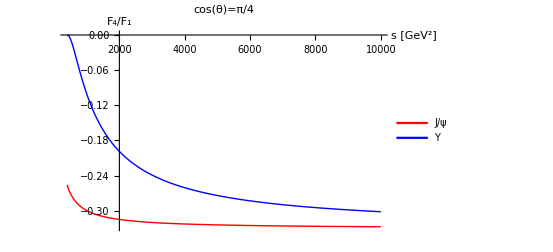

```mathematica
QNum=21;
MΥNum=9.46;
MJψNum=3.096;
{Plot[{((F402Jψα/F1002Jψα)/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}),((F402Jψα/F1002Jψα)/.{s->QNum^2,α->2 MΥNum/QNum,cθ->Cos[θ],ϕ->0})},{θ,0,π},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_4/F_1",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotRange->All,PlotLabel->"Q="<>ToString[QNum]<>"GeV"],Plot[{((F402Jψα/F1002Jψα)/.{α->2 MJψNum/s^(1/2),cθ->Cos[π/4],ϕ->0}),((F402Jψα/F1002Jψα)/.{α->2 MΥNum/s^(1/2),cθ->Cos[π/4],ϕ->0})},{s,4(10)^2,(100)^2},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["s [GeV^2]",FontSize->14]],Text[Style["F_4/F_1",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotRange->All,PlotLabel->"cos(θ)=π/4"]}
```

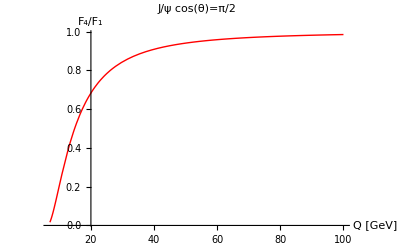

```mathematica
MJψNum=3.096;
Plot[((F402Jψα/F1002Jψα)/.{α->2 MJψNum/Q,cθ->Cos[π/2],ϕ->0}),{Q,7,100},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["Q [GeV]",FontSize->14]],Text[Style["F_4/F_1",FontSize->14]]},PlotLabel->"J/ψ cos(θ)=π/2",PlotRange->All]
```

```mathematica
MatrixForm[TabF4F1the=Table[{θ,(F402Jψα/F1002Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}/.QNum->21},{θ,0,π,0.01}]];
Export["TabF4F1the.dat",TabF4F1the];
```

```mathematica
MatrixForm[TabF4F1Q=Table[{QNum,(F402Jψα/F1002Jψα)/.ReplNumψ/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}/.θ->π/2},{QNum,6.2,20,0.01}]];
Export["TabF4F1Q.dat",TabF4F1Q];
```

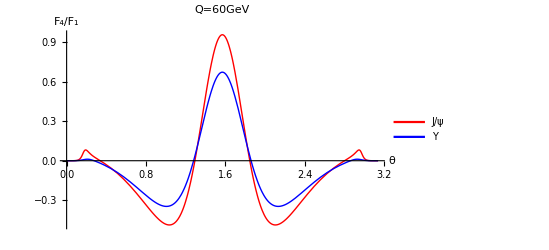
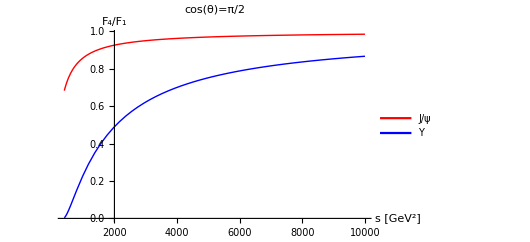

```mathematica
QNum=60;
MΥNum=9.46;
MJψNum=3.096;
{Plot[{((F402Jψα/F1002Jψα)/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}),((F402Jψα/F1002Jψα)/.{s->QNum^2,α->2 MΥNum/QNum,cθ->Cos[θ],ϕ->0})},{θ,0,π},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_4/F_1",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotRange->All,PlotLabel->"Q="<>ToString[QNum]<>"GeV"],Plot[{((F402Jψα/F1002Jψα)/.{α->2 MJψNum/s^(1/2),cθ->Cos[π/2],ϕ->0}),((F402Jψα/F1002Jψα)/.{α->2 MΥNum/s^(1/2),cθ->Cos[π/2],ϕ->0})},{s,4(10)^2,(100)^2},PlotStyle->{{Red,Thick},{Blue,Thick}},AxesLabel->{Text[Style["s [GeV^2]",FontSize->14]],Text[Style["F_4/F_1",FontSize->14]]},PlotLegends->Placed[{"J/ψ","Υ"},{0.25,0.75}],PlotRange->All,PlotLabel->"cos(θ)=π/2"]}
```

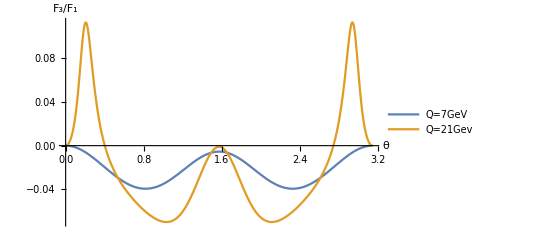
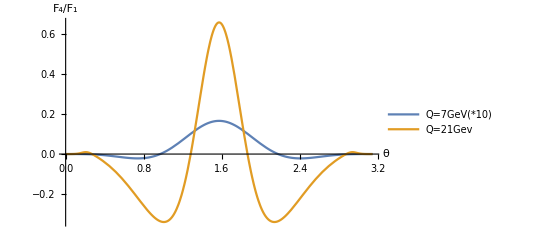

```mathematica
Clear[QNum];
MJψNum=3.096;
{Plot[{((F3002Jψaα/F1002Jψα)/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}/.QNum->7),((F3002Jψaα/F1002Jψα)/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}/.QNum->19)},{θ,0,π},PlotLegends->{"Q=7GeV","Q=21Gev"},PlotRange->All,AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_3/F_1",FontSize->14]]}],Plot[{((10*F402Jψα/F1002Jψα)/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}/.QNum->7),((F402Jψα/F1002Jψα)/.{s->QNum^2,α->2 MJψNum/QNum,cθ->Cos[θ],ϕ->0}/.QNum->19)},{θ,0,π},PlotLegends->{"Q=7GeV(*10)","Q=21Gev"},PlotRange->All,AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["F_4/F_1",FontSize->14]]}]}
```

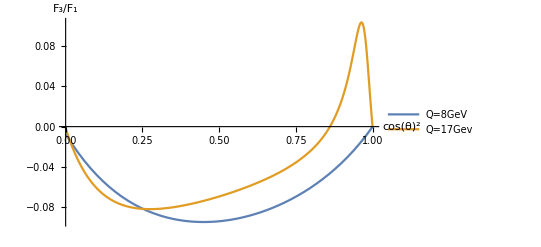
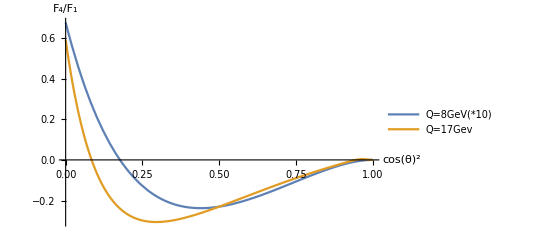

```mathematica
MJψNum=3.096;
{Plot[{((F3002Jψaα/F1002Jψα)/.{s->QNum^2,α->2 MJψNum/QNum,ϕ->0,cθ->√cθ2}/.QNum->8),((F3002Jψaα/F1002Jψα)/.{s->QNum^2,α->2 MJψNum/QNum,ϕ->0,cθ->√cθ2}/.QNum->17)},{cθ2,0,1},PlotLegends->{"Q=8GeV","Q=17Gev"},PlotRange->All,AxesLabel->{Text[Style["cos(θ)^2",FontSize->14]],Text[Style["F_3/F_1",FontSize->14]]}],Plot[{((10*F402Jψα/F1002Jψα)/.{s->QNum^2,α->2 MJψNum/QNum,ϕ->0,cθ->√cθ2}/.QNum->8),((F402Jψα/F1002Jψα)/.{s->QNum^2,α->2 MJψNum/QNum,ϕ->0,cθ->√cθ2}/.QNum->17)},{cθ2,0,1},PlotLegends->{"Q=8GeV(*10)","Q=17Gev"},PlotRange->All,AxesLabel->{Text[Style["cos(θ)^2",FontSize->14]],Text[Style["F_4/F_1",FontSize->14]]}]}
```

```mathematica
(Solve[D[F402Jψα/.s->Mψψ^2/.α->2 Mψ/Mψψ/.cθ->√cθ2//Simplify,cθ2]==0,cθ2]/.Mψ->3.097/.R0->1/.αs->1/.ϕ->0/.Mψψ->10+i)
```

{{cθ2→1},{cθ2→Root[7.68097×10^11+8.47651×10^11 i+4.13443×10^11 i^2+1.17751×10^11 i^3+2.17353×10^10 i^4+2.72141×10^9 i^5+2.34343×10^8 i^6+1.37154×10^7 i^7+522443. i^8+11700 i^9+117 i^10+(-3.59561×10^12-4.20471×10^12 i-2.15502×10^12 i^2-6.39764×10^11 i^3-1.22182×10^11 i^4-1.57202×10^10 i^5-1.38236×10^9 i^6-8.21433×10^7 i^7-3.15979×10^6 i^8-71100 i^9-711 i^10) #1+(5.87702×10^12+7.43875×10^12 i+4.08732×10^12 i^2+1.28706×10^12 i^3+2.57996×10^11 i^4+3.44991×10^10 i^5+3.12433×10^9 i^6+1.8961×10^8 i^7+7.39212×10^6 i^8+167400 i^9+1674 i^10) #1^2+(-4.42286×10^12-6.09158×10^12 i-3.62073×10^12 i^2-1.22251×10^12 i^3-2.59929×10^11 i^4-3.64457×10^10 i^5-3.42222×10^9 i^6-2.13082×10^8 i^7-8.44153×10^6 i^8-192600 i^9-1926 i^10) #1^3+(1.57526×10^12+2.35895×10^12 i+1.52112×10^12 i^2+5.54182×10^11 i^3+1.2601×10^11 i^4+1.86732×10^10 i^5+1.82926×10^9 i^6+1.17331×10^8 i^7+4.73364×10^6 i^8+108900 i^9+1089 i^10) #1^4+(-2.16133×10^11-3.50669×10^11 i-2.45114×10^11 i^2-9.66066×10^10 i^3-2.3628×10^10 i^4-3.72781×10^9 i^5-3.83357×10^8 i^6-2.54309×10^7 i^7-1.04689×10^6 i^8-24300 i^9-243 i^10) #1^5&,1]},{cθ2→Root[7.68097×10^11+8.47651×10^11 i+4.13443×10^11 i^2+1.17751×10^11 i^3+2.17353×10^10 i^4+2.72141×10^9 i^5+2.34343×10^8 i^6+1.37154×10^7 i^7+522443. i^8+11700 i^9+117 i^10+(-3.59561×10^12-4.20471×10^12 i-2.15502×10^12 i^2-6.39764×10^11 i^3-1.22182×10^11 i^4-1.57202×10^10 i^5-1.38236×10^9 i^6-8.21433×10^7 i^7-3.15979×10^6 i^8-71100 i^9-711 i^10) #1+(5.87702×10^12+7.43875×10^12 i+4.08732×10^12 i^2+1.28706×10^12 i^3+2.57996×10^11 i^4+3.44991×10^10 i^5+3.12433×10^9 i^6+1.8961×10^8 i^7+7.39212×10^6 i^8+167400 i^9+1674 i^10) #1^2+(-4.42286×10^12-6.09158×10^12 i-3.62073×10^12 i^2-1.22251×10^12 i^3-2.59929×10^11 i^4-3.64457×10^10 i^5-3.42222×10^9 i^6-2.13082×10^8 i^7-8.44153×10^6 i^8-192600 i^9-1926 i^10) #1^3+(1.57526×10^12+2.35895×10^12 i+1.52112×10^12 i^2+5.54182×10^11 i^3+1.2601×10^11 i^4+1.86732×10^10 i^5+1.82926×10^9 i^6+1.17331×10^8 i^7+4.73364×10^6 i^8+108900 i^9+1089 i^10) #1^4+(-2.16133×10^11-3.50669×10^11 i-2.45114×10^11 i^2-9.66066×10^10 i^3-2.3628×10^10 i^4-3.72781×10^9 i^5-3.83357×10^8 i^6-2.54309×10^7 i^7-1.04689×10^6 i^8-24300 i^9-243 i^10) #1^5&,2]},{cθ2→Root[7.68097×10^11+8.47651×10^11 i+4.13443×10^11 i^2+1.17751×10^11 i^3+2.17353×10^10 i^4+2.72141×10^9 i^5+2.34343×10^8 i^6+1.37154×10^7 i^7+522443. i^8+11700 i^9+117 i^10+(-3.59561×10^12-4.20471×10^12 i-2.15502×10^12 i^2-6.39764×10^11 i^3-1.22182×10^11 i^4-1.57202×10^10 i^5-1.38236×10^9 i^6-8.21433×10^7 i^7-3.15979×10^6 i^8-71100 i^9-711 i^10) #1+(5.87702×10^12+7.43875×10^12 i+4.08732×10^12 i^2+1.28706×10^12 i^3+2.57996×10^11 i^4+3.44991×10^10 i^5+3.12433×10^9 i^6+1.8961×10^8 i^7+7.39212×10^6 i^8+167400 i^9+1674 i^10) #1^2+(-4.42286×10^12-6.09158×10^12 i-3.62073×10^12 i^2-1.22251×10^12 i^3-2.59929×10^11 i^4-3.64457×10^10 i^5-3.42222×10^9 i^6-2.13082×10^8 i^7-8.44153×10^6 i^8-192600 i^9-1926 i^10) #1^3+(1.57526×10^12+2.35895×10^12 i+1.52112×10^12 i^2+5.54182×10^11 i^3+1.2601×10^11 i^4+1.86732×10^10 i^5+1.82926×10^9 i^6+1.17331×10^8 i^7+4.73364×10^6 i^8+108900 i^9+1089 i^10) #1^4+(-2.16133×10^11-3.50669×10^11 i-2.45114×10^11 i^2-9.66066×10^10 i^3-2.3628×10^10 i^4-3.72781×10^9 i^5-3.83357×10^8 i^6-2.54309×10^7 i^7-1.04689×10^6 i^8-24300 i^9-243 i^10) #1^5&,3]},{cθ2→Root[7.68097×10^11+8.47651×10^11 i+4.13443×10^11 i^2+1.17751×10^11 i^3+2.17353×10^10 i^4+2.72141×10^9 i^5+2.34343×10^8 i^6+1.37154×10^7 i^7+522443. i^8+11700 i^9+117 i^10+(-3.59561×10^12-4.20471×10^12 i-2.15502×10^12 i^2-6.39764×10^11 i^3-1.22182×10^11 i^4-1.57202×10^10 i^5-1.38236×10^9 i^6-8.21433×10^7 i^7-3.15979×10^6 i^8-71100 i^9-711 i^10) #1+(5.87702×10^12+7.43875×10^12 i+4.08732×10^12 i^2+1.28706×10^12 i^3+2.57996×10^11 i^4+3.44991×10^10 i^5+3.12433×10^9 i^6+1.8961×10^8 i^7+7.39212×10^6 i^8+167400 i^9+1674 i^10) #1^2+(-4.42286×10^12-6.09158×10^12 i-3.62073×10^12 i^2-1.22251×10^12 i^3-2.59929×10^11 i^4-3.64457×10^10 i^5-3.42222×10^9 i^6-2.13082×10^8 i^7-8.44153×10^6 i^8-192600 i^9-1926 i^10) #1^3+(1.57526×10^12+2.35895×10^12 i+1.52112×10^12 i^2+5.54182×10^11 i^3+1.2601×10^11 i^4+1.86732×10^10 i^5+1.82926×10^9 i^6+1.17331×10^8 i^7+4.73364×10^6 i^8+108900 i^9+1089 i^10) #1^4+(-2.16133×10^11-3.50669×10^11 i-2.45114×10^11 i^2-9.66066×10^10 i^3-2.3628×10^10 i^4-3.72781×10^9 i^5-3.83357×10^8 i^6-2.54309×10^7 i^7-1.04689×10^6 i^8-24300 i^9-243 i^10) #1^5&,4]},{cθ2→Root[7.68097×10^11+8.47651×10^11 i+4.13443×10^11 i^2+1.17751×10^11 i^3+2.17353×10^10 i^4+2.72141×10^9 i^5+2.34343×10^8 i^6+1.37154×10^7 i^7+522443. i^8+11700 i^9+117 i^10+(-3.59561×10^12-4.20471×10^12 i-2.15502×10^12 i^2-6.39764×10^11 i^3-1.22182×10^11 i^4-1.57202×10^10 i^5-1.38236×10^9 i^6-8.21433×10^7 i^7-3.15979×10^6 i^8-71100 i^9-711 i^10) #1+(5.87702×10^12+7.43875×10^12 i+4.08732×10^12 i^2+1.28706×10^12 i^3+2.57996×10^11 i^4+3.44991×10^10 i^5+3.12433×10^9 i^6+1.8961×10^8 i^7+7.39212×10^6 i^8+167400 i^9+1674 i^10) #1^2+(-4.42286×10^12-6.09158×10^12 i-3.62073×10^12 i^2-1.22251×10^12 i^3-2.59929×10^11 i^4-3.64457×10^10 i^5-3.42222×10^9 i^6-2.13082×10^8 i^7-8.44153×10^6 i^8-192600 i^9-1926 i^10) #1^3+(1.57526×10^12+2.35895×10^12 i+1.52112×10^12 i^2+5.54182×10^11 i^3+1.2601×10^11 i^4+1.86732×10^10 i^5+1.82926×10^9 i^6+1.17331×10^8 i^7+4.73364×10^6 i^8+108900 i^9+1089 i^10) #1^4+(-2.16133×10^11-3.50669×10^11 i-2.45114×10^11 i^2-9.66066×10^10 i^3-2.3628×10^10 i^4-3.72781×10^9 i^5-3.83357×10^8 i^6-2.54309×10^7 i^7-1.04689×10^6 i^8-24300 i^9-243 i^10) #1^5&,5]}}

```mathematica
(Solve[D[F402Jψα/.s->Mψψ^2/.α->2 Mψ/Mψψ/.cθ->√cθ2//Simplify,cθ2]==0,cθ2]/.Mψ->3.097/.R0->1/.αs->1/.ϕ->0/.Mψψ->10+i)[[All,1,2]]
```

{1,Root[7.68097×10^11+8.47651×10^11 i+4.13443×10^11 i^2+1.17751×10^11 i^3+2.17353×10^10 i^4+2.72141×10^9 i^5+2.34343×10^8 i^6+1.37154×10^7 i^7+522443. i^8+11700 i^9+117 i^10+(-3.59561×10^12-4.20471×10^12 i-2.15502×10^12 i^2-6.39764×10^11 i^3-1.22182×10^11 i^4-1.57202×10^10 i^5-1.38236×10^9 i^6-8.21433×10^7 i^7-3.15979×10^6 i^8-71100 i^9-711 i^10) #1+(5.87702×10^12+7.43875×10^12 i+4.08732×10^12 i^2+1.28706×10^12 i^3+2.57996×10^11 i^4+3.44991×10^10 i^5+3.12433×10^9 i^6+1.8961×10^8 i^7+7.39212×10^6 i^8+167400 i^9+1674 i^10) #1^2+(-4.42286×10^12-6.09158×10^12 i-3.62073×10^12 i^2-1.22251×10^12 i^3-2.59929×10^11 i^4-3.64457×10^10 i^5-3.42222×10^9 i^6-2.13082×10^8 i^7-8.44153×10^6 i^8-192600 i^9-1926 i^10) #1^3+(1.57526×10^12+2.35895×10^12 i+1.52112×10^12 i^2+5.54182×10^11 i^3+1.2601×10^11 i^4+1.86732×10^10 i^5+1.82926×10^9 i^6+1.17331×10^8 i^7+4.73364×10^6 i^8+108900 i^9+1089 i^10) #1^4+(-2.16133×10^11-3.50669×10^11 i-2.45114×10^11 i^2-9.66066×10^10 i^3-2.3628×10^10 i^4-3.72781×10^9 i^5-3.83357×10^8 i^6-2.54309×10^7 i^7-1.04689×10^6 i^8-24300 i^9-243 i^10) #1^5&,1],Root[7.68097×10^11+8.47651×10^11 i+4.13443×10^11 i^2+1.17751×10^11 i^3+2.17353×10^10 i^4+2.72141×10^9 i^5+2.34343×10^8 i^6+1.37154×10^7 i^7+522443. i^8+11700 i^9+117 i^10+(-3.59561×10^12-4.20471×10^12 i-2.15502×10^12 i^2-6.39764×10^11 i^3-1.22182×10^11 i^4-1.57202×10^10 i^5-1.38236×10^9 i^6-8.21433×10^7 i^7-3.15979×10^6 i^8-71100 i^9-711 i^10) #1+(5.87702×10^12+7.43875×10^12 i+4.08732×10^12 i^2+1.28706×10^12 i^3+2.57996×10^11 i^4+3.44991×10^10 i^5+3.12433×10^9 i^6+1.8961×10^8 i^7+7.39212×10^6 i^8+167400 i^9+1674 i^10) #1^2+(-4.42286×10^12-6.09158×10^12 i-3.62073×10^12 i^2-1.22251×10^12 i^3-2.59929×10^11 i^4-3.64457×10^10 i^5-3.42222×10^9 i^6-2.13082×10^8 i^7-8.44153×10^6 i^8-192600 i^9-1926 i^10) #1^3+(1.57526×10^12+2.35895×10^12 i+1.52112×10^12 i^2+5.54182×10^11 i^3+1.2601×10^11 i^4+1.86732×10^10 i^5+1.82926×10^9 i^6+1.17331×10^8 i^7+4.73364×10^6 i^8+108900 i^9+1089 i^10) #1^4+(-2.16133×10^11-3.50669×10^11 i-2.45114×10^11 i^2-9.66066×10^10 i^3-2.3628×10^10 i^4-3.72781×10^9 i^5-3.83357×10^8 i^6-2.54309×10^7 i^7-1.04689×10^6 i^8-24300 i^9-243 i^10) #1^5&,2],Root[7.68097×10^11+8.47651×10^11 i+4.13443×10^11 i^2+1.17751×10^11 i^3+2.17353×10^10 i^4+2.72141×10^9 i^5+2.34343×10^8 i^6+1.37154×10^7 i^7+522443. i^8+11700 i^9+117 i^10+(-3.59561×10^12-4.20471×10^12 i-2.15502×10^12 i^2-6.39764×10^11 i^3-1.22182×10^11 i^4-1.57202×10^10 i^5-1.38236×10^9 i^6-8.21433×10^7 i^7-3.15979×10^6 i^8-71100 i^9-711 i^10) #1+(5.87702×10^12+7.43875×10^12 i+4.08732×10^12 i^2+1.28706×10^12 i^3+2.57996×10^11 i^4+3.44991×10^10 i^5+3.12433×10^9 i^6+1.8961×10^8 i^7+7.39212×10^6 i^8+167400 i^9+1674 i^10) #1^2+(-4.42286×10^12-6.09158×10^12 i-3.62073×10^12 i^2-1.22251×10^12 i^3-2.59929×10^11 i^4-3.64457×10^10 i^5-3.42222×10^9 i^6-2.13082×10^8 i^7-8.44153×10^6 i^8-192600 i^9-1926 i^10) #1^3+(1.57526×10^12+2.35895×10^12 i+1.52112×10^12 i^2+5.54182×10^11 i^3+1.2601×10^11 i^4+1.86732×10^10 i^5+1.82926×10^9 i^6+1.17331×10^8 i^7+4.73364×10^6 i^8+108900 i^9+1089 i^10) #1^4+(-2.16133×10^11-3.50669×10^11 i-2.45114×10^11 i^2-9.66066×10^10 i^3-2.3628×10^10 i^4-3.72781×10^9 i^5-3.83357×10^8 i^6-2.54309×10^7 i^7-1.04689×10^6 i^8-24300 i^9-243 i^10) #1^5&,3],Root[7.68097×10^11+8.47651×10^11 i+4.13443×10^11 i^2+1.17751×10^11 i^3+2.17353×10^10 i^4+2.72141×10^9 i^5+2.34343×10^8 i^6+1.37154×10^7 i^7+522443. i^8+11700 i^9+117 i^10+(-3.59561×10^12-4.20471×10^12 i-2.15502×10^12 i^2-6.39764×10^11 i^3-1.22182×10^11 i^4-1.57202×10^10 i^5-1.38236×10^9 i^6-8.21433×10^7 i^7-3.15979×10^6 i^8-71100 i^9-711 i^10) #1+(5.87702×10^12+7.43875×10^12 i+4.08732×10^12 i^2+1.28706×10^12 i^3+2.57996×10^11 i^4+3.44991×10^10 i^5+3.12433×10^9 i^6+1.8961×10^8 i^7+7.39212×10^6 i^8+167400 i^9+1674 i^10) #1^2+(-4.42286×10^12-6.09158×10^12 i-3.62073×10^12 i^2-1.22251×10^12 i^3-2.59929×10^11 i^4-3.64457×10^10 i^5-3.42222×10^9 i^6-2.13082×10^8 i^7-8.44153×10^6 i^8-192600 i^9-1926 i^10) #1^3+(1.57526×10^12+2.35895×10^12 i+1.52112×10^12 i^2+5.54182×10^11 i^3+1.2601×10^11 i^4+1.86732×10^10 i^5+1.82926×10^9 i^6+1.17331×10^8 i^7+4.73364×10^6 i^8+108900 i^9+1089 i^10) #1^4+(-2.16133×10^11-3.50669×10^11 i-2.45114×10^11 i^2-9.66066×10^10 i^3-2.3628×10^10 i^4-3.72781×10^9 i^5-3.83357×10^8 i^6-2.54309×10^7 i^7-1.04689×10^6 i^8-24300 i^9-243 i^10) #1^5&,4],Root[7.68097×10^11+8.47651×10^11 i+4.13443×10^11 i^2+1.17751×10^11 i^3+2.17353×10^10 i^4+2.72141×10^9 i^5+2.34343×10^8 i^6+1.37154×10^7 i^7+522443. i^8+11700 i^9+117 i^10+(-3.59561×10^12-4.20471×10^12 i-2.15502×10^12 i^2-6.39764×10^11 i^3-1.22182×10^11 i^4-1.57202×10^10 i^5-1.38236×10^9 i^6-8.21433×10^7 i^7-3.15979×10^6 i^8-71100 i^9-711 i^10) #1+(5.87702×10^12+7.43875×10^12 i+4.08732×10^12 i^2+1.28706×10^12 i^3+2.57996×10^11 i^4+3.44991×10^10 i^5+3.12433×10^9 i^6+1.8961×10^8 i^7+7.39212×10^6 i^8+167400 i^9+1674 i^10) #1^2+(-4.42286×10^12-6.09158×10^12 i-3.62073×10^12 i^2-1.22251×10^12 i^3-2.59929×10^11 i^4-3.64457×10^10 i^5-3.42222×10^9 i^6-2.13082×10^8 i^7-8.44153×10^6 i^8-192600 i^9-1926 i^10) #1^3+(1.57526×10^12+2.35895×10^12 i+1.52112×10^12 i^2+5.54182×10^11 i^3+1.2601×10^11 i^4+1.86732×10^10 i^5+1.82926×10^9 i^6+1.17331×10^8 i^7+4.73364×10^6 i^8+108900 i^9+1089 i^10) #1^4+(-2.16133×10^11-3.50669×10^11 i-2.45114×10^11 i^2-9.66066×10^10 i^3-2.3628×10^10 i^4-3.72781×10^9 i^5-3.83357×10^8 i^6-2.54309×10^7 i^7-1.04689×10^6 i^8-24300 i^9-243 i^10) #1^5&,5]}

```mathematica
Table[{7+i,Sqrt[(Solve[D[F3002Jψaα/.s->Mψψ^2/.α->2 Mψ/Mψψ/.cθ->√cθ2//Simplify,cθ2]==0,cθ2]/.Mψ->3.097/.R0->1/.αs->1/.ϕ->0/.Mψψ->7+i)[[All,1,2]]]},{i,10}]
```

{{8,{0.717303,1.16933,1.607,2.00852-0.157076 ⅈ,2.00852+0.157076 ⅈ}},{9,{0.722643,1.06756,1.39698,1.71828-0.0974748 ⅈ,1.71828+0.0974748 ⅈ}},{10,{0.725754,1.0233,1.28773,1.56296-0.0520328 ⅈ,1.56296+0.0520328 ⅈ}},{11,{0.727985,1.00134,1.22106,1.43367,1.49745}},{12,{0.729839,0.98977,1.17648,1.34127,1.45621}},{13,{0.731504,0.983573,1.14482,1.28076,1.4195}},{14,{0.733046,0.98034,1.12134,1.23671,1.38983}},{15,{0.73449,0.978815,1.10336,1.2031,1.3658}},{16,{0.735839,0.9783,1.08924,1.17662,1.34611}},{17,{0.737096,0.978389,1.07792,1.15528,1.32975}}}

```mathematica
Table[{7+i,(Solve[D[F402Jψα/.s->Mψψ^2/.α->2 Mψ/Mψψ/.cθ->√cθ2//Simplify,cθ2]==0,cθ2]/.Mψ->3.097/.R0->1/.αs->1/.ϕ->0/.Mψψ->7+i)[[All,1,2]]},{i,10}]
```

{{8,{1,0.467899,1.60995,2.56396,3.29423-0.655107 ⅈ,3.29423+0.655107 ⅈ}},{9,{1,0.449911,1.29868,1.9404,2.42513-0.428621 ⅈ,2.42513+0.428621 ⅈ}},{10,{1,0.445206,1.16089,1.65053,2.01587-0.319802 ⅈ,2.01587+0.319802 ⅈ}},{11,{1,0.444824,1.08676,1.48523,1.77912-0.255353 ⅈ,1.77912+0.255353 ⅈ}},{12,{1,0.446112,1.04243,1.37959,1.62554-0.212459 ⅈ,1.62554+0.212459 ⅈ}},{13,{1,0.448057,1.01413,1.30695,1.51833-0.181701 ⅈ,1.51833+0.181701 ⅈ}},{14,{1,0.450218,0.995269,1.25438,1.43955-0.158477 ⅈ,1.43955+0.158477 ⅈ}},{15,{1,0.452389,0.982323,1.21485,1.37943-0.140268 ⅈ,1.37943+0.140268 ⅈ}},{16,{1,0.454475,0.973262,1.18425,1.3322-0.125575 ⅈ,1.3322+0.125575 ⅈ}},{17,{1,0.456431,0.966847,1.15999,1.29423-0.113451 ⅈ,1.29423+0.113451 ⅈ}}}

```mathematica
Table[{7+i,ArcCos[Sqrt[(NSolve[D[(F3002Jψaα/F1002Jψα)/.s->Mψψ^2/.α->2 Mψ/Mψψ/.cθ->√cθ2,cθ2]==0,cθ2]/.Mψ->3.097/.R0->1/.αs->1/.ϕ->0/.Mψψ->7+i)[[All,1,2]]]]},{i,10}]
```

{{8,{1.5708-0.964262 ⅈ,0.83607,0.+1.11846 ⅈ,0.+1.24013 ⅈ,0.125862+0.651784 ⅈ,0.125862-0.651784 ⅈ,0.508856+1.09293 ⅈ,0.508856-1.09293 ⅈ,0.172176+0.987216 ⅈ,0.172176-0.987216 ⅈ}},{9,{1.5708-0.821671 ⅈ,0.868778,0.+0.928905 ⅈ,0.+1.04769 ⅈ,0.0821822+0.440428 ⅈ,0.0821822-0.440428 ⅈ,0.502911+0.940922 ⅈ,0.502911-0.940922 ⅈ,0.180683+0.791301 ⅈ,0.180683-0.791301 ⅈ}},{10,{1.5708-0.739723 ⅈ,0.902187,0.+0.25424 ⅈ,0.+0.339132 ⅈ,0.+0.805004 ⅈ,0.+0.921968 ⅈ,0.498093+0.847636 ⅈ,0.498093-0.847636 ⅈ,0.188063+0.661952 ⅈ,0.188063-0.661952 ⅈ}},{11,{1.5708-0.686681 ⅈ,0.931035,0.+0.0522793 ⅈ,0.+0.289262 ⅈ,0.+0.714988 ⅈ,0.+0.830848 ⅈ,0.494863+0.782874 ⅈ,0.494863-0.782874 ⅈ,0.195709+0.567331 ⅈ,0.195709-0.567331 ⅈ}},{12,{1.5708-0.64978 ⅈ,0.954479,0.128281,0.+0.241262 ⅈ,0.+0.645504 ⅈ,0.+0.760738 ⅈ,0.493114+0.734543 ⅈ,0.493114-0.734543 ⅈ,0.204845+0.494278 ⅈ,0.204845-0.494278 ⅈ}},{13,{1.5708-0.622812 ⅈ,0.973247,0.147858,0.+0.209946 ⅈ,0.+0.589699 ⅈ,0.+0.704621 ⅈ,0.492618+0.696771 ⅈ,0.492618-0.696771 ⅈ,0.216392+0.436827 ⅈ,0.216392-0.436827 ⅈ}},{14,{1.5708-0.602375 ⅈ,0.988313,0.156995,0.+0.198581 ⅈ,0.+0.5436 ⅈ,0.+0.658416 ⅈ,0.493138+0.666338 ⅈ,0.493138-0.666338 ⅈ,0.230221+0.392744 ⅈ,0.230221-0.392744 ⅈ}},{15,{1.5708-0.586452 ⅈ,1.00052,0.168524,0.+0.198926 ⅈ,0.+0.504707 ⅈ,0.+0.619546 ⅈ,0.494456+0.641317 ⅈ,0.494456-0.641317 ⅈ,0.244322+0.360892 ⅈ,0.244322-0.360892 ⅈ}},{16,{1.5708-0.573765 ⅈ,1.01051,0.180692,0.+0.200166 ⅈ,0.+0.471351 ⅈ,0.+0.58629 ⅈ,0.496375+0.620469 ⅈ,0.496375-0.620469 ⅈ,0.256087+0.33886 ⅈ,0.256087-0.33886 ⅈ}},{17,{1.5708-0.563471 ⅈ,1.01879,0.191247,0.+0.198692 ⅈ,0.+0.442361 ⅈ,0.+0.557443 ⅈ,0.498718+0.602941 ⅈ,0.498718-0.602941 ⅈ,0.264364+0.323418 ⅈ,0.264364-0.323418 ⅈ}}}

```mathematica
Table[{7+i,ArcCos[Sqrt[(NSolve[D[(F402Jψα/F1002Jψα)/.s->Mψψ^2/.α->2 Mψ/Mψψ/.cθ->√cθ2,cθ2]==0,cθ2]/.Mψ->3.097/.R0->1/.αs->1/.ϕ->0/.Mψψ->7+i)[[All,1,2]]]]},{i,10}]
```

{{8,{0.,1.5708-0.945818 ⅈ,0.845198,0.+1.11356 ⅈ,0.0883267+0.718126 ⅈ,0.0883267-0.718126 ⅈ,0.0896422+0.894838 ⅈ,0.0896422-0.894838 ⅈ,0.0564793+1.2764 ⅈ,0.0564793-1.2764 ⅈ}},{9,{0.,1.5708-0.811652 ⅈ,0.88893,0.+0.924389 ⅈ,0.0751094+0.521917 ⅈ,0.0751094-0.521917 ⅈ,0.0852857+0.705388 ⅈ,0.0852857-0.705388 ⅈ,0.052021+1.09091 ⅈ,0.052021-1.09091 ⅈ}},{10,{0.,1.5708-0.734672 ⅈ,0.917361,0.+0.801183 ⅈ,0.0621598+0.393164 ⅈ,0.0621598-0.393164 ⅈ,0.0784258+0.578797 ⅈ,0.0784258-0.578797 ⅈ,0.0472165+0.970067 ⅈ,0.0472165-0.970067 ⅈ}},{11,{0.,1.5708-0.684525 ⅈ,0.938116,0.+0.711992 ⅈ,0.048883+0.30094 ⅈ,0.048883-0.30094 ⅈ,0.067206+0.481837 ⅈ,0.067206-0.481837 ⅈ,0.0423479+0.882428 ⅈ,0.0423479-0.882428 ⅈ}},{12,{0.,1.5708-0.649296 ⅈ,0.953946,0.+0.643364 ⅈ,0.0190685+0.238157 ⅈ,0.0190685-0.238157 ⅈ,0.0398468+0.39482 ⅈ,0.0398468-0.39482 ⅈ,0.0375016+0.814838 ⅈ,0.0375016-0.814838 ⅈ}},{13,{0.,1.5708-0.623268 ⅈ,0.966333,0.+0.121267 ⅈ,0.+0.384062 ⅈ,0.+0.588392 ⅈ,0.0854103+0.255697 ⅈ,0.0854103-0.255697 ⅈ,0.0326674+0.760566 ⅈ,0.0326674-0.760566 ⅈ}},{14,{0.,1.5708-0.603331 ⅈ,0.976216,0.0685046,0.+0.360558 ⅈ,0.+0.543076 ⅈ,0.136125+0.211035 ⅈ,0.136125-0.211035 ⅈ,0.0277682+0.715719 ⅈ,0.0277682-0.715719 ⅈ}},{15,{0.,1.5708-0.587638 ⅈ,0.984228,0.131811,0.+0.336789 ⅈ,0.+0.504901 ⅈ,0.173494+0.184188 ⅈ,0.173494-0.184188 ⅈ,0.0226424+0.677852 ⅈ,0.0226424-0.677852 ⅈ}},{16,{0.,1.5708-0.575018 ⅈ,0.990812,0.162593,0.+0.315214 ⅈ,0.+0.472193 ⅈ,0.200985+0.168392 ⅈ,0.200985-0.168392 ⅈ,0.0169344+0.645334 ⅈ,0.0169344-0.645334 ⅈ}},{17,{0.,1.5708-0.564693 ⅈ,0.99629,0.182112,0.+0.29598 ⅈ,0.+0.443783 ⅈ,0.220786+0.158566 ⅈ,0.220786-0.158566 ⅈ,0.00941884+0.617025 ⅈ,0.00941884-0.617025 ⅈ}}}

```mathematica
Table[{7+i,(NSolve[D[(F3002Jψaα/F1002Jψα)/.s->Mψψ^2/.α->2 Mψ/Mψψ/.cθ->√cθ2,cθ2]==0 ,cθ2]/.Mψ->3.097/.R0->1/.αs->1/.ϕ->0/.Mψψ->7+i)[[All,1,2]]},{i,10}]
```

{{8,{-1.25618,0.449415,2.8678,3.50702,1.45734-0.212388 ⅈ,1.45734+0.212388 ⅈ,1.68336-1.869 ⅈ,1.68336+1.869 ⅈ,2.2276-0.596153 ⅈ,2.2276+0.596153 ⅈ}},{9,{-0.841439,0.417006,2.14142,2.56288,1.19732-0.0817528 ⅈ,1.19732+0.0817528 ⅈ,1.39918-1.35417 ⅈ,1.39918+1.35417 ⅈ,1.68635-0.41208 ⅈ,1.68635+0.41208 ⅈ}},{10,{-0.654569,0.38427,1.06604,1.11949,1.80068,2.11989,1.26521-1.10478 ⅈ,1.26521+1.10478 ⅈ,1.43571-0.320667 ⅈ,1.43571+0.320667 ⅈ}},{11,{-0.550464,0.356413,1.00274,1.08603,1.60448,1.86451,1.18549-0.956518 ⅈ,1.18549+0.956518 ⅈ,1.29303-0.265961 ⅈ,1.29303+0.265961 ⅈ}},{12,{-0.485084,0.334123,0.983634,1.05935,1.47786,1.69934,1.13122-0.857953 ⅈ,1.13122+0.857953 ⅈ,1.20157-0.230555 ⅈ,1.20157+0.230555 ⅈ}},{13,{-0.440716,0.316539,0.978297,1.04473,1.38997,1.58429,1.09098-0.787753 ⅈ,1.09098+0.787753 ⅈ,1.13843-0.207417 ⅈ,1.13843+0.207417 ⅈ}},{14,{-0.408924,0.302609,0.975554,1.03996,1.32578,1.49989,1.05938-0.735443 ⅈ,1.05938+0.735443 ⅈ,1.09336-0.193021 ⅈ,1.09336+0.193021 ⅈ}},{15,{-0.385207,0.291456,0.971868,1.0401,1.27711,1.43553,1.03358-0.695248 ⅈ,1.03358+0.695248 ⅈ,1.06157-0.184511 ⅈ,1.06157+0.184511 ⅈ}},{16,{-0.366955,0.282415,0.967704,1.0406,1.23912,1.38497,1.01196-0.66369 ⅈ,1.01196+0.66369 ⅈ,1.03982-0.179073 ⅈ,1.03982+0.179073 ⅈ}},{17,{-0.352557,0.274995,0.963868,1.04,1.20878,1.34429,0.99352-0.63852 ⅈ,0.99352+0.63852 ⅈ,1.02523-0.17476 ⅈ,1.02523+0.17476 ⅈ}}}

```mathematica
Table[{7+i,(NSolve[D[(F402Jψα/F1002Jψα)/.s->Mψψ^2/.α->2 Mψ/Mψψ/.cθ->√cθ2,cθ2]==0,cθ2]/.Mψ->3.097/.R0->1/.αs->1/.ϕ->0/.Mψψ->7+i)[[All,1,2]]},{i,10}]
```

{{8,{1.,-1.19526,0.440343,2.84524,1.5934-0.17429 ⅈ,1.5934+0.17429 ⅈ,2.01397-0.259486 ⅈ,2.01397+0.259486 ⅈ,3.70965-0.35972 ⅈ,3.70965+0.35972 ⅈ}},{9,{1.,-0.816764,0.397207,2.12737,1.28906-0.0930845 ⅈ,1.28906+0.0930845 ⅈ,1.57002-0.1636 ⅈ,1.57002+0.1636 ⅈ,2.73168-0.227171 ⅈ,2.73168+0.227171 ⅈ}},{10,{1.,-0.644114,0.369564,1.79155,1.15759-0.0539338 ⅈ,1.15759+0.0539338 ⅈ,1.3634-0.112003 ⅈ,1.3634+0.112003 ⅈ,2.26793-0.160675 ⅈ,2.26793+0.160675 ⅈ}},{11,{1.,-0.546491,0.349646,1.5986,1.0905-0.0311808 ⅈ,1.0905+0.0311808 ⅈ,1.24393-0.0750382 ⅈ,1.24393+0.0750382 ⅈ,1.9976-0.119903 ⅈ,1.9976+0.119903 ⅈ}},{12,{1.,-0.484262,0.334626,1.47427,1.05739-0.00942764 ⅈ,1.05739+0.00942764 ⅈ,1.16204-0.0348011 ⅈ,1.16204+0.0348011 ⅈ,1.82083-0.0919095 ⅈ,1.82083+0.0919095 ⅈ}},{13,{1.,-0.441442,0.322988,1.01478,1.1549,1.38805,1.05857-0.0453857 ⅈ,1.05857+0.0453857 ⅈ,1.69641-0.0711471 ⅈ,1.69641+0.0711471 ⅈ}},{14,{1.,-0.410375,0.31378,0.995314,1.13573,1.32509,1.02512-0.0584473 ⅈ,1.02512+0.0584473 ⅈ,1.60421-0.054755 ⅈ,1.60421+0.054755 ⅈ}},{15,{1.,-0.386942,0.306369,0.982726,1.11778,1.27734,1.00247-0.0640626 ⅈ,1.00247+0.0640626 ⅈ,1.53325-0.0409883 ⅈ,1.53325+0.0409883 ⅈ}},{16,{1.,-0.368733,0.300315,0.973796,1.10269,1.24004,0.986489-0.0671329 ⅈ,0.986489+0.0671329 ⅈ,1.47701-0.0284454 ⅈ,1.47701+0.0284454 ⅈ}},{17,{1.,-0.354246,0.295306,0.9672,1.09019,1.21022,0.974963-0.0689063 ⅈ,0.974963+0.0689063 ⅈ,1.43139-0.0148056 ⅈ,1.43139+0.0148056 ⅈ}}}

## Numerical Estimates polarized

```mathematica
<<"~/Bureau/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070917_helicity_amplitudes_psipol_par_alpha"
```

```mathematica
MJψNum=3.096;
Repψ={Nc->3,αs->0.118,R0->Sqrt[0.81],s->QNum^2,α->2 MJψNum/QNum,Cos[θ]->cθ};
```

### F_1 term

```mathematica
F1002Jψpolfα[[1]]/F1002Jψpolfα[[9]]
```

1

```mathematica
F1002Jψpolfα[[2]]/F1002Jψpolfα[[4]]
```

1

```mathematica
F1002Jψpolfα[[2]]/F1002Jψpolfα[[8]]
```

1

```mathematica
F1002Jψpolfα[[2]]/F1002Jψpolfα[[6]]
```

1

```mathematica
F1002Jψpolfα[[3]]/F1002Jψpolfα[[7]]
```

1

-- = ++
-0 = 0- = 0+ = +0
-+ = +-
00

```mathematica
F1002Jψpolfα=F1002Jψpolfα/.Repψ;
```

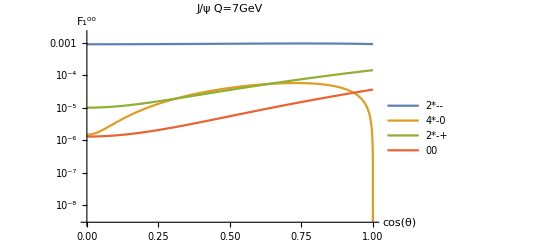
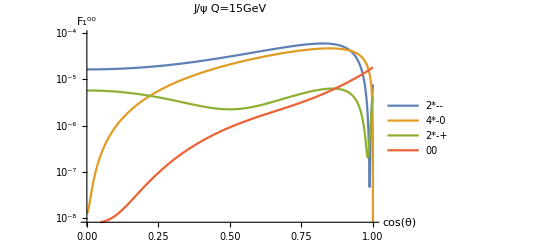
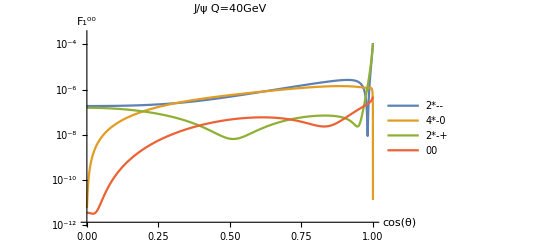

```mathematica
{LogPlot[{2*F1002Jψpolfα[[1]]/.QNum->7,4*F1002Jψpolfα[[2]]/.QNum->7,2*F1002Jψpolfα[[3]]/.QNum->7,F1002Jψpolfα[[5]]/.QNum->7},{cθ,0,1},AxesLabel->{Text[Style["cos(θ)",FontSize->14]],Text[Style["F_1^00",FontSize->14]]},PlotLabel->"J/ψ Q=7GeV",PlotLegends->{"2*--","4*-0","2*-+","00"}],
LogPlot[{2*F1002Jψpolfα[[1]]/.QNum->15,4*F1002Jψpolfα[[2]]/.QNum->15,2*F1002Jψpolfα[[3]]/.QNum->15,F1002Jψpolfα[[5]]/.QNum->15},{cθ,0,1},AxesLabel->{Text[Style["cos(θ)",FontSize->14]],Text[Style["F_1^00",FontSize->14]]},PlotLabel->"J/ψ Q=15GeV",PlotLegends->{"2*--","4*-0","2*-+","00"}],
LogPlot[{2*F1002Jψpolfα[[1]]/.QNum->40,4*F1002Jψpolfα[[2]]/.QNum->40,2*F1002Jψpolfα[[3]]/.QNum->40,F1002Jψpolfα[[5]]/.QNum->40},{cθ,0,1},AxesLabel->{Text[Style["cos(θ)",FontSize->14]],Text[Style["F_1^00",FontSize->14]]},PlotLabel->"J/ψ Q=40GeV",PlotLegends->{"2*--","4*-0","2*-+","00"}]}
```

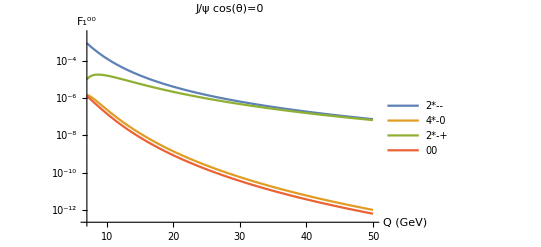
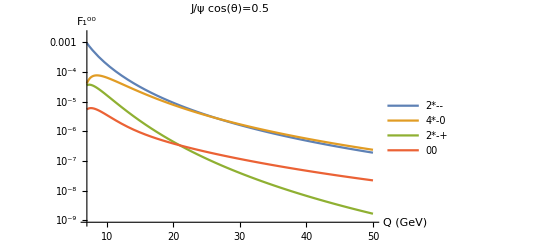
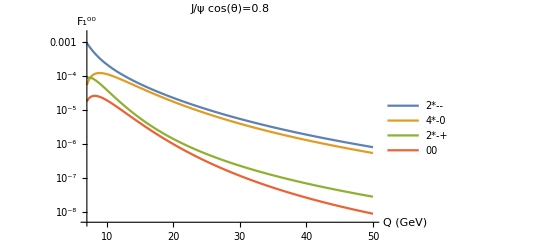

```mathematica
{LogPlot[{2*F1002Jψpolfα[[1]]/.cθ->0,4*F1002Jψpolfα[[2]]/.cθ->0,2*F1002Jψpolfα[[3]]/.cθ->0,F1002Jψpolfα[[5]]/.cθ->0},{QNum,7,50},AxesLabel->{Text[Style["Q (GeV)",FontSize->14]],Text[Style["F_1^00",FontSize->14]]},PlotLabel->"J/ψ cos(θ)=0",PlotLegends->{"2*--","4*-0","2*-+","00"}],
LogPlot[{2*F1002Jψpolfα[[1]]/.cθ->0.5,4*F1002Jψpolfα[[2]]/.cθ->0.5,2*F1002Jψpolfα[[3]]/.cθ->0.5,F1002Jψpolfα[[5]]/.cθ->0.5},{QNum,7,50},AxesLabel->{Text[Style["Q (GeV)",FontSize->14]],Text[Style["F_1^00",FontSize->14]]},PlotLabel->"J/ψ cos(θ)=0.5",PlotLegends->{"2*--","4*-0","2*-+","00"}],
LogPlot[{2*F1002Jψpolfα[[1]]/.cθ->0.8,4*F1002Jψpolfα[[2]]/.cθ->0.8,2*F1002Jψpolfα[[3]]/.cθ->0.8,F1002Jψpolfα[[5]]/.cθ->0.8},{QNum,7,50},AxesLabel->{Text[Style["Q (GeV)",FontSize->14]],Text[Style["F_1^00",FontSize->14]]},PlotLabel->"J/ψ cos(θ)=0.8",PlotLegends->{"2*--","4*-0","2*-+","00"}]}
```

### F_2 term

```mathematica
F202Jψpolfα[[1]]/F202Jψpolfα[[9]]
```

1

```mathematica
F202Jψpolfα[[2]]/F202Jψpolfα[[4]]
```

1

```mathematica
F202Jψpolfα[[2]]/F202Jψpolfα[[8]]
```

1

```mathematica
F202Jψpolfα[[2]]/F202Jψpolfα[[6]]
```

1

```mathematica
F202Jψpolfα[[3]]/F202Jψpolfα[[7]]
```

1

-- = ++
-0 = 0- = 0+ = +0
-+ = +-
00

```mathematica
F202Jψpolfα=F202Jψpolfα/.Repψ;
```

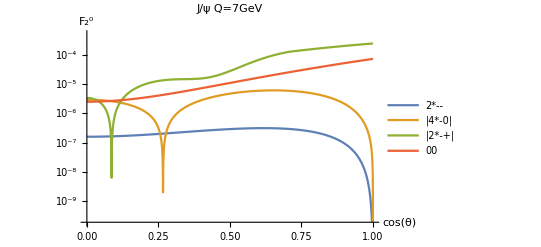
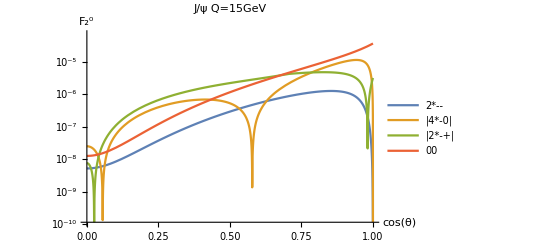
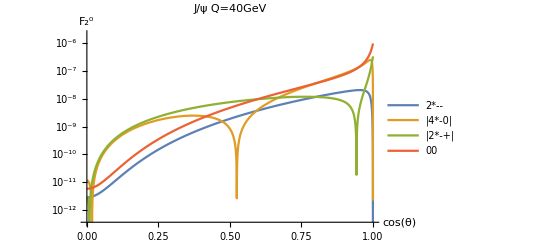

```mathematica
{LogPlot[{2*F202Jψpolfα[[1]]/.QNum->7,Abs[4*F202Jψpolfα[[2]]]/.QNum->7,Abs[2*F202Jψpolfα[[3]]]/.QNum->7,F202Jψpolfα[[5]]/.QNum->7},{cθ,0,1},AxesLabel->{Text[Style["cos(θ)",FontSize->14]],Text[Style["F_2^0",FontSize->14]]},PlotLabel->"J/ψ Q=7GeV",PlotLegends->{"2*--","|4*-0|","|2*-+|","00"}],
LogPlot[{2*F202Jψpolfα[[1]]/.QNum->15,Abs[4*F202Jψpolfα[[2]]]/.QNum->15,Abs[2*F202Jψpolfα[[3]]]/.QNum->15,F202Jψpolfα[[5]]/.QNum->15},{cθ,0,1},AxesLabel->{Text[Style["cos(θ)",FontSize->14]],Text[Style["F_2^0",FontSize->14]]},PlotLabel->"J/ψ Q=15GeV",PlotLegends->{"2*--","|4*-0|","|2*-+|","00"}],
LogPlot[{2*F202Jψpolfα[[1]]/.QNum->40,Abs[4*F202Jψpolfα[[2]]]/.QNum->40,Abs[2*F202Jψpolfα[[3]]]/.QNum->40,F202Jψpolfα[[5]]/.QNum->40},{cθ,0,1},AxesLabel->{Text[Style["cos(θ)",FontSize->14]],Text[Style["F_2^0",FontSize->14]]},PlotLabel->"J/ψ Q=40GeV",PlotLegends->{"2*--","|4*-0|","|2*-+|","00"}]}
```

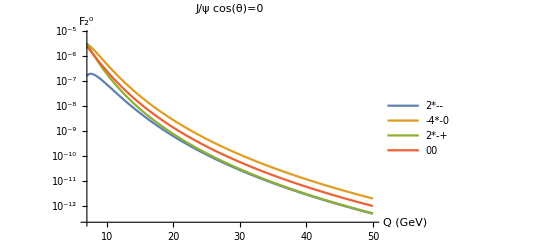
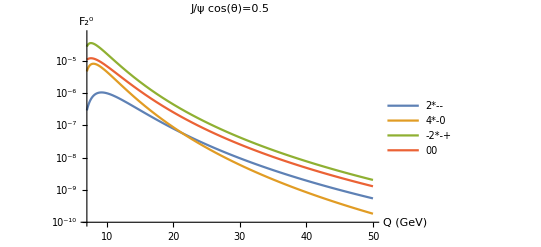
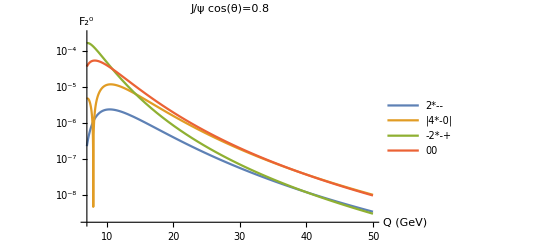

```mathematica
{LogPlot[{2*F202Jψpolfα[[1]]/.cθ->0,-4*F202Jψpolfα[[2]]/.cθ->0,2*F202Jψpolfα[[3]]/.cθ->0,F202Jψpolfα[[5]]/.cθ->0},{QNum,7,50},AxesLabel->{Text[Style["Q (GeV)",FontSize->14]],Text[Style["F_2^0",FontSize->14]]},PlotLabel->"J/ψ cos(θ)=0",PlotLegends->{"2*--","-4*-0","2*-+","00"},PlotRange->All],
LogPlot[{2*F202Jψpolfα[[1]]/.cθ->0.5,4*F202Jψpolfα[[2]]/.cθ->0.5,-2*F202Jψpolfα[[3]]/.cθ->0.5,F202Jψpolfα[[5]]/.cθ->0.5},{QNum,7,50},AxesLabel->{Text[Style["Q (GeV)",FontSize->14]],Text[Style["F_2^0",FontSize->14]]},PlotLabel->"J/ψ cos(θ)=0.5",PlotLegends->{"2*--","4*-0","-2*-+","00"},PlotRange->All],
LogPlot[{2*F202Jψpolfα[[1]]/.cθ->0.8,Abs[4*F202Jψpolfα[[2]]]/.cθ->0.8,-2*F202Jψpolfα[[3]]/.cθ->0.8,F202Jψpolfα[[5]]/.cθ->0.8},{QNum,7,50},AxesLabel->{Text[Style["Q (GeV)",FontSize->14]],Text[Style["F_2^0",FontSize->14]]},PlotLabel->"J/ψ cos(θ)=0.8",PlotLegends->{"2*--","|4*-0|","-2*-+","00"},PlotRange->All]}
```

### F_3 term (unfinished)

```mathematica
F3002Jψapolfα[[1]]/F3002Jψapolfα[[9]]
```

1

```mathematica
F3002Jψapolfα[[2]]+F3002Jψapolfα[[4]]//Simplify
```

-1/(81 s^3 α (1+cθ^2 (-1+α^2))^4)65536 cθ^2 (-1+cθ^2) π^2 R0^4 (-1+α)^2 (1+α) (72-170 α-144 α^2+27 α^3-α^4+648 cθ^10 (-1+α)^5 (1+α)^3-18 cθ^8 (-1+α)^4 (1+α)^2 (-134-20 α+33 α^2)-cθ^6 (-1+α)^3 (-3420-4328 α+1307 α^2+2907 α^3+745 α^4+53 α^5)-cθ^4 (-1+α)^2 (-2268-710 α+3062 α^2+1839 α^3+237 α^4+29 α^5+α^6)+cθ^2 (-684+1232 α+757 α^2-1036 α^3-271 α^4+2 α^6)) αs^4 Cos[2 ϕ]

```mathematica
F3002Jψapolfα[[2]]-F3002Jψapolfα[[4]]//Simplify
```

1/(81 s^3 α (1+cθ^2 (-1+α^2))^4)65536 cθ (-1+cθ^2) π^2 R0^4 (-1+α) √(1-α^2) (162 cθ^8 (-1+α)^4 (1+α)^3+α (-18-10 α+α^2)+27 cθ^6 (-1+α)^3 (1+α)^2 (18+4 α+α^2)+cθ^2 (-162+90 α+99 α^2-25 α^3-2 α^5)+cθ^4 (-1+α)^2 (486+684 α+226 α^2+39 α^3+12 α^4+α^5)) αs^4 Cos[2 ϕ]

```mathematica
F3002Jψapolfα[[2]]/F3002Jψapolfα[[8]]
```

1

```mathematica
F3002Jψapolfα[[2]]/F3002Jψapolfα[[6]]
```

(-162 cθ^8 (1-α)^(9/2) (1+α)^(7/2)+648 cθ^11 (-1+α)^6 (1+α)^4+α (18-(-10+α) α) √(1-α^2)+27 cθ^6 (1-α)^(7/2) (1+α)^(5/2) (18+α (4+α))-18 cθ^9 (-1+α)^5 (1+α)^3 (-134+α (-20+33 α))-cθ (-9+α) (-1+α) (1+α) (8+α (-18+(-18+α) α))-cθ^4 (1-α)^(5/2) (1+α)^(3/2) (486+α (198+α (4+α) (7+α)))+cθ^2 √(1-α^2) (162+α (-90+α (-99+25 α+2 α^3)))-cθ^7 (-1+α)^4 (1+α)^2 (-3420+α (-908+α (2215+α (692+53 α))))+cθ^3 (-1+α)^2 (1+α) (684+α (-548+α (-1305+α (-269+2 α (1+α)))))-cθ^5 (-1+α)^3 (1+α) (-2268+α (-710+α (3062+α (1839+α (237+α (29+α)))))))/(162 cθ^8 (1-α)^(9/2) (1+α)^(7/2)+648 cθ^11 (-1+α)^6 (1+α)^4+α (-18+(-10+α) α) √(1-α^2)-27 cθ^6 (1-α)^(7/2) (1+α)^(5/2) (18+α (4+α))-18 cθ^9 (-1+α)^5 (1+α)^3 (-134+α (-20+33 α))-cθ (-9+α) (-1+α) (1+α) (8+α (-18+(-18+α) α))+cθ^4 (1-α)^(5/2) (1+α)^(3/2) (486+α (198+α (4+α) (7+α)))+cθ^2 √(1-α^2) (-162+α (90+α (99-25 α-2 α^3)))-cθ^7 (-1+α)^4 (1+α)^2 (-3420+α (-908+α (2215+α (692+53 α))))+cθ^3 (-1+α)^2 (1+α) (684+α (-548+α (-1305+α (-269+2 α (1+α)))))-cθ^5 (-1+α)^3 (1+α) (-2268+α (-710+α (3062+α (1839+α (237+α (29+α)))))))

```mathematica
F3002Jψapolfα[[3]]/F3002Jψapolfα[[7]]
```

1

-- = ++
-0 = 0- = 0+ = +0
-+ = +-
00

```mathematica
F3002Jψapolfα=F3002Jψapolfα/.Repψ;
```

```mathematica
{LogPlot[{2*F3002Jψapolfα[[1]]/.QNum->7,4*F3002Jψapolfα[[2]]/.QNum->7,2*F3002Jψapolfα[[3]]/.QNum->7,F3002Jψapolfα[[5]]/.QNum->7},{cθ,0,1},AxesLabel->{Text[Style["cos(θ)",FontSize->14]],Text[Style["F_3^00",FontSize->14]]},PlotLabel->"J/ψ Q=7GeV",PlotLegends->{"2*--","4*-0","2*-+","00"}],
LogPlot[{2*F3002Jψapolfα[[1]]/.QNum->15,4*F3002Jψapolfα[[2]]/.QNum->15,2*F3002Jψapolfα[[3]]/.QNum->15,F3002Jψapolfα[[5]]/.QNum->15},{cθ,0,1},AxesLabel->{Text[Style["cos(θ)",FontSize->14]],Text[Style["F_3^00",FontSize->14]]},PlotLabel->"J/ψ Q=15GeV",PlotLegends->{"2*--","4*-0","2*-+","00"}],
LogPlot[{2*F3002Jψapolfα[[1]]/.QNum->40,4*F3002Jψapolfα[[2]]/.QNum->40,2*F3002Jψapolfα[[3]]/.QNum->40,F3002Jψapolfα[[5]]/.QNum->40},{cθ,0,1},AxesLabel->{Text[Style["cos(θ)",FontSize->14]],Text[Style["F_3^00",FontSize->14]]},PlotLabel->"J/ψ Q=40GeV",PlotLegends->{"2*--","4*-0","2*-+","00"}]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{LogPlot[{2*F3002Jψapolfα[[1]]/.cθ->0,4*F3002Jψapolfα[[2]]/.cθ->0,2*F3002Jψapolfα[[3]]/.cθ->0,F3002Jψapolfα[[5]]/.cθ->0},{QNum,7,50},AxesLabel->{Text[Style["Q (GeV)",FontSize->14]],Text[Style["F_3^00",FontSize->14]]},PlotLabel->"J/ψ cos(θ)=0",PlotLegends->{"2*--","4*-0","2*-+","00"}],
LogPlot[{2*F3002Jψapolfα[[1]]/.cθ->0.5,4*F3002Jψapolfα[[2]]/.cθ->0.5,2*F3002Jψapolfα[[3]]/.cθ->0.5,F3002Jψapolfα[[5]]/.cθ->0.5},{QNum,7,50},AxesLabel->{Text[Style["Q (GeV)",FontSize->14]],Text[Style["F_3^00",FontSize->14]]},PlotLabel->"J/ψ cos(θ)=0.5",PlotLegends->{"2*--","4*-0","2*-+","00"}],
LogPlot[{2*F3002Jψapolfα[[1]]/.cθ->0.8,4*F3002Jψapolfα[[2]]/.cθ->0.8,2*F3002Jψapolfα[[3]]/.cθ->0.8,F3002Jψapolfα[[5]]/.cθ->0.8},{QNum,7,50},AxesLabel->{Text[Style["Q (GeV)",FontSize->14]],Text[Style["F_3^00",FontSize->14]]},PlotLabel->"J/ψ cos(θ)=0.8",PlotLegends->{"2*--","4*-0","2*-+","00"}]}
```

{-Graphics-,-Graphics-,-Graphics-}

## Massless J/ψJ/ψ VS γγ

```mathematica
tγγ=-sγγ/2(1-Cos[θ]);
uγγ=-sγγ/2(1+Cos[θ]);
```

```mathematica
L[x_,y_]:= 1-(x-y)/(x+y)(Log[Abs[x/y]]-ⅈ π θ (-x/y))+1/2(x^2+y^2)/(x+y)^2(π^2+(Log[Abs[x/y]]-ⅈ π θ (-x/y))^2);
```

```mathematica
fs=L[tγγ,uγγ]
ft=L[sγγ,uγγ]
fu=L[sγγ,tγγ]
```

1-((-1/2 sγγ (1-Cos[θ])+1/2 sγγ (1+Cos[θ])) ((ⅈ π θ (1-Cos[θ]))/(1+Cos[θ])+Log[Abs[(1-Cos[θ])/(1+Cos[θ])]]))/(-1/2 sγγ (1-Cos[θ])-1/2 sγγ (1+Cos[θ]))+((1/4 sγγ^2 (1-Cos[θ])^2+1/4 sγγ^2 (1+Cos[θ])^2) (π^2+((ⅈ π θ (1-Cos[θ]))/(1+Cos[θ])+Log[Abs[(1-Cos[θ])/(1+Cos[θ])]])^2))/(2 (-1/2 sγγ (1-Cos[θ])-1/2 sγγ (1+Cos[θ]))^2)

1-((sγγ+1/2 sγγ (1+Cos[θ])) (-(2 ⅈ π θ)/(1+Cos[θ])+Log[2/Abs[1+Cos[θ]]]))/(sγγ-1/2 sγγ (1+Cos[θ]))+((sγγ^2+1/4 sγγ^2 (1+Cos[θ])^2) (π^2+(-(2 ⅈ π θ)/(1+Cos[θ])+Log[2/Abs[1+Cos[θ]]])^2))/(2 (sγγ-1/2 sγγ (1+Cos[θ]))^2)

1-((sγγ+1/2 sγγ (1-Cos[θ])) (-(2 ⅈ π θ)/(1-Cos[θ])+Log[2/Abs[1-Cos[θ]]]))/(sγγ-1/2 sγγ (1-Cos[θ]))+((sγγ^2+1/4 sγγ^2 (1-Cos[θ])^2) (π^2+(-(2 ⅈ π θ)/(1-Cos[θ])+Log[2/Abs[1-Cos[θ]]])^2))/(2 (sγγ-1/2 sγγ (1-Cos[θ]))^2)

```mathematica
F1γγ=fs^2+(Abs[ft])^2+(Abs[fu])^2+5 //Simplify;
```

```mathematica
F2γγ=2(fs-1)//Simplify;
```

```mathematica
F3γγ=fs+Re[fu+ft]-1//Simplify;
```

```mathematica
F4γγ=fu ft* + ft fu*+2//Simplify;
```

```mathematica
Limit[F1γγ,θ->0]
```

∞

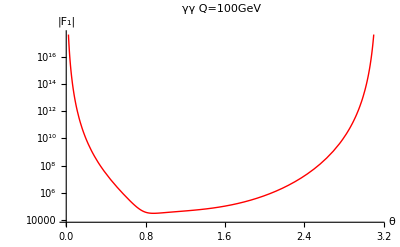

```mathematica
QNum=100;
LogPlot[Abs[F1γγ],{θ,0,π},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["|F_1|",FontSize->14]]},PlotLabel->"γγ Q="<>ToString[QNum]<>"GeV"]
```

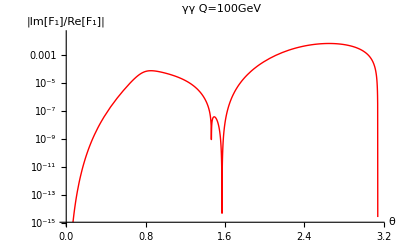

```mathematica
QNum=100;
LogPlot[Abs[Im[F1γγ]/Re[F1γγ]],{θ,0,π},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["|Im[F_1]/Re[F_1]|",FontSize->14]]},PlotLabel->"γγ Q="<>ToString[QNum]<>"GeV"]
```

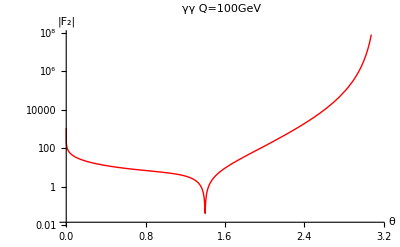

```mathematica
QNum=100;
LogPlot[Abs[F2γγ],{θ,0,π},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["|F_2|",FontSize->14]]},PlotLabel->"γγ Q="<>ToString[QNum]<>"GeV"]
```

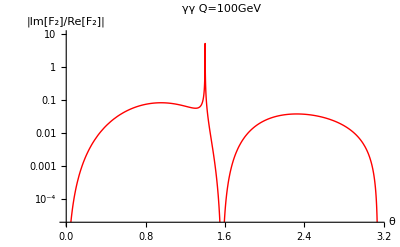

```mathematica
QNum=100;
LogPlot[Abs[Im[F2γγ]/Re[F2γγ]],{θ,0,π},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["|Im[F_2]/Re[F_2]|",FontSize->14]]},PlotLabel->"γγ Q="<>ToString[QNum]<>"GeV"]
```

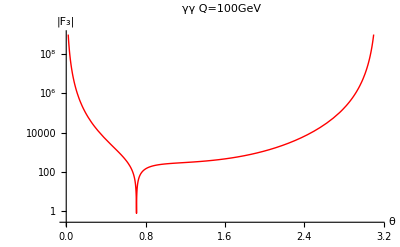

```mathematica
QNum=100;
LogPlot[Abs[F3γγ],{θ,0,π},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["|F_3|",FontSize->14]]},PlotLabel->"γγ Q="<>ToString[QNum]<>"GeV"]
```

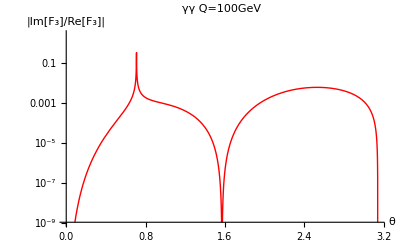

```mathematica
QNum=100;
LogPlot[Abs[Im[F3γγ]/Re[F3γγ]],{θ,0,π},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["|Im[F_3]/Re[F_3]|",FontSize->14]]},PlotLabel->"γγ Q="<>ToString[QNum]<>"GeV"]
```

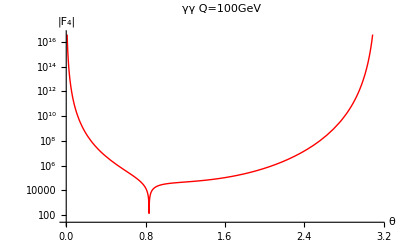

```mathematica
QNum=100;
LogPlot[Abs[F4γγ],{θ,0,π},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["|F_4|",FontSize->14]]},PlotLabel->"γγ Q="<>ToString[QNum]<>"GeV"]
```

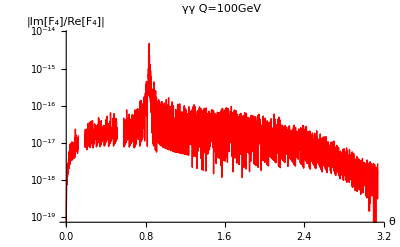

```mathematica
QNum=100;
LogPlot[(Abs[Im[(F4γγ)]/Re[(F4γγ)]]/.{sγγ->QNum^2,cθ->Cos[θ]}),{θ,0,π},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["|Im[F_4]/Re[F_4]|",FontSize->14]]},PlotLabel->"γγ Q="<>ToString[QNum]<>"GeV"]
```

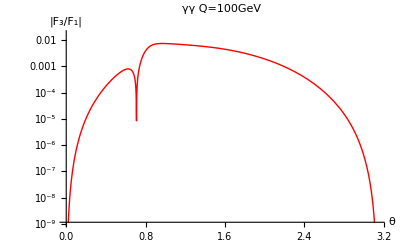

```mathematica
QNum=100;
LogPlot[Abs[F3γγ/F1γγ],{θ,0,π},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["|F_3/F_1|",FontSize->14]]},PlotLabel->"γγ Q="<>ToString[QNum]<>"GeV"]
```

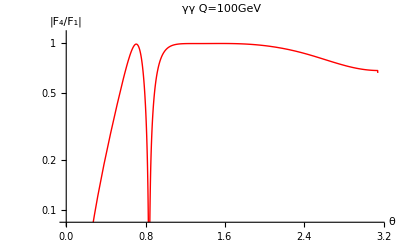

```mathematica
QNum=100;
LogPlot[Abs[F4γγ/F1γγ],{θ,0,π},PlotStyle->{Red,Thick},AxesLabel->{Text[Style["θ",FontSize->14]],Text[Style["|F_4/F_1|",FontSize->14]]},PlotLabel->"γγ Q="<>ToString[QNum]<>"GeV"]
```

## Limits

```mathematica
<<"~/Bureau/notebooks/kernel_saves/JpsiJpsi/TMD/gg2DoubleJpsi_Schlegel_v070715_helicity_amplitudes"
```

α → 1 (threshold limit)

```mathematica
F1002Jψα/.α->1
```

(6447104 π^2 R0^4 αs^4)/(81 s^3)

```mathematica
F1112Jψα/.α->1
```

-(6397952 π^2 R0^4 αs^4)/(81 s^3)

```mathematica
F202Jψα/.α->1
```

(8192 π^2 R0^4 αs^4)/(27 s^3)

```mathematica
F3002Jψaα/.α->1
```

0

```mathematica
F402Jψα/.α->1
```

0

```mathematica
F202Jψα/F1002Jψα/.α->1
```

3/787

```mathematica
F202Jψα/(F1002Jψα+F1112Jψα)/.α->1
```

1/2

α → 0 (large Q limit)

```mathematica
Series[F1002Jψα,{α,0,-1}]
```

(131072 (16+90 cθ^2+243 cθ^4) π^2 R0^4 αs^4)/(81 s^3 α^2)+O[α]^0

```mathematica
Series[F1112Jψα,{α,0,-1}]
```

-(131072 ((16+90 cθ^2+243 cθ^4) π^2 R0^4 αs^4))/(81 s^3 α^2)+O[α]^0

```mathematica
F202Jψα/.α->0
```

0

```mathematica
F3002Jψaα/.α->0/.ϕ->0
```

-(16384 (-1+cθ^2) (-1584 cθ^2+5112 cθ^4-5472 cθ^6+1944 cθ^8) π^2 R0^4 αs^4)/(81 (1-cθ^2)^4 s^3)

```mathematica
Series[F402Jψα,{α,0,-1}]/.ϕ->0
```

(131072 (16-234 cθ^2+243 cθ^4) π^2 R0^4 αs^4)/(81 s^3 α^2)+O[α]^0

```mathematica
F202Jψα/F1002Jψα/.α->0
```

0

```mathematica
Series[F202Jψα/(F1002Jψα+F1112Jψα),{α,0,2}]/.ϕ->0
```

((2-3 cθ^2) α^2)/(8 (-1+cθ^2))+O[α]^3

α → 0 (large Q limit) & cos(θ)→0

```mathematica
Series[F1002Jψα,{α,0,-1}]/.cθ->0
```

(2097152 π^2 R0^4 αs^4)/(81 s^3 α^2)+O[α]^0

```mathematica
Series[F1112Jψα,{α,0,-1}]/.cθ->0
```

-(2097152 (π^2 R0^4 αs^4))/(81 s^3 α^2)+O[α]^0

```mathematica
Series[F202Jψα,{α,0,2},{cθ,0,2}]
```

(-(65536 (π^2 R0^4 αs^4) cθ^2)/s^3+O[cθ]^3) α^2+O[α]^3

```mathematica
Series[F3002Jψaα/.α->0/.ϕ->0,{cθ,0,2}]
```

-(2883584 (π^2 R0^4 αs^4) cθ^2)/(9 s^3)+O[cθ]^3

```mathematica
Series[F402Jψα,{α,0,-1}]/.ϕ->0/.cθ->0
```

(2097152 π^2 R0^4 αs^4)/(81 s^3 α^2)+O[α]^0

```mathematica
F202Jψα/F1002Jψα/.α->0/.cθ->0
```

0

```mathematica
Series[F202Jψα/(F1002Jψα+F1112Jψα),{α,0,2}]/.ϕ->0/.cθ->0
```

-α^2/4+O[α]^3

## Other stuff

```mathematica
pdfpath="~/Dropbox/Work/MSTW/";
SetDirectory[pdfpath];
```

```mathematica
<<mstwpdf.m
```

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

```mathematica
prefix=pdfpath<>"Grids/mstw2008nlo";
Timing[ReadPDFGrid[prefix,0]]
```

PDF grid read from ~/Dropbox/Work/MSTW/Grids/mstw2008nlo.00.dat

{12.53292,Null}

```mathematica
?xf
```

The function xf[ih,x,q,f] returns x times the parton distribution of flavour f corresponding to eigenvector set ih, where ih=0 is the central set, at a given momentum fraction x and scale q in GeV.  Note that ih and f must be integers, and x and q must be numeric quantities.  The PDG convention is used for the flavour f (apart from the gluon has f=0, not 21), that is, f = -6, -5, -4, -3, -2, -1, 0, 1, 2, 3, 4, 5, 6 corresponds to tbar, bbar, cbar, sbar, ubar, dbar, g, d, u, s, c, b, t.  The valence quark distributions can also be obtained directly with f = 7, 8, 9, 10, 11, 12 corresponding to dv, uv, sv, cv, bv, tv.  The photon distribution is obtained with f = 13.

```mathematica
Drop[Import["~/Dropbox/Work/JPsi/JPsi/cauniglu-2.0/src/ccfm-final-setA0.dat"],3];
{#1[[1;;3]],#1[[4]]}&/@%;
xgSetA=Interpolation[%];
```

```mathematica
Drop[Import["~/Dropbox/Work/JPsi/JPsi/cauniglu-2.0/src/ccfm-final-setB0.dat"],4];
{#1[[1;;3]],#1[[4]]}&/@%;
xgSetB=Interpolation[%];
```

```mathematica
Drop[Import["~/Dropbox/Work/JPsi/JPsi/cauniglu-2.0/src/ccfm-ipgg0ns-1-0-all-lhc.dat"],3];
{#1[[1;;3]],#1[[4]]}&/@%;
xgSet1=Interpolation[%];
```

```mathematica
Drop[Import["~/Dropbox/Work/JPsi/JPsi/cauniglu-2.0/src/ccfm-ipgg1ns1-0-all-lhc.dat"],3];
{#1[[1;;3]],#1[[4]]}&/@%;
xgSet2=Interpolation[%];
```

```mathematica
Drop[Import["~/Dropbox/Work/JPsi/JPsi/cauniglu-2.0/src/ccfm-ipgg2ns2-0-all-lhc.dat"],3];
{#1[[1;;3]],#1[[4]]}&/@%;
xgSet3=Interpolation[%];
```

```mathematica
Drop[Import["~/Dropbox/Work/JPsi/JPsi/cauniglu-2.0/src/kmr.dat"],2];
{#1[[1;;3]],#1[[4]]}&/@%;
DeleteDuplicates[%];
xgKMR=Interpolation[%];
```

```mathematica
Drop[Import["~/Dropbox/Work/JPsi/JPsi/cauniglu-2.0/src/kms.dat"],1];
{#1[[1;;2]],#1[[3]]}&/@%;
DeleteDuplicates[%];
xgKMS=Interpolation[%];
```

Usage: xgSetA[Log[x],Log[kT^2],Log[Q]]
gives you  π*x*kT^2*f1g(x,kT,Q)
at least that's what approximately corresponds to what it should be (I never found any clear documentation about these UGDs for Cascade)

and likewise for the other sets.

### Example :

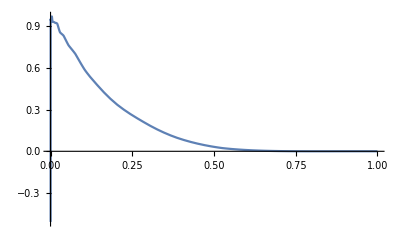

```mathematica
Plot[xgSetA[Log[x],Log[1],Log[10]],{x,0,1}]
```

InterpolatingFunction::dmval: Input value TraditionalForm`{-4.60517, -9.16993, log(10)} lies outside the range of data in the interpolating function. Extrapolation will be used.

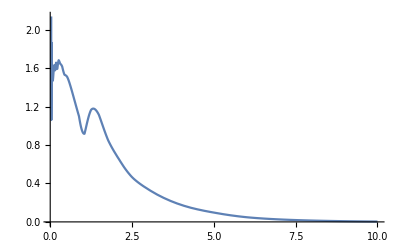

```mathematica
Plot[1/kT^2*xgSetA[Log[0.01],Log[kT^2],Log[10]],{kT,0.01,10}]
```

Damping factor:

```mathematica
Damp[kT2_]:=kT2^3/(10^(-6)+kT2^3)
```

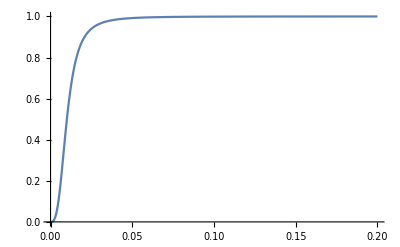

```mathematica
Plot[Damp[kT2],{kT2,0,0.2},PlotRange->All]
```

Model Ansätze for the unpolarized gluon TMD = UGD

```mathematica
f1gSetA[x_,kT2_,Q_]:=Damp[kT2]/π/x/kT2 xgSetA[Log[x],Log[kT2],Log[Q]]
f1gSetB[x_,kT2_,Q_]:=Damp[kT2]/π/x/kT2 xgSetB[Log[x],Log[kT2],Log[Q]]
f1gSet1[x_,kT2_,Q_]:=Damp[kT2]/π/x/kT2 xgSet1[Log[x],Log[kT2],Log[Q]]
f1gSet2[x_,kT2_,Q_]:=Damp[kT2]/π/x/kT2 xgSet2[Log[x],Log[kT2],Log[Q]]
f1gSet3[x_,kT2_,Q_]:=Damp[kT2]/π/x/kT2 xgSet3[Log[x],Log[kT2],Log[Q]]
f1gKMR[x_,kT2_,Q_]:=Damp[kT2]/π/x/kT2 xgKMR[Log[x],Log[kT2],Log[Q]]
f1gKMS[x_,kT2_,Q_]:=Damp[kT2]/π/x/kT2 xgKMS[Log[x],Log[kT2],Log[Q]]
```

```mathematica
f1gKMR[0.01,4,100]
```

1.78044

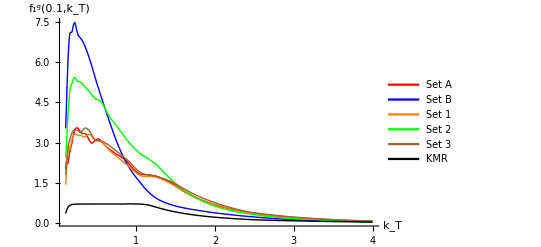

```mathematica
Plot[{f1gSetA[0.1,kT^2,10],f1gSetB[0.1,kT^2,10],f1gSet1[0.1,kT^2,10],f1gSet2[0.1,kT^2,10],f1gSet3[0.1,kT^2,10],f1gKMR[0.1,kT^2,10]},{kT,0.1,4},PlotStyle->{{Red,Thick},{Blue,Thick},{Orange,Thick},{Green,Thick},{Brown,Thick},{Black,Thick}},AxesLabel->{Text[Style["k_T",FontSize->14]],Text[Style["f_1^g(0.1,k_T)",FontSize->14]]},PlotLegends->Placed[{"Set A","Set B","Set 1","Set 2","Set 3","KMR"},{0.75,0.5}],TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
f1g[x_,Q_]:=xf[0,x,Q,0]/x
```

```mathematica
NIntegrate[2 π kT f1gKMR[20/14000,kT^2,20],{kT,0,20},PrecisionGoal->4]
```

14332.7

```mathematica
ReplConv={kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2};
```

Convolution C[f_1 f_1]:

```mathematica
C1SetA[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT f1gSetA[Q/sS Exp[Y],kT^2,Q] f1gSetA[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C1SetB[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT f1gSetB[Q/sS Exp[Y],kT^2,Q] f1gSetB[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C1Set1[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT f1gSet1[Q/sS Exp[Y],kT^2,Q] f1gSet1[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C1Set2[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT f1gSet2[Q/sS Exp[Y],kT^2,Q] f1gSet2[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C1Set3[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT f1gSet3[Q/sS Exp[Y],kT^2,Q] f1gSet3[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C1KMR[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT f1gKMR[Q/sS Exp[Y],kT^2,Q] f1gKMR[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
```

```mathematica
Timing[Nstep=30;sSN=115;QN=10;YN=-2;ϕqN=0;
PlotqTC1SetA=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC1SetA[[i,1]]=qTNum;PlotqTC1SetA[[i,2]]=C1SetA[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=115;QN=10;YN=-2;ϕqN=0;
PlotqTC1SetB=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC1SetB[[i,1]]=qTNum;PlotqTC1SetB[[i,2]]=C1SetB[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=115;QN=10;YN=-2;ϕqN=0;
PlotqTC1Set1=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC1Set1[[i,1]]=qTNum;PlotqTC1Set1[[i,2]]=C1Set1[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=115;QN=10;YN=-2;ϕqN=0;
PlotqTC1Set2=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC1Set2[[i,1]]=qTNum;PlotqTC1Set2[[i,2]]=C1Set2[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=115;QN=10;YN=-2;ϕqN=0;
PlotqTC1Set3=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC1Set3[[i,1]]=qTNum;PlotqTC1Set3[[i,2]]=C1Set3[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=115;QN=10;YN=-2;ϕqN=0;
PlotqTC1KMR=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC1KMR[[i,1]]=qTNum;PlotqTC1KMR[[i,2]]=C1KMR[sSN,YN,qTNum,ϕqN,QN];]]
```

{448.26,Null}

{439.837,Null}

{424.663,Null}

{369.951,Null}

{520.725,Null}

{333.99,Null}

```mathematica
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC1SetAZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC1SetAZ[[i,1]]=qTNum;PlotqTC1SetAZ[[i,2]]=C1SetA[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC1SetBZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC1SetBZ[[i,1]]=qTNum;PlotqTC1SetBZ[[i,2]]=C1SetB[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC1Set1Z=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC1Set1Z[[i,1]]=qTNum;PlotqTC1Set1Z[[i,2]]=C1Set1[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC1Set2Z=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC1Set2Z[[i,1]]=qTNum;PlotqTC1Set2Z[[i,2]]=C1Set2[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC1Set3Z=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC1Set3Z[[i,1]]=qTNum;PlotqTC1Set3Z[[i,2]]=C1Set3[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC1KMRZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC1KMRZ[[i,1]]=qTNum;PlotqTC1KMRZ[[i,2]]=C1KMR[sSN,YN,qTNum,ϕqN,QN];]]
```

{657.329,Null}

{678.345,Null}

{1562.09,Null}

{609.592,Null}

{1429.34,Null}

{489.001,Null}

```mathematica
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC1SetBZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC1SetBZ[[i,1]]=qTNum;PlotqTC1SetBZ[[i,2]]=C1SetB[sSN,YN,qTNum,ϕqN,QN];]]

Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC1KMRZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC1KMRZ[[i,1]]=qTNum;PlotqTC1KMRZ[[i,2]]=C1KMR[sSN,YN,qTNum,ϕqN,QN];]]
```

{687.25324,Null}

{506.2869,Null}

```mathematica
Timing[Nstep=60;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC1SetBγ20=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC1SetBγ20[[i,1]]=qTNum;PlotqTC1SetBγ20[[i,2]]=C1SetB[sSN,YN,qTNum,ϕqN,QN];]]

Timing[Nstep=60;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC1KMRγ20=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC1KMRγ20[[i,1]]=qTNum;PlotqTC1KMRγ20[[i,2]]=C1KMR[sSN,YN,qTNum,ϕqN,QN];]]
```

{431.93626,Null}

{363.36246,Null}

```mathematica
Timing[Nstep=60;sSN=14000;QN=40;YN=0;ϕqN=0;
PlotqTC1SetBγ40=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC1SetBγ40[[i,1]]=qTNum;PlotqTC1SetBγ40[[i,2]]=C1SetB[sSN,YN,qTNum,ϕqN,QN];]]

Timing[Nstep=60;sSN=14000;QN=40;YN=0;ϕqN=0;
PlotqTC1KMRγ40=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC1KMRγ40[[i,1]]=qTNum;PlotqTC1KMRγ40[[i,2]]=C1KMR[sSN,YN,qTNum,ϕqN,QN];]]
```

{451.80849,Null}

{419.82223,Null}

```mathematica
NormSetAgamma[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT f1gSetA[Q/sS Exp[Y],kT^2,Q] f1gSetA[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q/2},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormSetBgamma[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT f1gSetB[Q/sS Exp[Y],kT^2,Q] f1gSetB[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q/2},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormSet1gamma[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT f1gSet1[Q/sS Exp[Y],kT^2,Q] f1gSet1[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q/2},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormSet2gamma[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT f1gSet2[Q/sS Exp[Y],kT^2,Q] f1gSet2[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q/2},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormSet3gamma[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT f1gSet3[Q/sS Exp[Y],kT^2,Q] f1gSet3[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q/2},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormKMRgamma[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT f1gKMR[Q/sS Exp[Y],kT^2,Q] f1gKMR[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q/2},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
```

```mathematica
PlotNormSetAgamma=NormSetAgamma[115,-2,10];
PlotNormSetBgamma=NormSetBgamma[115,-2,10];
PlotNormSet1gamma=NormSet1gamma[115,-2,10];
PlotNormSet2gamma=NormSet2gamma[115,-2,10];
PlotNormSet3gamma=NormSet3gamma[115,-2,10];
PlotNormKMRgamma=NormKMRgamma[115,-2,10];
```

```mathematica
PlotNormSetAZ=NormSetAgamma[14000,0,120];
PlotNormSetBZ=NormSetBgamma[14000,0,120];
PlotNormSet1Z=NormSet1gamma[14000,0,120];
PlotNormSet2Z=NormSet2gamma[14000,0,120];
PlotNormSet3Z=NormSet3gamma[14000,0,120];
PlotNormKMRZ=NormKMRgamma[14000,0,120];
```

```mathematica
PlotNormSetBZ=NormSetBgamma[14000,0,120];
PlotNormKMRZ=NormKMRgamma[14000,0,120];
```

```mathematica
PlotNormSetBγ20=NormSetBgamma[14000,0,20];
PlotNormKMRγ20=NormKMRgamma[14000,0,20];
```

```mathematica
PlotNormSetBγ40=NormSetBgamma[14000,0,40];
PlotNormKMRγ40=NormKMRgamma[14000,0,40];
```

```mathematica
Nstep=60;
PlotqTS0SetBZ=ConstantArray[0,{Nstep,2}];
PlotqTS0KMRZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTS0SetBZ[[i,1]]=PlotqTC1SetBZ[[i,1]];PlotqTS0SetBZ[[i,2]]=π PlotqTC1SetBZ[[i,2]]/PlotNormSetBZ;
PlotqTS0KMRZ[[i,1]]=PlotqTC1KMRZ[[i,1]];PlotqTS0KMRZ[[i,2]]=π PlotqTC1KMRZ[[i,2]]/PlotNormKMRZ;
]
```

```mathematica
Nstep=60;
PlotqTS0SetBγ20=ConstantArray[0,{Nstep,2}];
PlotqTS0KMRγ20=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTS0SetBγ20[[i,1]]=PlotqTC1SetBγ20[[i,1]];PlotqTS0SetBγ20[[i,2]]=π PlotqTC1SetBγ20[[i,2]]/PlotNormSetBγ20;
PlotqTS0KMRγ20[[i,1]]=PlotqTC1KMRγ20[[i,1]];PlotqTS0KMRγ20[[i,2]]=π PlotqTC1KMRγ20[[i,2]]/PlotNormKMRγ20;
]
```

```mathematica
Nstep=60;
PlotqTS0SetBγ40=ConstantArray[0,{Nstep,2}];
PlotqTS0KMRγ40=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTS0SetBγ40[[i,1]]=PlotqTC1SetBγ40[[i,1]];PlotqTS0SetBγ40[[i,2]]=π PlotqTC1SetBγ40[[i,2]]/PlotNormSetBγ40;
PlotqTS0KMRγ40[[i,1]]=PlotqTC1KMRγ40[[i,1]];PlotqTS0KMRγ40[[i,2]]=π PlotqTC1KMRγ40[[i,2]]/PlotNormKMRγ40;
]
```

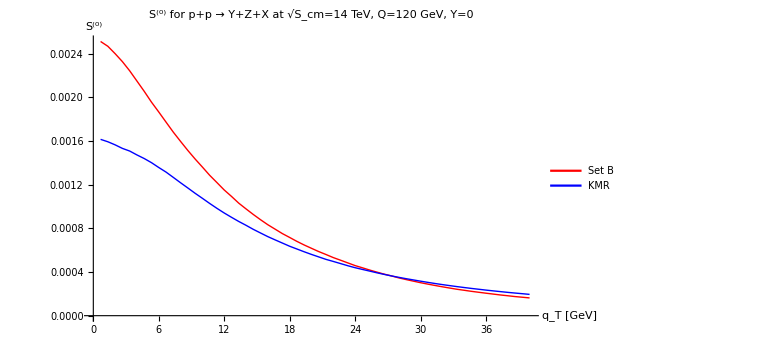

```mathematica
ListPlot[{PlotqTS0SetBZ,PlotqTS0KMRZ},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLabel->Text[Style["S^(0) for p+p → Υ+Z+X at √S_cm=14 TeV, Q=120 GeV, Y=0",FontSize->14]],AxesLabel->{Text[Style["q_T [GeV]",FontSize->14]],Text[Style["S^(0)",FontSize->14]]},PlotLegends->Placed[{"Set B","KMR"},{0.75,0.75}],TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

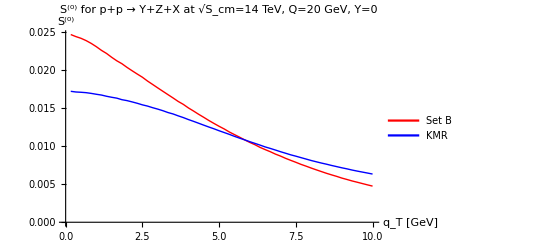

```mathematica
ListPlot[{PlotqTS0SetBγ,PlotqTS0KMRγ},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLabel->Text[Style["S^(0) for p+p → Υ+Z+X at √S_cm=14 TeV, Q=20 GeV, Y=0",FontSize->14]],AxesLabel->{Text[Style["q_T [GeV]",FontSize->14]],Text[Style["S^(0)",FontSize->14]]},PlotLegends->Placed[{"Set B","KMR"},{0.75,0.75}],TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

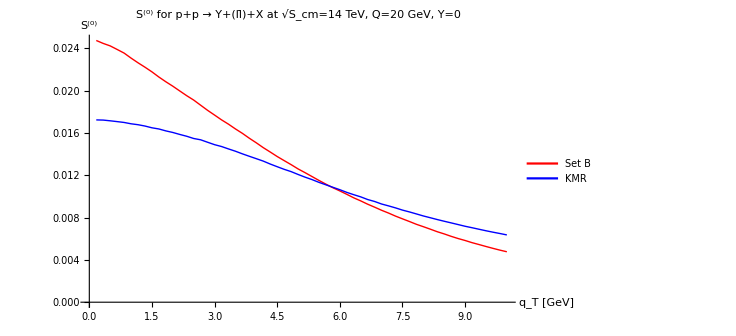

```mathematica
ListPlot[{PlotqTS0SetBγ20,PlotqTS0KMRγ20},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLabel->Text[Style["S^(0) for p+p → Υ+(ll̄)+X at √S_cm=14 TeV, Q=20 GeV, Y=0",FontSize->14]],AxesLabel->{Text[Style["q_T [GeV]",FontSize->14]],Text[Style["S^(0)",FontSize->14]]},PlotLegends->Placed[{"Set B","KMR"},{0.75,0.75}],TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

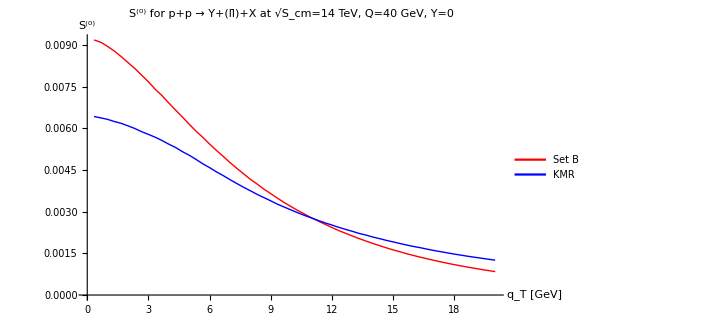

```mathematica
ListPlot[{PlotqTS0SetBγ40,PlotqTS0KMRγ40},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLabel->Text[Style["S^(0) for p+p → Υ+(ll̄)+X at √S_cm=14 TeV, Q=40 GeV, Y=0",FontSize->14]],AxesLabel->{Text[Style["q_T [GeV]",FontSize->14]],Text[Style["S^(0)",FontSize->14]]},PlotLegends->Placed[{"Set B","KMR"},{0.75,0.75}],TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
PlotNormSetAgamma/f1g[20/14000,20]^2
PlotNormSetBgamma/f1g[20/14000,20]^2
PlotNormSet1gamma/f1g[20/14000,20]^2
PlotNormSet2gamma/f1g[20/14000,20]^2
PlotNormSet3gamma/f1g[20/14000,20]^2
PlotNormKMRgamma/f1g[20/14000,20]^2
```

1.74595

1.44547

1.69169

0.809494

1.66372

1.23153

```mathematica
Nstep=30;
PlotqTS0SetAgamma=ConstantArray[0,{Nstep,2}];
PlotqTS0SetBgamma=ConstantArray[0,{Nstep,2}];
PlotqTS0Set1gamma=ConstantArray[0,{Nstep,2}];
PlotqTS0Set2gamma=ConstantArray[0,{Nstep,2}];
PlotqTS0Set3gamma=ConstantArray[0,{Nstep,2}];
PlotqTS0KMRgamma=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTS0SetAgamma[[i,1]]=PlotqTC1SetA[[i,1]];PlotqTS0SetAgamma[[i,2]]=π PlotqTC1SetA[[i,2]]/PlotNormSetAgamma;
PlotqTS0SetBgamma[[i,1]]=PlotqTC1SetB[[i,1]];PlotqTS0SetBgamma[[i,2]]=π PlotqTC1SetB[[i,2]]/PlotNormSetBgamma;
PlotqTS0Set1gamma[[i,1]]=PlotqTC1Set1[[i,1]];PlotqTS0Set1gamma[[i,2]]=π PlotqTC1Set1[[i,2]]/PlotNormSet1gamma;
PlotqTS0Set2gamma[[i,1]]=PlotqTC1Set2[[i,1]];PlotqTS0Set2gamma[[i,2]]=π PlotqTC1Set2[[i,2]]/PlotNormSet2gamma;
PlotqTS0Set3gamma[[i,1]]=PlotqTC1Set3[[i,1]];PlotqTS0Set3gamma[[i,2]]=π PlotqTC1Set3[[i,2]]/PlotNormSet3gamma;
PlotqTS0KMRgamma[[i,1]]=PlotqTC1KMR[[i,1]];PlotqTS0KMRgamma[[i,2]]=π PlotqTC1KMR[[i,2]]/PlotNormKMRgamma;]
```

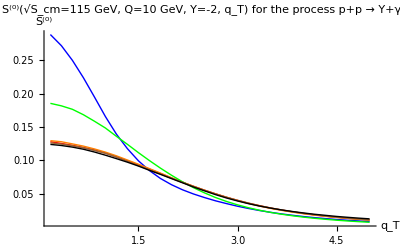

```mathematica
ListPlot[{PlotqTS0SetAgamma,PlotqTS0SetBgamma,PlotqTS0Set1gamma,PlotqTS0Set2gamma,PlotqTS0Set3gamma,PlotqTS0KMRgamma},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick},{Orange,Thick},{Green,Thick},{Brown,Thick},{Black,Thick}},PlotLabel->Text[Style["S^(0)(√S_cm=115 GeV, Q=10 GeV, Y=-2, q_T) for the process p+p → Υ+γ+X",FontSize->14]],AxesLabel->{Text[Style["q_T",FontSize->14]],Text[Style["S^(0)",FontSize->14]]},PlotLegend->{"Set A","Set B","Set 1","Set 2","Set 3","KMR"},LegendPosition->{1.1,-0.4},TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

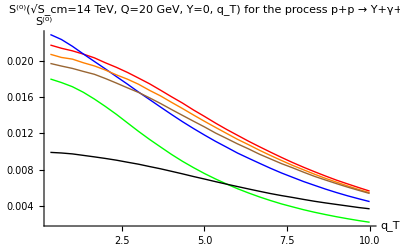

```mathematica
ListPlot[{PlotqTS0SetAgamma,PlotqTS0SetBgamma,PlotqTS0Set1gamma,PlotqTS0Set2gamma,PlotqTS0Set3gamma,PlotqTS0KMRgamma},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick},{Orange,Thick},{Green,Thick},{Brown,Thick},{Black,Thick}},PlotLabel->Text[Style["S^(0)(√S_cm=14 TeV, Q=20 GeV, Y=0, q_T) for the process p+p → Υ+γ+X",FontSize->14]],AxesLabel->{Text[Style["q_T",FontSize->14]],Text[Style["S^(0)",FontSize->14]]},PlotLegend->{"Set A","Set B","Set 1","Set 2","Set 3","KMR"},LegendPosition->{1.1,-0.4},TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotqTC1SetA,PlotqTC1SetB,PlotqTC1Set1,PlotqTC1Set2,PlotqTC1Set3,PlotqTC1KMR}]
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotNormSetAgamma,PlotNormSetBgamma,PlotNormSet1gamma,PlotNormSet2gamma,PlotNormSet3gamma,PlotNormKMRgamma}]
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotqTS0SetAgamma,PlotqTS0SetBgamma,PlotqTS0Set1gamma,PlotqTS0Set2gamma,PlotqTS0Set3gamma,PlotqTS0KMRgamma}]
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotqTC1SetAZ,PlotqTC1SetBZ,PlotqTC1Set1Z,PlotqTC1Set2Z,PlotqTC1Set3Z,PlotqTC1KMRZ}]
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotNormSetAZ,PlotNormSetBZ,PlotNormSet1Z,PlotNormSet2Z,PlotNormSet3Z,PlotNormKMRZ}]
```

Convolution C[w_2 h_1 h_1]:

```mathematica
C2SetA[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)+4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gSetA[Q/sS Exp[Y],kT^2,Q] f1gSetA[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C2SetB[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)+4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gSetB[Q/sS Exp[Y],kT^2,Q] f1gSetB[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C2Set1[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)+4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gSet1[Q/sS Exp[Y],kT^2,Q] f1gSet1[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C2Set2[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)+4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gSet2[Q/sS Exp[Y],kT^2,Q] f1gSet2[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C2Set3[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)+4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gSet3[Q/sS Exp[Y],kT^2,Q] f1gSet3[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C2KMR[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)+4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gKMR[Q/sS Exp[Y],kT^2,Q] f1gKMR[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
```

```mathematica
Timing[Nstep=30;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC2SetA=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC2SetA[[i,1]]=qTNum;PlotqTC2SetA[[i,2]]=C2SetA[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC2SetB=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC2SetB[[i,1]]=qTNum;PlotqTC2SetB[[i,2]]=C2SetB[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC2Set1=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC2Set1[[i,1]]=qTNum;PlotqTC2Set1[[i,2]]=C2Set1[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC2Set2=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC2Set2[[i,1]]=qTNum;PlotqTC2Set2[[i,2]]=C2Set2[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC2Set3=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC2Set3[[i,1]]=qTNum;PlotqTC2Set3[[i,2]]=C2Set3[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC2KMR=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC2KMR[[i,1]]=qTNum;PlotqTC2KMR[[i,2]]=C2KMR[sSN,YN,qTNum,ϕqN,QN];]]
```

{2880.99,Null}

{3343.41,Null}

{2917.07,Null}

{3785.57,Null}

{3098.14,Null}

{3352.46,Null}

```mathematica
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC2SetAZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC2SetAZ[[i,1]]=qTNum;PlotqTC2SetAZ[[i,2]]=C2SetA[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC2SetBZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC2SetBZ[[i,1]]=qTNum;PlotqTC2SetBZ[[i,2]]=C2SetB[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC2Set1Z=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC2Set1Z[[i,1]]=qTNum;PlotqTC2Set1Z[[i,2]]=C2Set1[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC2Set2Z=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC2Set2Z[[i,1]]=qTNum;PlotqTC2Set2Z[[i,2]]=C2Set2[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC2Set3Z=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC2Set3Z[[i,1]]=qTNum;PlotqTC2Set3Z[[i,2]]=C2Set3[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC2KMRZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC2KMRZ[[i,1]]=qTNum;PlotqTC2KMRZ[[i,2]]=C2KMR[sSN,YN,qTNum,ϕqN,QN];]]
```

{9193.49,Null}

{9217.23,Null}

{2428.1,Null}

{9484.61,Null}

{2510.35,Null}

{8543.05,Null}

```mathematica
Timing[Nstep=60;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC2SetBγ20=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC2SetBγ20[[i,1]]=qTNum;PlotqTC2SetBγ20[[i,2]]=C2SetB[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=40;YN=0;ϕqN=0;
PlotqTC2KMRγ20=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC2KMRγ20[[i,1]]=qTNum;PlotqTC2KMRγ20[[i,2]]=C2KMR[sSN,YN,qTNum,ϕqN,QN];
]]
```

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`45453.89845713017` and TraditionalForm`51.253198988975356` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`33490.3404441978` and TraditionalForm`39.837543682062936` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`22791.057368411828` and TraditionalForm`38.889178736381865` for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

{6220.45848,Null}

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`1031.6184243508776` and TraditionalForm`1.225135403619547` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`872.6155805000815` and TraditionalForm`1.2788590555926616` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`740.4551288882276` and TraditionalForm`1.3117740678153162` for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`19 recursive bisections in TraditionalForm`kT near TraditionalForm`{kT, ϕ} = TraditionalForm`{0.865267, 0.205281}. NIntegrate obtained TraditionalForm`-278.789 and TraditionalForm`1.1469037211263828` for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`19 recursive bisections in TraditionalForm`ϕ near TraditionalForm`{kT, ϕ} = TraditionalForm`{0.988674, 0.0588562}. NIntegrate obtained TraditionalForm`-285.727 and TraditionalForm`1.130582733306171` for the integral and error estimates.

{7707.80391,Null}

```mathematica
Timing[Nstep=60;sSN=14000;QN=40;YN=0;ϕqN=0;
PlotqTC2SetBγ40=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC2SetBγ40[[i,1]]=qTNum;PlotqTC2SetBγ40[[i,2]]=C2SetB[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=40;YN=0;ϕqN=0;
PlotqTC2KMRγ40=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC2KMRγ40[[i,1]]=qTNum;PlotqTC2KMRγ40[[i,2]]=C2KMR[sSN,YN,qTNum,ϕqN,QN];
]]
```

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`2253.751860484054` and TraditionalForm`2.9185368409295642` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`1212.2545183761308` and TraditionalForm`3.2009802893087214` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`396.41685244537496` and TraditionalForm`3.3588580069647813` for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`19 recursive bisections in TraditionalForm`ϕ near TraditionalForm`{kT, ϕ} = TraditionalForm`{0.942744, 0.00308678}. NIntegrate obtained TraditionalForm`-1002.56 and TraditionalForm`1.2585138270446028` for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`19 recursive bisections in TraditionalForm`kT near TraditionalForm`{kT, ϕ} = TraditionalForm`{0.947757, 0.974401}. NIntegrate obtained TraditionalForm`-663.32 and TraditionalForm`0.6749155000068006` for the integral and error estimates.

{7740.14998,Null}

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`1223.8768078785276` and TraditionalForm`1.3503441715038704` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`1035.2560794029132` and TraditionalForm`1.380348337696899` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`875.1983205763258` and TraditionalForm`1.232522209399687` for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

{7778.52248,Null}

```mathematica
NormSetADL[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)+4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ],kb2->qT^2+kT^2-2 qT kT Cos[ϕ],kakb->kT qT Cos[ϕ]-kT^2})f1gSetA[Q/sS Exp[Y],kT^2,Q] f1gSetA[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormSetBDL[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)+4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ],kb2->qT^2+kT^2-2 qT kT Cos[ϕ],kakb->kT qT Cos[ϕ]-kT^2})f1gSetB[Q/sS Exp[Y],kT^2,Q] f1gSetB[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormSet1DL[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)+4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ],kb2->qT^2+kT^2-2 qT kT Cos[ϕ],kakb->kT qT Cos[ϕ]-kT^2})f1gSet1[Q/sS Exp[Y],kT^2,Q] f1gSet1[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormSet2DL[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)+4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ],kb2->qT^2+kT^2-2 qT kT Cos[ϕ],kakb->kT qT Cos[ϕ]-kT^2})f1gSet2[Q/sS Exp[Y],kT^2,Q] f1gSet2[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormSet3DL[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)+4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ],kb2->qT^2+kT^2-2 qT kT Cos[ϕ],kakb->kT qT Cos[ϕ]-kT^2})f1gSet3[Q/sS Exp[Y],kT^2,Q] f1gSet3[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormKMRDL[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)+4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ],kb2->qT^2+kT^2-2 qT kT Cos[ϕ],kakb->kT qT Cos[ϕ]-kT^2})f1gKMR[Q/sS Exp[Y],kT^2,Q] f1gKMR[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
```

```mathematica
PlotNormSetADL=NormSetADL[14000,0,20];
PlotNormSetBDL=NormSetBDL[14000,0,20];
PlotNormSet1DL=NormSet1DL[14000,0,20];
PlotNormSet2DL=NormSet2DL[14000,0,20];
PlotNormSet3DL=NormSet3DL[14000,0,20];
PlotNormKMRDL=NormKMRDL[14000,0,20];
```

```mathematica
PlotNormSetAZ2=NormSetADL[14000,0,120];
PlotNormSetBZ2=NormSetBDL[14000,0,120];
PlotNormSet1Z2=NormSet1DL[14000,0,120];
PlotNormSet2Z2=NormSet2DL[14000,0,120];
PlotNormSet3Z2=NormSet3DL[14000,0,120];
PlotNormKMRZ2=NormKMRDL[14000,0,120];
```

```mathematica
PlotNormSetBZ2=NormSetBDL[14000,0,120];
PlotNormKMRZ2=NormKMRDL[14000,0,120];
```

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`92149.59211601739` and TraditionalForm`1205.9936901076233` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`8545.503778133112` and TraditionalForm`570.3694298804284` for the integral and error estimates.

```mathematica
PlotNormSetBF2γ20=NormSetBDL[14000,0,20];
PlotNormKMRF2γ20=NormKMRDL[14000,0,20];
```

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`-1.58542×10^6 and TraditionalForm`92946.26261743072` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`6.861934308439606`*^6 and TraditionalForm`67458.41395018516` for the integral and error estimates.

```mathematica
PlotNormSetBF2γ40=NormSetBDL[14000,0,40];
PlotNormKMRF2γ40=NormKMRDL[14000,0,40];
```

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`-163287. and TraditionalForm`16929.84153655815` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`516147.7596993859` and TraditionalForm`12863.495207192893` for the integral and error estimates.

Plots for Υ + (μ^+μ^-) - production:

```mathematica
PlotqTC1SetBγ20[[30]]
PlotqTC2SetBγ20[[30]]
```

{5,622418.}

{5,-17384.9}

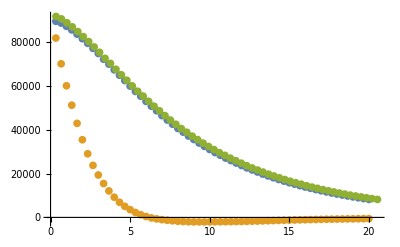

```mathematica
ListPlot[{PlotqTC1SetBγ40,PlotqTC2SetBγ40,PlotqTC1SetBγ40+0.027PlotqTC2SetBγ40}]
```

```mathematica
F2DL7Υ[20]/F1DL7Υ[20]
```

0.0545266

```mathematica
F2DL25Υ[40]/F1DL25Υ[40]
```

0.0270305

```mathematica
Nstep=60;
pre21DL7=F2DL7Υ[20]/F1DL7Υ[20];
PlotqTF2SetBDL7=ConstantArray[0,{Nstep,2}];
PlotqTF2KMRDL7=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTF2SetBZ[[i,1]]=PlotqTC3SetBZ[[i,1]];PlotqTS2SetBZ[[i,2]]= -π pre31 (PlotqTC3SetBZ[[i,2]])/PlotNormSetBZ;
PlotqTF2KMRZ[[i,1]]=PlotqTC3KMRZ[[i,1]];PlotqTS2KMRZ[[i,2]]=-π pre31 (PlotqTC3KMRZ[[i,2]])/PlotNormKMRZ;
]
```

```mathematica
(F1NumDL[14000,20,π/2] PlotNormSetAgamma+F2NumDL[14000,20,π/2] PlotNormSetADL)/F1NumDL[14000,20,π/2]/f1g[20/14000,20]^2
(F1NumDL[14000,20,π/2] PlotNormSetBgamma+F2NumDL[14000,20,π/2] PlotNormSetBDL)/F1NumDL[14000,20,π/2]/f1g[20/14000,20]^2
(F1NumDL[14000,20,π/2] PlotNormSet1gamma+F2NumDL[14000,20,π/2] PlotNormSet1DL)/F1NumDL[14000,20,π/2]/f1g[20/14000,20]^2
(F1NumDL[14000,20,π/2] PlotNormSet2gamma+F2NumDL[14000,20,π/2] PlotNormSet2DL)/F1NumDL[14000,20,π/2]/f1g[20/14000,20]^2
(F1NumDL[14000,20,π/2] PlotNormSet3gamma+F2NumDL[14000,20,π/2] PlotNormSet3DL)/F1NumDL[14000,20,π/2]/f1g[20/14000,20]^2
(F1NumDL[14000,20,π/2] PlotNormKMRgamma+F2NumDL[14000,20,π/2] PlotNormKMRDL)/F1NumDL[14000,20,π/2]/f1g[20/14000,20]^2
```

1.7456-1.35691×10^-29 ⅈ

1.44523-9.16178×10^-30 ⅈ

1.69131-1.46534×10^-29 ⅈ

0.809402-3.56451×10^-30 ⅈ

1.66336-1.38564×10^-29 ⅈ

1.23268+4.45842×10^-29 ⅈ

```mathematica
Nstep=30;
PlotqTS0SetADL=ConstantArray[0,{Nstep,2}];
PlotqTS0SetBDL=ConstantArray[0,{Nstep,2}];
PlotqTS0Set1DL=ConstantArray[0,{Nstep,2}];
PlotqTS0Set2DL=ConstantArray[0,{Nstep,2}];
PlotqTS0Set3DL=ConstantArray[0,{Nstep,2}];
PlotqTS0KMRDL=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTS0SetADL[[i,1]]=PlotqTC1SetA[[i,1]];PlotqTS0SetADL[[i,2]]=π (F1NumDL[14000,20,π/2] PlotqTC1SetA[[i,2]]+F2NumDL[14000,20,π/2] PlotqTC2SetA[[i,2]]/π^2)/(F1NumDL[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS0SetBDL[[i,1]]=PlotqTC1SetB[[i,1]];PlotqTS0SetBDL[[i,2]]=π (F1NumDL[14000,20,π/2] PlotqTC1SetB[[i,2]]+F2NumDL[14000,20,π/2] PlotqTC2SetB[[i,2]]/π^2)/(F1NumDL[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS0Set1DL[[i,1]]=PlotqTC1Set1[[i,1]];PlotqTS0Set1DL[[i,2]]=π (F1NumDL[14000,20,π/2] PlotqTC1Set1[[i,2]]+F2NumDL[14000,20,π/2] PlotqTC2Set1[[i,2]]/π^2)/(F1NumDL[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS0Set2DL[[i,1]]=PlotqTC1Set2[[i,1]];PlotqTS0Set2DL[[i,2]]=π (F1NumDL[14000,20,π/2] PlotqTC1Set2[[i,2]]+F2NumDL[14000,20,π/2] PlotqTC2Set2[[i,2]]/π^2)/(F1NumDL[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS0Set3DL[[i,1]]=PlotqTC1Set3[[i,1]];PlotqTS0Set3DL[[i,2]]=π (F1NumDL[14000,20,π/2] PlotqTC1Set3[[i,2]]+F2NumDL[14000,20,π/2] PlotqTC2Set3[[i,2]]/π^2)/(F1NumDL[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS0KMRDL[[i,1]]=PlotqTC1KMR[[i,1]];PlotqTS0KMRDL[[i,2]]=π (F1NumDL[14000,20,π/2] PlotqTC1KMR[[i,2]]+F2NumDL[14000,20,π/2] PlotqTC2KMR[[i,2]]/π^2)/(F1NumDL[14000,20,π/2] f1g[20/14000,20]^2);]
```

```mathematica
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotqTC2SetA,PlotqTC2SetB,PlotqTC2Set1,PlotqTC2Set2,PlotqTC2Set3,PlotqTC2KMR}]
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotNormSetADL,PlotNormSetBDL,PlotNormSet1DL,PlotNormSet2DL,PlotNormSet3DL,PlotNormKMRDL}]
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotqTS0SetADL,PlotqTS0SetBDL,PlotqTS0Set1DL,PlotqTS0Set2DL,PlotqTS0Set3DL,PlotqTS0KMRDL}]
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotqTC2SetAZ,PlotqTC2SetBZ,PlotqTC2Set1Z,PlotqTC2Set2Z,PlotqTC2Set3Z,PlotqTC2KMRZ}]
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotNormSetAZ2,PlotNormSetBZ2,PlotNormSet1Z2,PlotNormSet2Z2,PlotNormSet3Z2,PlotNormKMRZ2}]
```

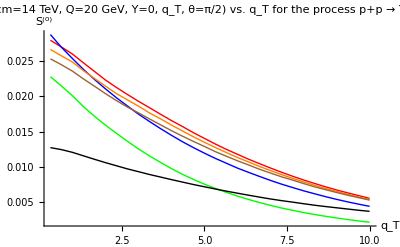

```mathematica
ListPlot[{PlotqTS0SetADL,PlotqTS0SetBDL,PlotqTS0Set1DL,PlotqTS0Set2DL,PlotqTS0Set3DL,PlotqTS0KMRDL},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick},{Orange,Thick},{Green,Thick},{Brown,Thick},{Black,Thick}},PlotLabel->Text[Style["S^(0)(√S_cm=14 TeV, Q=20 GeV, Y=0, q_T, θ=π/2) vs. q_T for the process p+p → Υ+(μ^+μ^-)+X",FontSize->14]],AxesLabel->{Text[Style["q_T",FontSize->14]],Text[Style["S^(0)",FontSize->14]]},PlotLegend->{"Set A","Set B","Set 1","Set 2","Set 3","KMR"},LegendPosition->{1.1,-0.4},TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

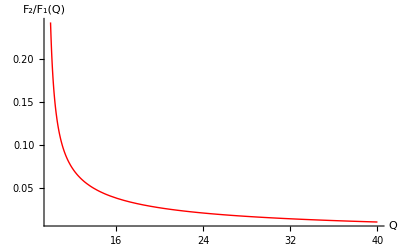

```mathematica
Plot[(F2NumDL[14000,Q,π/2]/F1NumDL[14000,Q,π/2]),{Q,10,40},{PlotStyle->{Red,Thick},AxesLabel->{Text[Style["Q",FontSize->14]],Text[Style["F_2/F_1(Q)",FontSize->14]]},AxesOrigin->{10,0}},PlotRange-> All]
```

Plots for Υ + Z - production:

```mathematica
Nstep=60;
PlotqTS0SetAZ=ConstantArray[0,{Nstep,2}];
PlotqTS0SetBZ=ConstantArray[0,{Nstep,2}];
PlotqTS0Set1Z=ConstantArray[0,{Nstep,2}];
PlotqTS0Set2Z=ConstantArray[0,{Nstep,2}];
PlotqTS0Set3Z=ConstantArray[0,{Nstep,2}];
PlotqTS0KMRZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTS0SetAZ[[i,1]]=PlotqTC1SetAZ[[i,1]];PlotqTS0SetAZ[[i,2]]=π (F1NumZ[14000,120,π/2] PlotqTC1SetAZ[[i,2]]+F2NumZ[14000,120,π/2] PlotqTC2SetAZ[[i,2]])/(F1NumZ[14000,120,π/2] f1g[120/14000,120]^2);
PlotqTS0SetBZ[[i,1]]=PlotqTC1SetBZ[[i,1]];PlotqTS0SetBZ[[i,2]]=π (F1NumZ[14000,120,π/2] PlotqTC1SetBZ[[i,2]]+F2NumZ[14000,120,π/2] PlotqTC2SetBZ[[i,2]])/(F1NumZ[14000,120,π/2] f1g[120/14000,120]^2);
PlotqTS0Set1Z[[i,1]]=PlotqTC1Set1Z[[i,1]];PlotqTS0Set1Z[[i,2]]=π (F1NumZ[14000,120,π/2] PlotqTC1Set1Z[[i,2]]+F2NumZ[14000,120,π/2] PlotqTC2Set1Z[[i,2]])/(F1NumZ[14000,120,π/2] f1g[120/14000,120]^2);
PlotqTS0Set2Z[[i,1]]=PlotqTC1Set2Z[[i,1]];PlotqTS0Set2Z[[i,2]]=π (F1NumZ[14000,120,π/2] PlotqTC1Set2Z[[i,2]]+F2NumZ[14000,120,π/2] PlotqTC2Set2Z[[i,2]])/(F1NumZ[14000,120,π/2] f1g[120/14000,120]^2);
PlotqTS0Set3Z[[i,1]]=PlotqTC1Set3Z[[i,1]];PlotqTS0Set3Z[[i,2]]=π (F1NumZ[14000,120,π/2] PlotqTC1Set3Z[[i,2]]+F2NumZ[14000,120,π/2] PlotqTC2Set3Z[[i,2]])/(F1NumZ[14000,120,π/2] f1g[120/14000,120]^2);
PlotqTS0KMRZ[[i,1]]=PlotqTC1KMRZ[[i,1]];PlotqTS0KMRZ[[i,2]]=π (F1NumZ[14000,120,π/2] PlotqTC1KMRZ[[i,2]]+F2NumZ[14000,120,π/2] PlotqTC2KMRZ[[i,2]])/(F1NumZ[14000,120,π/2] f1g[120/14000,120]^2);]
```

```mathematica
(F1NumZ[14000,120,π/2] PlotNormSetAZ+F2NumZ[14000,120,π/2] PlotNormSetAZ2)/F1NumZ[14000,120,π/2]/f1g[120/14000,120]^2
(F1NumZ[14000,120,π/2] PlotNormSetBZ+F2NumZ[14000,120,π/2] PlotNormSetBZ2)/F1NumZ[14000,120,π/2]/f1g[120/14000,120]^2
(F1NumZ[14000,120,π/2] PlotNormSet1Z+F2NumZ[14000,120,π/2] PlotNormSet1Z2)/F1NumZ[14000,120,π/2]/f1g[120/14000,120]^2
(F1NumZ[14000,120,π/2] PlotNormSet2Z+F2NumZ[14000,120,π/2] PlotNormSet2Z2)/F1NumZ[14000,120,π/2]/f1g[120/14000,120]^2
(F1NumZ[14000,120,π/2] PlotNormSet3Z+F2NumZ[14000,120,π/2] PlotNormSet3Z2)/F1NumZ[14000,120,π/2]/f1g[120/14000,120]^2
(F1NumZ[14000,120,π/2] PlotNormKMRZ+F2NumZ[14000,120,π/2] PlotNormKMRZ2)/F1NumZ[14000,120,π/2]/f1g[120/14000,120]^2
```

1.72715

1.29173

106.362

0.527354

62.7974

1.01825

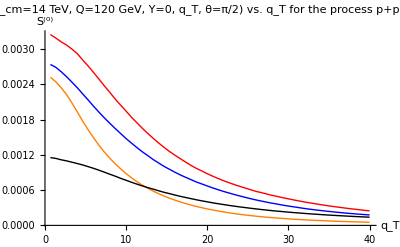

```mathematica
ListPlot[{PlotqTS0SetAZ,PlotqTS0SetBZ,PlotqTS0Set2Z,PlotqTS0KMRZ},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick},{Orange,Thick},{Black,Thick},{Brown,Thick},{Black,Thick}},PlotLabel->Text[Style["S^(0)(√S_cm=14 TeV, Q=120 GeV, Y=0, q_T, θ=π/2) vs. q_T for the process p+p → Υ+Z+X",FontSize->14]],AxesLabel->{Text[Style["q_T",FontSize->14]],Text[Style["S^(0)",FontSize->14]]},PlotLegend->{"Set A","Set B","Set 2","KMR"},LegendPosition->{1.1,-0.4},TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

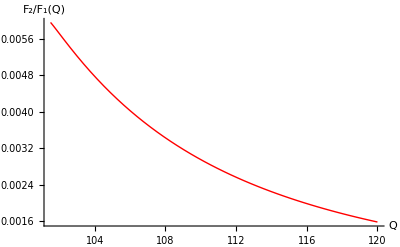

```mathematica
Plot[(F2NumZ[14000,Q,π/2]/F1NumZ[14000,Q,π/2]),{Q,101.5,120},{PlotStyle->{Red,Thick},AxesLabel->{Text[Style["Q",FontSize->14]],Text[Style["F_2/F_1(Q)",FontSize->14]]},AxesOrigin->{101.5,0}},PlotRange-> All]
```

Convolution C[w_3 (f_1 h_1+h_1 f_1)]:

```mathematica
C3SetA[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT (((2 kaq^2-ka2 qT^2)/(ka2  qT^2))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})(f1gSetA[Q/sS Exp[Y],kT^2,Q] f1gSetA[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]+f1gSetA[Q/sS Exp[-Y],kT^2,Q] f1gSetA[Q/sS Exp[Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q])),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C3SetB[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT (((2 kaq^2-ka2 qT^2)/(ka2  qT^2))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})(f1gSetB[Q/sS Exp[Y],kT^2,Q] f1gSetB[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]+f1gSetB[Q/sS Exp[-Y],kT^2,Q] f1gSetB[Q/sS Exp[Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q])),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C3Set1[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT (((2 kaq^2-ka2 qT^2)/(ka2  qT^2))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})(f1gSet1[Q/sS Exp[Y],kT^2,Q] f1gSet1[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]+f1gSet1[Q/sS Exp[-Y],kT^2,Q] f1gSet1[Q/sS Exp[Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q])),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C3Set2[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT (((2 kaq^2-ka2 qT^2)/(ka2  qT^2))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})(f1gSet2[Q/sS Exp[Y],kT^2,Q] f1gSet2[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]+f1gSet2[Q/sS Exp[-Y],kT^2,Q] f1gSet2[Q/sS Exp[Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q])),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C3Set3[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT (((2 kaq^2-ka2 qT^2)/(ka2  qT^2))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})(f1gSet3[Q/sS Exp[Y],kT^2,Q] f1gSet3[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]+f1gSet3[Q/sS Exp[-Y],kT^2,Q] f1gSet3[Q/sS Exp[Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q])),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C3KMR[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT (((2 kaq^2-ka2 qT^2)/(ka2  qT^2))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})(f1gKMR[Q/sS Exp[Y],kT^2,Q] f1gKMR[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]+f1gKMR[Q/sS Exp[-Y],kT^2,Q] f1gKMR[Q/sS Exp[Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q])),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
```

```mathematica
NormC3SetA[sS_,Y_,Q_]:=NIntegrate[2 π qT(kT (((2 kaq^2-ka2 qT^2)/(ka2  qT^2))/.{kaq->kT qT Cos[ϕ],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ],kb2->qT^2+kT^2-2 qT kT Cos[ϕ],kakb->kT qT Cos[ϕ]-kT^2})(f1gSetA[Q/sS Exp[Y],kT^2,Q] f1gSetA[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]+f1gSetA[Q/sS Exp[-Y],kT^2,Q] f1gSetA[Q/sS Exp[Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q])),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q/2},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormC3SetB[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT (((2 kaq^2-ka2 qT^2)/(ka2  qT^2))/.{kaq->kT qT Cos[ϕ],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ],kb2->qT^2+kT^2-2 qT kT Cos[ϕ],kakb->kT qT Cos[ϕ]-kT^2})(f1gSetB[Q/sS Exp[Y],kT^2,Q] f1gSetB[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]+f1gSetB[Q/sS Exp[-Y],kT^2,Q] f1gSetB[Q/sS Exp[Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q])),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q/2},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormC3Set1[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT (((2 kaq^2-ka2 qT^2)/(ka2  qT^2))/.{kaq->kT qT Cos[ϕ],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ],kb2->qT^2+kT^2-2 qT kT Cos[ϕ],kakb->kT qT Cos[ϕ]-kT^2})(f1gSet1[Q/sS Exp[Y],kT^2,Q] f1gSet1[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]+f1gSet1[Q/sS Exp[-Y],kT^2,Q] f1gSet1[Q/sS Exp[Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q])),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q/2},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormC3Set2[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT (((2 kaq^2-ka2 qT^2)/(ka2  qT^2))/.{kaq->kT qT Cos[ϕ],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ],kb2->qT^2+kT^2-2 qT kT Cos[ϕ],kakb->kT qT Cos[ϕ]-kT^2})(f1gSet2[Q/sS Exp[Y],kT^2,Q] f1gSet2[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]+f1gSet2[Q/sS Exp[-Y],kT^2,Q] f1gSet2[Q/sS Exp[Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q])),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q/2},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormC3Set3[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT (((2 kaq^2-ka2 qT^2)/(ka2  qT^2))/.{kaq->kT qT Cos[ϕ],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ],kb2->qT^2+kT^2-2 qT kT Cos[ϕ],kakb->kT qT Cos[ϕ]-kT^2})(f1gSet3[Q/sS Exp[Y],kT^2,Q] f1gSet3[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]+f1gSet3[Q/sS Exp[-Y],kT^2,Q] f1gSet3[Q/sS Exp[Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q])),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q/2},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormC3KMR[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT (((2 kaq^2-ka2 qT^2)/(ka2  qT^2))/.{kaq->kT qT Cos[ϕ],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ],kb2->qT^2+kT^2-2 qT kT Cos[ϕ],kakb->kT qT Cos[ϕ]-kT^2})(f1gKMR[Q/sS Exp[Y],kT^2,Q] f1gKMR[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]+f1gKMR[Q/sS Exp[-Y],kT^2,Q] f1gKMR[Q/sS Exp[Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q])),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q/2},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
```

```mathematica
Timing[Nstep=30;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC3SetA=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC3SetA[[i,1]]=qTNum;PlotqTC3SetA[[i,2]]=C3SetA[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC3SetB=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC3SetB[[i,1]]=qTNum;PlotqTC3SetB[[i,2]]=C3SetB[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC3Set1=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC3Set1[[i,1]]=qTNum;PlotqTC3Set1[[i,2]]=C3Set1[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC3Set2=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC3Set2[[i,1]]=qTNum;PlotqTC3Set2[[i,2]]=C3Set2[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC3Set3=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC3Set3[[i,1]]=qTNum;PlotqTC3Set3[[i,2]]=C3Set3[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC3KMR=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC3KMR[[i,1]]=qTNum;PlotqTC3KMR[[i,2]]=C3KMR[sSN,YN,qTNum,ϕqN,QN];]]
```

{1984.81,Null}

{1439.04,Null}

{2021.52,Null}

{1472.3,Null}

{1965.57,Null}

{2082.63,Null}

```mathematica
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC3SetAZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC3SetAZ[[i,1]]=qTNum;PlotqTC3SetAZ[[i,2]]=C3SetA[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC3SetBZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC3SetBZ[[i,1]]=qTNum;PlotqTC3SetBZ[[i,2]]=C3SetB[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC3Set1Z=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC3Set1Z[[i,1]]=qTNum;PlotqTC3Set1Z[[i,2]]=C3Set1[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC3Set2Z=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC3Set2Z[[i,1]]=qTNum;PlotqTC3Set2Z[[i,2]]=C3Set2[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC3Set3Z=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC3Set3Z[[i,1]]=qTNum;PlotqTC3Set3Z[[i,2]]=C3Set3[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC3KMRZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC3KMRZ[[i,1]]=qTNum;PlotqTC3KMRZ[[i,2]]=C3KMR[sSN,YN,qTNum,ϕqN,QN];]]
```

{3018.72,Null}

{2895.67,Null}

{8825.05,Null}

{2337.12,Null}

{9336.38,Null}

{2895.18,Null}

```mathematica
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC3SetBZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC3SetBZ[[i,1]]=qTNum;PlotqTC3SetBZ[[i,2]]=C3SetB[sSN,YN,qTNum,ϕqN,QN];]]

Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC3KMRZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC3KMRZ[[i,1]]=qTNum;PlotqTC3KMRZ[[i,2]]=C3KMR[sSN,YN,qTNum,ϕqN,QN];]]
```

{2899.51862,Null}

{2834.5257,Null}

```mathematica
Timing[Nstep=60;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC3SetBγ20=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC3SetBγ20[[i,1]]=qTNum;PlotqTC3SetBγ20[[i,2]]=C3SetB[sSN,YN,qTNum,ϕqN,QN];]]

Timing[Nstep=60;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC3KMRγ20=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC3KMRγ20[[i,1]]=qTNum;PlotqTC3KMRγ20[[i,2]]=C3KMR[sSN,YN,qTNum,ϕqN,QN];]]
```

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`-3894.13 and TraditionalForm`87.86937882751467` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`-6219.28 and TraditionalForm`87.36684837420125` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`3593.58633021052` and TraditionalForm`83.0265935006209` for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

{3608.39211,Null}

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`-215.334 and TraditionalForm`39.76345222372534` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`-562.845 and TraditionalForm`41.515878129287636` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`-719.255 and TraditionalForm`45.09405251209411` for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`19 recursive bisections in TraditionalForm`kT near TraditionalForm`{kT, ϕ} = TraditionalForm`{0.746604, 0.473699}. NIntegrate obtained TraditionalForm`5423.973250378284` and TraditionalForm`104.8128428653974` for the integral and error estimates.

{5375.3492,Null}

```mathematica
Timing[Nstep=60;sSN=14000;QN=40;YN=0;ϕqN=0;
PlotqTC3SetBγ40=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC3SetBγ40[[i,1]]=qTNum;PlotqTC3SetBγ40[[i,2]]=C3SetB[sSN,YN,qTNum,ϕqN,QN];]]

Timing[Nstep=60;sSN=14000;QN=40;YN=0;ϕqN=0;
PlotqTC3KMRγ40=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC3KMRγ40[[i,1]]=qTNum;PlotqTC3KMRγ40[[i,2]]=C3KMR[sSN,YN,qTNum,ϕqN,QN];]]
```

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`-244.294 and TraditionalForm`7.222037227486093` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`949.8220440744741` and TraditionalForm`7.744288395247059` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`3410.4690451470974` and TraditionalForm`7.024849017975129` for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

{3078.09464,Null}

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`-38.5692 and TraditionalForm`3.025260186747607` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`-96.1512 and TraditionalForm`2.7919763290688966` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`-151.853 and TraditionalForm`2.7420023979079686` for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`19 recursive bisections in TraditionalForm`kT near TraditionalForm`{kT, ϕ} = TraditionalForm`{0.770487, 0.0117831}. NIntegrate obtained TraditionalForm`-204.769 and TraditionalForm`10.401404281539826` for the integral and error estimates.

{3930.04629,Null}

```mathematica
Nstep=60;
pre31=F3ZΥ[120]/F1ZΥ[120];
PlotqTS2SetBZ=ConstantArray[0,{Nstep,2}];
PlotqTS2KMRZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTS2SetBZ[[i,1]]=PlotqTC3SetBZ[[i,1]];PlotqTS2SetBZ[[i,2]]= -π pre31 (PlotqTC3SetBZ[[i,2]])/PlotNormSetBZ;
PlotqTS2KMRZ[[i,1]]=PlotqTC3KMRZ[[i,1]];PlotqTS2KMRZ[[i,2]]=-π pre31 (PlotqTC3KMRZ[[i,2]])/PlotNormKMRZ;
]
```

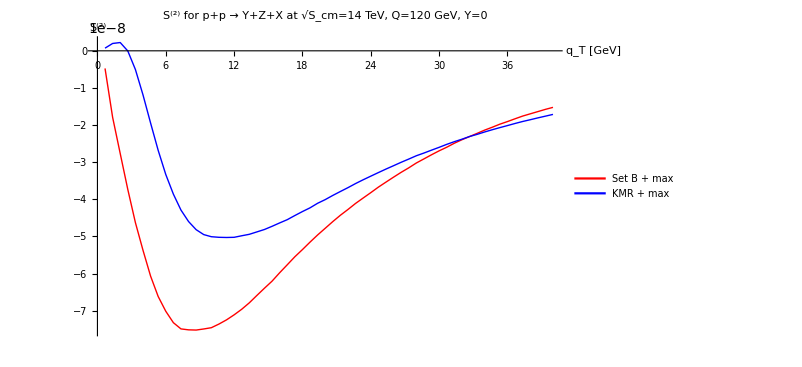

```mathematica
ListPlot[{PlotqTS2SetBZ,PlotqTS2KMRZ},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLabel->Text[Style["S^(2) for p+p → Υ+Z+X at √S_cm=14 TeV, Q=120 GeV, Y=0",FontSize->14]],AxesLabel->{Text[Style["q_T [GeV]",FontSize->14]],Text[Style["S^(2)",FontSize->14]]},PlotLegends->Placed[{"Set B + max","KMR + max"},{0.75,0.75}],TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
Nstep=60;
pre31DL7=F3DL7Υ[20]/F1DL7Υ[20];
PlotqTS2SetBDL7=ConstantArray[0,{Nstep,2}];
PlotqTS2KMRDL7=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTS2SetBDL7[[i,1]]=PlotqTC3SetBγ20[[i,1]];PlotqTS2SetBDL7[[i,2]]= -π pre31DL7 (PlotqTC3SetBγ20[[i,2]])/PlotNormSetBγ20;
PlotqTS2KMRDL7[[i,1]]=PlotqTC3KMRγ20[[i,1]];PlotqTS2KMRDL7[[i,2]]=-π pre31DL7 (PlotqTC3KMRγ20[[i,2]])/PlotNormKMRγ20;
]
```

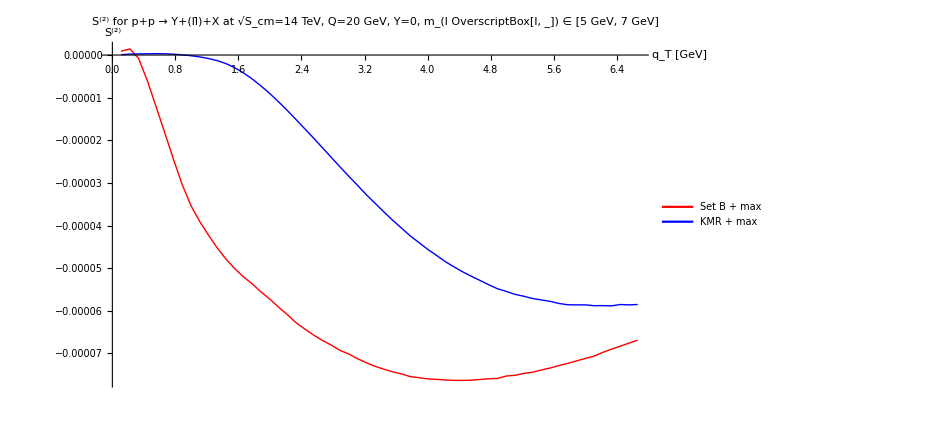

```mathematica
ListPlot[{PlotqTS2SetBDL7,PlotqTS2KMRDL7},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLabel->Text[Style["S^(2) for p+p → Υ+(ll̄)+X at √S_cm=14 TeV, Q=20 GeV, Y=0, m_(l OverscriptBox[l, _]) ∈ [5 GeV, 7 GeV]",FontSize->14]],AxesLabel->{Text[Style["q_T [GeV]",FontSize->14]],Text[Style["S^(2)",FontSize->14]]},PlotLegends->Placed[{"Set B + max","KMR + max"},{0.75,0.75}],TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
Nstep=60;
pre31DL25=F3DL25Υ[40]/F1DL25Υ[40];
PlotqTS2SetBDL25=ConstantArray[0,{Nstep,2}];
PlotqTS2KMRDL25=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTS2SetBDL25[[i,1]]=PlotqTC3SetBγ40[[i,1]];PlotqTS2SetBDL25[[i,2]]= -π pre31DL25 (PlotqTC3SetBγ40[[i,2]])/PlotNormSetBγ40;
PlotqTS2KMRDL25[[i,1]]=PlotqTC3KMRγ40[[i,1]];PlotqTS2KMRDL25[[i,2]]=-π pre31DL25 (PlotqTC3KMRγ40[[i,2]])/PlotNormKMRγ40;
]
```

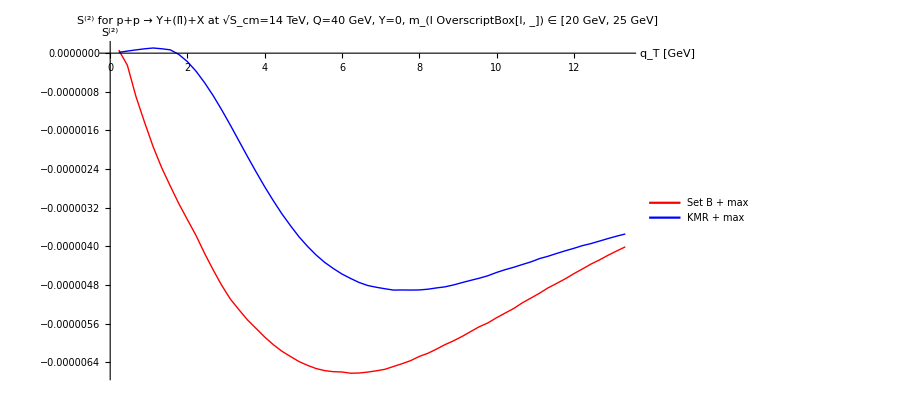

```mathematica
ListPlot[{PlotqTS2SetBDL25,PlotqTS2KMRDL25},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLabel->Text[Style["S^(2) for p+p → Υ+(ll̄)+X at √S_cm=14 TeV, Q=40 GeV, Y=0, m_(l OverscriptBox[l, _]) ∈ [20 GeV, 25 GeV]",FontSize->14]],AxesLabel->{Text[Style["q_T [GeV]",FontSize->14]],Text[Style["S^(2)",FontSize->14]]},PlotLegends->Placed[{"Set B + max","KMR + max"},{0.75,0.75}],TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
PlotNormC3SetADL=NormC3SetA[14000,0,20];
PlotNormC3SetBDL=NormC3SetB[14000,0,20];
PlotNormC3Set1DL=NormC3Set1[14000,0,20];
PlotNormC3Set2DL=NormC3Set2[14000,0,20];
PlotNormC3Set3DL=NormC3Set3[14000,0,20];
PlotNormC3KMRDL=NormC3KMR[14000,0,20];
```

```mathematica
PlotNormC3SetAZ=NormC3SetA[14000,0,120];
PlotNormC3SetBZ=NormC3SetB[14000,0,120];
PlotNormC3Set1Z=NormC3Set1[14000,0,120];
PlotNormC3Set2Z=NormC3Set2[14000,0,120];
PlotNormC3Set3Z=NormC3Set3[14000,0,120];
PlotNormC3KMRZ=NormC3KMR[14000,0,120];
```

```mathematica
PlotNormC3SetBZ=NormC3SetB[14000,0,120];
PlotNormC3KMRZ=NormC3KMR[14000,0,120];
```

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`827133.0655557199` and TraditionalForm`1503.2214735019022` for the integral and error estimates.

```mathematica
F3ZΥ[120]/F1ZΥ[120] PlotNormC3SetBZ/PlotNormSetBZ
F3ZΥ[120]/F1ZΥ[120] PlotNormC3KMRZ/PlotNormKMRZ
```

0.0000741056

0.0000717762

```mathematica
PlotNormC3SetBγ20=NormC3SetB[14000,0,20];
PlotNormC3KMRγ20=NormC3KMR[14000,0,20];
```

```mathematica
F3DL7Υ[20]/F1DL7Υ[20] PlotNormC3SetBγ20/PlotNormSetBγ20
F3DL7Υ[20]/F1DL7Υ[20] PlotNormC3KMRγ20/PlotNormKMRγ20
```

0.00611141

0.00491855

```mathematica
PlotNormC3SetBγ40=NormC3SetB[14000,0,40];
PlotNormC3KMRγ40=NormC3KMR[14000,0,40];
```

```mathematica
F3DL25Υ[40]/F1DL25Υ[40] PlotNormC3SetBγ40/PlotNormSetBγ40
F3DL25Υ[40]/F1DL25Υ[40] PlotNormC3KMRγ40/PlotNormKMRγ40
```

0.00157761

0.00138834

Plots for Υ + γ production:

```mathematica
F3aNumγ[14000,20,π/2] PlotNormC3SetADL/2/F1Numγ[14000,20,π/2]/f1g[20/14000,20]^2
F3aNumγ[14000,20,π/2] PlotNormC3SetBDL/2/F1Numγ[14000,20,π/2]/f1g[20/14000,20]^2
F3aNumγ[14000,20,π/2] PlotNormC3Set1DL/2/F1Numγ[14000,20,π/2]/f1g[20/14000,20]^2
F3aNumγ[14000,20,π/2] PlotNormC3Set2DL/2/F1Numγ[14000,20,π/2]/f1g[20/14000,20]^2
F3aNumγ[14000,20,π/2] PlotNormC3Set3DL/2/F1Numγ[14000,20,π/2]/f1g[20/14000,20]^2
F3aNumγ[14000,20,π/2] PlotNormC3KMRDL/2/F1Numγ[14000,20,π/2]/f1g[20/14000,20]^2
```

0.0247158

0.0236612

0.0236899

0.016221

0.0225188

0.0117362

```mathematica
Nstep=30;
PlotqTS2SetAγ=ConstantArray[0,{Nstep,2}];
PlotqTS2SetBγ=ConstantArray[0,{Nstep,2}];
PlotqTS2Set1γ=ConstantArray[0,{Nstep,2}];
PlotqTS2Set2γ=ConstantArray[0,{Nstep,2}];
PlotqTS2Set3γ=ConstantArray[0,{Nstep,2}];
PlotqTS2KMRγ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTS2SetAγ[[i,1]]=PlotqTC3SetA[[i,1]];PlotqTS2SetAγ[[i,2]]=-π (F3aNumγ[14000,20,π/2] PlotqTC3SetA[[i,2]])/(2 π^2 F1Numγ[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS2SetBγ[[i,1]]=PlotqTC3SetB[[i,1]];PlotqTS2SetBγ[[i,2]]=-π (F3aNumγ[14000,20,π/2] PlotqTC3SetB[[i,2]])/(2 π^2 F1Numγ[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS2Set1γ[[i,1]]=PlotqTC3Set1[[i,1]];PlotqTS2Set1γ[[i,2]]=-π (F3aNumγ[14000,20,π/2] PlotqTC3Set1[[i,2]])/(2 π^2 F1Numγ[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS2Set2γ[[i,1]]=PlotqTC3Set2[[i,1]];PlotqTS2Set2γ[[i,2]]=-π (F3aNumγ[14000,20,π/2] PlotqTC3Set2[[i,2]])/(2 π^2 F1Numγ[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS2Set3γ[[i,1]]=PlotqTC3Set3[[i,1]];PlotqTS2Set3γ[[i,2]]=-π (F3aNumγ[14000,20,π/2] PlotqTC3Set3[[i,2]])/(2 π^2 F1Numγ[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS2KMRγ[[i,1]]=PlotqTC3KMR[[i,1]];PlotqTS2KMRγ[[i,2]]=-π (F3aNumγ[14000,20,π/2] PlotqTC3KMR[[i,2]])/(2 π^2 F1Numγ[14000,20,π/2] f1g[20/14000,20]^2);]
```

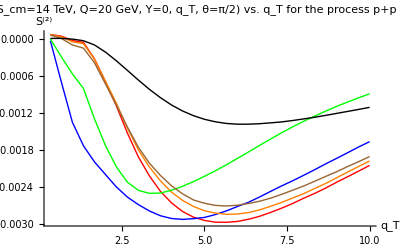

```mathematica
ListPlot[{PlotqTS2SetAγ,PlotqTS2SetBγ,PlotqTS2Set1γ,PlotqTS2Set2γ,PlotqTS2Set3γ,PlotqTS2KMRγ},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick},{Orange,Thick},{Green,Thick},{Brown,Thick},{Black,Thick}},PlotLabel->Text[Style["S^(2)(√S_cm=14 TeV, Q=20 GeV, Y=0, q_T, θ=π/2) vs. q_T for the process p+p → Υ+γ+X",FontSize->14]],AxesLabel->{Text[Style["q_T",FontSize->14]],Text[Style["S^(2)",FontSize->14]]},PlotLegend->{"Set A","Set B","Set 1","Set 2","Set 3","KMR"},LegendPosition->{1.1,-0.4},TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotNormC3SetADL,PlotNormC3SetBDL,PlotNormC3Set1DL,PlotNormC3Set2DL,PlotNormC3Set3DL,PlotNormC3KMRDL}]
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotNormC3SetAZ,PlotNormC3SetBZ,PlotNormC3Set1Z,PlotNormC3Set2Z,PlotNormC3Set3Z,PlotNormC3KMRZ}]
```

Plots for Υ + (μ^+μ^-) - production

```mathematica
F3aNumDL[14000,20,π/2] PlotNormC3SetADL/2/F1NumDL[14000,20,π/2]/f1g[20/14000,20]^2
F3aNumDL[14000,20,π/2] PlotNormC3SetBDL/2/F1NumDL[14000,20,π/2]/f1g[20/14000,20]^2
F3aNumDL[14000,20,π/2] PlotNormC3Set1DL/2/F1NumDL[14000,20,π/2]/f1g[20/14000,20]^2
F3aNumDL[14000,20,π/2] PlotNormC3Set2DL/2/F1NumDL[14000,20,π/2]/f1g[20/14000,20]^2
F3aNumDL[14000,20,π/2] PlotNormC3Set3DL/2/F1NumDL[14000,20,π/2]/f1g[20/14000,20]^2
F3aNumDL[14000,20,π/2] PlotNormC3KMRDL/2/F1NumDL[14000,20,π/2]/f1g[20/14000,20]^2
```

0.0243382-2.2262×10^-28 ⅈ

0.0232998-2.13121×10^-28 ⅈ

0.023328-2.13379×10^-28 ⅈ

0.0159732-1.46105×10^-28 ⅈ

0.0221748-2.02831×10^-28 ⅈ

0.0115569-1.0571×10^-28 ⅈ

```mathematica
Nstep=30;
PlotqTS2SetADL=ConstantArray[0,{Nstep,2}];
PlotqTS2SetBDL=ConstantArray[0,{Nstep,2}];
PlotqTS2Set1DL=ConstantArray[0,{Nstep,2}];
PlotqTS2Set2DL=ConstantArray[0,{Nstep,2}];
PlotqTS2Set3DL=ConstantArray[0,{Nstep,2}];
PlotqTS2KMRDL=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTS2SetADL[[i,1]]=PlotqTC3SetA[[i,1]];
PlotqTS2SetADL[[i,2]]=
-π (F3aNumDL[14000,20,π/2] PlotqTC3SetA[[i,2]])/(2 π^2 F1NumDL[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS2SetBDL[[i,1]]=PlotqTC3SetB[[i,1]];PlotqTS2SetBDL[[i,2]]=-π (F3aNumDL[14000,20,π/2] PlotqTC3SetB[[i,2]])/(2 π^2 F1NumDL[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS2Set1DL[[i,1]]=PlotqTC3Set1[[i,1]];PlotqTS2Set1DL[[i,2]]=-π (F3aNumDL[14000,20,π/2] PlotqTC3Set1[[i,2]])/(2 π^2 F1NumDL[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS2Set2DL[[i,1]]=PlotqTC3Set2[[i,1]];PlotqTS2Set2DL[[i,2]]=-π (F3aNumDL[14000,20,π/2] PlotqTC3Set2[[i,2]])/(2 π^2 F1NumDL[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS2Set3DL[[i,1]]=PlotqTC3Set3[[i,1]];PlotqTS2Set3DL[[i,2]]=-π (F3aNumDL[14000,20,π/2] PlotqTC3Set3[[i,2]])/(2 π^2 F1NumDL[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS2KMRDL[[i,1]]=PlotqTC3KMR[[i,1]];PlotqTS2KMRDL[[i,2]]=-π (F3aNumDL[14000,20,π/2] PlotqTC3KMR[[i,2]])/(2 π^2 F1NumDL[14000,20,π/2] f1g[20/14000,20]^2);]
```

```mathematica
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotqTC3SetA,PlotqTC3SetB,PlotqTC3Set1,PlotqTC3Set2,PlotqTC3Set3,PlotqTC3KMR}]
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotqTC3SetAZ,PlotqTC3SetBZ,PlotqTC3Set1Z,PlotqTC3Set2Z,PlotqTC3Set3Z,PlotqTC3KMRZ}]
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotqTS2SetADL,PlotqTS2SetBDL,PlotqTS2Set1DL,PlotqTS2Set2DL,PlotqTS2Set3DL,PlotqTS2KMRDL}]
```

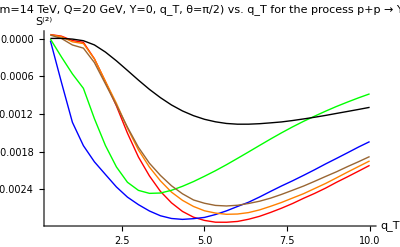

```mathematica
ListPlot[{PlotqTS2SetADL,PlotqTS2SetBDL,PlotqTS2Set1DL,PlotqTS2Set2DL,PlotqTS2Set3DL,PlotqTS2KMRDL},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick},{Orange,Thick},{Green,Thick},{Brown,Thick},{Black,Thick}},PlotLabel->Text[Style["S^(2)(√S_cm=14 TeV, Q=20 GeV, Y=0, q_T, θ=π/2) vs. q_T for the process p+p → Υ +(μ^+μ^-)+X",FontSize->14]],AxesLabel->{Text[Style["q_T",FontSize->14]],Text[Style["S^(2)",FontSize->14]]},PlotLegend->{"Set A","Set B","Set 1","Set 2","Set 3","KMR"},LegendPosition->{1.1,-0.4},TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

Plots for Υ + Z - production:

```mathematica
F3aNumZ[14000,120,π/2] PlotNormC3SetAZ/2/F1NumZ[14000,120,π/2]/f1g[120/14000,120]^2
F3aNumZ[14000,120,π/2] PlotNormC3SetBZ/2/F1NumZ[14000,120,π/2]/f1g[120/14000,120]^2
F3aNumZ[14000,120,π/2] PlotNormC3Set1Z/2/F1NumZ[14000,120,π/2]/f1g[120/14000,120]^2
F3aNumZ[14000,120,π/2] PlotNormC3Set2Z/2/F1NumZ[14000,120,π/2]/f1g[120/14000,120]^2
F3aNumZ[14000,120,π/2] PlotNormC3Set3Z/2/F1NumZ[14000,120,π/2]/f1g[120/14000,120]^2
F3aNumZ[14000,120,π/2] PlotNormC3KMRZ/2/F1NumZ[14000,120,π/2]/f1g[120/14000,120]^2
```

0.00501244

0.00388223

0.00324166

0.00202912

0.00489464

0.00215083

```mathematica
Nstep=60;
PlotqTS2SetAZ=ConstantArray[0,{Nstep,2}];
PlotqTS2SetBZ=ConstantArray[0,{Nstep,2}];
PlotqTS2Set1Z=ConstantArray[0,{Nstep,2}];
PlotqTS2Set2Z=ConstantArray[0,{Nstep,2}];
PlotqTS2Set3Z=ConstantArray[0,{Nstep,2}];
PlotqTS2KMRZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTS2SetAZ[[i,1]]=PlotqTC3SetAZ[[i,1]];
PlotqTS2SetAZ[[i,2]]=-π (F3aNumZ[14000,120,π/2] PlotqTC3SetAZ[[i,2]])/(2 F1NumZ[14000,120,π/2] f1g[120/14000,120]^2);
PlotqTS2SetBZ[[i,1]]=PlotqTC3SetBZ[[i,1]];PlotqTS2SetBZ[[i,2]]=-π (F3aNumZ[14000,120,π/2] PlotqTC3SetBZ[[i,2]])/(2 F1NumZ[14000,120,π/2] f1g[120/14000,120]^2);
PlotqTS2Set1Z[[i,1]]=PlotqTC3Set1Z[[i,1]];PlotqTS2Set1Z[[i,2]]=-π (F3aNumZ[14000,120,π/2] PlotqTC3Set1Z[[i,2]])/(2 F1NumZ[14000,120,π/2] f1g[120/14000,120]^2);
PlotqTS2Set2Z[[i,1]]=PlotqTC3Set2Z[[i,1]];PlotqTS2Set2Z[[i,2]]=-π (F3aNumZ[14000,120,π/2] PlotqTC3Set2Z[[i,2]])/(2 F1NumZ[14000,120,π/2] f1g[120/14000,120]^2);
PlotqTS2Set3Z[[i,1]]=PlotqTC3Set3Z[[i,1]];PlotqTS2Set3Z[[i,2]]=-π (F3aNumZ[14000,120,π/2] PlotqTC3Set3Z[[i,2]])/(2 F1NumZ[14000,120,π/2] f1g[120/14000,120]^2);
PlotqTS2KMRZ[[i,1]]=PlotqTC3KMRZ[[i,1]];PlotqTS2KMRZ[[i,2]]=-π (F3aNumZ[14000,120,π/2] PlotqTC3KMRZ[[i,2]])/(2 F1NumZ[14000,120,π/2] f1g[120/14000,120]^2);]
```

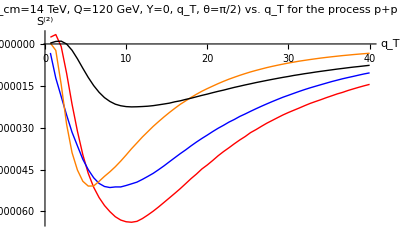

```mathematica
ListPlot[{PlotqTS2SetAZ,PlotqTS2SetBZ,PlotqTS2Set2Z,PlotqTS2KMRZ},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick},{Orange,Thick},{Black,Thick},{Brown,Thick},{Black,Thick}},PlotLabel->Text[Style["S^(2)(√S_cm=14 TeV, Q=120 GeV, Y=0, q_T, θ=π/2) vs. q_T for the process p+p → Υ +Z+X",FontSize->14]],AxesLabel->{Text[Style["q_T",FontSize->14]],Text[Style["S^(2)",FontSize->14]]},PlotLegend->{"Set A","Set B","Set 2","KMR"},LegendPosition->{1.1,-0.4},TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

Convolution C[w_4 h_1 h_1]:

```mathematica
C4SetA[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)-4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gSetA[Q/sS Exp[Y],kT^2,Q] f1gSetA[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C4SetB[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)-4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gSetB[Q/sS Exp[Y],kT^2,Q] f1gSetB[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C4Set1[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)-4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gSet1[Q/sS Exp[Y],kT^2,Q] f1gSet1[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C4Set2[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)-4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gSet2[Q/sS Exp[Y],kT^2,Q] f1gSet2[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C4Set3[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)-4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gSet3[Q/sS Exp[Y],kT^2,Q] f1gSet3[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C4KMR[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)-4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gKMR[Q/sS Exp[Y],kT^2,Q] f1gKMR[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
```

```mathematica
NormC4SetA[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)-4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ],kb2->qT^2+kT^2-2 qT kT Cos[ϕ],kakb->kT qT Cos[ϕ]-kT^2})f1gSetA[Q/sS Exp[Y],kT^2,Q] f1gSetA[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q/2},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormC4SetB[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)-4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ],kb2->qT^2+kT^2-2 qT kT Cos[ϕ],kakb->kT qT Cos[ϕ]-kT^2})f1gSetB[Q/sS Exp[Y],kT^2,Q] f1gSetB[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q/2},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormC4Set1[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)-4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ],kb2->qT^2+kT^2-2 qT kT Cos[ϕ],kakb->kT qT Cos[ϕ]-kT^2})f1gSet1[Q/sS Exp[Y],kT^2,Q] f1gSet1[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q/2},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormC4Set2[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)-4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ],kb2->qT^2+kT^2-2 qT kT Cos[ϕ],kakb->kT qT Cos[ϕ]-kT^2})f1gSet2[Q/sS Exp[Y],kT^2,Q] f1gSet2[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q/2},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormC4Set3[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)-4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ],kb2->qT^2+kT^2-2 qT kT Cos[ϕ],kakb->kT qT Cos[ϕ]-kT^2})f1gSet3[Q/sS Exp[Y],kT^2,Q] f1gSet3[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q/2},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
NormC4KMR[sS_,Y_,Q_]:=NIntegrate[2 π qT (kT ((((2 kaq^2-ka2 qT^2) (2kbq^2-kb2 qT^2)-4 kaq kbq (qT^2 kakb-kaq kbq))/(ka2 kb2 qT^4))/.{kaq->kT qT Cos[ϕ],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ],kb2->qT^2+kT^2-2 qT kT Cos[ϕ],kakb->kT qT Cos[ϕ]-kT^2})f1gKMR[Q/sS Exp[Y],kT^2,Q] f1gKMR[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ]),Q]),{kT,0,∞},{ϕ,0,2 π},{qT,0,Q/2},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
```

```mathematica
Timing[Nstep=30;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC4SetA=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC4SetA[[i,1]]=qTNum;PlotqTC4SetA[[i,2]]=C4SetA[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC4SetB=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC4SetB[[i,1]]=qTNum;PlotqTC4SetB[[i,2]]=C4SetB[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC4Set1=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC4Set1[[i,1]]=qTNum;PlotqTC4Set1[[i,2]]=C4Set1[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC4Set2=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC4Set2[[i,1]]=qTNum;PlotqTC4Set2[[i,2]]=C4Set2[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC4Set3=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC4Set3[[i,1]]=qTNum;PlotqTC4Set3[[i,2]]=C4Set3[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=30;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC4KMR=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/2;
PlotqTC4KMR[[i,1]]=qTNum;PlotqTC4KMR[[i,2]]=C4KMR[sSN,YN,qTNum,ϕqN,QN];]]
```

{2509.19,Null}

{2482.82,Null}

{2441.62,Null}

{2055.58,Null}

{2613.28,Null}

{2708.11,Null}

```mathematica
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC4SetAZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC4SetAZ[[i,1]]=qTNum;PlotqTC4SetAZ[[i,2]]=C4SetA[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC4SetBZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC4SetBZ[[i,1]]=qTNum;PlotqTC4SetBZ[[i,2]]=C4SetB[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC4Set1Z=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC4Set1Z[[i,1]]=qTNum;PlotqTC4Set1Z[[i,2]]=C4Set1[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC4Set2Z=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC4Set2Z[[i,1]]=qTNum;PlotqTC4Set2Z[[i,2]]=C4Set2[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC4Set3Z=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC4Set3Z[[i,1]]=qTNum;PlotqTC4Set3Z[[i,2]]=C4Set3[sSN,YN,qTNum,ϕqN,QN];]]
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC4KMRZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC4KMRZ[[i,1]]=qTNum;PlotqTC4KMRZ[[i,2]]=C4KMR[sSN,YN,qTNum,ϕqN,QN];]]
```

{4807.98,Null}

{5181.43,Null}

{9930.29,Null}

{4081.07,Null}

{10057.2,Null}

{4388.92,Null}

```mathematica
Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC4SetBZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC4SetBZ[[i,1]]=qTNum;PlotqTC4SetBZ[[i,2]]=C4SetB[sSN,YN,qTNum,ϕqN,QN];]]

Timing[Nstep=60;sSN=14000;QN=120;YN=0;ϕqN=0;
PlotqTC4KMRZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC4KMRZ[[i,1]]=qTNum;PlotqTC4KMRZ[[i,2]]=C4KMR[sSN,YN,qTNum,ϕqN,QN];]]
```

{5079.7058,Null}

{4467.20562,Null}

```mathematica
Timing[Nstep=60;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC4SetBγ20=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC4SetBγ20[[i,1]]=qTNum;PlotqTC4SetBγ20[[i,2]]=C4SetB[sSN,YN,qTNum,ϕqN,QN];]]

Timing[Nstep=60;sSN=14000;QN=20;YN=0;ϕqN=0;
PlotqTC4KMRγ20=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC4KMRγ20[[i,1]]=qTNum;PlotqTC4KMRγ20[[i,2]]=C4KMR[sSN,YN,qTNum,ϕqN,QN];]]
```

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`338.44211545690865` and TraditionalForm`179.76538751546556` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`3295.7048017741313` and TraditionalForm`67.84691679954969` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`11152.101881650102` and TraditionalForm`70.95478582393253` for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

{6038.2655,Null}

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`75.33667696184116` and TraditionalForm`32.14001262910602` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`176.39085189150126` and TraditionalForm`31.34550563435849` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`439.11705785116925` and TraditionalForm`31.478498032843017` for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

{6551.45592,Null}

```mathematica
Timing[Nstep=60;sSN=14000;QN=40;YN=0;ϕqN=0;
PlotqTC4SetBγ40=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC4SetBγ40[[i,1]]=qTNum;PlotqTC4SetBγ40[[i,2]]=C4SetB[sSN,YN,qTNum,ϕqN,QN];]]

Timing[Nstep=60;sSN=14000;QN=40;YN=0;ϕqN=0;
PlotqTC4KMRγ40=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
PlotqTC4KMRγ40[[i,1]]=qTNum;PlotqTC4KMRγ40[[i,2]]=C4KMR[sSN,YN,qTNum,ϕqN,QN];]]
```

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`116.23691181825512` and TraditionalForm`5.377947689493226` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`857.1969634499305` and TraditionalForm`5.387716826836924` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`1777.9249695918024` and TraditionalForm`11.977961938178371` for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

{5050.73532,Null}

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`6.699191765400635` and TraditionalForm`2.2353748203759687` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`20.947466702990546` and TraditionalForm`4.312223447886743` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`65.7727172840162` and TraditionalForm`2.4655966684822714` for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

{5270.96148,Null}

```mathematica
Nstep=60;
pre41=F4ZΥ[120]/F1ZΥ[120];
PlotqTS4SetBZ=ConstantArray[0,{Nstep,2}];
PlotqTS4KMRZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTS4SetBZ[[i,1]]=PlotqTC4SetBZ[[i,1]];PlotqTS4SetBZ[[i,2]]=π pre41 (PlotqTC4SetBZ[[i,2]])/PlotNormSetBZ;
PlotqTS4KMRZ[[i,1]]=PlotqTC4KMRZ[[i,1]];PlotqTS4KMRZ[[i,2]]=π pre41 (PlotqTC4KMRZ[[i,2]])/PlotNormKMRZ;
]
```

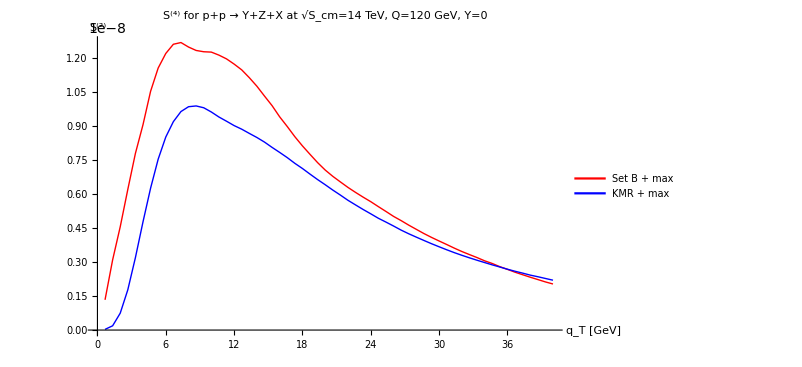

```mathematica
ListPlot[{PlotqTS4SetBZ,PlotqTS4KMRZ},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLabel->Text[Style["S^(4) for p+p → Υ+Z+X at √S_cm=14 TeV, Q=120 GeV, Y=0",FontSize->14]],AxesLabel->{Text[Style["q_T [GeV]",FontSize->14]],Text[Style["S^(2)",FontSize->14]]},PlotLegends->Placed[{"Set B + max","KMR + max"},{0.75,0.75}],TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
Nstep=60;
pre41DL7=F4DL7Υ[20]/F1DL7Υ[20];
PlotqTS4SetBDL7=ConstantArray[0,{Nstep,2}];
PlotqTS4KMRDL7=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTS4SetBDL7[[i,1]]=PlotqTC4SetBγ20[[i,1]];PlotqTS4SetBDL7[[i,2]]=π pre41DL7 (PlotqTC4SetBγ20[[i,2]])/PlotNormSetBγ20;
PlotqTS4KMRDL7[[i,1]]=PlotqTC4KMRγ20[[i,1]];PlotqTS4KMRDL7[[i,2]]=π pre41DL7 (PlotqTC4KMRγ20[[i,2]])/PlotNormKMRγ20;
]
```

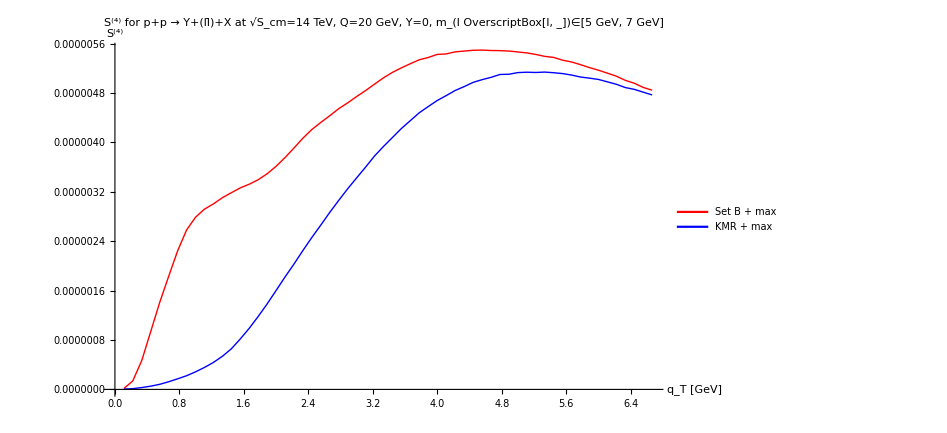

```mathematica
ListPlot[{PlotqTS4SetBDL7,PlotqTS4KMRDL7},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLabel->Text[Style["S^(4) for p+p → Υ+(ll̄)+X at √S_cm=14 TeV, Q=20 GeV, Y=0, m_(l OverscriptBox[l, _])∈[5 GeV, 7 GeV]",FontSize->14]],AxesLabel->{Text[Style["q_T [GeV]",FontSize->14]],Text[Style["S^(4)",FontSize->14]]},PlotLegends->Placed[{"Set B + max","KMR + max"},{0.75,0.75}],TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
Nstep=60;
pre41DL25=F4DL25Υ[40]/F1DL25Υ[40];
PlotqTS4SetBDL25=ConstantArray[0,{Nstep,2}];
PlotqTS4KMRDL25=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTS4SetBDL25[[i,1]]=PlotqTC4SetBγ40[[i,1]];PlotqTS4SetBDL25[[i,2]]=π pre41DL25 (PlotqTC4SetBγ40[[i,2]])/PlotNormSetBγ40;
PlotqTS4KMRDL25[[i,1]]=PlotqTC4KMRγ40[[i,1]];PlotqTS4KMRDL25[[i,2]]=π pre41DL25 (PlotqTC4KMRγ40[[i,2]])/PlotNormKMRγ40;
]
```

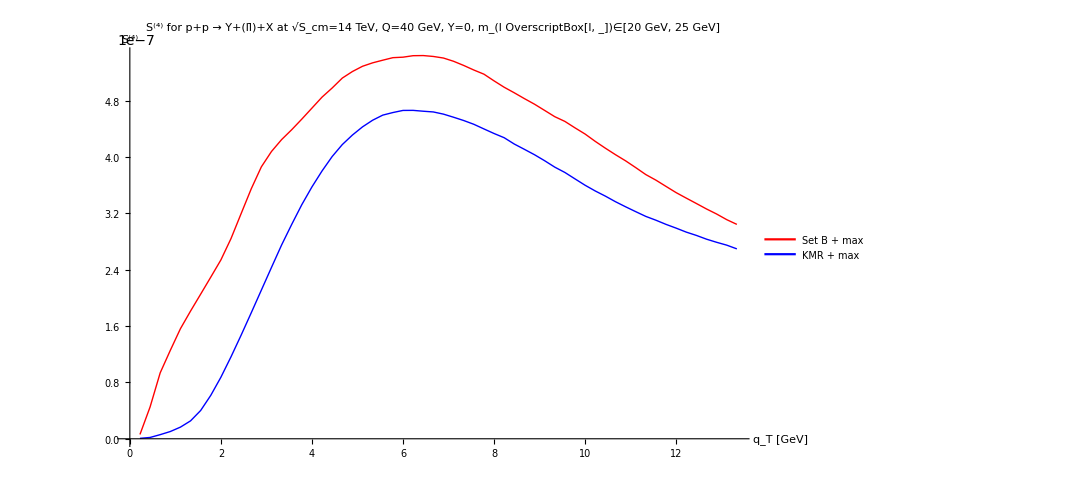

```mathematica
ListPlot[{PlotqTS4SetBDL25,PlotqTS4KMRDL25},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLabel->Text[Style["S^(4) for p+p → Υ+(ll̄)+X at √S_cm=14 TeV, Q=40 GeV, Y=0, m_(l OverscriptBox[l, _])∈[20 GeV, 25 GeV]",FontSize->14]],AxesLabel->{Text[Style["q_T [GeV]",FontSize->14]],Text[Style["S^(4)",FontSize->14]]},PlotLegends->Placed[{"Set B + max","KMR + max"},{0.75,0.25}],TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
PlotNormC4SetADL=NormC4SetA[14000,0,20];
PlotNormC4SetBDL=NormC4SetB[14000,0,20];
PlotNormC4Set1DL=NormC4Set1[14000,0,20];
PlotNormC4Set2DL=NormC4Set2[14000,0,20];
PlotNormC4Set3DL=NormC4Set3[14000,0,20];
PlotNormC4KMRDL=NormC4KMR[14000,0,20];
```

```mathematica
PlotNormC4SetAZ=NormC4SetA[14000,0,120];
PlotNormC4SetBZ=NormC4SetB[14000,0,120];
PlotNormC4Set1Z=NormC4Set1[14000,0,120];
PlotNormC4Set2Z=NormC4Set2[14000,0,120];
PlotNormC4Set3Z=NormC4Set3[14000,0,120];
PlotNormC4KMRZ=NormC4KMR[14000,0,120];
```

```mathematica
PlotNormC4SetBZ=NormC4SetB[14000,0,120];
PlotNormC4KMRZ=NormC4KMR[14000,0,120];
```

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`282379.0068092265` and TraditionalForm`627.2782867446855` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`175545.44325082988` and TraditionalForm`405.5716357166811` for the integral and error estimates.

```mathematica
F4ZΥ[120]/F1ZΥ[120] PlotNormC4SetBZ/PlotNormSetBZ
F4ZΥ[120]/F1ZΥ[120] PlotNormC4KMRZ/PlotNormKMRZ
```

0.0000109378

0.0000104062

```mathematica
PlotNormC4SetBγ20=NormC4SetB[14000,0,20];
PlotNormC4KMRγ20=NormC4KMR[14000,0,20];
```

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`3.313626300483951`*^7 and TraditionalForm`86205.41442192113` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`1.8605580450518448`*^7 and TraditionalForm`26294.589319418086` for the integral and error estimates.

```mathematica
F4DL7Υ[20]/F1DL7Υ[20] PlotNormC4SetBγ20/PlotNormSetBγ20
F4DL7Υ[20]/F1DL7Υ[20] PlotNormC4KMRγ20/PlotNormKMRγ20
```

0.000443165

0.000404685

```mathematica
PlotNormC4SetBγ40=NormC4SetB[14000,0,40];
PlotNormC4KMRγ40=NormC4KMR[14000,0,40];
```

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`7.3064004778615115`*^6 and TraditionalForm`10722.546732012806` for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`3.8342251933733183`*^6 and TraditionalForm`5578.78936628312` for the integral and error estimates.

```mathematica
F4DL25Υ[40]/F1DL25Υ[40] PlotNormC4SetBγ40/PlotNormSetBγ40
F4DL25Υ[40]/F1DL25Υ[40] PlotNormC4KMRγ40/PlotNormKMRγ40
```

0.000122415

0.000108565

Plots for Υ + γ - production:

```mathematica
F4Numγ[14000,20,π/2] PlotNormC4SetADL/2/F1Numγ[14000,20,π/2]/f1g[20/14000,20]^2
F4Numγ[14000,20,π/2] PlotNormC4SetBDL/2/F1Numγ[14000,20,π/2]/f1g[20/14000,20]^2
F4Numγ[14000,20,π/2] PlotNormC4Set1DL/2/F1Numγ[14000,20,π/2]/f1g[20/14000,20]^2
F4Numγ[14000,20,π/2] PlotNormC4Set2DL/2/F1Numγ[14000,20,π/2]/f1g[20/14000,20]^2
F4Numγ[14000,20,π/2] PlotNormC4Set3DL/2/F1Numγ[14000,20,π/2]/f1g[20/14000,20]^2
F4Numγ[14000,20,π/2] PlotNormC4KMRDL/2/F1Numγ[14000,20,π/2]/f1g[20/14000,20]^2
```

0.00793784

0.00633838

0.0076648

0.00457723

0.00714322

0.00356668

```mathematica
Nstep=30;
PlotqTS4SetAγ=ConstantArray[0,{Nstep,2}];
PlotqTS4SetBγ=ConstantArray[0,{Nstep,2}];
PlotqTS4Set1γ=ConstantArray[0,{Nstep,2}];
PlotqTS4Set2γ=ConstantArray[0,{Nstep,2}];
PlotqTS4Set3γ=ConstantArray[0,{Nstep,2}];
PlotqTS4KMRγ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTS4SetAγ[[i,1]]=PlotqTC4SetA[[i,1]];PlotqTS4SetAγ[[i,2]]=π(F4Numγ[14000,20,π/2] PlotqTC4SetA[[i,2]])/(2 π ^2F1Numγ[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS4SetBγ[[i,1]]=PlotqTC4SetB[[i,1]];PlotqTS4SetBγ[[i,2]]=π(F4Numγ[14000,20,π/2] PlotqTC4SetB[[i,2]])/(2 π ^2F1Numγ[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS4Set1γ[[i,1]]=PlotqTC4Set1[[i,1]];PlotqTS4Set1γ[[i,2]]=π(F4Numγ[14000,20,π/2] PlotqTC4Set1[[i,2]])/(2 π ^2F1Numγ[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS4Set2γ[[i,1]]=PlotqTC4Set2[[i,1]];PlotqTS4Set2γ[[i,2]]=π(F4Numγ[14000,20,π/2] PlotqTC4Set2[[i,2]])/(2 π ^2F1Numγ[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS4Set3γ[[i,1]]=PlotqTC4Set3[[i,1]];PlotqTS4Set3γ[[i,2]]=π(F4Numγ[14000,20,π/2] PlotqTC4Set3[[i,2]])/(2 π ^2F1Numγ[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS4KMRγ[[i,1]]=PlotqTC4KMR[[i,1]];PlotqTS4KMRγ[[i,2]]=π(F4Numγ[14000,20,π/2] PlotqTC4KMR[[i,2]])/(2 π ^2F1Numγ[14000,20,π/2] f1g[20/14000,20]^2);]
```

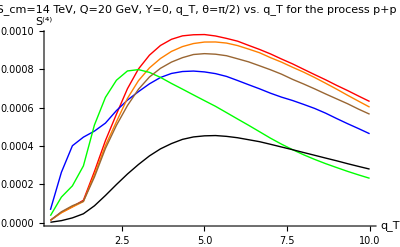

```mathematica
ListPlot[{PlotqTS4SetAγ,PlotqTS4SetBγ,PlotqTS4Set1γ,PlotqTS4Set2γ,PlotqTS4Set3γ,PlotqTS4KMRγ},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick},{Orange,Thick},{Green,Thick},{Brown,Thick},{Black,Thick}},PlotLabel->Text[Style["S^(4)(√S_cm=14 TeV, Q=20 GeV, Y=0, q_T, θ=π/2) vs. q_T for the process p+p → Υ+γ+X",FontSize->14]],AxesLabel->{Text[Style["q_T",FontSize->14]],Text[Style["S^(4)",FontSize->14]]},PlotLegend->{"Set A","Set B","Set 1","Set 2","Set 3","KMR"},LegendPosition->{1.1,-0.4},TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

Plots for Υ + (μ^+μ^-) - production:

```mathematica
F4NumDL[14000,20,π/2] PlotNormC4SetADL/2/F1NumDL[14000,20,π/2]/f1g[20/14000,20]^2
F4NumDL[14000,20,π/2] PlotNormC4SetBDL/2/F1NumDL[14000,20,π/2]/f1g[20/14000,20]^2
F4NumDL[14000,20,π/2] PlotNormC4Set1DL/2/F1NumDL[14000,20,π/2]/f1g[20/14000,20]^2
F4NumDL[14000,20,π/2] PlotNormC4Set2DL/2/F1NumDL[14000,20,π/2]/f1g[20/14000,20]^2
F4NumDL[14000,20,π/2] PlotNormC4Set3DL/2/F1NumDL[14000,20,π/2]/f1g[20/14000,20]^2
F4NumDL[14000,20,π/2] PlotNormC4KMRDL/2/F1NumDL[14000,20,π/2]/f1g[20/14000,20]^2
```

0.00632727-5.7875×10^-29 ⅈ

0.00505233-4.62133×10^-29 ⅈ

0.00610963-5.58843×10^-29 ⅈ

0.00364852-3.33727×10^-29 ⅈ

0.00569387-5.20814×10^-29 ⅈ

0.00284301-2.60048×10^-29 ⅈ

```mathematica
Nstep=30;
PlotqTS4SetADL=ConstantArray[0,{Nstep,2}];
PlotqTS4SetBDL=ConstantArray[0,{Nstep,2}];
PlotqTS4Set1DL=ConstantArray[0,{Nstep,2}];
PlotqTS4Set2DL=ConstantArray[0,{Nstep,2}];
PlotqTS4Set3DL=ConstantArray[0,{Nstep,2}];
PlotqTS4KMRDL=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTS4SetADL[[i,1]]=PlotqTC4SetA[[i,1]];PlotqTS4SetADL[[i,2]]=π(F4NumDL[14000,20,π/2] PlotqTC4SetA[[i,2]])/(2 π ^2F1NumDL[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS4SetBDL[[i,1]]=PlotqTC4SetB[[i,1]];PlotqTS4SetBDL[[i,2]]=π(F4NumDL[14000,20,π/2] PlotqTC4SetB[[i,2]])/(2 π ^2F1NumDL[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS4Set1DL[[i,1]]=PlotqTC3Set1[[i,1]];PlotqTS4Set1DL[[i,2]]=π(F4NumDL[14000,20,π/2] PlotqTC4Set1[[i,2]])/(2 π ^2F1NumDL[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS4Set2DL[[i,1]]=PlotqTC4Set2[[i,1]];PlotqTS4Set2DL[[i,2]]=π(F4NumDL[14000,20,π/2] PlotqTC4Set2[[i,2]])/(2 π ^2F1NumDL[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS4Set3DL[[i,1]]=PlotqTC4Set3[[i,1]];PlotqTS4Set3DL[[i,2]]=π(F4NumDL[14000,20,π/2] PlotqTC4Set3[[i,2]])/(2 π ^2F1NumDL[14000,20,π/2] f1g[20/14000,20]^2);
PlotqTS4KMRDL[[i,1]]=PlotqTC4KMR[[i,1]];PlotqTS4KMRDL[[i,2]]=π(F4NumDL[14000,20,π/2] PlotqTC4KMR[[i,2]])/(2 π ^2F1NumDL[14000,20,π/2] f1g[20/14000,20]^2);]
```

```mathematica
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotqTC4SetA,PlotqTC4SetB,PlotqTC4Set1,PlotqTC4Set2,PlotqTC4Set3,PlotqTC4KMR}]
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotNormC4SetADL,PlotNormC4SetBDL,PlotNormC4Set1DL,PlotNormC4Set2DL,PlotNormC4Set3DL,PlotNormC4KMRDL}]
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotqTS4SetADL,PlotqTS4SetBDL,PlotqTS4Set1DL,PlotqTS4Set2DL,PlotqTS4Set3DL,PlotqTS4KMRDL}]
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotqTC4SetAZ,PlotqTC4SetBZ,PlotqTC4Set1Z,PlotqTC4Set2Z,PlotqTC4Set3Z,PlotqTC4KMRZ}]
Save["~/Dropbox/Work/JPsi/JPsi/Plots",{PlotNormC4SetAZ,PlotNormC4SetBZ,PlotNormC4Set1Z,PlotNormC4Set2Z,PlotNormC4Set3Z,PlotNormC4KMRZ}]
```

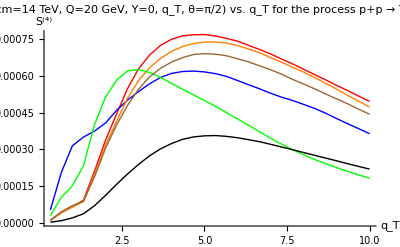

```mathematica
ListPlot[{PlotqTS4SetADL,PlotqTS4SetBDL,PlotqTS4Set1DL,PlotqTS4Set2DL,PlotqTS4Set3DL,PlotqTS4KMRDL},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick},{Orange,Thick},{Green,Thick},{Brown,Thick},{Black,Thick}},PlotLabel->Text[Style["S^(4)(√S_cm=14 TeV, Q=20 GeV, Y=0, q_T, θ=π/2) vs. q_T for the process p+p → Υ+(μ^+μ^-)+X",FontSize->14]],AxesLabel->{Text[Style["q_T",FontSize->14]],Text[Style["S^(4)",FontSize->14]]},PlotLegend->{"Set A","Set B","Set 1","Set 2","Set 3","KMR"},LegendPosition->{1.1,-0.4},TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

Plots for Υ + Z - production:

```mathematica
F4NumZ[14000,120,π/2] PlotNormC4SetAZ/2/F1NumZ[14000,120,π/2]/f1g[120/14000,120]^2
F4NumZ[14000,120,π/2] PlotNormC4SetBZ/2/F1NumZ[14000,120,π/2]/f1g[120/14000,120]^2
F4NumZ[14000,120,π/2] PlotNormC4Set1Z/2/F1NumZ[14000,120,π/2]/f1g[120/14000,120]^2
F4NumZ[14000,120,π/2] PlotNormC4Set2Z/2/F1NumZ[14000,120,π/2]/f1g[120/14000,120]^2
F4NumZ[14000,120,π/2] PlotNormC4Set3Z/2/F1NumZ[14000,120,π/2]/f1g[120/14000,120]^2
F4NumZ[14000,120,π/2] PlotNormC4KMRZ/2/F1NumZ[14000,120,π/2]/f1g[120/14000,120]^2
```

0.00301904

0.0022242

0.00186684

0.00112943

0.00277339

0.00127945

```mathematica
Nstep=60;
PlotqTS4SetAZ=ConstantArray[0,{Nstep,2}];
PlotqTS4SetBZ=ConstantArray[0,{Nstep,2}];
PlotqTS4Set1Z=ConstantArray[0,{Nstep,2}];
PlotqTS4Set2Z=ConstantArray[0,{Nstep,2}];
PlotqTS4Set3Z=ConstantArray[0,{Nstep,2}];
PlotqTS4KMRZ=ConstantArray[0,{Nstep,2}];
For[i=1,i≤Nstep,i++,
PlotqTS4SetAZ[[i,1]]=PlotqTC4SetAZ[[i,1]];PlotqTS4SetAZ[[i,2]]=π(F4NumZ[14000,120,π/2] PlotqTC4SetAZ[[i,2]])/(2 F1NumZ[14000,120,π/2] f1g[120/14000,120]^2);
PlotqTS4SetBZ[[i,1]]=PlotqTC4SetBZ[[i,1]];PlotqTS4SetBZ[[i,2]]=π(F4NumZ[14000,120,π/2] PlotqTC4SetBZ[[i,2]])/(2 F1NumZ[14000,120,π/2] f1g[120/14000,120]^2);
PlotqTS4Set1Z[[i,1]]=PlotqTC3Set1Z[[i,1]];PlotqTS4Set1Z[[i,2]]=π(F4NumZ[14000,120,π/2] PlotqTC4Set1Z[[i,2]])/(2 F1NumZ[14000,120,π/2] f1g[120/14000,120]^2);
PlotqTS4Set2Z[[i,1]]=PlotqTC4Set2Z[[i,1]];PlotqTS4Set2Z[[i,2]]=π(F4NumZ[14000,120,π/2] PlotqTC4Set2Z[[i,2]])/(2 F1NumZ[14000,120,π/2] f1g[120/14000,120]^2);
PlotqTS4Set3Z[[i,1]]=PlotqTC4Set3Z[[i,1]];PlotqTS4Set3Z[[i,2]]=π(F4NumZ[14000,120,π/2] PlotqTC4Set3Z[[i,2]])/(2 F1NumZ[14000,120,π/2] f1g[120/14000,120]^2);
PlotqTS4KMRZ[[i,1]]=PlotqTC4KMRZ[[i,1]];PlotqTS4KMRZ[[i,2]]=π(F4NumZ[14000,120,π/2] PlotqTC4KMRZ[[i,2]])/(2 F1NumZ[14000,120,π/2] f1g[120/14000,120]^2);]
```

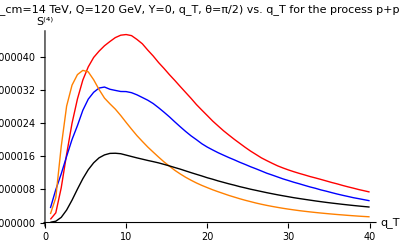

```mathematica
ListPlot[{PlotqTS4SetAZ,PlotqTS4SetBZ,PlotqTS4Set2Z,PlotqTS4KMRZ},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick},{Orange,Thick},{Black,Thick},{Brown,Thick},{Black,Thick}},PlotLabel->Text[Style["S^(4)(√S_cm=14 TeV, Q=120 GeV, Y=0, q_T, θ=π/2) vs. q_T for the process p+p → Υ+Z+X",FontSize->14]],AxesLabel->{Text[Style["q_T",FontSize->14]],Text[Style["S^(4)",FontSize->14]]},PlotLegend->{"Set A","Set B","Set 2","KMR"},LegendPosition->{1.1,-0.4},TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

Polarized Structures:

Convolution C[f_1 f_1]:

```mathematica
C1SetA[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT f1gSetA[Q/sS Exp[Y],kT^2,Q] f1gSetA[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C1SetB[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT f1gSetB[Q/sS Exp[Y],kT^2,Q] f1gSetB[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C1Set1[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT f1gSet1[Q/sS Exp[Y],kT^2,Q] f1gSet1[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C1Set2[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT f1gSet2[Q/sS Exp[Y],kT^2,Q] f1gSet2[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C1Set3[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT f1gSet3[Q/sS Exp[Y],kT^2,Q] f1gSet3[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C1KMR[sS_,Y_,qT_,ϕq_,Q_]:=NIntegrate[(kT f1gKMR[Q/sS Exp[Y],kT^2,Q] f1gKMR[Q/sS Exp[-Y],(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0,∞},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
```

```mathematica
C1UTSetA[xa_,xb_,qT_,ϕq_,Q_]:=NIntegrate[(kT ((kbq/(Sqrt[kb2] qT))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gSetA[xa,kT^2,Q] f1gSetA[xb,(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0.001,10},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C1UTSetB[xa_,xb_,qT_,ϕq_,Q_]:=NIntegrate[(kT ((kbq/(Sqrt[kb2] qT))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gSetB[xa,kT^2,Q] f1gSetB[xb,(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0.001,10},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C1UTSet1[xa_,xb_,qT_,ϕq_,Q_]:=NIntegrate[(kT ((kbq/(Sqrt[kb2] qT))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gSet1[xa,kT^2,Q] f1gSet1[xb,(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0.001,10},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C1UTSet2[xa_,xb_,qT_,ϕq_,Q_]:=NIntegrate[(kT ((kbq/(Sqrt[kb2] qT))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gSet2[xa,kT^2,Q] f1gSet2[xb,(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0.001,10},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C1UTSet3[xa_,xb_,qT_,ϕq_,Q_]:=NIntegrate[(kT ((kbq/(Sqrt[kb2] qT))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gSet3[xa,kT^2,Q] f1gSet3[xb,(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0.001,10},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
C1UTKMR[xa_,xb_,qT_,ϕq_,Q_]:=NIntegrate[(kT ((kbq/(Sqrt[kb2] qT))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gKMR[xa,kT^2,Q] f1gKMR[xb,(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0.001,10},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo",PrecisionGoal->3]
```

```mathematica
C2UT[xa_,xb_,qT_,ϕq_,Q_]:=NIntegrate[(kT (((kbq (2 kaq^2-ka2 qT^2)+2 kaq (kakb qT^2-kaq kbq))/(ka2 Sqrt[kb2] qT^3))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gSetA[xa,kT^2,Q] f1gSetA[xb,(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0.001,10},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo"]
```

```mathematica
C3UT[xa_,xb_,qT_,ϕq_,Q_]:=NIntegrate[(kT (((kb2 qT^2 (kbq (2 kaq^2-ka2 qT^2)+2 kaq (kakb qT^2-kaq kbq))+4 (kbq (kb2 qT^2-kbq^2) (2 kaq^2-ka2 qT^2)-kaq (2 kbq^2-kb2 qT^2) (kakb qT^2-kaq kbq)))/(ka2 Sqrt[kb2]^3 qT^5))/.{kaq->kT qT Cos[ϕ-ϕq],ka2->kT^2,kbq->qT^2-kT qT Cos[ϕ-ϕq],kb2->qT^2+kT^2-2 qT kT Cos[ϕ-ϕq],kakb->kT qT Cos[ϕ-ϕq]-kT^2})f1gSetA[xa,kT^2,Q] f1gSetA[xb,(qT^2+kT^2-2 kT qT Cos[ϕ-ϕq]),Q]),{kT,0.001,10},{ϕ,0,2 π},Method->"AdaptiveMonteCarlo"]
```

```mathematica
FacNum[QN_]:=NIntegrate[(Sin[θ] F2/.{α->Mψ/QN,β->Sqrt[MB2]/QN}/.ReplNumψ/.{Scm->120^2,Q->QN,cθ->Cos[θ]}),{θ,0,π},{MB2,0.1,(QN-3.1)^2}]
FacDen[QN_]:=NIntegrate[(Sin[θ] F1/.{α->Mψ/QN,β->Sqrt[MB2]/QN}/.ReplNumψ/.{Scm->120^2,Q->QN,cθ->Cos[θ]}),{θ,0,π},{MB2,0.1,(QN-3.1)^2}]
```

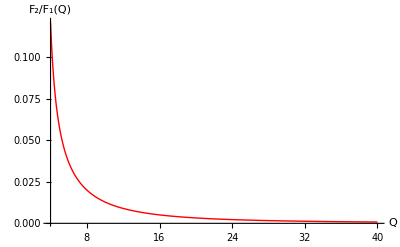

```mathematica
Plot[(FacNum[Q]/FacDen[Q]),{Q,4,40},{PlotStyle->{Red,Thick},AxesLabel->{Text[Style["Q",FontSize->14]],Text[Style["F_2/F_1(Q)",FontSize->14]]},AxesOrigin->{4,0}},PlotRange-> All]
```

```mathematica
AUTSetA[Y_,Q_,qT_,ϕq_]:=C1UTSetA[Q/115 Exp[Y],Q/115 Exp[-Y],qT,ϕq,Q]/C1SetA[115,Y,qT,ϕq,Q]
AUTSetB[Y_,Q_,qT_,ϕq_]:=C1UTSetB[Q/115 Exp[Y],Q/115 Exp[-Y],qT,ϕq,Q]/C1SetB[115,Y,qT,ϕq,Q]
AUTSet1[Y_,Q_,qT_,ϕq_]:=C1UTSet1[Q/115 Exp[Y],Q/115 Exp[-Y],qT,ϕq,Q]/C1Set1[115,Y,qT,ϕq,Q]
AUTSet2[Y_,Q_,qT_,ϕq_]:=C1UTSet2[Q/115 Exp[Y],Q/115 Exp[-Y],qT,ϕq,Q]/C1Set2[115,Y,qT,ϕq,Q]
AUTSet3[Y_,Q_,qT_,ϕq_]:=C1UTSet3[Q/115 Exp[Y],Q/115 Exp[-Y],qT,ϕq,Q]/C1Set3[115,Y,qT,ϕq,Q]
AUTKMR[Y_,Q_,qT_,ϕq_]:=C1UTKMR[Q/115 Exp[Y],Q/115 Exp[-Y],qT,ϕq,Q]/C1KMR[115,Y,qT,ϕq,Q]
```

```mathematica
AUTSetA[-2,10,4,0]
```

0.34426

```mathematica
Timing[Nstep=20;QN=10;YN=-2;ϕqN=0;
AUTPlotSetA=ConstantArray[0,{Nstep+1,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
AUTPlotSetA[[i+1,1]]=qTNum;AUTPlotSetA[[i+1,2]]=AUTSetA[YN,QN,qTNum,ϕqN];]]
```

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`0.019361796820145463` and TraditionalForm`0.00002904457148017198` for the integral and error estimates.

{1240.61,Null}

```mathematica
Timing[Nstep=20;QN=10;YN=-2;ϕqN=0;
AUTPlotSetB=ConstantArray[0,{Nstep+1,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
AUTPlotSetB[[i+1,1]]=qTNum;AUTPlotSetB[[i+1,2]]=AUTSetB[YN,QN,qTNum,ϕqN];]]
```

{1079.76,Null}

```mathematica
Timing[Nstep=20;QN=10;YN=-2;ϕqN=0;
AUTPlotSet1=ConstantArray[0,{Nstep+1,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
AUTPlotSet1[[i+1,1]]=qTNum;AUTPlotSet1[[i+1,2]]=AUTSet1[YN,QN,qTNum,ϕqN];]]
```

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`0.019432766992739856` and TraditionalForm`0.000028215816071721226` for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`19 recursive bisections in TraditionalForm`kT near TraditionalForm`{kT, ϕ} = TraditionalForm`{0.0759758, 0.0962372}. NIntegrate obtained TraditionalForm`0.06954463217435385` and TraditionalForm`0.00007882115516969073` for the integral and error estimates.

{1215.36,Null}

```mathematica
Timing[Nstep=20;QN=10;YN=-2;ϕqN=0;
AUTPlotSet2=ConstantArray[0,{Nstep+1,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
AUTPlotSet2[[i+1,1]]=qTNum;AUTPlotSet2[[i+1,2]]=AUTSet2[YN,QN,qTNum,ϕqN];]]
```

{885.261,Null}

```mathematica
Timing[Nstep=20;QN=10;YN=-2;ϕqN=0;
AUTPlotSet3=ConstantArray[0,{Nstep+1,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
AUTPlotSet3[[i+1,1]]=qTNum;AUTPlotSet3[[i+1,2]]=AUTSet3[YN,QN,qTNum,ϕqN];]]
```

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`0.030425454482180713` and TraditionalForm`0.00003199118807734278` for the integral and error estimates.

{1304.43,Null}

```mathematica
Timing[Nstep=20;QN=10;YN=-2;ϕqN=0;
AUTPlotKMR=ConstantArray[0,{Nstep+1,2}];
For[i=1,i≤Nstep,i++,qTNum=i/Nstep QN/3;
AUTPlotKMR[[i+1,1]]=qTNum;AUTPlotKMR[[i+1,2]]=AUTKMR[YN,QN,qTNum,ϕqN];]]
```

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`0.00007786612557354149` and TraditionalForm`3.4003019070142016`*^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after TraditionalForm`1000100 integrand evaluations. NIntegrate obtained TraditionalForm`0.00022384882029937827` and TraditionalForm`3.315649589125279`*^-7 for the integral and error estimates.

{1355.45,Null}

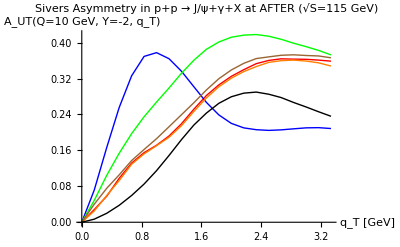

```mathematica
ListPlot[{AUTPlotSetA,AUTPlotSetB,AUTPlotSet1,AUTPlotSet2,AUTPlotSet3,AUTPlotKMR},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick},{Orange,Thick},{Green,Thick},{Brown,Thick},{Black,Thick}},PlotLabel->Text[Style["Sivers Asymmetry in p+p → J/ψ+γ+X at AFTER (√S=115 GeV)",FontSize->14]],AxesLabel->{Text[Style["q_T [GeV]",FontSize->14]],Text[Style["A_UT(Q=10 GeV, Y=-2, q_T)",FontSize->14]]},PlotLegend->{"Set A","Set B","Set 1","Set 2","Set 3","KMR"},LegendPosition->{1.1,-0.4},TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

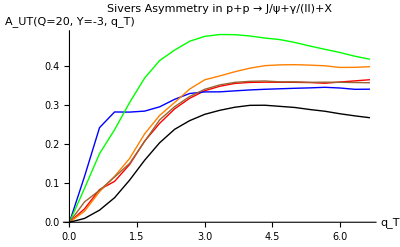

```mathematica
ListPlot[{AUTPlotSetA,AUTPlotSetB,AUTPlotSet1,AUTPlotSet2,AUTPlotSet3,AUTPlotKMR},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick},{Orange,Thick},{Green,Thick},{Brown,Thick},{Black,Thick}},PlotLabel->Text[Style["Sivers Asymmetry in p+p → J/ψ+γ/(ll)+X",FontSize->14]],AxesLabel->{Text[Style["q_T",FontSize->14]],Text[Style["A_UT(Q=20, Y=-3, q_T)",FontSize->14]]},PlotLegend->{"Set A","Set B","Set 1","Set 2","Set 3","KMR"},LegendPosition->{1.1,-0.4},TicksStyle->Directive[Black,14],AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
Timing[Nstep=20;QN=20;qTN=3;ϕqN=0;
AUTPlotSetAY=ConstantArray[0,{Nstep+1,2}];
For[i=0,i≤Nstep,i++,YNum=-2+i/Nstep (-4+2);
AUTPlotSetAY[[i+1,1]]=YNum;AUTPlotSetAY[[i+1,2]]=AUTSetA[YNum,QN,qTN,ϕqN];]]
```

{1410.91,Null}

```mathematica
Timing[Nstep=20;QN=20;qTN=3;ϕqN=0;
AUTPlotSetBY=ConstantArray[0,{Nstep+1,2}];
For[i=0,i≤Nstep,i++,YNum=-2+i/Nstep (-4+2);
AUTPlotSetBY[[i+1,1]]=YNum;AUTPlotSetBY[[i+1,2]]=AUTSetB[YNum,QN,qTN,ϕqN];]]
```

{1499.95,Null}

```mathematica
Timing[Nstep=20;QN=20;qTN=3;ϕqN=0;
AUTPlotSet1Y=ConstantArray[0,{Nstep+1,2}];
For[i=0,i≤Nstep,i++,YNum=-2+i/Nstep (-4+2);
AUTPlotSet1Y[[i+1,1]]=YNum;AUTPlotSet1Y[[i+1,2]]=AUTSet1[YNum,QN,qTN,ϕqN];]]
```

{2136.25,Null}

```mathematica
Timing[Nstep=20;QN=20;qTN=3;ϕqN=0;
AUTPlotSet2Y=ConstantArray[0,{Nstep+1,2}];
For[i=0,i≤Nstep,i++,YNum=-2+i/Nstep (-4+2);
AUTPlotSet2Y[[i+1,1]]=YNum;AUTPlotSet2Y[[i+1,2]]=AUTSet2[YNum,QN,qTN,ϕqN];]]
```

{1481.26,Null}

```mathematica
Timing[Nstep=20;QN=20;qTN=3;ϕqN=0;
AUTPlotSet3Y=ConstantArray[0,{Nstep+1,2}];
For[i=0,i≤Nstep,i++,YNum=-2+i/Nstep (-4+2);
AUTPlotSet3Y[[i+1,1]]=YNum;AUTPlotSet3Y[[i+1,2]]=AUTSet3[YNum,QN,qTN,ϕqN];]]
```

{1636.09,Null}

```mathematica
Timing[Nstep=20;QN=20;qTN=3;ϕqN=0;
AUTPlotKMRY=ConstantArray[0,{Nstep+1,2}];
For[i=0,i≤Nstep,i++,YNum=-2+i/Nstep (-4+2);
AUTPlotKMRY[[i+1,1]]=YNum;AUTPlotKMRY[[i+1,2]]=AUTKMR[YNum,QN,qTN,ϕqN];]]
```

{868.178,Null}

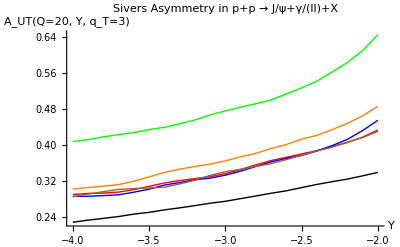

```mathematica
ListPlot[{AUTPlotSetAY,AUTPlotSetBY,AUTPlotSet1Y,AUTPlotSet2Y,AUTPlotSet3Y,AUTPlotKMRY},{Joined->True},PlotStyle->{{Red,Thick},{Blue,Thick},{Orange,Thick},{Green,Thick},{Brown,Thick},{Black,Thick}},PlotLabel->Text[Style["Sivers Asymmetry in p+p → J/ψ+γ/(ll)+X",FontSize->14]],AxesLabel->{Text[Style["Y",FontSize->14]],Text[Style["A_UT(Q=20, Y, q_T=3)",FontSize->14]]},PlotLegend->{"Set A","Set B","Set 1","Set 2","Set 3","KMR"},LegendPosition->{1.1,-0.4},TicksStyle->Directive[Black,14],AxesOrigin->{-2,0},PlotRange->All]
```